```mathematica
dH[userValNew_,userStateNew_,userValOld_,userStateOld_,resValNew_,resStateNew_,resValOld_,resStateOld_,neighbors_]:=Module[
{hui=0,huf=0,hri=0,hrf=0},
Do[
If[neighbors[[i]]==userStateOld,
hui-=1;
];
,{i,1,Length[neighbors]}];
Which[

Do[
If[i==resStateOld,
hui-=resValOld ;];
,{i,0,2}
];
hui-=resOld old;
hri-=resOld old;
Do[
If[neighbors[[i]]==new,
huf-=1;
];
,{i,1,Length[neighbors]}];
huf-=resNew new;
hrf-=resNew new;
Print["H_ui:",hui," H_uf:",huf," ΔH_u:",huf-hui," H_ri:",hri," H_rf:",hrf," ΔH_r:",hrf-hri];
];
```

```mathematica
dH[0,-1,{1,1,-1,-1},-1,1]
```

H_ui:-1 H_uf:0 ΔH_u:1 H_ri:1 H_rf:0 ΔH_r:-1

```mathematica
RandomReal[{-1,1/3}]
```

-0.17968

```mathematica
theStates={1,0};
resMaxDelta=1/3;
resMinDelta=1/6;
Do[
new=RandomInteger[{1,3}];
Which[
new==1,
resLow=-resMinDelta;
resHigh=resMaxDelta;,
new==2,
resLow=-resMinDelta;
resHigh=resMinDelta;,
new==3,
resLow=-resMaxDelta;
resHigh=resMinDelta;];
deltaRes=RandomReal[{resLow,resHigh}];
resNew = resOld+deltaRes;
Which[
resNew>1,
resNew=1,
resNew<-1,
resNew=-1
];
theRes=dH[newState,]
{i,1,20}]
```

```mathematica
-0.071889-0.998445-0.926683-0.996787+0.852046
```

-2.14176

```mathematica
0.303405+0.983748+0.988921+0.950331+0.487815
```

3.71422

```mathematica
(*U[u_,r_]:=Module[
{ret},
Which[
u=="c" &&r=="c", ret=1;,
u=="c" &&r=="n", ret=0.5;,
u=="c" &&r=="d", ret=-1;,
u=="n" &&r=="c", ret=0.5;,
u=="n" &&r=="n", ret=-0.5;,
u=="n" &&r=="d", ret=0.5;,
u=="d" &&r=="c", ret=-1;,
u=="d" &&r=="n", ret=0.5;,
u=="d" &&r=="d", ret=1;
];
ret
];
R[u_,r_]:=Module[
{ret},
Which[
u=="c" &&r=="c", ret=-1;,
u=="c" &&r=="n", ret=1;,
u=="c" &&r=="d", ret=1;,
u=="n" &&r=="c", ret=0;,
u=="n" &&r=="n", ret=0;,
u=="n" &&r=="d", ret=0;,
u=="d" &&r=="c", ret=1;,
u=="d" &&r=="n", ret=1;,
u=="d" &&r=="d", ret=-1;
];
ret
];*)
U[u_,r_]:=Module[
{ret},
Which[
u=="c" &&r=="c", ret=1;,
u=="c" &&r=="n", ret=0.5;,
u=="c" &&r=="d", ret=-1;,
u=="n" &&r=="c", ret=0.5;,
u=="n" &&r=="n", ret=-0.5;,
u=="n" &&r=="d", ret=0.5;,
u=="d" &&r=="c", ret=-1;,
u=="d" &&r=="n", ret=0.5;,
u=="d" &&r=="d", ret=1;
];
ret
];
R[u_,r_]:=Module[
{ret},
Which[
u=="c" &&r=="c", ret=-1;,
u=="c" &&r=="n", ret=0.5;,
u=="c" &&r=="d", ret=1;,
u=="n" &&r=="c", ret=0;,
u=="n" &&r=="n", ret=0;,
u=="n" &&r=="d", ret=0;,
u=="d" &&r=="c", ret=1;,
u=="d" &&r=="n", ret=0.5;,
u=="d" &&r=="d", ret=-1;
];
ret
];
Delta[ui_,ri_,uf_,rf_]:=(ϵ U[uf,rf]+γ R[uf,rf])-(ϵ U[ui,ri]+γ R[ui,ri]);
c="c";n="n";d="d";
```

```mathematica
Do[
Print[u,r,":: ",0.5 R[u,r]+U[u,r]," R:",R[u,r]," U:",U[u,r]],
{u,{c,n,d}},{r,{c,n,d}}
]
```

cc:: 0.5 R:-1 U:1

cn:: 0.75 R:0.5 U:0.5

cd:: -0.5 R:1 U:-1

nc:: 0.5 R:0 U:0.5

nn:: -0.5 R:0 U:-0.5

nd:: 0.5 R:0 U:0.5

dc:: -0.5 R:1 U:-1

dn:: 0.75 R:0.5 U:0.5

dd:: 0.5 R:-1 U:1

```mathematica
ϵ=1.0;γ=1.0;
Do[
Print[ui,ri,"->",uf,rf," ",ToString[Delta[ui,ri,uf,rf]]] ,
{ui,{c}},{uf,{c,n,d}},{ri,{d}},{rf,{c,n,d}}
]
```

cd->cc 0.

cd->cn 1.

cd->cd 0.

cd->nc 0.5

cd->nn -0.5

cd->nd 0.5

cd->dc 0.

cd->dn 1.

cd->dd 0.

```mathematica
ϵ=1.0;γ=1.0;
Do[
Print[ui,ri,"->",uf,rf," ",ToString[Delta[ui,ri,uf,rf]]] ,
{ui,{d}},{uf,{c,n,d}},{ri,{c}},{rf,{c,n,d}}
]
```

dc->cc 0.

dc->cn 1.5

dc->cd 0.

dc->nc 0.5

dc->nn 0.

dc->nd 0.5

dc->dc 0.

dc->dn 1.5

dc->dd 0.

```mathematica
{{Delta[c,c,c,c],Delta[c,c,c,c],Delta[c,c,c,c]}
```

-0.25

```mathematica
-(U["d","c"]-U["c","c"])-(R["d","c"]-R["c","c"])
```

0

```mathematica
-(U["n","d"]-U["d","c"])-(R["n","d"]-R["d","c"])
```

1.

# data

```mathematica
dat={{{3.9,1.6,4.8,3.7,2.1,1.5,5.9,3.5,6.2,6,5.2,3,3.5,2.7,2.4,2.4,0.88,2.5,5.2,5.6,5.1,5.6,6.1,0.1,0.42,5.7,5.6,0.65,4.6,6.2,2.8,2.3,3.4,5.6,0.58,5.6,1.3,1.7,5.7,1.1,1.8,1.4,2.7,2.2,3.7,2.6,1.1,1.6,2.9,1.5,0.69,4,4.5,1.3,5.2,4.6,6.2,0.12,0.36,5.5,0.18,2.3,1.2,1.2,5.5,0.58,2.6,2.2,2.4,0.19,5.6,3.1,0.55,0.75,1.1,5.6,3,4.9,5.7,2,0.041,5.6,0.65,6.3,4.9,5,0.86,5.3,0.047,0.076,0.57,0.55,2.7,2.7,3.4,3.4,4.8,4.3,0.74,2.5},{0.69,4.5,0.27,1.6,4.7,6.1,0.57,5.5,2.7,4.3,3,3.2,2.2,2.2,0.27,4.7,5.7,5.9,2.3,1.6,0.32,0.95,1.6,3.8,5.5,0.9,6.3,6.1,5.2,4.1,1.2,1,1.4,1.9,2.3,2,1.5,3.5,2.9,5.1,1.1,1.7,3.6,5.6,4,2.6,5.3,3.9,6.2,5.1,5.7,0.73,1.7,0.71,1.7,4.1,6,3.4,5.5,2.6,4.3,5,3.1,1.2,3.5,0.37,3.9,6.1,1.3,2.5,3.1,1.7,1.3,5.6,0.46,3.8,2.1,2.7,2.1,5.7,2,1.9,1.2,0.44,4.3,0.32,2.4,2,5.2,2.7,3,5.8,1.2,4.4,0.51,1.8,1.8,2.2,4.2,4.9}},{{3.7,1.6,2.8,3.7,4.2,4.6,5.9,0.9,6.2,6,5.2,3,3.5,2.7,2.4,3.3,3.4,1.8,0.074,5.6,5.1,0.054,6.1,0.1,0.42,5.7,5.6,0.65,4.6,6.2,5.9,2.3,3.4,1.3,0.76,5.6,4.9,5.4,5.7,1.1,1.8,2.8,2.7,2.2,1.5,2.6,1.1,2.9,0.41,1.5,0.4,2.6,4.5,1.3,5.2,4.6,0.83,2.2,5,5.5,0.18,2.3,1.2,6,5.5,4.8,2.6,2.2,2.1,1.5,0.49,0.54,0.55,0.75,1.1,5.6,3.4,5,5.7,2,0.041,5.6,0.65,6.3,4.9,6,0.71,5.3,0.047,0.076,0.57,0.22,2.7,2.7,3.4,5.2,4.8,4.3,1.9,2.5},{0.072,4.5,1.9,1.6,0.67,5,0.57,2.8,2.7,4.3,3,3.2,2.2,2.2,0.27,4.6,5.4,0.69,2.1,1.6,0.32,2.1,1.6,3.8,5.5,0.9,6.3,6.1,5.2,4.1,3.2,1,1.4,0.3,2.1,2,0.77,1,2.9,5.1,1.1,0.061,3.6,5.6,0.73,2.6,5.3,2.3,4.2,5.1,5.1,2,1.7,0.46,1.7,4.1,0.45,4.3,5.1,2.6,4.3,5,3.1,5.4,3.5,3.9,3.9,6.1,2.8,4.9,4.1,3.2,1.3,5.6,0.46,3.8,0.41,5.2,2.1,5.7,2,1.9,1.2,0.44,4.3,4.7,1.3,2,5.2,2.7,3,0.49,1.2,4.4,0.51,5.7,1.8,2.2,0.53,4.9}},{{3.9,1.6,2.8,3.7,4.2,4.6,5.9,0.9,6.2,6,5.2,4.4,3.5,2.7,4.1,3.3,1.3,1.8,0.23,5.6,5.1,1.4,3.5,2.1,4.3,5.7,5.6,0.65,4.6,6.2,3.4,2.3,3.4,2.9,0.76,5.7,0.41,5.4,5.7,1.1,1.8,3.1,4,3.3,1.5,5.8,1.2,1.4,0.41,6,0.4,2.6,4.5,4.5,5.2,4.5,0.83,2.2,0.063,3.4,3.3,2.3,1.2,0.85,5.5,4.8,0.83,2.2,1.5,1.5,0.49,0.54,0.55,0.75,5.9,5.6,2.5,5,5.7,0.1,0.041,6.2,0.043,6.3,0.26,6,5.2,4.4,4.9,0.076,0.57,1.2,2.7,3.8,3.4,5.2,4.8,4.3,5.4,4.7},{2.1,4.5,1.9,1.6,0.67,5,0.57,2.8,2.7,4.3,3,6.2,2.2,2.2,0.082,4.6,3.5,0.69,6.1,1.6,0.32,1.6,4,4.7,3.3,0.9,6.3,6.1,5.2,4.1,5.9,1,1.4,2.9,2.1,3.5,3.9,1,2.9,5.1,1.1,1.2,0.025,4.2,0.73,2.4,3,1.1,4.2,2.8,5.1,2,1.7,2.5,1.7,4.6,0.45,4.3,0.75,4.7,3.8,5,3.1,0.97,3.5,3.9,6,6.1,6.2,4.9,4.1,3.2,1.3,5.6,0.73,3.8,1.9,5.2,2.1,6.2,2,4.5,5.8,0.44,4.8,4.7,5.9,1.7,4.5,2.7,3,0.6,1.2,4,0.51,5.7,1.8,2.2,3.3,6.2}},{{3.9,2.4,2.8,3.2,4.2,4.6,5.9,0.9,0.59,6,5.2,4.4,3.5,2.7,4.1,3.3,1.3,1.8,0.23,5.6,6.2,1.4,3.5,2.1,4.3,5.7,5.6,0.65,0.28,4.7,2.9,2.3,3.4,2.9,4.3,5.7,0.41,5.4,5.7,6.1,1.2,3.1,4,4.5,4.7,5.8,0.42,1.4,1.9,6,0.4,3.2,4,4.5,5.4,0.065,0.83,2.2,2.2,1.2,5.9,1.6,1.9,0.85,5.8,4.8,0.83,1.4,1.7,1.5,0.54,0.61,0.55,0.75,0.37,5.6,0.007,5,5.7,0.47,0.041,6.2,0.36,6.3,0.56,6,5.2,4.4,4.9,0.076,0.57,1.2,2.7,5,5.4,5.2,4.8,4.6,5.2,4.7},{2.1,0.98,1.9,3.2,0.67,5,0.57,2.8,2.6,4.3,3,6.2,2.2,2.2,0.082,4.6,3.5,0.69,6.1,1.6,2.4,1.6,4,4.7,3.3,0.9,6.3,6.1,5.6,0.89,1.8,1,1.4,2.9,2.1,3.5,3.9,1,2.9,2.2,5.4,1.2,0.025,0.35,5.4,2.4,4.8,1.1,1.5,2.8,5.1,4.3,0.23,2.5,2.2,1.5,0.45,4.3,1.4,1.2,2.2,5.4,0.57,0.97,4.9,3.9,6,2.1,6.2,4.9,2,2,1.3,5.6,1.9,3.8,4.8,5.2,2.1,2.7,2,4.5,1.3,0.44,0.99,4.7,5.9,1.7,4.5,2.7,3,0.6,1.2,2.5,4.1,5.7,1.8,0.88,2.3,6.2}},{{3.9,2.4,2.8,3.2,4.2,4.6,5.9,0.9,1.1,6,5.2,1.3,3.1,2.7,4.4,3.3,3.2,1.8,0.23,5.6,6.2,1.4,3.5,2.1,4.3,5.7,5.6,0.65,5.5,4.7,2.9,2.9,3.4,2.9,4.3,5.7,0.061,5.4,5.7,6.1,1.2,3.1,4,4.5,4.7,5.8,0.42,1.4,1.7,6.1,0.4,3.2,4,4.5,5.4,0.065,0.83,2.2,2.2,0.95,5.9,1.6,6,6.1,5.8,4.8,0.83,1.4,1.7,0.97,0.54,0.61,0.55,0.86,0.61,5.6,5.1,5,5.7,0.47,0.49,6.2,0.23,0.69,0.56,6,5.2,5.2,4.9,0.076,0.57,1.2,2.7,4.2,0.37,5.2,4.8,4.6,5.2,5.1},{2.1,0.98,1.9,3.2,0.67,5,0.57,2.8,3.6,4.3,3,1.7,0.89,2.2,0.95,4.6,3.7,0.69,6.1,1.6,2.4,2,4,4.7,3.3,0.9,6.3,6.1,5.4,0.89,1.8,2.4,1.4,2.9,2.1,3.5,0.7,1,2.9,2.2,5.4,1.2,0.025,0.35,5.4,2.4,4.8,1.1,5.6,2.8,5.1,4.3,0.23,2.5,2.2,1.5,0.45,4.3,1.4,5.6,2.2,5.4,1.6,0.92,4.9,3.9,6,2.1,6.2,4.3,2,2,1.3,5.7,3.7,3.8,5.4,5.2,2.1,2.7,0.12,4.5,3.4,4,0.99,4.7,5.9,3,4.5,2.7,3,0.6,1.2,4.8,0.59,5.7,1.8,0.88,2.3,0.06}},{{3.9,3.1,2.8,3.2,3.5,4.6,4.4,0.31,1.1,6,5.7,1.3,3.1,2.7,3,3.6,2.3,4,0.23,5.6,0.54,1.4,3.2,2.1,4.3,5.7,5.6,4.5,5.5,4.7,2.9,2.9,3.4,2.9,4.3,5.7,0.061,0.23,5.8,5,1.2,3.1,4,4.5,4.7,5.8,0.42,1.4,0.047,6.1,4.6,3.2,3.9,4.5,4.7,0.065,0.83,2.2,2.2,1.1,0.6,1.6,6,5.5,5.8,4.8,1.1,1.4,0.75,0.97,0.54,0.61,0.55,6.3,0.61,5.1,5.1,0.51,5.7,0.47,5.9,6.2,0.23,0.69,0.56,4.9,5.2,5.2,5,5.1,0.57,1.2,2.7,0.84,0.37,5.2,4.8,4.6,6,5.1},{2.1,3.7,1.9,3.2,2.5,5,2.7,1.8,3.6,4.3,5.8,1.7,0.89,2.2,4.4,0.045,5.1,3.2,6.1,1.6,3.4,2,4.8,4.7,3.3,0.9,6.3,0.99,5.4,0.89,1.8,2.4,1.4,2.9,2.1,3.5,0.7,0.34,3.1,4.5,5.4,1.2,2.2,0.35,5.4,2.4,4.8,1.1,2.2,2.8,4.9,4.3,2.8,2.5,1.2,1.5,0.45,4.3,1.4,0.48,4.6,5.4,1.6,2,4.9,3.9,3.5,2.1,1.6,4.3,2,2,1.3,5.1,3.7,5,5.4,5,2.1,2.7,0.88,4.5,3.4,4,0.99,3,5.9,3,0.42,0.78,3,0.6,1.2,0.5,0.59,5.7,1.8,0.88,4.1,0.06}},{{3.3,3.1,2.8,3.2,3.5,4.6,4.4,5.7,0.84,6,5.7,1.3,3.1,2.7,3,2.8,0.48,5.6,5.5,5.6,0.54,1.4,3.2,2.5,4.3,3.7,0.4,4.5,5.5,4.7,3.1,2.9,2.7,2.9,4.3,5.7,0.061,0.23,5.8,5,0.11,3.1,4,4.5,4.7,5.8,0.42,1.4,0.047,5.7,0.69,3.2,0.23,4.5,4.7,0.065,0.83,2.2,2.2,0.64,0.6,1.9,6,5.5,5.8,4.8,0.95,0.69,0.057,0.97,0.54,0.61,0.55,0.87,0.61,5.1,5.3,4.7,5.7,0.47,5.9,6.2,0.23,1.7,0.56,4.9,5.2,5.2,5,5.1,4.4,1.2,2.7,1.3,1.4,5.2,4.8,4.6,6,5.1},{3.4,3.7,1.9,3.2,2.5,5,2.7,2.3,4.1,4.3,5.8,1.7,0.89,2.2,4.4,3.6,4.6,0.0084,1.7,1.6,3.4,2,4.8,0.57,3.3,0.72,6.3,0.99,5.4,0.89,1,2.4,2.7,2.9,2.1,3.5,0.7,0.34,3.1,4.5,0.59,6.3,2.2,0.35,5.4,2.4,4.8,1.1,2.2,5.6,0.22,4.3,0.54,5.5,1.2,1.5,0.45,4.3,1.4,1.5,4.6,4.3,1.6,2,4.9,3.9,5.7,4.3,2.1,4.3,2,2,1.3,1.4,3.7,5,0.56,1.9,2.1,2.7,0.88,4.5,3.4,2.7,0.99,3,5.9,3,0.42,0.78,2.9,0.6,1.2,4.2,0.77,5.7,1.8,0.88,4.1,0.06}},{{3.9,3.1,2.8,3.2,3.5,4.6,4.4,5.7,0.84,4.9,5.9,1,0.066,2.7,3,2.8,0.041,5.2,5.2,5.5,0.54,1.4,1.6,2.5,4.3,3.7,0.4,4.5,5.5,5.7,3.1,2.9,2.7,2.9,3.7,5.7,0.061,0.23,5.8,5.6,2.2,3,4,3.7,4.7,0.035,6.2,6,5.6,5.7,0.69,2.4,0.23,4.5,4.7,4.7,0.83,2.2,2.2,0.64,0.6,1.9,6,5.4,5.8,0.37,0.95,0.69,0.057,0.97,0.54,0.61,0.55,0.87,0.57,5.1,5.3,4.7,5.7,0.47,5.9,6.2,0.51,1.7,0.56,4.9,5.2,5.2,5,5.1,4.4,2.9,2.6,1.3,1.4,5.2,4.8,5.4,6,5.1},{3.4,3.7,1.9,3.2,2.5,5,2.7,2.3,4.1,4.2,0.8,0.054,5.5,2.2,4.4,3.6,4.1,3.8,4.3,5.1,3.4,2,2.9,0.57,3.3,0.72,6.3,0.99,5.4,5.1,1,2.4,2.7,2.9,1.2,3.5,0.7,0.34,3.1,4.5,0.11,5.2,2.2,0.59,5.4,5.1,5.1,1,4,5.6,0.22,2.3,0.54,5.5,1.2,2.9,0.45,4.3,1.4,1.5,4.6,4.3,1.6,2,4.9,6,5.7,4.3,2.1,4.3,2,2,1.3,1.4,3.5,5,0.56,1.9,2.1,2.7,0.88,4.5,2.8,2.7,0.99,3,5.9,3,0.42,0.78,2.9,2.8,0.95,4.2,0.77,5.7,1.8,0.8,4.1,0.06}},{{4.4,3.1,2.8,3.2,3.5,4.6,4.4,5,0.84,4.9,5.9,1,0.066,2.7,3,2.8,0.041,5.2,0.043,5.5,3.9,3,1.6,2.5,4.3,0.75,0.4,4.5,5.5,5.7,2.3,2.7,2.7,2.9,3.6,5.7,0.061,6,5.8,4.7,2.1,3,4,3.7,4.7,5.9,6.2,6,5.6,5.7,0.69,4.1,0.42,4.5,3.7,1.4,0.83,2,1.2,0.64,0.6,5.7,6,5.4,0.19,0.44,6,0.69,0.057,0.97,5.7,0.61,0.55,5.9,0.39,5.1,5.3,5.5,6.1,0.47,5.9,6.2,0.42,0.96,0.56,4.9,5.2,5.2,5,5.1,4.4,2.8,0.73,1.3,4.4,5.2,4.8,5.4,6,5.1},{0.62,3.7,1.9,3.2,2.5,5,2.7,0.13,4.1,4.2,0.8,0.054,5.5,2.2,4.4,3.6,4.1,3.8,5.7,5.1,5.8,1.9,2.9,0.57,3.3,4.1,6.3,0.99,5.4,5.1,0.82,6.2,2.7,2.9,1.2,3.5,0.7,2.2,3.1,2.6,3.7,5.2,2.2,0.59,5.4,6,5.1,1,4,5.6,0.22,3.5,4.3,5.5,6.1,0.36,0.45,5.8,6.3,1.5,4.6,0.5,1.6,2,0.28,2.3,2.9,4.3,2.1,4.3,4.9,2,1.3,4,4.1,5,0.56,4.4,0.84,2.7,0.88,4.5,3.9,5.6,0.99,3,5.9,3,0.42,0.78,2.9,6.1,1.5,4.2,5,5.7,1.8,0.8,4.1,0.06}},{{4.4,3.1,3.1,3.2,3.5,4.6,5.9,5,4.2,4.9,6,1,1.1,2.7,3,2.8,0.24,5.7,0.043,5.5,3.9,1.5,1.6,2.5,3.6,0.75,0.4,0.85,5.5,5.7,2.3,3.1,3.2,2.9,3.6,6.3,6,6,5.8,4.7,4.6,3.3,4,3.7,4.7,5.9,6.2,6,5.6,0.4,0.76,0.66,6.1,5.2,1,1.4,0.83,0.23,0.24,0.64,0.6,5.7,6,5.4,0.19,0.12,0.25,1.2,1.8,0.97,1.9,1.6,0.18,5.9,0.39,5.1,5.3,5.5,6.1,0.28,5.9,6.2,0.42,0.56,4.6,5.1,5.2,5.1,5,5.1,4.4,5.9,2,3.1,4.4,5.2,5.8,5.4,6,5.1},{0.62,3.7,0.62,3.2,2.5,5,1.1,0.13,0.15,4.2,1.1,0.054,1.4,2.2,4.4,3.6,3.9,5.1,5.7,5.1,5.8,5,2.9,0.57,4.4,4.1,6.3,6.2,5.4,5.1,0.82,3.1,1.6,2.9,1.2,1.6,1.4,2.2,3.1,2.6,0.13,4.3,2.2,0.59,5.4,6,5.1,1,4,1.3,4.7,3.4,5.7,0.77,5.9,0.36,0.45,0.46,3.4,1.5,4.6,0.5,1.6,2,0.28,2,5.5,5.8,0.34,4.3,1.8,0.39,4.1,4,4.1,5,0.56,4.4,0.84,0.85,0.88,4.5,3.9,6,0.76,0.81,5.9,0.4,0.42,0.78,2.9,6.3,4.7,5,5,5.7,1.6,0.8,4.1,0.06}},{{3.9,3.8,3.1,3.2,3.5,4.6,5.9,4.9,4.2,4.6,2,1,1.3,2.7,3,2.8,0.24,5.7,4.4,5.5,3.9,1.5,1.6,2.5,1.7,0.75,0.4,0.85,5.9,5.5,3.7,3.1,3.2,2.9,0.36,0.61,6.1,0.26,5.8,4.7,4.7,3.4,4,3.7,4.7,5.9,0.81,6,5.6,0.4,0.76,0.45,6.1,5.2,1,1.4,0.83,0.71,0.24,0.64,0.58,0.42,6,5.4,0.19,0.12,0.25,1.2,0.44,0.97,1.9,1.6,0.18,6.2,5.3,5.6,6.2,5.5,6.1,0.28,5.9,0.16,6.2,3.7,4.6,5.1,5.2,5.1,5.2,5.1,4.4,5.9,2,3.1,4.4,5.2,5.8,5.4,6,5.1},{2.8,2.6,0.62,3.2,2.5,5,1.1,0.77,0.15,1,6,0.054,0.85,2.2,4.4,3.6,3.9,5.1,0.69,5.1,5.8,5,2.9,0.57,5.6,4.1,6.3,6.2,3.1,2.8,0.36,3.1,1.6,2.9,4.3,6.1,1.6,5.1,3.1,2.6,4.6,3.8,2.2,0.59,5.4,6,2.7,1,4,1.3,4.7,3.5,5.7,0.77,5.9,0.36,0.45,4.2,3.4,1.5,0.33,3.8,1.6,2,0.28,2,5.5,5.8,2.7,4.3,1.8,0.39,4.1,5.2,4.2,3.5,2.9,4.4,0.84,0.85,0.88,1.2,1.8,0.89,0.76,0.81,5.9,0.4,3.8,0.78,2.9,6.3,4.7,5,5,5.7,1.6,0.8,4.1,0.06}},{{3.9,1.7,3.1,3.2,3.5,4.6,5.9,4.9,5.2,3.9,3.6,2.6,1.3,2.7,3,4.9,0.24,5.7,4.6,5,3.9,4.5,1.6,2.5,2.3,5.8,5.4,0.85,5.9,4.6,3.7,3.1,3.2,3.3,2.7,0.61,6.1,0.26,5.8,5.9,4.7,3.4,4,3.7,4.7,5.9,0.81,6,5.6,0.4,5.2,0.45,6.1,5.2,4.5,1.2,0.062,0.71,0.24,0.64,0.58,0.42,6,5.4,0.19,6.2,5.8,5.6,0.44,0.97,1.9,1.6,0.18,6.2,5.3,5.6,6.2,5.5,5.6,1.6,5.9,0.16,6.2,5.6,4.6,5.1,5.2,5.1,5.2,4.3,4.4,4.7,3.9,3.1,4.4,5.2,6.1,5.4,4.7,5.1},{2.8,4.4,0.62,3.2,2.5,5,1.1,0.77,2.5,1.5,1.8,4.1,0.85,2.2,4.4,5,3.9,5.1,2,2.9,5.8,5.6,2.9,0.57,0.5,0.63,1.8,6.2,3.1,2.3,0.36,3.1,1.6,1.7,0.95,6.1,1.6,5.1,3.1,4.2,4.6,3.8,2.2,0.59,5.4,6,2.7,1,4,1.3,2,3.5,5.7,0.77,1.9,0.22,2.6,4.2,3.4,1.5,0.33,3.8,1.6,2,0.28,3.2,5.6,0.33,2.7,4.3,2.9,0.39,4.1,5.2,4.2,3.5,2.9,4.4,1.3,1.5,0.88,1.2,1.8,2.1,0.76,0.81,5.9,0.4,3.8,3.3,2.9,0.36,2.7,5,5,5.7,5.8,0.8,5.4,0.06}},{{3.9,0.56,3.1,3.2,3.5,4.8,5.9,4.9,5.2,3.9,3.6,2.6,1.3,2,2.1,4.9,0.24,1.1,5.8,3.2,4,4.5,4,3,2.3,5.8,5.4,5.4,5.9,4.6,3.7,3.1,3.2,3.3,2.7,0.61,6.1,0.26,5.8,5.9,4.8,5.3,4,4.4,4.7,5.9,0.81,6,5.6,0.4,1.1,0.45,6.1,5.2,4.5,1.2,0.062,0.71,0.24,0.64,0.58,0.98,0.24,6,6.1,6.2,6.3,0.8,0.44,0.97,1.9,1.6,0.18,6.2,5.3,5,5.6,5.5,0.92,1.3,5.9,4,2.3,5.8,5.6,5.1,5.2,5.1,5.2,4.5,5.5,4.7,4.6,3.1,4.8,5.2,6.1,5.4,4.7,5.1},{2.8,3.6,0.62,3.2,2.5,6.2,1.1,0.77,2.5,1.5,1.8,4.1,0.85,2.2,5.4,5,3.9,0.15,2.7,0.6,3.4,5.6,3.2,0.5,0.5,0.63,1.8,4.2,3.1,2.3,0.36,3.1,1.6,1.7,0.95,6.1,1.6,5.1,3.1,4.2,5.2,3.8,2.2,6,5.4,6,2.7,1,4,1.3,0.64,3.5,5.7,0.77,1.9,0.22,2.6,4.2,3.4,1.5,0.33,5.1,2.5,3,0.03,3.2,5.5,0.52,2.7,4.3,2.9,0.39,4.1,5.2,4.2,6.2,5.3,4.4,2.4,3.6,0.88,3.4,2.6,1.5,2.1,0.81,5.9,0.4,3.8,0.15,0.25,0.36,2.4,5,2.5,5.7,5.8,0.8,5.4,0.06}},{{3.9,0.56,3.1,3.2,3.5,4.8,5.9,6.2,5.2,0.044,3.6,5.2,1.3,2.5,2.1,4.9,0.54,5.9,5.8,5.1,4,2.5,2.2,2.9,2.3,5.8,5.4,5.4,5.9,5.1,3.7,3.1,3.2,3.3,2.7,0.61,6.1,0.26,5.8,5.5,4.8,4.5,4.9,4.4,4.7,6,0.81,6,5.6,0.17,1.1,0.45,6.1,5.2,5.7,5.8,0.062,0.71,0.24,0.64,1,0.53,0.24,6,6.1,6.2,6.3,6.1,0.44,0.97,1.9,3.5,0.18,6.2,5.3,5,5.5,5.5,0.92,1.3,4,4,2.3,5.8,5.6,5.1,5.6,5.4,4.7,0.45,5.5,4.7,2.1,3.1,3.1,5.1,6.1,5.4,4.7,5},{2.8,3.6,0.62,3.2,2.5,6.2,1.1,5.1,2.5,2.4,1.8,4.7,0.85,5.1,5.4,5,0.23,4.7,2.7,5.7,3.4,1.4,0.62,1.3,0.5,0.63,1.8,4.2,3.1,5.7,0.36,3.1,1.6,1.7,0.95,6.1,1.6,5.1,3.1,1.2,5.2,2.3,5.4,6,5.4,4.6,2.7,1,4,4.2,0.64,3.5,5.7,0.77,3.2,0.7,2.6,4.2,3.4,1.5,3,3.4,2.5,3,0.03,3.2,5.5,3.4,2.7,4.3,2.9,0.53,4.1,5.2,4.2,6.2,3.4,4.4,2.4,3.6,0.073,3.4,2.6,1.5,2.1,0.81,4.2,2.5,6.3,0.97,0.25,0.36,3.3,5,0.99,1.4,5.8,0.8,5.4,4.4}},{{4.1,2.1,2.7,2.9,4,4.8,2.8,6.2,5.2,5.8,4.8,3.5,1.2,3,3.9,4.7,1.1,5.9,5.8,5.1,4,2.5,2.2,2.9,3.8,0.5,5.4,5.6,5.9,4.8,3.7,3.1,3.2,3.5,1.4,0.16,6.1,0.26,5.8,5.6,4.8,4.5,4.9,4.4,4.7,6,0.81,0.47,5.6,0.17,1.1,0.36,6.1,0.31,5.7,5.8,0.062,0.71,0.24,0.64,1,1.4,0.24,6,6.1,6.2,5.8,6.1,0.29,0.97,1.9,1.4,5.2,6.2,5.3,5,5.5,5.5,6.1,5.7,0.37,4,2.3,0.81,5.6,5.1,5.3,5.4,4.7,3.7,5.5,4.7,4.4,0.68,4.5,5.1,6.1,5.4,4.7,4.9},{2.8,5,2.5,4.6,6.2,6.2,2.6,5.1,2.5,5.7,3.4,2.6,6.1,4.4,0.7,0.96,3.1,4.7,2.7,5.7,3.4,1.4,0.62,1.3,4.3,6.2,1.8,4.8,3.1,2.8,0.36,3.1,1.6,2.7,3.9,4.8,1.6,5.1,3.1,2,5.2,2.3,5.4,6,5.4,4.6,2.7,2,4,4.2,0.64,0.14,5.7,0.96,3.2,0.7,2.6,4.2,3.4,1.5,3,0.45,2.5,3,0.03,3.2,2.5,3.4,1.1,4.3,2.9,2.8,3.9,5.2,4.2,6.2,3.4,4.4,4.4,3.1,5.2,3.4,2.6,1.9,2.1,0.81,1.5,2.5,6.3,1.8,0.25,0.36,2.4,6,0.094,1.4,5.8,0.8,5.4,0.31}},{{4.1,2.1,1.3,2.9,4,4.8,5.5,6.2,5.2,5.8,4.4,2.2,1.9,3,3.9,4.7,0.11,5.9,5.8,5.1,4,2.5,4.3,4.8,3.8,2.3,6,5.6,5.1,4.8,3.7,3.9,3.2,3.5,1.4,0.16,6.1,0.055,5.8,5.6,4.8,4.5,4.9,4.4,5.1,6,0.81,0.47,5.6,0.17,4.9,0.36,6.1,5.4,5.7,5.8,0.062,0.71,0.24,0.64,1,0.94,0.24,6,6.1,6.2,5.8,6.1,0.29,0.97,1.7,1.4,5.2,6.2,5.3,5,5.5,5.5,6.1,0.77,2.8,4,5.2,0.35,5.6,5.1,5.3,5.8,4.7,5,4.8,4.7,4.4,1,4.5,5.1,3.2,5.4,4.7,4.9},{2.8,5,0.037,4.6,6.2,6.2,0.075,5.1,2.5,5.7,2,0.69,4.4,4.4,0.7,0.96,1.7,4.7,2.7,5.7,3.4,1.4,3.5,0.21,4.3,5.7,1.9,4.8,3.8,2.8,0.36,2.6,1.6,2.7,3.9,4.8,1.6,1,3.1,2,5.2,2.3,5.4,6,5,4.6,2.7,2,4,4.2,3.6,0.14,5.7,1,3.2,0.7,2.6,4.2,3.4,1.5,3,5.9,2.5,3,0.03,3.2,2.5,3.4,1.1,4.3,3.8,2.8,3.9,5.2,4.2,6.2,3.4,4.4,4.4,1.9,5.1,3.4,2.2,4.7,2.1,0.81,1.5,5,6.3,3.1,1.8,0.36,1.7,6,0.094,1.4,5.3,0.8,5.4,0.31}},{{4.1,2.7,2.7,2.9,4,3.5,5.5,5.6,5.2,4.1,4.4,2.2,1.9,3,3.9,1.7,0.11,5.9,5.8,5.1,4.7,2.5,3.6,4.8,2.6,2.3,0.21,5.6,5.1,4.8,3.7,3.9,3.2,3.5,1.4,0.16,6.1,0.055,5.8,5.6,4.8,4.5,4.9,4.4,5.1,0.0098,0.81,0.47,0.087,0.17,4.9,5.3,5.7,5.4,5.7,5.8,0.015,0.4,0.76,0.64,1,0.94,0.24,6,6.1,5.9,5.8,6.1,0.29,0.97,1.7,3.2,5.2,6.2,5.3,5,5.5,5.4,6.1,0.77,2.1,4,5.2,0.35,5.4,5.1,5.3,5.8,4.7,5.1,4.9,4.9,4.4,1,4.5,5.1,3.2,5.5,6.2,6.3},{2.8,3.3,1.6,4.6,6.2,3.9,0.075,1.4,2.5,5.3,2,0.69,4.4,4.4,0.7,5.6,1.7,4.7,2.7,5.7,1.7,1.4,0.014,0.21,1.7,5.7,0.41,4.8,3.8,2.8,0.36,2.6,1.6,2.7,3.9,4.8,4.2,1,3.1,2,5.2,2.3,5.4,6,5,1.3,2.7,2,2.2,4.2,3.6,4.2,0.82,1,3.2,0.7,4.2,6.1,5.6,1.5,5.5,5.9,2.5,3,0.03,5.2,2.5,3.4,1.1,4.3,3.8,5.4,3.9,5.2,4.2,6.2,3.4,0.97,4.4,1.9,5.3,3.4,2.2,4.7,5.4,0.81,1.5,5,6.3,4.7,0.36,2.5,1.7,6,0.094,1.4,5.3,3.2,1.6,3.7}},{{4.1,2.7,2.7,2.9,4,3.5,5.5,5.6,5.9,4.4,4,5,1.1,3,3.4,1.7,1.9,5.9,5.8,6.1,3.8,2.5,2.6,3.2,2.6,2.3,1.2,5.6,5.1,4.8,3.7,3.9,3.2,3.1,5,0.24,6.1,0.56,5.8,5.6,4.8,4.5,4.9,4.4,5.1,0.83,0.81,0.12,0.087,0.17,5.7,5.3,5.7,5.4,5.7,6.1,0.015,0.12,0.98,0.64,1,5.3,0.24,6,6.1,5.9,5.8,6.1,0.29,0.97,0.9,6.2,0.67,6.2,5.3,5,5.5,5.4,6.1,0.77,2.1,4.1,5.2,0.35,5.4,5.1,4.7,5.8,4.7,5.1,4.9,4.9,4.4,1,4.5,5.1,3.2,5.5,5.7,6.3},{2.8,3.3,1.6,4.6,6.2,3.9,0.075,1.4,0.025,5.1,5.2,0.21,4.8,4.4,0.77,5.6,5.9,2.9,2.7,5.5,3.3,1.4,4.9,0.71,1.7,5.7,0.85,4.8,3.8,2.8,0.36,2.6,1.6,4.5,0.63,3.6,4.2,3,3.1,2,5.2,2.3,5.4,6,5,1.1,2.7,0.89,2.2,4.2,5.6,4.2,0.82,1,3.2,5.3,4.2,2.2,5.2,1.5,5.5,3.3,2.5,3,2.8,5.2,2.5,3.4,1.1,4.3,3.3,4.3,5.4,5.2,4.2,6.2,3.4,0.97,4.4,1.9,5.3,5.7,2.2,4.7,5.4,0.81,2.1,5,6.3,4.7,0.36,2.5,1.7,6,0.094,1.4,5.3,3.2,2,3.7}},{{4.1,4.2,2.7,2.9,4,3.5,2.5,6.2,5.9,4.4,4,3.7,1.1,3,3.4,2.4,5.6,5.9,5.8,2.9,3.8,2.5,2.3,3.2,2.9,2.3,4.4,5.6,5.1,4.8,3.7,3.9,3.2,3.1,5,0.24,6.1,6.2,5.8,5.3,4.8,4.6,4.9,4.4,5.6,0.83,4.9,0.12,0.087,0.17,0.47,5.3,5.7,5.4,5.7,6.1,0.015,0.12,0.98,0.64,1,5.3,0.24,6,6.1,5.9,5.8,6.1,0.29,0.97,1.2,1.1,0.66,6.2,5.3,5,5.2,5.4,6.1,0.77,2.1,4.1,0.85,0.35,5.4,5.1,4.7,5.8,4.7,5.1,4,4.9,4.4,1,1.1,5.1,3.2,5.5,5.2,5.1},{2.8,0.14,1.6,4.6,6.2,3.9,3.6,3.2,0.025,5.1,6.1,3.2,4.8,4.4,0.77,3.1,3.1,2.9,2.7,2.2,3.3,1.4,3.6,0.71,3.8,5.7,3.1,4.8,3.8,2.8,0.36,2.6,1.6,4.5,0.63,3.6,4.2,2.2,3.1,6.2,5.2,5.4,5.4,6,6.3,1.1,4.1,0.89,2.2,4.2,3.5,4.2,0.82,1,3.2,5.3,4.2,2.2,5.2,1.5,5.5,3.3,2.5,3,2.8,5.2,2.5,3.4,1.1,4.3,0.31,1.5,4,5.2,4.2,6.2,2.1,0.97,4.4,1.9,5.3,5.7,3.9,4.7,5.4,0.81,2.1,5,6.3,4.7,4.2,2.5,1.7,6,3.8,1.4,5.3,3.2,1.8,5.3}},{{4.1,4.2,2.7,2.9,4,4,5.3,6.2,4.7,4.7,4,3.6,3.8,3,3.4,2.6,1.6,0.013,5.9,5.2,3.8,2.5,1.4,3.2,2.9,2.3,4.4,5.6,5.1,4.8,3.7,3.2,3.2,3.1,5,0.24,6.1,6.2,5.8,5.3,5.3,4.6,4.9,5.2,5.6,0.83,4.9,5.7,6.1,0.17,0.18,5.3,5.7,5.4,5.7,6.1,6.2,0.12,0.81,0.64,1,5.3,5.3,6,6.1,5.9,5.8,6.1,6,0.97,0.6,3.6,0.66,6.2,6,5,5.2,5.4,6.1,0.77,5.8,4.1,0.85,0.35,5.4,5.1,4.7,6,6.1,5.1,4,4.9,4.4,2.1,1.1,5.1,3.2,5.5,5.2,5.1},{2.8,0.14,1.6,4.6,6.2,5,2.5,3.2,3.4,1.1,6.1,2.6,5.3,4.7,0.77,1,6.1,3.3,2.7,3.9,3.3,1.4,4.7,0.71,3.8,5.7,3.1,4.8,3.8,2.8,0.36,5.5,1.6,4.5,0.63,3.6,4.2,2.2,3.1,6.2,5.5,5.4,5.4,0.95,6.3,1.1,4.1,6.2,3.6,4.2,0.67,4.2,0.82,1,3.2,5.3,6.1,2.2,0.31,1.5,5.5,3.3,5.7,3,2.8,5.2,2.5,3.4,4.7,4.3,0.58,3,4,5.2,5.2,6.2,2.1,0.97,4.4,1.9,2.1,5.7,3.9,4.7,5.4,0.81,2.1,2.3,0.72,4.7,4.2,2.5,1.7,5.3,3.8,1.4,5.3,3.2,1.8,5.3}},{{4.1,4.2,2.7,2.9,4,4,4,6.2,5.2,4.7,4,3.6,3.8,2.9,3.4,2.6,1.6,0.013,5.9,5.2,3.1,2.5,2,3.2,2.8,2.3,2.3,6.2,5.1,4.8,3.7,3.2,3.4,3.1,1.3,0.24,6.1,6.2,5.8,5.3,5.3,4.6,4.9,5.2,5.6,0.83,5.4,5.7,6.1,0.17,0.18,5.3,5.7,5.4,5.7,6.1,6.2,0.12,0.81,0.64,5.9,5.4,0.34,6,6.1,5.9,5.8,6.1,1.2,0.99,0.6,1.4,0.66,6.2,6,5,5.2,5.4,0.5,0.77,5.6,4.1,0.85,0.35,5.4,5.1,4.7,6,6.1,5.1,4.2,0.06,6,3.7,3.8,5.1,4,0.86,5.2,5.1},{2.8,0.14,0.9,4.6,6.2,5,2.6,3.2,6.2,1.1,6.1,2.6,5.3,5.4,0.77,1,6.1,3.3,2.7,3.9,3.2,1.4,2.2,0.71,2.5,5.7,1.5,3,3.8,2.8,0.36,5.5,2.4,4.5,2.7,3.6,4.2,2.2,3.1,6.2,5.5,5.4,5.4,0.95,6.3,1.1,1.3,6.2,3.6,4.2,0.67,4.2,0.82,1,3.2,5.3,6.1,2.2,0.31,1.5,5.8,6.1,4,4.2,2.8,5.2,2.5,3.4,2.6,2.5,0.58,5.5,4,5.2,5.2,6.2,2.1,0.97,6.1,1.9,5.9,5.7,3.9,4.7,5.4,0.81,2.1,2.3,0.72,4.7,2.1,3.3,2.6,1.8,0.92,1.4,3.1,2.1,1.8,5.3}},{{4.1,4.2,4.7,2.9,4,4,1.1,6.2,5.2,4.7,3.7,3.6,3.8,2.9,3.4,2.5,1.6,0.013,5.9,5.2,3.1,2.5,2,3.2,2.8,6.2,2.3,6.2,6,5.3,3.7,3.2,3.2,1.7,1.3,0.24,0.35,6.2,4.7,5.3,4.5,4.9,4.9,5.2,5.6,0.83,5.4,5.7,6.1,0.17,4.9,5.6,5.7,5.1,5.7,6.1,6.2,0.12,0.81,0.64,5.9,5.4,0.34,6,6.1,5.9,5.8,5.7,1.2,0.99,0.6,6.2,0.28,0.34,6,6.2,5.2,5.4,0.5,0.77,5.6,2.8,0.85,5.8,5.5,5.1,4.7,6,6.1,5.1,4.4,2.5,5.3,4.1,3.8,5.1,4,0.86,5.2,5.1},{2.8,0.14,5,4.6,6.2,5,4.2,3.2,6.2,1.1,2.7,2.6,5.3,5.4,0.77,3.7,6.1,3.3,2.7,3.9,3.2,1.4,2.2,0.71,2.5,4.9,1.5,3,1.4,6.2,0.36,5.5,4.8,2.4,2.7,3.6,5,2.2,3,6.2,2.2,0.54,5.4,0.95,6.3,1.1,1.3,6.2,3.6,4.2,5.4,0.15,0.82,1.2,3.2,5.3,6.1,2.2,0.31,1.5,5.8,6.1,4,4.2,2.8,5.2,2.5,1.4,2.6,2.5,0.58,3.5,4,3.4,5.2,0.94,2.1,0.97,6.1,1.9,5.9,1.4,3.9,5.9,4.6,0.81,2.1,2.3,0.72,4.7,1.9,4.7,2.9,5.4,0.92,1.4,3.1,2.1,1.8,5.3}},{{4.1,4.2,3.3,2.9,4,0.12,1.1,6.2,5.2,4.7,3.7,3.6,3.8,2.9,3.4,1.5,1.6,0.013,4.8,5.2,4.3,2.5,2,2.9,2.8,1.7,2.4,1.7,6,5.3,3.8,3.2,3.2,3.4,0.97,1.1,2.4,6.2,4.7,5.3,4.5,4.9,4.9,5.2,2,0.83,0.68,5.7,6.1,5.7,4.9,5.6,5.7,5.3,5.7,6.1,6.2,0.15,6,0.64,5.9,6.1,5.4,6,5.3,0.14,0.56,5.7,5.5,0.5,0.6,6.2,0.28,0.34,6,0.11,1.9,5.4,0.5,0.77,0.18,0.94,5.2,5.8,5.5,5.1,4.7,6,6.1,5.1,4.4,2.5,3.7,4.1,3.8,4.8,4,5.2,5.2,5.1},{2.8,0.14,4.2,4.6,6.2,5.7,4.2,3.2,6.2,1.1,2.7,2.6,5.3,5.4,0.77,4.3,6.1,3.3,0.095,3.9,3.3,1.4,2.2,0.83,2.5,0.61,0.89,3.8,1.4,6.2,0.73,5.5,4.8,5,1,5,0.32,2.2,3,6.2,2.2,0.54,5.4,0.95,4.8,1.1,3.5,6.2,3.6,1.8,5.4,0.15,0.82,4.1,3.2,5.3,6.1,6.2,1.7,1.5,5.8,2.3,2.7,4.2,2,3.9,0.63,1.4,2.6,1.1,0.58,3.5,4,3.4,5.2,6.1,3.8,0.97,6.1,1.9,0.39,4.8,2.2,5.9,4.6,0.81,2.1,2.3,0.72,4.7,1.9,4.7,1.8,5.4,0.92,5.1,3.1,3.2,1.8,5.3}},{{4.1,4.2,3.3,3.8,4,0.31,2,6.2,5.2,4.7,4.1,3.6,3.8,3.4,3.4,1.5,1.6,1.1,4.8,5.2,4.3,3.9,3.1,2.7,2.8,1.7,2.4,1.7,6,5.3,4.8,3.2,3.2,5.5,0.7,2.3,3.8,5.9,4.7,5.3,4.5,4.9,4.9,5.2,2,0.68,2,5.7,6.1,5.8,4.8,5.2,5.7,5.7,5.7,6.1,6.2,0.15,6,0.64,5.9,6.1,5.4,6,5.3,0.14,0.0023,0.59,5.5,0.5,0.6,6.2,0.28,5.9,5.5,0.13,1.1,1.5,0.5,0.77,0.18,0.94,5.2,5.8,3.9,5.9,4.7,6,6.1,6.1,4.4,2.5,3.3,4.1,3.8,4.8,4,5.2,5.2,5.1},{2.8,2.2,4.2,2.8,6.2,0.21,5,3.2,6.2,1.1,4.8,2.6,5.3,2.5,0.77,4.3,6.1,0.62,0.095,3.9,3.3,4.7,1.6,3.7,2.5,0.61,0.89,3.8,1.4,6.2,0.038,5.5,4.8,2.7,1.8,2,0.95,0.58,3,6.2,2.2,0.54,5.4,0.95,4.8,2.1,3.6,6.2,3.6,5.2,1,0.049,0.82,3.2,3.2,5.3,6.1,6.2,1.7,1.5,5.8,2.3,2.7,0.084,2,3.9,0.71,4.6,2.6,1.1,0.58,3.5,4,5.3,3.4,5.6,1.5,2.9,6.1,1.9,0.39,4.8,2.2,5.9,1.9,1.3,2.1,2.3,0.72,0.6,1.9,4.7,1.1,5.4,0.92,5.1,3.1,3.2,1.8,5.3}},{{4.1,3.7,3.3,3.8,4,0.31,2,0.49,5.3,4.7,4.1,2.9,2.7,3.4,3.4,1.5,2,2.2,4.8,5.2,4.3,3.9,3.1,2.5,2.8,1.7,2.4,1.7,6,5.3,4.8,4.6,3.2,1.7,1.4,0.24,3.8,2.1,4.7,5.3,4.5,4.9,4.9,5.2,2,0.68,2,1.6,4.5,5.5,4.8,5.2,4.5,5.7,5.7,6.1,6.2,0.15,6,0.7,5.9,6.1,5.4,6,5.3,0.14,0.0023,0.59,0.98,0.5,0.6,6.2,5.6,5.9,5.5,0.13,0.93,1.5,0.5,0.77,0.18,0.94,5.2,5.8,3.9,5.9,4.7,6,6.1,6.1,4.4,3.7,4,4.1,3.8,4.8,4,0.48,5.2,5.1},{2.8,3.5,4.2,2.8,6.2,0.21,5,3.7,5.1,1.1,4.8,4.4,4.5,2.5,0.77,4.3,2,2.5,0.095,3.9,3.3,4.7,1.6,2.5,2.5,0.61,0.89,3.8,1.4,6.2,0.038,2.8,4.8,3.7,4.2,0.87,0.95,6,3,6.2,2.2,0.54,5.4,0.95,4.8,2.1,3.6,2.4,4.3,3,1,0.049,1.8,3.2,3.2,5.3,6.1,6.2,1.7,5.4,5.8,2.3,2.7,0.084,2,3.9,0.71,4.6,5,1.1,0.58,3.5,0.33,5.3,3.4,5.6,0.17,2.9,6.1,1.9,0.39,4.8,2.2,5.9,1.9,1.3,2.1,2.3,0.72,0.6,1.9,1.1,2.2,5.4,0.92,5.1,3.1,2.9,1.8,5.3}},{{4.1,3.7,3.3,3.8,1.8,1.4,2,0.49,5.3,4.7,4.6,3.7,2.7,3.5,3.4,2.1,2,2.2,5.9,5.2,4.3,3.9,3.1,2.5,2.8,1.7,2.2,3.1,5.6,5.3,4.8,4.6,2.9,1.7,1.4,0.69,3.8,1.7,1.6,5.3,4.5,4.9,4.9,1.5,2,0.68,2,1.6,6.2,5.5,4.8,5.2,4.5,5.8,5.7,6.1,0.063,0.15,6,0.17,5.9,6.1,5.4,6,5.3,6.3,0.0023,0.77,0.98,0.5,0.6,0.32,5.6,5.9,5.5,0.13,0.3,1.5,0.5,0.77,0.18,0.11,5.2,5.8,3.9,4.8,5.6,0.66,6.1,6.1,4.4,3.7,4,4.1,3.8,4.1,4,0.51,5.2,5.1},{2.8,3.5,4.2,2.8,3.1,2.6,5,3.7,5.1,1.1,1,5.2,4.5,3.2,0.77,1.9,2,2.5,0.33,3.9,3.3,4.7,1.6,2.5,2.5,0.61,5.9,3.6,4.1,6.2,0.038,2.8,5.5,3.7,4.2,2.3,0.95,4.5,5.9,6.2,2.2,0.54,5.4,2.8,4.8,2.1,3.6,2.4,5.8,3,1,0.049,1.8,4.5,3.2,5.3,3,6.2,1.7,1.1,5.8,2.3,2.7,0.084,2,1.6,0.71,1.4,5,1.1,0.58,4.8,0.33,5.3,3.4,5.6,1.5,2.9,6.1,1.9,0.39,3.9,2.2,5.9,1.9,3.8,2.4,5.5,0.72,0.6,1.9,1.1,2.2,5.4,0.92,1.2,3.1,3.6,1.8,5.3}},{{4.1,3.7,3.3,3.8,4.2,1.4,2,0.49,5.3,4.7,3.5,3.7,2.7,2.6,3.4,2.1,2,2,5.9,5.2,4.3,3.9,2,2.5,2.3,1.7,2.2,0.42,5.8,5.3,4.8,4.6,3.2,1.7,1.4,0.69,1.4,1.7,5.5,5.3,4.7,4.9,4.9,1.5,6,0.68,2,1.6,4.9,5.5,4.8,5.2,5,5.1,5.7,0.041,0.95,0.15,6.1,0.28,6.1,6.1,5.4,5.5,5.3,6.3,0.0023,0.77,0.98,1.1,0.6,0.32,5.6,5.9,5.5,0.44,0.56,1.5,0.5,0.77,0.18,6.1,4.7,5.8,3.9,4.8,5.6,0.66,0.52,5.2,4.4,3.7,4,4.1,3.8,4.1,5.3,0.51,6,5.1},{2.8,3.5,4.2,2.8,1.5,2.6,5,3.7,5.1,1.1,3.5,5.2,4.5,0.57,0.77,1.9,2,2.8,0.33,3.9,3.3,4.7,3.8,2.5,5.5,0.61,5.9,5.4,0.18,6.2,0.038,2.8,5.2,3.7,4.2,2.3,2.2,4.5,0.61,6.2,2.3,0.54,5.4,2.8,1.9,2.1,3.6,2.4,1.8,3,1,0.049,2.6,1.2,3.2,1.1,0.72,6.2,3.8,2.2,4,2.3,2.7,3.6,2,5.7,0.71,1.4,5,1.4,0.58,4.8,0.33,5.3,3.4,5.3,6.1,2.9,6.1,1.9,0.39,1.9,0.61,5.9,1.9,3.8,2.4,5.5,6.2,5.3,1.9,1.1,2.2,5.4,0.92,1.2,5.3,3.6,4.6,5.3}},{{4.1,3.7,3.3,3.8,4.2,1.4,0.82,0.49,5.9,5,3.5,3.7,2.5,2.8,4.7,2.1,2,2,0.062,5.2,4.3,3.9,2,2.5,2.3,1.7,1.9,0.42,5.1,5.3,4.8,4.6,3.2,2.8,1.4,0.69,1.4,1.7,5.5,5.3,4.7,4.9,4.9,6.1,6,0.68,2,1.6,4.9,5.6,4.8,5.2,5,5.1,5.7,0.041,0.69,0.15,6.1,6.3,6.1,6.1,5.4,4.7,5.3,6.3,0.0023,0.77,0.98,1.1,0.6,5.3,5.6,5.9,5.5,0.44,0.56,1.5,0.5,0.77,0.18,6.1,4.7,5.8,5.6,4.8,5.6,0.66,4.9,4.3,4.4,3.7,4,4.1,3.9,4.1,0.53,6,6,5.1},{2.8,3.5,4.2,2.8,1.5,2.6,1.4,3.7,4.7,5,3.5,5.2,1.8,0.14,1.7,1.9,2,2.8,4.8,3.9,3.3,4.7,3.8,2.5,5.5,0.61,6.2,5.4,4.4,6.2,0.038,2.8,5.2,0.047,2.3,2.3,2.2,4.5,0.61,6.2,2.3,0.54,5.4,3.9,1.9,2.1,3.6,2.4,1.8,5.5,1,0.049,2.6,1.2,3.2,1.1,2.1,6.2,3.8,3.5,4,0.86,2.7,4.2,2,5.7,0.71,1.4,5,1.4,0.58,2.9,0.33,5.3,3.4,5.3,6.1,2.9,6.1,1.9,0.39,1.9,0.61,5.9,5.4,3.8,2.4,5.5,0.56,0.51,1.9,1.1,2.2,5.4,2.3,1.2,4.5,4,4.6,5.3}},{{4.1,3.7,3.3,3.8,4.5,4.8,0.82,0.49,5.9,5,3.5,3.7,2.5,2.8,4.7,0.76,2,0.73,0.062,5.2,4.3,3.9,2,2.5,2.3,2.2,1.9,0.42,0.89,5.2,4.8,4.6,3.2,3,1.4,0.39,1.4,1.7,5.3,5.3,4.7,4.9,4.4,3.9,1.5,0.68,2,1.6,4.9,5.6,3.6,5.2,5,4.9,5.7,0.095,0.4,0.15,6.1,6,5.7,6.1,4.8,6.2,5.3,6,0.0023,1.4,0.98,1.1,1.4,5.3,5.6,5.9,5.5,0.55,0.56,1.5,1.4,0.77,0.18,6.1,4.7,5.8,5.6,4.8,5.6,5.1,4.9,4.3,4.4,3.7,4,4.1,3.9,4.1,0.53,6,6,5.1},{2.8,3.5,4.2,2.8,1.4,0.4,1.4,3.7,4.7,5,3.5,5.2,1.8,0.14,1.7,1.2,2,2.7,4.8,3.9,3.3,4.7,3.8,2.5,5.5,3.6,6.2,5.4,3.2,1.3,0.038,2.8,5.2,2.1,2.3,0.54,2.2,4.5,4.9,6.2,2.3,0.54,3.5,4.1,0.67,2.1,3.6,2.4,1.8,5.5,2.2,0.049,2.6,2.6,3.2,4.9,2.4,6.2,3.8,1.2,0.24,0.86,4.8,1.8,2,1.2,0.71,3.5,5,1.4,5.2,2.9,0.33,5.3,3.4,1.2,6.1,2.9,6.2,1.9,0.39,1.9,0.61,5.9,5.4,3.8,2.4,1.2,0.56,0.51,1.9,1.1,2.2,5.4,2.3,1.2,4.5,4,4.6,5.3}},{{4.1,3.7,3.3,3.8,4.5,4.8,4.8,0.49,6,5,3.5,3.7,2.5,3.3,4.7,2.3,2,0.73,0.062,5.2,4.3,3.9,2.6,2.5,2.3,2.2,1.9,1.9,0.89,5.2,4.8,4.6,3.2,3,1.4,0.91,1.2,1.7,5.3,5.3,5.7,4.9,4.4,3.3,2.1,1.8,2,0.54,4.9,5.6,0.013,5.2,4.1,4.9,0.36,0.095,0.4,0.15,6.1,6,5.7,6.1,4.8,6.2,5.3,6,0.0023,1.4,1.4,1.1,1.4,5.3,5.6,5.9,5.5,0.55,0.56,1.5,1.4,0.77,0.18,4.8,4.7,4.9,5.6,4.8,5.6,1.7,1.6,4.8,4.4,3.7,4,4.1,3.9,4.6,0.53,6,6,5.1},{2.8,3.5,4.2,2.8,1.4,0.4,3.4,3.7,3.3,5,3.5,5.2,1.8,5,1.7,1.1,2,2.7,4.8,3.9,3.3,4.7,1.2,2.5,5.5,3.6,6.2,3.2,3.2,1.3,0.038,2.8,5.2,2.1,2.3,5.3,5.9,4.5,4.9,6.2,5.6,0.54,3.5,2.2,5.8,0.13,3.6,1.2,1.8,5,6.2,0.049,3.5,2.6,0.44,4.9,2.4,6.2,3.8,1.2,0.24,0.86,4.8,1.8,2,1.2,0.71,3.5,4.6,1.4,5.2,2.9,0.33,5.3,3.4,1.2,6.1,2.9,6.2,1.9,0.39,0.46,0.61,4.8,5.4,3.8,2.4,2.7,6.1,0.17,1.9,1.1,2.2,5.4,2.3,2.1,4.5,4,4.6,5.3}},{{4.1,3.7,3.3,3.8,4.5,4.8,4.8,0.49,6,5,3.5,3.7,2.5,3.3,4.7,2.3,2,0.73,0.062,4.9,4.3,4.3,2.7,2.5,4.5,2.2,1.9,1.9,5.6,5.2,4.8,4.6,3.9,3,3.6,0.91,2.3,1.7,5.3,5.3,5.7,4.9,3.5,3.5,2.1,1.1,2,0.54,4.9,5.6,0.013,5.1,4.1,5.5,0.36,0.095,0.4,0.15,6.1,6,5.7,6.1,0.78,6.2,5.3,6,0.0023,1.4,1.4,1.1,1.4,0.75,5.6,5.9,5.9,5.2,0.56,1.5,1.7,1.3,0.8,4.4,4.7,4.9,5.1,4.8,1.4,1.7,1.6,4.8,4.4,3.7,4,4.1,4.8,4.6,0.53,6,6,5.9},{2.8,3.5,4.2,2.8,1.4,0.4,3.4,3.7,3.3,5,3.5,5.2,1.8,5,1.7,1.1,2,2.7,4.8,0.39,3.3,4.2,4.6,2.5,4.4,3.6,6.2,3.2,3.1,1.3,0.038,2.8,2.5,2.1,3,5.3,3.4,4.5,4.9,6.2,5.6,0.54,0.1,3.6,5.8,5.6,3.6,1.2,1.8,5,6.2,2.2,3.5,6.1,0.44,4.9,2.4,6.2,3.8,1.2,0.24,0.86,3.4,1.8,2,1.2,0.71,3.5,4.6,1.4,5.2,1.1,0.33,5.3,3.5,0.81,6.1,2.9,4.4,2.8,2.5,4.2,0.61,4.8,3.3,3.8,2.1,2.7,6.1,0.17,1.9,1.1,2.2,5.4,2.5,2.1,4.5,4,4.6,5}},{{4.1,3.7,3.3,4.4,4.5,4.9,4.8,6,6,5.5,4.9,3.7,2.5,3.3,4.7,2.3,2,0.73,0.062,4.9,4.3,4.3,2.7,2.5,6.1,2.2,2.8,1.9,5.6,5.2,4.8,4.6,3.9,3,0.028,0.41,2.3,1.7,5.7,5.3,5.9,4.9,3.5,4.5,2.4,1.1,2,0.54,4.9,5.6,0.013,5.8,2.9,5.5,0.36,0.095,0.4,6.2,6.1,5.9,5.7,6.1,0.78,6.2,5.3,6,0.0023,1.4,0.64,1.3,1.4,0.75,5.6,5.9,5.9,5.2,1.1,1.5,1.7,1.3,0.8,1.4,4.7,4.9,5.1,5.4,1.4,1.7,1.6,0.74,4.4,3.7,4,4.1,4.4,5.1,4.4,6,6,5.9},{2.8,4.3,4.2,2.9,1.4,0.26,4.2,2.4,3.3,2.3,2.6,5.2,1.8,5,1.7,1.1,2,2.7,4.8,0.39,3.3,5.9,4.6,2.5,5,3.6,4.6,3.2,3.1,1.3,0.038,2.8,2.5,2.1,1.5,3.4,3.4,4.5,4.6,6.2,2.2,0.54,0.1,3.1,6.2,5.6,3.6,1.2,5,5,6.2,3.9,2.5,6.1,0.44,4.9,2.4,2.3,3.8,4.9,0.24,0.86,3.4,1.8,2,1.2,0.71,3.5,1.5,1.3,5.2,1.1,0.33,5.3,3.5,0.81,2.2,2.9,4.4,2.8,2.5,0.4,0.61,4.8,3.3,3.2,2.1,2.7,6.1,4.6,1.9,1.1,2.2,5.4,4.4,2.7,4,4,4.6,5}},{{4.1,3.7,3.3,4.4,4.5,4.9,4.8,6,6,5.5,4.9,3.7,2.5,3.3,4.7,2,0.53,0.73,0.062,4.9,4.3,4.3,4.1,3,4.8,2.2,2.8,0.91,5.6,5.2,5.2,4.6,3.9,3,0.028,0.68,2.3,1.6,5.7,5.3,5.9,4.9,3.5,5.2,0.026,1.1,2,0.41,4.9,5.6,2.4,6.2,2.9,5.5,0.69,0.095,0.4,6.2,6.1,5.9,5.7,6.1,0.35,6.2,0.65,6,0.0023,1.4,0.64,0.91,2,0.75,5.6,5.9,5.9,5.2,1.1,1.5,1.7,1.3,0.8,1.4,5.7,4.9,4.1,5.4,1.3,0.87,1.9,0.74,4.8,3.7,4,4.1,4.4,5.1,4.4,6,6,5.9},{2.8,4.3,4.2,2.9,1.4,0.26,4.2,2.4,3.3,2.3,2.6,5.2,1.8,5,1.7,0.71,6.2,2.7,4.8,0.39,3.3,5.9,3,2.1,5.5,3.6,4.6,2.9,3.1,1.3,4.5,2.8,2.5,2.1,1.5,4.1,3.4,2.7,4.6,6.2,2.2,0.54,0.1,5,6,5.6,3.6,3.7,5,5,0.77,2.1,2.5,6.1,3.6,4.9,2.4,2.3,3.8,4.9,0.24,0.86,4.4,1.8,2.4,1.2,0.71,3.5,1.5,0.31,3.6,1.1,0.33,5.3,3.5,0.81,2.2,2.9,4.4,2.8,2.5,0.4,1.6,4.8,0.35,3.2,1.7,4.3,3,4.6,2.6,1.1,2.2,5.4,4.4,2.7,4,4,4.6,5.4}},{{4.1,3.7,3.3,4.4,4.5,4.9,5.7,6,6,5.4,4.9,2.4,2.5,3.3,4.7,3.2,0.53,0.73,0.062,4.9,4.3,4.9,3.3,3,3.5,2.6,2.8,0.91,5.6,5.2,5.2,4.6,3.9,4.5,0.028,0.68,2.3,1.6,5.7,5.3,2.7,4.9,3.5,5.2,0.026,1.1,2,1.4,0.47,5.6,0.6,4.8,3.5,0.56,6,0.095,0.4,6.2,6.1,5.9,6.1,6.1,0.35,0.58,1.2,6,0.0023,1.4,0.64,0.91,1.2,0.75,5.6,5.9,5.9,5.5,1.1,1.1,1.7,1.3,3.6,1.4,5.7,4.9,4.1,5.4,0.39,0.87,1.8,1.7,3.9,3.7,4,4.1,4.4,5.1,4.4,6,6,5.1},{2.8,4.3,4.2,2.9,1.4,0.26,3.1,2.4,3.3,1.2,2.6,0.39,1.8,5,1.7,0.42,6.2,2.7,4.8,0.39,3.3,6.1,4.7,2.1,5.9,5.5,4.6,2.9,3.1,1.3,4.5,2.8,2.5,5.8,1.5,4.1,3.4,2.7,4.6,6.2,1.9,0.54,0.1,5,6,5.6,3.6,1.6,4.2,5,4.9,4.7,1.7,5.7,4.9,4.9,2.4,2.3,3.8,4.9,0.015,0.86,4.4,1.1,5.9,1.2,0.71,3.5,1.5,0.31,5.6,1.1,0.33,5.3,3.5,1.2,2.2,1.8,4.4,2.8,1.6,0.4,1.6,4.8,0.35,3.2,2.2,4.3,2.2,5.9,1.9,1.1,2.2,5.4,4.4,2.7,4,4,4.6,5.2}},{{4.1,3.7,3.3,4,4.5,5.4,5.8,5.9,6,5.4,2,2.4,2.5,3.3,4.7,3.2,2,1.8,0.062,4.9,5.7,4.6,2.4,1.9,5,3.9,2.8,0.91,5.6,4.9,5.2,4.6,3.9,4.5,0.028,6.1,2.1,1.6,0.17,2.9,2.7,4.9,3.5,5.8,0.85,1.1,2,1.4,0.47,5.6,0.6,4.7,6.2,0.56,6,0.44,0.4,1.9,6.1,5.9,6.1,6.1,5.4,0.58,1.2,0.47,0.0023,1.4,0.64,0.91,1.2,0.75,5.6,5.9,5.9,5.8,1.1,1.1,1.7,1.3,4.1,1.4,5.7,6,4.1,5.4,0.39,0.87,1.8,1.7,3.9,3.7,4.5,4.1,4.4,4.2,1.3,6,6,5.1},{2.8,5.4,4.2,5.1,1.4,4.9,5.7,5.7,3.3,1.2,0.24,0.39,1.8,5,1.7,0.42,4.9,6.2,4.8,0.39,1.3,1.3,2.7,0.45,4.8,3.4,4.6,2.9,3.1,5,4.5,2.8,2.5,5.8,1.5,5.5,0.67,2.7,3.5,6.1,1.9,0.54,0.1,0.62,3.5,5.6,3.6,1.6,4.2,5,4.9,6.2,5.6,5.7,4.9,5.1,2.4,0.32,3.8,4.9,0.015,0.86,0.32,1.1,5.9,4.6,0.71,3.5,1.5,0.31,5.6,1.1,0.33,5.3,3.5,4.5,2.2,1.8,4.4,2.8,3.5,0.4,1.6,4.7,0.35,3.2,2.2,4.3,2.2,5.9,1.9,1.1,4,5.4,4.4,1.4,1.7,4,4.6,5.2}},{{4.3,3.3,3.3,1.3,4.5,2.8,0.13,5.9,0.15,5.4,4.8,2.4,2.5,3.3,4.7,3.7,2,1.8,0.062,4.7,3.5,4.6,2.4,3.1,6,4.5,2.8,1.3,5.6,4.9,5.2,4.9,3.9,4.5,0.028,0.16,2.1,1.6,0.17,3.2,4.8,4,3.5,1.2,0.85,1.7,2,1.4,0.47,0.17,4.4,4.7,5.3,0.56,0.94,1.4,0.4,1.9,0.89,0.31,6.1,4.9,6.3,0.58,1.2,0.47,0.0023,1.1,0.64,6.2,1.2,6.1,5.6,5.9,5.9,5.8,1.1,1.1,0.8,1.3,4.1,1.4,5.7,6,4.3,5.4,0.39,0.87,1.8,1.7,3.9,3.3,4.2,4.1,4.4,4.2,1.3,6,6,5.1},{5.3,6.2,4.2,6.2,1.4,2.6,5.8,5.7,1.3,1.2,1.6,0.39,1.8,5,1.7,5.3,4.9,6.2,4.8,2.8,0.65,1.3,2.7,1.2,3.1,0.15,4.6,3,3.1,5,2,0.47,2.5,5.8,1.5,2.9,0.67,2.7,3.5,0.65,2.5,2.3,0.1,5.2,3.5,2.5,3.6,1.6,4.2,3,2.4,6.2,1.1,5.7,1.8,1.6,2.4,0.32,5.5,1.2,0.015,4,1.2,1.1,5.9,4.6,0.71,3.9,1.5,3.2,5.6,4.7,0.33,5.3,3.5,4.5,2.2,1.8,2.5,2.8,3.5,0.4,1.6,4.7,4.1,3.2,2.2,4.3,2.2,5.9,1.9,5.9,1.6,5.4,4.4,1.4,1.7,4,4.6,5.2}},{{4.3,3.3,3.3,1.3,4.5,3.7,1.5,2.6,0.15,5.4,4.8,4.7,2.5,3.3,4.7,3,2,1.8,0.062,0.18,6.3,4.6,4.5,4.8,5.3,4.5,2.8,1.3,5.8,4.9,5.2,4.9,3.9,3.4,0.028,0.16,2.1,1.9,6.1,3.2,4.8,5.3,3.5,1.4,0.85,6,0.93,0.46,0.47,5.7,4.4,4.7,5.3,0.56,0.94,0.19,0.4,1.9,1.3,0.31,6.1,4.9,6.3,0.58,1.2,0.47,0.0023,1.1,0.64,6.2,5.5,6.1,5.6,5.9,6.1,5.8,1.1,1.1,0.8,1.3,4.1,1.4,4.7,6,4.3,5.4,0.39,0.87,1.8,1.7,3.9,3.3,4.3,3.4,4.4,4.2,1.9,1.4,1.3,5.1},{5.3,6.2,4.2,6.2,1.4,3.3,3.7,5.7,1.3,1.2,1.6,5.7,1.8,5,1.7,3,4.9,6.2,4.8,3.1,4.3,1.3,6,1.7,0.4,0.15,4.6,3,5.4,5,2,0.47,2.5,3.1,1.5,2.9,0.67,3.6,0.79,0.65,2.5,1.4,0.1,5.4,3.5,2.4,5.5,1.5,4.2,5.2,2.4,6.2,1.1,5.7,1.8,3.4,2.4,0.32,4.5,1.2,0.015,4,1.2,1.1,5.9,4.6,0.71,3.9,1.5,3.2,2.5,4.7,0.33,5.3,4.8,4.5,2.2,1.8,2.5,2.8,3.5,0.4,0.51,4.7,4.1,3.2,2.2,4.3,2.2,5.9,1.9,5.9,1.6,3.9,4.4,1.4,2.1,1.3,4.7,5.2}},{{4.3,3.3,3.2,3.3,4.5,3.6,1.5,2.6,0.15,5.4,4.8,4.7,4.6,3.3,4.4,3,2,1.8,0.062,0.18,6.3,4.4,4.5,4.8,5.3,0.049,5.8,1.3,0.51,4.9,5.2,4.9,3.9,3.4,0.028,0.16,2.1,1.9,0.76,4.4,4.8,4.6,3.5,3.4,0.85,6,0.93,0.46,0.47,5.4,4.4,4.7,0.75,0.56,0.94,0.19,0.4,2.4,1.3,0.31,6.1,4.9,6.3,0.58,1.2,0.47,0.51,1.1,0.64,6.2,5.5,6.1,5.6,5.9,6.1,5.8,1.1,1.1,0.8,1.3,4.1,5.2,4.7,5.3,4.9,5.4,0.83,0.87,1.8,1.7,3.9,4.3,4.3,5.7,4.4,4.2,1.9,1.4,1.3,3.5},{5.3,6.2,3.1,1.2,1.4,5.2,3.7,5.7,1.3,1.2,1.6,5.7,6,5,2.2,3,4.9,6.2,4.8,3.1,4.3,4.3,6,1.7,0.4,1.8,5.6,3,4.9,5,2,0.47,2.5,3.1,1.5,2.9,0.67,3.6,4.5,2.7,2.5,2,0.1,2.8,3.5,2.4,5.5,1.5,4.2,4.9,2.4,6.2,0.65,5.7,1.8,3.4,2.4,0.71,4.5,1.2,0.015,4,1.2,1.1,5.9,4.6,0.26,3.9,1.5,3.2,2.5,4.7,0.33,5.3,4.8,4.5,2.2,1.8,2.5,2.8,3.5,0.077,0.51,0.013,3.9,3.2,4.1,4.3,2.2,5.9,1.9,5.1,1.6,5,4.4,1.4,2.1,1.3,4.7,3.6}},{{4.3,3.3,3.7,3.4,4.3,3.6,1.9,2.6,5.8,5.4,0.071,4.7,4.2,3.3,4.6,5.5,2,1.8,0.062,0.18,6.3,4.4,4.5,4.8,5.5,0.049,3.1,1.3,0.51,4.9,5.2,4.9,3.9,3.4,0.028,6.2,2.1,1.9,0.17,5,4.8,4.6,3.9,3.6,0.4,6,0.99,2.2,0.47,5.4,4.4,4.7,6.1,1.7,0.94,0.19,0.4,1.9,1.3,0.31,6.1,4.9,6.3,0.58,1.2,0.47,0.51,1.1,0.64,5.3,5.5,6.1,5.6,5.9,6.1,5.8,1.4,1.1,0.8,4.9,4.1,5.2,4.7,5.3,4.9,4.6,0.42,0.87,5.9,4.7,4.7,4.3,4.3,5.7,5.8,4.2,1.9,1.4,2.2,3.6},{5.3,6.2,0.64,1.2,4.2,5.2,3,5.7,2.4,1.2,5.4,5.7,5.8,5,1.1,2.7,4.9,6.2,4.8,3.1,4.3,4.3,6,1.7,0.69,1.8,1.5,3,4.9,5,2,0.47,2.5,3.1,1.5,0.7,0.67,3.6,2.3,0.99,2.5,2,2.6,0.012,3,2.4,2.6,5.2,4.2,4.9,2.4,6.2,2.6,3.5,1.8,3.4,2.4,4.4,4.5,1.2,0.015,4,1.2,1.1,5.9,4.6,0.26,3.9,1.5,1.4,2.5,1.9,0.33,5.3,4.8,4.5,1.8,1.8,2.5,0.27,3.5,0.077,0.51,0.013,3.9,3,1.2,4.3,1.7,3.7,5.4,5.1,1.6,5,2.7,1.4,2.1,1.3,3.3,5.3}},{{4.8,3.8,3.7,3.4,4.3,3.6,2.8,4.5,5.8,5.4,1.1,4.7,4.2,3.3,3.7,1.2,2,1.8,0.062,0.18,6.3,4.4,4.5,4.8,4.7,1.9,1.2,1.3,5.5,4.9,5.2,4.9,3.7,3.4,0.028,6.2,0.84,2.3,0.17,5,5.2,4.9,3.9,5,0.4,6,0.99,2.2,0.56,5.4,5.5,4.7,5.3,0.85,0.94,0.19,0.4,1.9,1.3,0.31,5.7,4.9,6.3,0.58,1.2,1.5,0.51,1.1,0.64,5.3,5.5,6.1,5.6,5.9,6.1,5.8,1.4,1.1,0.8,4.9,3.9,4.4,4.7,5.3,4.9,5.9,0.42,0.37,5.9,4.7,4.7,4.3,4.3,3.2,5.8,1.7,1.2,1.4,2.2,3.6},{4.9,4.2,0.64,1.2,4.2,5.2,0.021,4.9,2.4,1.2,2.6,5.7,5.8,5,2.2,3.2,4.9,6.2,4.8,3.1,4.3,4.3,6,1.7,1.1,1.9,2.2,3,5.1,5,2,0.47,1.2,3.1,1.5,0.7,2,3.4,2.3,0.99,2.6,0.55,2.6,1.2,3,2.4,2.6,5.2,2.8,4.9,3.8,6.2,0.22,0.83,1.8,3.4,2.4,4.4,4.5,1.2,1.8,4,1.2,1.1,5.9,4.7,0.26,3.9,1.5,1.4,2.5,1.9,0.33,5.3,4.8,4.5,1.8,1.8,2.5,0.27,4.4,5.6,0.51,0.013,3.9,4.9,1.2,0.78,1.7,3.7,5.4,5.1,1.6,4.9,2.7,5,0.6,1.3,3.3,5.3}},{{4.8,4.9,3.7,3.4,4.3,3.6,3.6,1.6,5.8,5.4,0.49,4.7,3.1,4.8,3.7,1.1,1.2,1.8,0.062,5,5.6,4,2.2,6.1,2,1.9,1.2,1.4,5.5,4.9,5.2,4.7,3.7,2.7,3,6.2,0.29,2.3,1.1,5,4.7,4.9,3.9,0.43,0.4,6,0.99,2.2,0.56,0.31,4.9,4.7,5.3,0.85,0.94,0.19,0.4,1.9,1.5,0.31,5.7,4.9,6.3,0.58,1.2,1.5,0.51,1.1,0.64,5.3,5.2,6.1,5.6,5.8,6.1,5.6,1.4,1.1,0.1,4.9,5.1,4.4,5.4,5.1,5.4,5.9,0.18,1.4,5,4.7,4.7,4.3,4.3,3.9,5.8,1.7,1.2,1.4,2.2,3.6},{4.9,5.4,0.64,1.2,4.2,5.2,4.9,5,2.4,1.2,0.66,5.7,2.6,3.6,2.2,4.4,5.4,6.2,4.8,5.1,5.5,4.2,5,2.4,4.5,1.9,2.2,0.23,5.1,5,2,4.5,1.2,1.7,5.9,0.7,2.6,3.4,0.4,0.99,2,0.55,2.6,3.5,3,2.4,2.6,5.2,2.8,5.1,3.9,6.2,0.22,0.83,1.8,3.4,2.4,4.4,2.2,1.2,1.8,4,1.2,1.1,5.9,4.7,0.26,3.9,1.5,1.4,0.55,1.9,0.33,0.24,4.8,3,1.8,1.8,3.5,0.27,4.8,5.6,2.7,5.8,1.4,4.9,3.7,1,2.2,3.7,5.4,5.1,1.6,6.2,2.7,5,0.6,1.3,3.3,5.3}},{{4.9,4.3,3.7,3.4,4.3,2.7,3.6,2.1,5.8,5.4,0.19,4.7,4.8,2.7,3.1,2.9,1.7,1,0.062,5,5.6,4,2.2,3,2,1.9,0.92,1.4,5.6,4.9,5.2,4.7,3.3,2.7,3,6.2,0.29,0.95,0.12,5,4.7,3.6,3.9,2.9,2.7,1.9,0.99,2.1,0.56,0.31,4.9,4.7,5.3,1.4,0.94,0.19,0.4,1.9,0.41,6,0.027,4.9,6.3,0.58,1.2,1.5,2.1,1.1,0.64,6.2,6,6.1,5.6,5.8,6.1,5.9,0.28,1.1,0.1,4.7,5.1,4.4,3.5,5.1,5.4,5.9,0.18,1.4,2.3,4.7,5.1,5.1,4.3,3.9,5.8,2.9,1.2,1.8,2.2,4.3},{1,3.8,0.64,1.2,4.2,3.1,4.9,1.1,2.4,1.2,0.77,5.7,0.013,6.3,0.087,5.2,2.5,0.48,4.8,5.1,5.5,4.2,5,4.9,4.5,1.9,1.7,0.23,3,5,2,4.5,0.25,1.7,5.9,0.7,2.6,4.4,5.9,0.99,2,1.6,2.6,6,2.1,4,2.6,6,2.8,5.1,3.9,6.2,0.22,3,1.8,3.4,2.4,4.4,2,3.2,0.64,4,1.2,1.1,5.9,4.7,3,3.9,1.5,5.5,4.7,1.9,0.33,0.24,4.8,5.5,1.2,1.8,3.5,1.7,4.8,5.6,4.3,5.8,1.4,4.9,3.7,1,5.2,3.7,3.1,4.2,1.6,6.2,2.7,0.9,0.6,2.2,3.3,5.1}},{{4.9,4.3,3.7,3.4,4.3,2.7,5.5,2.1,0.11,5,5.3,4.7,2,2.7,2.9,2.1,6.1,1,0.062,5,5.1,4,2.2,3,2,1.9,0.92,1.4,5.6,4.9,5.2,4.7,3.3,3.7,3,3.4,0.29,5.6,0.12,5,4.7,5,3.9,2.9,2.7,1.9,0.99,1.9,0.56,0.31,4.9,4.8,4,1.4,0.94,0.19,0.4,1.9,0.41,6,0.027,4.9,4.5,0.58,0.82,0.34,2.1,1.1,0.64,6.2,6,6.1,0.89,0.21,6.1,5.9,0.28,0.06,1.4,4.7,5.1,4.2,3.5,5.1,4.6,5.9,0.18,1.4,2.3,4.7,5.1,5.6,4.3,4,5.8,2.9,2.5,1.8,2.2,5},{3.3,3.8,0.64,1.2,4.2,3.1,0.96,1.1,0.96,3.6,5.5,5.7,5.2,6.3,3.4,3.7,1.9,0.48,4.8,5.1,3.5,4.2,5,4.9,4.5,1.9,1.7,0.23,3,5,2,4.5,0.25,2,5.9,1.5,2.6,2.9,5.9,0.99,2,0.9,2.6,6,2.1,4,2.6,3.1,2.8,5.1,3.9,5.5,5.8,3,1.8,3.4,2.4,4.4,2,3.2,0.64,4,5.6,1.1,5.9,4.8,3,3.9,1.5,5.5,4.7,1.9,4.2,0.84,4.8,5.5,1.2,1.4,0.62,1.7,4.8,0.088,4.3,5.8,6,4.9,3.7,1,5.2,3.7,3.1,4.1,1.6,5.8,4.8,0.9,4.9,2.2,3.3,3.9}},{{4.9,4.3,3.7,3.4,4.3,4.6,5.5,2.1,2,5,5.3,4.7,3.4,2.7,2.9,2.1,6.1,1,5.5,5,5.1,4,2.2,3.2,4,2.9,6,1.4,5.8,4.9,5.2,4.3,3.3,3.5,3,3.4,0.11,2.3,0.12,5,4.7,5,3.9,1.8,2.7,1.9,0.99,1.9,0.56,0.31,4.9,4.8,4,1.4,0.94,1.9,0.4,1.3,0.41,6.2,5.4,4.9,4.5,0.58,0.82,0.34,2.1,2.3,0.64,6.2,6,5.7,0.89,0.21,4.9,5.3,0.28,2.4,1.4,4.7,5.1,4.2,4.2,5.1,4.2,2.8,0.18,1.7,2.3,4.7,4.8,5.6,4.3,4,5.6,2.9,3.3,2.9,2.2,5},{3.3,3.8,0.64,1.2,4.2,3.7,0.96,4.6,1.9,3.6,5.5,5.7,2.1,6.3,3.4,3.7,1.9,0.48,4.1,5.1,3.5,4.2,5,0.79,0.52,0.26,4.7,0.23,2.5,5,2,1.3,0.25,1.8,5.9,1.5,3.1,4.3,5.9,0.99,2,0.9,2.6,6.1,2.1,4,2.6,3.1,2.8,5.1,3.9,5.5,5.8,3,1.8,5.6,2.4,6.3,2,5.1,4.5,4,5.6,1.1,5.9,4.8,3,0.028,1.5,5.5,4.7,5.9,4.2,0.84,3.4,1.7,1.2,3.8,0.62,1.7,4.8,0.088,1.9,5.8,1.5,3.9,3.7,5.9,5.2,3.7,4.2,4.1,1.6,5.8,2.9,0.9,5.7,1.4,3.3,3.9}},{{4.9,4.3,3.7,3.4,4.3,4.6,5.8,2.1,4.5,5,5.3,4.7,1.5,2.7,2.9,4.7,6.1,0.77,4.9,5,4.9,4.8,2.2,3.2,4,4.2,0.37,1.4,5.8,4.9,6.3,4.3,3.4,3.1,3,3.4,0.11,2.4,0.12,5,4.7,4.9,3.9,1.8,2.1,1.9,2,1.9,0.56,0.31,4.9,4.8,4,1.4,0.93,1.9,0.4,1.3,0.41,6.2,5.4,4.9,4.5,0.58,0.15,3.1,2.1,2.3,0.64,6.2,6,5.7,0.89,0.21,4.9,1.5,0.28,1.7,1.4,6.1,6.2,0.72,1.8,4.3,4.2,2.8,2.3,1.7,2.5,3.7,5,5.6,4.3,4,5.6,3.6,3.3,2.9,2.2,3.6},{3.3,3.8,0.64,1.2,2,3.7,1.9,4.6,1.1,3.6,5.5,5.7,4.9,6.3,3.4,5.6,1.9,0.87,4.8,5.1,0.61,4.8,5,0.79,0.52,5,1.4,0.23,2.5,5,1.5,1.3,3.3,3.4,5.9,1.5,3.1,4.7,5.9,0.99,2,0.61,2.6,6.1,4.6,4,0.21,3.1,2.8,5.1,3.9,5.5,5.8,3,2.2,5.6,2.4,6.3,2,5.1,4.5,4,5.6,1.1,0.72,0.58,3,0.028,1.5,5.5,4.7,5.9,4.2,0.84,3.4,1.1,1.2,0.93,0.62,5.3,0.87,4.5,2.9,3.7,1.5,3.9,0.8,5.9,4.2,5.7,0.43,4.1,1.6,5.8,2.9,2.9,5.7,1.4,3.3,3.8}},{{4.9,4.3,3.7,3.4,4.3,4.6,0.15,2.1,4.5,5,5.3,4.7,1.5,2.7,2.9,4.7,6.1,0.6,4.9,5,4.9,4.8,3.8,3.2,3.3,4.2,0.37,1.4,5.8,5.9,6.3,4.3,4,3.1,3,3.4,3.5,5.5,5.4,4.9,4.7,4.9,3.9,1.3,2.1,1.9,2,3.5,0.56,0.31,4.9,3.6,4,1.4,0.93,1.9,0.4,1.1,0.41,6.2,5.4,4.9,4.1,0.58,0.15,3.1,2.1,2.3,6.2,0.17,6,5.9,5.6,3.9,3.7,2,0.28,1.7,2.2,6.1,5.9,5.6,0.62,5.8,5.6,2.8,2.3,1.7,2.5,3.7,5,4.6,4.3,4,5.6,3.6,3.3,2.9,2.2,2.9},{3.3,3.8,0.64,1.2,2,3.7,3.4,4.6,1.1,3.6,5.5,5.7,4.9,6.3,3.4,5.6,1.9,6.1,4.8,5.1,0.61,4.8,5.9,0.79,2,5,1.4,0.23,2.5,0.67,1.5,1.3,5.6,3.4,5.9,1.5,1,4,1.9,4.8,2,0.61,2.6,0.94,4.6,4,0.21,6.2,2.8,5.1,3.9,0.67,5.8,3,2.2,5.6,2.4,5.5,2,5.1,2.8,4,4.2,1.1,0.72,0.58,3,0.028,2.5,0.86,4.7,2.3,2.4,0.24,4.2,0.71,1.2,0.93,2.2,5.3,1.9,5.1,3.2,2.1,0.26,3.9,0.8,5.9,4.2,5.7,0.43,3.3,1.6,5.8,2.9,2.9,5.7,1.4,3.3,3}},{{4.5,4.3,3.4,4.1,4.3,4.6,1.6,2.1,5.8,5,5.3,4.7,0.97,2.7,2.9,4.7,6.1,0.16,5.9,5,4.9,4.8,3.8,3.2,3.3,2.8,0.37,6.3,5.8,5.9,6.3,4.3,3.7,3.1,3,3.4,4.1,2.4,5.4,4.9,4.7,4.9,4.1,3.6,2.1,1.9,1.8,4.2,0.51,0.31,4.9,3.6,4,1.4,0.93,1.9,0.4,0.59,0.41,6.2,5.4,4.9,3.3,0.58,6.1,3.1,2.1,2.3,0.12,0.17,6,5.9,5.6,0.82,3.7,2.2,0.37,1.7,2.2,6.1,5.9,6,0.62,5.8,5.6,5.3,2.3,1.7,1.2,0.21,5,4.6,4.3,4,5.6,3.6,2.2,2.9,2.2,3.6},{0.3,3.8,2.8,0.92,2,3.7,0.84,4.6,6.1,3.6,5.5,5.7,0.9,6.3,3.4,5.6,1.9,5.7,1.4,5.1,0.61,4.8,5.9,0.79,1.7,3.5,1.4,1.8,2.5,0.67,1.5,1.3,1.2,3.4,5.9,1.5,5,5.3,1.9,4.8,2,0.61,2.3,2.1,4.6,4,0.41,5.3,4.3,3,3.9,0.67,5.8,3,2.2,5.6,2.4,1.1,2,5.1,2.8,4,1.9,1.1,3.7,0.58,3,0.028,1.1,0.86,4.7,2.3,2.4,4.2,4.2,5.4,4.3,0.93,2.2,5.3,1.9,2.5,3.2,2.1,0.26,4.1,0.8,5.9,3.6,5,0.43,3.3,1.6,5.8,2.9,2.9,5.7,1.4,3.3,3.8}},{{4.5,4.3,3.4,4.1,4.3,3.3,1.6,2.8,4.1,5,5.3,4.7,2.8,2.7,2.9,4.1,6.1,0.16,6,5,5.2,5.1,4.8,4.7,3.3,4.1,4.5,6.3,5.8,5.9,6.3,4.3,3.7,3.1,3,3.4,4.1,2.4,0.73,5.5,4.7,4.9,4.1,3.6,2.1,2.4,1.8,1.8,0.94,0.31,4.9,4.4,4,1.4,0.93,1.9,1.1,0.59,6.1,6.2,5.3,4.9,0.099,0.58,6.1,0.71,2.1,2.3,0.12,0.17,0.9,4.9,5.6,0.82,1,0.89,0.37,1.7,2.2,6.1,5.9,5.3,0.038,5.8,5.6,5.3,2.3,1.9,1.2,0.24,5,4.6,4.3,5,5.6,3.6,2.2,1.6,2.2,3.6},{0.3,3.8,2.8,0.92,2,0.06,0.84,6.2,2.8,3.6,5.5,5.7,2.9,6.3,3.4,1.2,1.9,5.7,2.7,5.1,1.4,3,3.4,3.7,1.7,0.074,6.1,1.8,2.5,0.67,1.5,1.3,1.2,3.4,5.9,1.5,5,5.3,2.1,1.3,2,0.61,2.3,2.1,4.6,2.6,0.41,4.7,2.2,3,3.9,0.22,5.8,3,2.2,5.6,0.045,1.1,0.23,5.1,4.5,4,1,1.1,3.7,6.1,3,0.028,1.1,0.86,6.1,2.8,2.4,4.2,6.2,1.6,4.3,0.93,2.7,5.3,1.9,0.42,6.1,2.1,0.26,4.1,0.8,4.3,3.6,4.8,0.43,3.3,1.6,5.2,2.9,2.9,5.7,6.3,3.3,3.8}},{{4.5,4.3,3.4,4.1,4.3,3.3,1.6,2.8,1.8,5,5.3,4.7,2.8,2.7,2.9,4.1,4.5,0.16,6,5,5.2,5.1,4,4.7,3.3,4.1,4.3,6.3,5.8,5.9,6.3,4.3,3.7,3.1,3,3.1,3.7,6.1,0.73,5.5,4.7,4.9,5.2,3.6,2.1,2.4,2.6,1.8,0.94,0.31,4.9,4.4,4,1.9,0.93,1.9,1.4,0.59,0.23,0.22,5.3,5,0.099,0.58,6.1,0.71,1.2,2.3,1.9,0.17,0.9,6,5.6,0.82,0.97,0.89,0.37,1.7,1.8,0.84,5.9,5.3,0.038,5.8,0.57,5.3,2.4,2.4,1.6,2.8,5,4.6,3.6,5,5.6,3.7,2.2,1.6,2.2,1.6},{0.3,3.8,2.8,0.92,2,0.06,0.84,6.2,4.9,3.6,5.5,5.7,2.9,6.3,3.4,1.2,6.2,5.7,2.7,0.12,1.4,3,0.62,3.7,1.7,0.074,5.1,1.8,2.5,0.67,1.5,1.3,1.2,3.4,5.9,1,0.79,4.6,2.1,1.3,2,0.61,2.3,2.1,4.6,2.6,3.1,4.7,2.2,3,3.6,0.22,5.8,6.3,2.2,5.6,2.3,1.1,5.1,3.4,4.5,0.49,1,1.1,3.7,6.1,5,0.028,5,0.86,6.1,2.3,2.4,4.2,4.3,1.6,4.3,0.93,5.2,5.9,1.9,0.42,6.1,2.1,5.5,4.1,4.1,0.84,2.1,2.9,0.43,3.3,1.2,5.2,2.9,4.2,5.7,6.3,3.3,1.5}},{{4.5,4.3,3.4,4.1,4.3,3.3,1.6,2.7,1.9,5.7,5.3,4.7,2.8,2.7,2.9,4.1,4.5,0.16,6,5,5.2,5.1,4,4.7,3.3,2.5,4.3,6.3,0.12,0.16,6.3,4.3,4.1,3.8,3,3.1,3.7,6.1,5.9,5.5,6,4.9,5.2,3.6,2.1,2.4,2.6,1.7,0.94,5.2,4.9,4.4,4,1.6,0.93,1.9,1,0.59,0.23,0.22,5.3,5,0.099,0.58,6.1,1.7,1.2,0.82,1.9,0.17,1,6,5.6,0.82,0.22,0.89,2.5,1.5,2.2,0.84,5.9,5.3,0.31,5.8,0.57,5.3,2.4,2.4,3.5,2.8,5,4.6,0.43,5,4.6,4,2.2,1.6,2.2,1.4},{0.3,3.8,2.8,0.92,2,0.06,0.84,3,3.1,2.6,5.5,5.7,2.9,6.3,3.4,1.2,6.2,5.7,2.7,0.12,1.4,3,0.62,3.7,1.7,1.8,5.1,1.8,0.9,0.19,1.5,1.3,2.6,1.3,5.9,1,0.79,4.6,1.3,1.3,5.4,0.61,2.3,2.1,4.6,2.6,3.1,4.6,2.2,1.9,3.6,0.22,5.8,2.8,2.2,5.6,4.3,1.1,5.1,3.4,4.5,0.49,1,1.1,3.7,2.3,5,2.6,5,0.86,4.7,2.3,2.4,4.2,1.5,1.6,5,3.2,3.5,5.9,1.9,0.42,4.8,2.1,5.5,4.1,4.1,0.84,0.035,2.9,0.43,3.3,6.2,5.2,4.4,3.3,5.7,6.3,3.3,4.7}},{{4.5,4.3,3,3.1,4.3,3.3,1.9,1.6,1.9,5.2,5.3,4.7,2.8,2.7,2.9,2.3,2.9,0.16,6,5,5.2,5.1,4,4.7,3.3,3.8,4.3,6.3,0.12,0.16,0.1,5.5,4.1,3.8,3,3.1,3.7,2.1,0.39,5.5,6,5.1,5.2,3.6,2.1,2.4,3.4,1.7,0.94,6.2,4.9,4.4,4,1.6,0.93,1.9,2.4,0.59,1.2,6.1,5.3,5,0.03,6.1,5.7,2.3,1.3,0.82,1.3,0.17,1,5.7,5.6,0.82,6.1,1.9,2.5,1.5,2.2,3,0.91,5.3,5.6,5.8,0.57,1.2,2.4,2.2,3.5,2.8,4,4.6,2.9,5,4.5,4,2.2,1.6,2.2,5.1},{0.3,3.8,5.8,5.8,2,0.06,3.6,6,3.1,0.93,5.5,5.7,2.9,6.3,3.4,1.8,2.3,5.7,2.7,0.12,1.4,3,0.62,3.7,1.7,5.4,3.6,1.8,0.9,0.19,2.7,2.7,2.6,1.3,5.9,1,0.79,2.3,3.7,1.3,5.4,0.77,2.3,2.1,4.6,2.6,0.69,4.6,2.2,4.2,3.6,0.22,5.8,2.8,2.2,5.6,4.2,1.1,0.02,2.7,4.5,0.49,1.7,3.4,5.8,6,2.1,2.6,5.7,0.86,4.7,4.7,2.4,4.2,0.86,4.2,5,3.2,3.5,5,3,0.42,1.6,2.1,5.5,2.6,4.1,4.4,0.035,2.9,3,3.3,1.3,5.2,0.25,3.3,5.7,6.3,3.3,4.6}},{{5.1,4.3,3,3.1,4.3,3.3,1.9,1.6,1.9,5.2,5.3,4.1,2.8,2.7,2.9,2.3,2.9,0.16,6,4.9,5.2,5.1,4,4.7,3.3,3.8,3,6.3,5.8,0.16,6.1,5.5,4.1,3.5,3,3.9,2.4,1.4,0.39,5.8,6,5.1,5.2,2,2.1,2.4,1.8,1.7,0.94,6.2,5.6,4.4,4.2,1.6,0.93,1.9,2.4,0.59,1.3,0.85,5.3,5,0.03,6.1,5.7,2.9,1.3,0.82,1.3,0.17,0.61,0.38,5.6,0.46,0.15,1.9,2.5,1.7,2.2,2.9,4.8,0.41,5.4,5.8,0.57,1.8,2.4,2.2,2.7,2.8,4.9,4.6,4.2,5,4.6,4,2.6,1.6,2.2,5.1},{6.3,3.8,5.8,5.8,2,0.06,3.6,6,3.1,0.93,5.5,0.39,2.9,6.3,3.4,1.8,2.3,5.7,2.7,3.6,1.4,3,0.62,3.7,1.7,5.4,4,1.8,0.62,0.19,0.56,2.7,2.6,6.1,5.9,5.5,0.26,3.1,3.7,4.3,5.4,0.77,2.3,5.6,4.6,2.6,2,4.6,2.2,4.2,3.9,0.22,5.1,2.8,2.2,5.6,4.2,1.1,0.17,2.6,4.5,0.49,1.7,3.4,5.8,2.3,2.1,2.6,5.7,0.86,6.2,2.5,2.4,3.8,2.6,4.2,5,1.6,3.5,3.5,0.7,0.035,1.1,2.1,5.5,5.3,4.1,4.4,0.19,2.9,5.1,3.3,4.5,5.2,1.4,3.3,2.4,6.3,3.3,4.6}},{{5.2,4.3,3.2,2.9,4.3,3.3,1.9,1.6,1.9,5.2,5.3,4.1,3.7,2.7,2.9,2.1,2,0.16,6,6,5.2,5.1,3.9,4.7,3.3,2.7,3,6.3,0.068,0.16,6.1,5.5,4.1,3.5,3,1.2,2.4,1.4,0.17,5.8,6,5.1,4.6,4.9,2.8,2.4,1.8,0.87,0.94,6.2,5.6,4.4,5.5,1.6,1.4,2.6,2.4,0.59,1.3,0.85,5.3,5.3,0.03,6.1,5.7,2.9,1.3,0.82,1.9,0.17,5.7,0.38,6,0.46,0.15,1.9,2.5,1.7,2.2,2.9,4.8,0.41,4.7,5.8,5.7,4.3,2.1,2.2,2.7,3.3,4.9,4.6,4.2,5.2,4.5,4,2.6,1.6,2.2,3.8},{1.2,3.8,1.9,5.2,2,0.06,3.6,6,3.1,0.93,5.5,0.39,5.4,6.3,3.4,0.37,3.7,5.7,2.7,3.3,1.4,3,0.62,3.7,1.7,3.2,4,1.8,1.2,0.19,0.56,2.7,2.6,6.1,5.9,2.6,0.26,3.1,5.4,4.3,5.4,0.77,4.9,1,4.3,2.6,2,5.8,2.2,4.2,3.9,0.22,6.2,2.8,3.8,4.3,4.2,1.1,0.17,2.6,4.5,6,1.7,3.4,1.1,2.3,2.1,2.6,1.2,0.86,2.9,2.5,1.8,3.8,2.6,4.2,5,1.6,3.5,3.5,0.7,0.035,0.045,2.1,2.4,3.7,0.54,4.4,0.19,0.39,5.1,3.3,4.5,5.6,2.1,3.3,2.4,6.3,3.3,0.93}},{{5.3,4.3,3.2,2.9,1.7,2.7,2.9,1.6,1.9,5.2,5.3,4.1,3.7,4.1,2.9,2.2,2,0.77,6,6,5.2,5,3.9,4.7,3.1,2.4,3.8,6.3,0.068,4.7,5.3,5.5,4.6,3.5,2.4,2.1,2.4,1.4,0.17,5.5,5.3,5.1,4.4,4.9,2.8,2.4,1.8,0.87,0.94,6.2,5.6,0.12,5.5,0.18,1.4,2.6,2.4,0.59,1.3,0.85,0.15,5.3,5.2,6.1,1.3,0.67,0.65,0.82,1.9,0.17,5.7,0.38,6,0.46,0.15,2,1.2,1.9,2.2,2.9,4.8,0.41,5.9,5.8,5.7,4.3,1.8,2.2,2.7,3.3,4.9,4.6,4.2,2.1,4.5,4,2.6,1.6,2.2,3.8},{2.3,3.8,1.9,5.2,0.79,2.5,6.1,6,3.1,0.93,5.5,0.39,5.4,3.6,3.4,1.9,3.7,0.029,2.7,3.3,1.4,6.2,0.62,3.7,3.5,5.6,1.8,1.8,1.2,5.2,5.4,2.7,5.1,6.1,6,6.2,0.26,3.1,5.4,1.9,2.9,0.77,3.9,1,4.3,2.6,2,5.8,2.2,4.2,3.9,4.6,1.3,6.2,3.8,4.3,4.2,1.1,0.17,2.6,5.1,6,1.8,3.4,4,4.7,4.3,2.6,1.2,0.86,2.9,2.5,5.4,3.8,2.6,0.93,5.3,3.9,3.5,3.5,0.7,0.035,4.9,2.1,2.4,3.7,2.1,4.4,0.19,0.39,5.1,3.3,4.5,1.2,2.1,3.3,2.4,6.3,3.3,0.93}},{{5.3,4.3,3.2,2.9,4.3,2.7,2.8,1.6,1.9,5.2,5.3,4.1,3.9,4.2,2.9,2.2,2,0.77,6,5.9,5.2,5,5.4,4.7,3.1,2.4,2.4,6.3,0.068,5.3,5.3,5.2,4.6,3.5,2.4,2.1,2.4,1.4,0.17,5.5,5.3,0.015,4.4,4.9,2.8,2.4,1.8,0.87,0.94,6.2,5.6,5.9,5.5,0.18,2.1,2.6,1.9,0.59,1.3,1,5.7,5.3,5.2,6.1,1.3,0.67,1.4,0.82,0.33,0.17,5.7,0.38,6,0.46,0.052,2,1.2,1.9,2.2,2.9,5.2,0.41,0.2,0.52,5.3,4.3,1.8,2.2,2.7,3.3,4.9,5.9,4.2,2.1,4.5,4,2.6,1.6,2.2,4.7},{2.3,3.8,1.9,1,5.8,2.5,5.5,6,3.1,0.93,5.5,0.39,6.2,5.7,3.4,1.9,3.7,0.029,2.7,4.2,1.4,6.2,2.1,3.7,3.5,5.6,0.7,1.8,1.2,5,5.4,5.5,5.1,6.1,6,6.2,0.26,3.1,5.4,1.9,2.9,6.1,3.9,1,4.3,2.6,2,5.8,2.2,4.2,3.9,2.2,1.3,6.2,4.9,4.3,1.3,1.1,0.17,2.9,5.7,6,1.8,3.4,4,4.7,0.34,2.6,3.5,0.86,2.9,2.5,5.4,3.8,4.3,0.93,5.3,3.9,3.5,3.5,6.1,0.035,3.7,4.2,5.2,3.7,2.1,4.4,0.19,0.39,5.1,1.8,4.5,1.2,2.1,3.3,2.4,6.3,3.3,1.7}},{{4.7,4.3,3.2,2.9,3.4,2.7,2.8,1.6,1.9,5.2,5.1,4.1,3.9,4.2,2.9,2.9,2.3,0.77,6,5.9,6,5,5.4,4.7,2.8,2.4,0.89,6.3,0.068,4.9,5.3,5.5,4.9,3.5,2.4,2.1,0.9,1.4,0.86,5.5,5.3,0.015,5.2,4.9,2.8,2.4,2.6,0.87,0.94,0.049,6.2,5.9,5.5,4.7,2.1,2.6,1.9,1.2,1.3,1,5.7,5.3,5.7,1.5,1.3,0.67,1.4,0.82,0.33,1.2,5.7,0.97,6.1,0.46,1.3,2,1.2,1.9,2.2,2.9,5.2,0.41,0.2,0.52,4.7,5.7,1.8,0.86,2.7,3.3,4.3,5.9,0.36,4.3,3.6,4,2.6,1.6,2.2,4.1},{1.3,3,1.9,1,0.88,2.5,5.5,6,3.1,0.93,5.1,0.39,6.2,5.7,3.4,2.7,2.4,0.029,2.7,4.2,2.1,6.2,2.1,3.7,3.4,5.6,3.3,1.8,1.2,3.8,5.4,5.7,5.4,6.1,6,6.2,0.98,3.1,3.7,1.9,2.9,6.1,1,1,4.3,2.6,0.022,5.8,2.2,4.4,1.3,2.2,1.3,4.8,4.9,4.3,1.3,5.1,0.17,2.9,5.7,6,0.8,1.5,4,4.7,0.34,2.6,3.5,6.2,2.9,4.6,1.2,3.8,3.8,0.93,5.3,3.9,3.5,3.5,6.1,0.035,3.7,4.2,1.8,6.1,2.1,5.9,0.19,0.39,5.8,1.8,3.3,0.93,2.8,3.3,2.4,6.3,3.3,6.1}},{{5.3,4.5,3.2,2.6,3.4,2.7,2.8,2.3,1.9,4.1,5.1,3.4,3.9,4.2,3.1,2.5,2.3,5.8,6,5.9,5.7,5,3.7,4.7,2.8,2.4,0.89,6.3,0.068,5.8,5.3,5.9,4.9,3.5,2.4,2.1,0.9,1.4,0.86,5.5,5.3,0.015,5.2,4.9,2.8,2.4,2.6,0.52,0.94,0.049,6.3,5.9,5.5,4.7,2.1,2.6,2.4,1.2,1.3,1,5.7,5.3,5.7,1.5,1.3,0.67,1.4,0.82,0.33,1.2,6.3,0.97,6.1,1.2,1.3,2,1.2,1.9,2.2,2.9,4.6,0.41,0.2,5.6,0.062,5.7,1.8,3.7,2.7,3.3,4.3,5.9,5.5,4.3,3.6,4,2.6,1.6,2.2,4.1},{6.1,4.9,1.9,3.6,0.88,2.5,5.5,4.1,3.1,5.4,5.1,3.9,6.2,5.7,2.3,6.2,2.4,3,2.7,4.2,5.5,6.2,5.6,3.7,3.4,5.6,3.3,1.8,1.2,2.8,5.4,1.6,5.4,6.1,6,6.2,0.98,3.1,3.7,1.9,2.9,6.1,1,1,4.3,2.6,0.022,3.8,2.2,4.4,3.8,2.2,1.3,4.8,4.9,4.3,0.66,5.1,0.17,2.9,5.7,6,0.8,1.5,4,4.7,0.34,2.6,3.5,6.2,3.8,4.6,1.2,6,3.8,0.93,5.3,3.9,3.5,3.5,4.3,0.035,3.7,1.2,4.1,6.1,2.1,0.42,0.19,0.39,5.8,1.8,1.9,0.93,2.8,3.3,2.4,6.3,3.3,6.1}},{{5.3,4.5,3.6,5.5,3.4,2.8,2.8,2.3,1.9,4.1,5.2,3.4,3.9,4.2,3.1,2.5,2.3,0.59,6,5.9,5.7,5,3.7,4.3,3.3,2.4,0.89,6.3,0.068,5.8,5.3,5.9,4.9,3.5,2.4,3,0.9,1.4,0.86,1.6,5.3,6.2,5.2,4.9,2.8,2.4,2.7,0.52,0.94,0.049,6.3,5.9,5.3,4.7,2.1,2.6,2.5,1.2,0.56,1,5.7,4.8,5.1,0.035,1.3,0.67,1.4,0.82,0.33,1.2,6.3,0.97,6.1,0.8,1.3,2,1.2,1.5,2.2,2.9,4.6,0.41,0.2,0.14,0.062,1.3,1.8,0.1,2.7,3.3,4.3,1.5,0.00046,4.3,3.6,1.7,2.6,3,2.2,1.4},{6.1,4.9,0.15,0.77,0.88,3.2,5.5,4.1,3.1,5.4,4.1,3.9,6.2,5.7,2.3,3.1,2.4,3.2,2.7,4.2,5.5,6.2,5.6,3.3,0.8,5.6,3.3,1.8,1.2,2.8,5.4,1.6,5.4,6.1,6,4.3,0.98,3.1,3.7,2.9,2.9,2.4,1,1,4.3,2.6,1.6,3.8,2.2,4.4,3.8,2.2,4.7,4.8,4.9,4.3,2.6,5.1,5.1,2.9,5.7,1.1,4,2.2,4,4.7,0.34,2.6,3.5,6.2,3.8,4.6,1.2,3.2,3.8,0.93,5.3,2.4,3.5,3.5,4.3,0.035,3.7,3.1,4.1,0.67,2.1,3.1,0.19,0.39,5.8,4.7,1.4,0.93,2.8,2.3,2.4,5.9,3.3,3.2}},{{5.3,4.5,3.6,5.5,3.4,2.5,2.8,1.6,1.9,0.38,5.2,3.4,3.9,4.2,2.9,2.5,2.3,0.51,6,0.82,5.7,5.4,3.7,4.3,2.7,2.4,0.72,1.2,0.068,5.8,5.3,4.7,4.9,3.5,2.6,3,0.9,1.4,1,1.6,0.098,6.2,5.2,4.9,2.8,2.4,2.7,0.52,0.94,0.049,6.3,5.9,5.3,4.7,2.7,2.6,2,1.2,0.56,5.8,5.7,5.4,5.1,0.035,0.46,0.67,1.4,0.82,0.33,1.2,6.3,5.8,6.1,0.8,1.3,2,2.5,1.5,2.2,2.9,4.6,6.1,0.2,0.14,0.062,2.8,4.1,0.1,2.7,3.3,4.3,1.5,4.2,4.3,3.6,1.7,2.6,3,2.2,1.4},{6.1,4.9,1.4,0.77,0.88,6,5.5,1.7,3.1,0.17,4.1,3.9,6.2,5.7,3,3.1,2.4,1,2.7,3.3,5.5,4.2,5.6,3.3,3.9,5.6,5,6,1.2,2.8,5.4,5.9,5.4,6.1,6.2,1.3,0.98,3.1,5,2.9,1.6,2.4,1,1,4.3,2.6,1.6,3.8,2.2,4.4,3.8,2.2,4.7,4.8,6.3,4.3,2.6,5.1,5.1,4.4,5.7,1.4,4,2.2,2.7,4.7,0.34,2.6,3.5,6.2,3.8,3,1.2,3.2,3.8,0.93,0.83,2.4,3.5,3.5,4.3,4.1,3.7,3.1,4.1,0.011,3,3.1,0.19,0.39,5.8,4.7,2.2,1.4,2.8,2.3,2.4,5.9,3.3,3.2}},{{5.3,4.5,4.1,4.2,3.4,2.5,2.8,1.6,1.9,0.38,6.3,3.9,3.9,4.2,4.1,2.5,2,0.51,0.25,0.82,5.7,5.1,3.7,4.3,2.7,2.4,0.72,1.2,0.83,5.8,5.3,4.7,4.9,3.5,2.6,2.6,0.9,1.4,1,0.29,0.098,4.9,5.2,4.8,2.8,2.2,0.93,0.52,0.061,1,6.3,5.9,5.3,0.62,2.7,2.6,2,1.2,0.56,5.8,5.7,5.4,5.1,6.2,1.8,1.6,1.4,0.82,0.33,1.2,0.21,5.8,6.1,0.8,1.3,2,2.5,1.8,2.2,2.9,3.9,6.1,0.2,0.14,0.062,3.5,4.1,0.3,2.7,3.7,5.6,0.29,4.2,3.8,3.6,1.9,2.6,3,2.2,6.1},{6.1,4.9,2.8,3.8,0.88,6,5.5,1.7,3.1,0.17,1.5,0.44,6.2,5.7,4.7,3.1,6.2,1,0.23,3.3,5.5,5.4,5.6,3.3,3.9,5.6,5,6,1.7,2.8,5.4,5.9,5.4,6.1,6.2,5.7,0.98,3.1,5,2.2,1.6,4.9,4,1.7,4.3,4.2,5.7,3.8,0.41,2,3.8,2.2,4.7,5.9,6.3,4.3,2.6,5.1,5.1,4.4,5.7,1.4,4,4.5,5.1,1.8,0.34,2.6,3.5,6.2,4.9,3,1.2,3.2,3.8,0.93,0.83,3.5,3.5,4.8,5.2,4.1,3.7,3.1,4.1,1,3,0.32,0.19,5.7,0.012,4.1,2.2,2.6,2.8,3.5,2.4,5.9,3.3,3.2}},{{0.47,4.7,4.1,4.2,3.4,3.2,2.5,1.6,1.9,0.67,6.3,5.1,3.9,4.2,4.4,2.8,2,0.51,0.25,5.6,5.7,5.5,3.7,4.3,3.8,1.6,0.72,1.2,0.83,5.8,5.3,4.7,4.9,3.5,2.6,2.6,0.9,1.4,0.74,0.29,0.098,4.9,5.2,1.6,2.8,2.2,0.93,0.52,0.061,1,6.3,5.9,5.3,0.62,2.7,2.8,2,1.2,0.56,5.8,5.7,0.15,5.1,1.2,0.91,1.6,3.3,0.41,0.33,1.2,0.21,5.8,6.1,0.8,1.3,2,2.9,1.8,2.2,2.9,3.9,6.1,0.2,0.14,2.6,3.5,4.1,0.3,2.7,3.7,4.2,4.6,4.2,3.8,3.6,2.6,2.6,0.9,2.2,5},{2.2,1,2.8,3.8,0.88,3.4,3.5,1.7,3.1,1.4,1.5,5.4,6.2,5.7,5.5,0.5,6.2,1,0.23,0.43,5.5,6.2,5.6,3.3,3,2.4,5,6,1.7,2.8,5.4,5.9,5.4,6.1,6.2,5.7,0.98,6.1,1,2.2,1.6,3.8,4,2.3,4.3,4.2,5.7,3.8,0.41,2,3.8,2.2,4.7,5.9,6.3,1.2,2.6,5.1,5.1,4.4,5.7,5,4,0.77,1.5,1.8,4.4,4.2,3.5,6.2,4.9,3,1.2,3.2,3.8,0.93,5.3,3.5,3.5,4.8,5.2,4.1,3.7,3.1,3.4,1,3,0.32,0.19,5.7,4.2,2.1,2.2,2.6,2.8,2.9,2.4,4,3.3,2.5}},{{3.2,4.7,4.1,4.2,3.4,3.2,2.5,1.4,1.5,0.67,5.4,5.1,5,4.2,4.4,2.8,2.7,0.51,0.25,5.3,5.7,5.5,3.7,4.3,3.8,1.6,1.9,1.2,0.83,5.8,5.3,4.7,4.9,3.5,3.2,2.6,0.9,1.4,0.74,0.29,0.098,4.9,5.2,6.2,4,2.2,2.2,0.52,0.061,5.9,6.3,5.9,5.3,0.62,2.7,2.8,2,1.2,0.56,5.8,5.7,0.15,1.1,1.2,1.5,1.6,3.3,0.41,0.33,6,0.54,5.8,6.1,0.91,1.3,4.2,2.9,0.59,1.8,2.9,3.9,4.4,0.52,2.2,2.6,3.5,2,0.3,2.7,3.7,4.2,4.6,4.2,3.8,3.6,2.8,2.6,0.77,2.2,5.3},{4.6,1,2.8,3.8,4.3,3.4,3.5,3,5.7,1.4,2.4,5.4,4.4,5.7,5.5,0.5,4,1,0.23,1.3,5.5,6.2,5.6,3.3,3,2.4,4.1,6,1.7,2.8,5.4,5.9,5.4,6.1,3.4,5.7,0.98,6.1,1,2.2,1.6,3.8,4,4,4.7,4.2,3.9,3.8,0.41,4.6,3.8,2.2,4.7,5.9,6.3,1.2,2.6,5.1,5.1,4.4,5.7,5,4.7,0.77,5,1.8,4.4,4.2,3.5,5.5,6,3,1.2,4.9,3.8,3.3,5.3,0.096,0.41,4.8,5.2,0.66,0.72,4.5,3.4,1,4.8,0.32,0.19,5.7,4.2,2.1,2.2,2.6,2.8,0.27,2.4,2.9,3.3,5.2}},{{3.9,4.6,5.1,3.6,3.4,3.2,2.5,1.4,1.5,0.67,5.4,5.1,5,4.2,4.4,2.8,2.7,5.6,0.25,0.045,5.7,5.5,3.7,3.4,2.3,1.9,1.9,1.2,0.46,5.8,5.3,4.7,5.3,3.5,3.2,2,1.4,1.4,1.2,0.13,0.098,4.9,5.2,6.2,4,2.2,2.2,0.52,1.2,5.9,6.3,5.9,5.7,0.62,2.7,2.8,2,1.2,0.56,5.8,5.7,0.15,1.1,1.2,1.5,2,1.5,0.41,0.33,6,4.7,5.8,6.1,2.4,1.3,4.2,2.9,0.59,1.8,2.8,3.9,4.4,2.1,2.2,2.6,3.5,2,0.3,2.7,3.7,4.2,5,3.3,3.8,3.5,3.2,2.3,0.77,1.4,5.3},{5.3,0.0034,6.2,2.5,4.3,3.4,3.5,3,5.7,1.4,2.4,5.4,4.4,5.7,5.5,0.5,4,2.7,0.23,3.1,5.5,6.2,5.6,5,1.8,0.68,4.1,6,0.3,2.8,5.4,5.9,0.27,6.1,3.4,1.8,3.6,6.1,0.79,5.8,1.6,3.8,4,4,4.7,4.2,3.9,3.8,1.7,4.6,3.8,2.2,3.3,5.9,6.3,1.2,2.6,5.1,5.1,4.4,5.7,5,4.7,0.77,5,4.6,0.19,4.2,3.5,5.5,4.3,3,1.2,5,3.8,3.3,5.3,0.096,0.41,2.3,5.2,4.7,4,4.5,3.4,1,4.8,0.32,0.19,5.7,4.2,5.6,0.74,2.6,5.8,4.9,5,2.9,6.2,5.2}},{{3.9,4.6,3.3,3.6,3.1,3.2,1.9,1.4,1.5,0.67,5.4,5.1,5.6,4.2,4.1,2.8,2.7,5.6,0.25,0.045,5.7,5.5,0.0065,3.4,2.3,1.9,1.9,1.2,0.46,5.8,0.15,4.7,5.2,3.5,3.2,2,1.4,1.2,1.8,0.13,0.098,5.3,5.2,5.6,3.9,2.2,2.2,0.52,6.1,5.9,6.3,5.9,5.7,5.8,2.7,2.6,2,1.1,0.56,5.8,0.11,0.15,1.1,1.2,0.99,4,1.5,0.41,0.33,6.2,4.7,5.8,6.1,6.3,4.7,4.2,2.9,0.59,1.8,1.4,5.4,4.4,5,2,0.74,2.5,2,2.4,2.7,4,4.2,5,3.3,3.8,3.5,2.4,2.3,0.77,1.4,5.2},{5.3,0.0034,3.3,2.5,2.7,3.4,2.2,3,5.7,1.4,2.4,5.4,2,5.7,4.7,0.5,4,2.7,0.23,3.1,5.5,6.2,2.8,5,1.8,0.68,4.1,6,0.3,2.8,4.4,5.9,0.99,6.1,1.3,1.8,3.6,5,2.3,5.8,1.6,4.5,4,2.1,3.9,4.2,3.9,3.8,3.6,4.6,3.8,2.2,3.3,1,6.3,4.3,2.6,4.4,5.1,4.4,3.9,5,4.7,0.77,5.9,0.36,0.19,4.2,3.5,1.6,4.3,3,1.2,0.31,1.6,3.3,5.3,0.096,0.41,3.2,5.9,4.7,3.1,1.1,2.9,5,4.8,3.7,0.19,0.89,4.2,5.6,0.74,2.6,5.8,0.3,5,2.9,6.2,0.073}},{{3.9,4.6,5.5,3.6,3.1,3.2,4.4,1.4,1.5,0.67,5.4,5.1,4.7,4.2,4.1,2.8,1.7,2.4,0.93,1.5,5.7,5.5,0.0065,3.4,2.3,1.9,0.24,1.2,0.46,0.52,0.15,4.7,5.2,3.5,4.3,2,1.4,1.2,1.8,0.13,0.098,5.3,5.2,3.5,3.9,4.3,2.8,0.52,0.67,5.9,6.3,5.9,5.7,5.8,5.7,2.2,1.6,1.1,0.56,5.8,5.8,0.15,1.1,6,0.99,4,1.5,0.41,0.33,6.2,4.7,5.8,6.1,6.3,4.7,2.9,2.9,0.59,5.8,0.95,5,4.4,0.67,0.93,0.74,2.5,2,2.4,2.7,2.8,4.2,3.7,3.3,3.8,3,3.8,2.3,0.77,1.7,5.2},{5.3,0.0034,2.5,2.5,2.7,3.4,5.8,3,5.7,1.4,2.4,5.4,4.9,5.7,4.7,0.5,0.43,5,3,0.29,5.5,6.2,2.8,5,1.8,0.68,3,6,0.3,6.1,4.4,5.9,0.99,6.1,3.6,1.8,3.6,5,2.3,5.8,1.6,4.5,4,5.8,3.9,6.1,3.2,3.8,3.9,4.6,3.8,1.8,3.3,1,5.6,3,4.2,4.4,5.1,4.3,1.1,5,4.7,3.5,5.9,0.36,0.19,4.2,3.5,1.6,4.3,3,1.2,0.31,1.6,1.1,5.3,0.096,2.6,4.7,2.1,4.7,0.3,2.1,2.9,5,4.8,3.7,0.19,0.17,4.2,4.2,0.74,2.6,4.4,2.2,5,2.9,1.4,0.073}},{{3.9,4.6,2.9,2.8,3.8,2,4.4,3.2,1.5,0.67,4.3,5.1,4.7,4.2,4.1,2.8,3.1,2.4,0.93,1.5,5.6,5.5,6.2,3.4,3.7,3.3,1.9,0.64,0.46,0.52,0.15,4.7,5.1,3.5,3.6,3,1,0.85,1.8,0.47,0.27,5.3,4.2,3.5,3.9,3,2.8,0.52,0.67,5.9,6.3,5.9,5.7,0.7,2.8,2.2,1.6,1.1,1.6,5.8,5.8,0.15,0.81,6,0.99,3.2,1.5,0.41,1.1,6.2,4.7,6.1,6.1,6.3,4.7,2.9,2.1,4.2,5.8,0.95,4.6,4.5,5.4,0.93,0.74,2.5,2,2.4,2.7,6.2,4.2,3.7,3.3,3.8,3,2.2,2.3,0.77,1.8,1.9},{5.3,0.0034,4.8,0.52,4.9,3.2,5.8,2.9,5.7,1.4,1.1,5.4,4.9,5.7,4.7,0.5,2,5,3,0.29,4.2,6.2,3.1,5,1.8,0.52,3.9,2.7,0.3,6.1,4.4,5.9,3.3,6.1,2.3,5.7,5.5,1.5,2.3,0.67,1.7,4.5,3.2,5.8,3.9,3.5,3.2,3.8,3.9,4.6,3.8,1.8,3.3,0.28,3.8,3,4.2,4.4,0.026,4.3,1.1,5,1.2,3.5,5.9,3.1,0.19,4.2,4.5,1.6,4.3,5.5,1.2,0.31,1.6,1.1,5.2,6,2.6,4.7,1.3,5.6,3.7,2.1,2.9,5,4.8,3.7,0.19,3.1,4.2,4.2,0.74,2.6,4.4,5.3,5,2.9,0.51,0.4}},{{3.9,3.7,2.9,2.8,3.8,2,4.1,3.2,2.7,0.67,4.3,5.1,4.7,4.2,4.1,2.8,3.1,2,0.93,1.5,5.6,4.7,3.2,3.4,3.7,3.6,1.9,0.64,0.46,0.52,0.15,4.7,5.1,3.5,3.6,3,0.48,0.85,1.6,0.47,0.057,5.3,5.5,3.5,3.9,3,2.9,0.52,0.67,5.9,6.3,5.9,5.7,0.7,0.9,2.1,1.6,1.2,0.4,5.8,5.8,0.15,0.81,6.1,4,3.2,1.5,5.1,5.7,6.2,4.7,6.1,6.1,6.2,4.7,2.9,2.1,4.2,5.8,0.95,2,4.5,5.4,0.93,5.3,2.5,2,2.4,2.7,6.2,4.2,3.7,3.3,2.8,3,1.3,2.3,1.6,1.8,1.9},{5.3,3.2,4.8,0.52,4.9,3.2,1.5,2.9,2.9,1.4,1.1,5.4,1.4,5.7,4.7,0.5,2,0.48,3,0.29,4.2,5.9,4.2,5,1.8,6,3.9,2.7,0.3,6.1,4.4,5.9,3.3,6.1,2.3,5.7,4,1.5,2.7,0.67,3.6,4.5,5.2,5.8,3.9,3.5,3.2,3.8,3.9,4.6,3.8,1.8,3.3,0.28,2.8,0.074,4.2,3.3,1.6,4.3,1.1,5,1.2,4.2,5.2,3.1,0.19,4.7,1.5,1.6,4.3,5.5,1.2,5.6,1.6,1.1,5.2,6,2.6,4.7,0.25,5.6,3.7,2.1,5.1,5,4.8,3.7,0.19,3.1,4.2,4.2,0.74,2.1,4.4,4.6,5,2.7,0.51,0.4}},{{2.9,3.7,2.9,3.6,3.4,1.6,1.8,3.2,2.7,2,5,5.1,4.7,4.2,4.1,2.8,3.1,2.3,0.91,1.5,5,4.7,5,3.4,3.7,3.6,1.9,0.64,0.46,0.52,0.15,4.6,4.3,3.5,3.2,3,2.2,0.85,6.2,0.47,0.057,5.4,5.5,3.5,3.9,3,0.8,0.52,0.67,5.9,6.3,5.9,5.7,0.7,1.4,2.1,1.6,1.1,0.4,5.8,5.8,0.15,0.81,0.89,1.6,3.2,1.5,5.1,5.7,6.2,4.7,4.1,6.1,6.2,1.6,2.9,2.1,2.5,5.8,0.95,2,4.5,5.4,5.7,5.3,1.4,2,2.4,2.7,6.2,4.2,4.4,1.1,2.8,0.33,1.3,2.3,1.6,1.8,1.9},{0.56,3.2,4.8,4.5,0.5,4.8,3.5,2.9,2.9,1.6,0.038,5.4,1.4,5.7,4.7,0.5,2,4.3,5.9,0.29,5.1,5.9,4.5,5,1.8,6,3.9,2.7,0.3,6.1,4.4,2.9,3.7,6.1,5.2,5.7,5.1,1.5,4,0.67,3.6,1.9,5.2,5.8,3.9,3.5,2,3.8,3.9,4.6,3.8,1.8,3.3,0.28,2.5,0.074,4.2,4.3,1.6,4.3,1.1,5,1.2,5.5,1.9,3.1,0.19,4.7,1.5,1.6,4.3,1.8,1.2,5.6,1.9,1.1,5.2,4.1,2.6,4.7,0.25,5.6,3.7,5.8,5.1,4.8,4.8,3.7,0.19,3.1,4.2,6.3,0.6,2.1,0.53,4.6,5,2.7,0.51,0.4}},{{3.6,2.9,2.9,3.6,3.4,1.6,1.8,3.2,2.7,2,5,5,3.9,2.8,4.1,2.8,3.1,2.3,0.91,1,5,4.7,4.9,3.4,3.7,3.6,1.9,0.64,0.46,0.52,0.15,4.6,4.3,3.5,3.2,2.4,1.3,0.85,6.2,0.47,0.057,0.2,5.8,4.9,4.1,3,1.4,0.52,0.67,5.9,6.3,5.9,5.7,5.7,4.9,2.1,1.7,5.3,6,5.8,5.8,0.15,0.81,0.93,1.6,1.2,6.3,5.1,5.7,6.2,0.78,4.7,6.1,6.2,1,1.4,2.1,2.5,5.8,0.95,2,0.18,5.4,5.7,1.5,1.4,2,2.4,4.8,6.2,4.2,4.4,4.5,2.8,0.33,1.7,3.3,2.3,1.5,1.9},{5.5,5.2,4.8,4.5,0.5,4.8,3.5,2.9,2.9,1.6,0.038,0.62,3.3,3.2,4.7,0.5,2,4.3,5.9,2.1,6.1,5.9,1.7,3.4,1.8,6,3.9,2.7,0.3,6.1,4.4,2.9,3.7,6.1,5.6,3.3,2.4,1.5,4,0.67,3.6,5.5,3.4,1.5,0.84,3.5,4.3,3.8,3.9,4.6,3.8,1.8,3.3,5.2,0.92,0.074,4.9,2.2,0.31,4.4,1.1,5,1.2,5.8,1.9,2.6,2.2,4.7,1.5,1.6,3.7,2.3,1.2,5.6,5.6,4.2,5.2,4.1,2.6,4.7,0.25,5.3,3.7,5.8,2.2,4.8,4.8,3.7,1.6,3.1,4.2,6.3,0.095,2.1,0.53,5.4,0.87,1.1,2,0.4}},{{4.2,2.9,3.6,3.6,3.1,1.6,1.8,1.8,2.7,1.1,5,5,3.9,4.3,4.1,2.8,0.83,2.3,1.8,0.62,5.8,4.7,4.7,3.4,3.7,3.6,1.9,0.64,0.46,0.51,0.15,4.6,4.3,3.5,3.2,2.4,1.3,0.077,6.2,0.47,0.057,0.2,5.5,4.9,4.1,3,1.4,0.52,0.67,5.9,5.5,5.9,5.7,5.7,5.4,2.1,1.7,5.3,6,5.8,5.8,4.4,5.5,0.93,1.6,1.2,0.92,1.6,5.7,6.2,6.2,4.7,6.1,6.2,0.78,1.4,2.1,2.5,1.8,0.95,0.38,5.3,0.95,5.7,1.5,1.4,2,2.4,4,4.1,4.2,4.4,4.5,2.8,0.33,1.7,3.3,2.3,1.5,2.1},{1.5,5.2,5.9,4.5,2.2,4.8,3.5,0.51,2.9,4.7,0.038,0.62,3.3,6.3,4.7,0.5,5.3,4.3,4.8,0.27,5.4,5.9,0.96,3.4,1.8,6,3.9,2.7,0.3,4.8,4.4,2.9,3.7,6.1,5.6,3.3,2.4,0.21,4,0.67,3.6,5.5,0.67,1.5,0.84,3.5,4.3,3.8,3.9,4.6,5.4,1.8,3.3,5.2,1.2,0.074,4.9,2.2,0.31,4.4,1.1,5.4,0.95,5.8,1.9,2.6,2.5,3.3,1.5,1.6,6.2,2.3,1.2,5.6,4.1,4.2,5.2,4.1,0.85,4.7,0.4,3.5,2,5.8,2.2,4.8,4.8,3.7,1.7,1.1,4.2,6.3,0.095,2.1,0.53,5.4,0.87,1.1,2,4.2}},{{4.2,5.3,3.6,3.6,3.1,1.3,2.1,1.8,0.35,1.1,6,5.1,3.9,4.3,5.2,2.8,0.83,0.72,1.8,0.62,5.5,4.7,4.7,3.4,3.7,3.6,1.9,0.64,0.88,0.51,0.22,4.6,4.3,5,3.9,1.9,0.11,6,6.2,0.47,0.057,0.2,5.5,4.9,4.1,3,1.4,6.1,0.67,5.9,5.5,5.9,5.7,6,2.8,2.1,1.7,5.3,6,5.8,5.8,4.4,5.5,0.93,1.3,2.4,2.1,1.9,5.7,6.2,6.2,4.7,6.1,5.8,0.78,1.4,2.1,2.5,3.4,1.6,0.38,5.3,0.95,5.7,5.3,1.4,2,2.4,3.3,4.1,5.6,4.4,4,2.8,5.8,1.7,1.6,2.3,1.5,2.1},{1.5,4.2,5.9,4.5,2.2,4.4,3.3,0.51,0.13,4.7,4.7,1,3.3,6.3,5,0.5,5.3,1.2,4.8,0.27,3.8,5.9,0.96,3.4,1.8,6,3.9,2.7,4,4.8,1.2,2.9,3.7,2.9,3,6.2,4,1.7,4,0.67,3.6,5.5,0.67,1.5,0.84,3.5,4.3,4.1,3.9,4.6,5.4,1.8,3.3,0.82,1.1,0.074,4.9,2.2,0.31,4.4,5.1,5.4,0.95,5.8,0.16,0.1,5.8,1.5,1.5,1.6,6.2,2.3,1.2,4.7,4.1,4.2,5.2,4.1,4.6,0.42,0.4,3.5,2,5.8,3.9,4.8,4.8,3.7,0.063,1.1,0.47,6.3,2.2,2.1,0.73,5.4,4.8,1.1,2,4.2}},{{4.2,5.3,3.6,3.5,3.1,1.1,2.1,1.8,0.35,1.1,6,5.1,3.9,4.3,5.2,0.58,0.83,0.72,1.8,0.62,5.5,4.7,4.7,3.4,3.7,0.64,1.9,0.64,0.88,0.51,0.22,0.08,5.1,5,3.9,0.34,0.11,0.23,6.2,0.47,0.057,5.2,5.5,4.9,4.5,3,6.2,6.1,0.67,5.9,5.5,5.1,5.7,6,2.8,2.5,1.7,0.28,6,5.8,5,4.4,5.5,0.83,0.46,2.4,1.6,1.9,5.7,6.2,6.2,4.7,6.1,1.1,0.78,1.4,2.1,2.5,3.4,1.6,0.38,5.3,6.3,5.7,5.3,2,2,2.2,3.3,3.5,5.6,4.3,0.019,5.7,5.8,1.7,1.6,2.3,1.5,2},{1.5,4.2,5.9,2.4,2.2,4.5,3.3,0.51,0.13,4.7,4.7,1,3.3,6.3,5,2.3,5.3,1.2,4.8,0.27,3.8,5.9,0.96,3.4,5.5,1.9,3.9,2.7,4,4.8,1.2,1.5,3.1,2.9,3,4.3,4,5,4,0.67,3.6,2,0.67,1.5,3.9,3.5,0.37,4.1,3.9,4.6,5.4,4.6,3.3,0.82,1.1,3.9,4.9,1,0.31,4.4,5.6,5.4,0.95,4.2,2.6,0.1,0.32,1.5,1.5,1.6,6.2,2.3,1.2,3.4,4.1,4.2,5.2,4.1,4.6,0.42,0.4,3.5,4,5.8,3.9,0.19,4.8,0.3,0.063,2.1,0.47,4.8,3.5,2.8,0.73,5.4,4.8,1.1,2,2}},{{1.4,5.3,4.6,3.5,3.3,2.4,2.1,1.8,1.3,6.2,6.2,5.1,3.9,4.3,4.6,0.58,0.83,1.3,1.8,0.62,5.5,4.7,4.2,3.4,3.7,0.64,1.9,0.64,0.88,0.51,0.22,0.08,4.7,4.5,3.9,0.34,0.11,0.23,6.2,0.47,0.057,0.73,5.5,4.9,4.5,3,6.2,0.14,0.67,5.9,5.7,5.1,5.7,6,4.7,2.5,1.3,0.28,6,5.8,6.1,4.4,5.5,0.83,0.46,2.4,1.6,1.9,6.1,6.2,6.2,3.8,3.7,1.2,0.78,0.7,1.6,2.5,3.4,4.1,5.6,6,6.3,6.2,5.3,2,1.4,3.3,3.3,3.5,5.6,4.8,0.019,5.6,0.57,1.8,1.6,2.4,1.5,2},{5.5,4.2,4,2.4,4.3,2.2,3.3,0.51,4.1,0.9,1.4,1,3.3,6.3,2.3,2.3,5.3,1.6,4.8,0.27,3.8,5.9,5.8,3.4,5.5,1.9,3.9,2.7,4,4.8,1.2,1.5,4.3,0.46,3,4.3,4,5,4,0.67,3.6,5.1,0.67,1.5,3.9,3.5,4.7,0.92,3.9,4.6,1.3,4.6,3.3,0.82,2.3,3.9,5.2,1,0.31,4.4,5,5.4,0.95,4.2,2.6,0.1,0.32,1.5,3.1,1.6,6.2,2.4,5.7,4.7,4.1,3.9,4.1,4.1,4.6,3,2,5.6,4,3.9,3.9,0.19,5,4.4,0.063,2.1,0.47,6,3.5,5.3,2.1,4.8,4.8,2.2,2,2}},{{1.4,5.3,4.6,3.5,3.3,1.6,2.1,1.8,1.3,6.2,6.2,5.1,3.9,4.3,2.6,0.58,0.83,1.3,6.2,0.024,0.45,4.7,4.2,3.4,3.7,0.64,0.29,0.64,0.88,0.51,0.22,0.08,4.7,4.6,3.9,6.2,0.11,0.23,6.2,0.31,0.057,0.73,5.5,4.9,4.5,3,6.2,0.14,4.8,5.9,5.7,5.1,5.7,6,4.7,1.4,1.3,0.28,6.1,5.8,6.1,4.4,5.5,0.83,0.46,2.4,1.6,1.7,6.1,6.2,6.2,3.8,3.7,4.3,0.78,1.9,1.6,2.5,5.5,0.0037,0.39,6,6.2,0.42,2.3,2,0.88,0.86,3.3,3.5,5.9,4.8,6,5.6,0.57,1.8,1.6,2.4,1.5,2},{5.5,4.2,4,2.4,4.3,4.2,3.3,0.51,4.1,0.9,1.4,1,3.3,6.3,2.5,2.3,5.3,1.6,5,1.6,3.5,5.9,5.8,3.4,5.5,1.9,2.8,2.7,4,4.8,1.2,1.5,4.3,5.3,3,0.37,4,5,4,4,3.6,5.1,0.67,1.5,2.4,3.5,4.7,0.92,1.2,4.6,1.3,4.6,3,0.82,2.3,2.9,5.2,1,4.9,4.4,5,5.4,0.95,4.2,2.6,0.1,0.32,2.9,3.1,1.6,6.2,2.4,5.7,3.6,4.1,1.4,4.1,4.1,1.7,6.2,5.7,5.6,1.8,0.94,4.2,0.19,3.4,6,0.063,2.1,1,6,2.2,5.3,2.1,4.8,4.8,2.2,2,2}},{{1.2,6.2,6.1,5.6,0.92,1.6,2.1,1.8,1.3,6.2,6.2,5.1,3.9,4.3,2.6,0.74,2,1.4,6.2,0.024,6.1,4.7,4.2,3.4,3.7,0.64,0.29,0.64,0.88,0.51,0.22,0.08,4.7,4.6,3.9,2.9,0.11,0.037,6.2,0.31,0.057,0.73,5.5,4.9,4.5,3,0.099,0.14,4.8,5.9,4.2,5.1,4.9,6,4.7,1.4,1.3,1.1,6.1,1.2,4.5,4.4,5.5,0.83,0.46,2.4,1.6,0.025,6.1,6.2,6.2,3.8,3.7,5.3,0.78,1.9,1.6,2.5,5.5,0.4,0.46,3.1,3.5,6.1,2.3,2,0.36,0.86,1.4,0.51,0.26,0.44,6,5.6,6.2,1.8,1.6,2.1,1.5,2},{3.9,2.8,3.6,1.7,1.8,4.2,3.3,0.51,4.1,0.9,1.4,1,3.3,6.3,2.5,3.5,1.5,3.3,5,1.6,1.9,5.9,5.8,3.4,5.5,1.9,2.8,2.7,4,4.8,1.2,1.5,4.3,5.3,3,4.8,4,6,4,4,3.6,5.1,0.67,1.5,2.4,3.5,5.1,0.92,1.2,4.6,5.7,4.6,4.7,0.82,2.3,2.9,5.2,2.6,4.9,5.7,5.8,5.4,0.95,4.2,2.6,0.1,2.3,3,3.1,1.6,6.2,2.4,5.7,5.8,4.1,1.4,4.1,4.1,1.7,1.6,4.3,3.4,1.5,5.3,4.2,0.19,1.5,6,2.6,0.85,4.3,1.9,2.2,5.3,4.7,4.8,4.8,2,2,2}},{{1.2,6.2,6.1,4.5,0.73,1.3,2.1,1.8,1.3,1.8,1.3,0.35,3.9,4.3,0.11,0.74,1.6,1.4,6.2,0.024,0.19,4.7,4.3,3.4,3.7,0.64,0.29,0.64,0.88,6.3,0.22,0.08,4.7,4.1,3.9,2.6,0.11,0.037,6.2,0.31,0.057,0.73,5.4,4.9,4.5,4.5,0.099,0.14,4.8,5.6,0.39,5.1,4.9,5.6,4.7,1.4,1.3,1.1,6.1,1.2,4.5,5,5.5,0.83,0.46,1.5,2,0.025,6.3,6.2,6.2,3.8,4.1,5.3,0.78,1.9,1.6,2.5,5.5,0.4,0.43,3.1,3.3,3.5,2.3,1.4,0.36,0.86,1.4,0.51,0.26,0.099,6,5.6,6.2,1.8,1.6,1.6,1.5,2},{3.9,2.8,3.6,6.2,4.5,4.6,3.3,0.51,4.1,4.8,0.52,2.3,3.3,6.3,4.3,3.5,3.5,3.3,5,1.6,3.4,5.9,5,3.4,5.5,1.9,2.8,2.7,4,6,1.2,1.5,4.3,3.1,3,0.49,4,6,4,4,3.6,5.1,5.8,1.5,2.4,5.9,5.1,0.92,1.2,5.6,3.1,4.6,4.7,3.5,2.3,2.9,5.2,2.6,4.9,5.7,5.8,2.1,0.95,4.2,2.6,1.4,5.6,3,4.8,2.2,6.2,2.4,4.5,5.8,4.1,1.4,4.1,4.1,1.7,1.6,5.1,3.4,0.74,2.8,4.2,4.3,1.5,6,2.6,0.85,4.3,5.4,2.2,5.3,4.7,4.8,4.8,4.4,2,2}},{{1.3,6.2,6.1,4.5,0.73,1.3,2.1,1.8,1.3,1.8,1.3,0.5,5.4,3.9,4.4,1.7,1.6,1.7,2.1,0.024,1.2,4.7,3.7,3.4,4,0.64,0.29,0.64,0.88,6.3,0.22,1.4,4.7,4.8,3.9,0.9,0.11,0.037,6.2,0.31,0.057,3.8,5.2,4.9,4.5,4.9,0.099,0.14,4.8,6,0.39,5.1,4.9,5.6,4.7,0.2,1.3,1.1,0.88,1.2,0.34,5,5.5,0.83,1.8,1.5,1.8,1.7,6.1,0.062,6.2,3.8,4.1,5.3,6.3,1.9,1.6,2.5,2.1,0.4,0.43,2.8,3.3,5.4,2.3,1.4,0.36,2.2,1.4,0.51,0.26,0.096,6,5.6,6.2,1.8,1.6,1.6,1.5,2.3},{6,2.8,3.6,6.2,4.5,4.6,3.3,0.51,4.1,4.8,0.52,5.9,3.4,2.5,4.9,3.5,3.5,0.027,4.9,1.6,4.4,2.9,0.026,3.4,5.6,1.9,2.8,2.7,4,6,1.2,1.1,4.3,6,3,3.6,4,6,4,4,3.6,2.1,4,1.5,2.4,2.8,5.1,0.92,1.2,2.3,3.1,4.6,4.7,3.5,2.3,1.3,5.2,2.6,1.6,5.7,4.6,2.1,0.95,4.2,2.1,1.4,1.5,1.5,1.1,6,6.2,2.4,4.5,5.8,5.8,1.4,4.1,4.1,1.1,1.6,5.1,4,0.74,0.21,4.2,4.3,1.5,2.7,2.6,0.85,4.3,2.6,2.2,5.3,4.7,4.8,4.8,4.4,2,1.3}},{{1.3,0.5,6.1,4.5,0.73,1.3,1.8,1.8,1.3,1.8,0.69,4.6,5.4,3.9,2.4,1.7,1.6,1.7,0.54,1.6,1.2,5.3,3.7,3.3,2.5,0.64,0.29,0.64,0.88,0.65,0.22,1.4,3.1,4.8,3.9,0.9,0.11,0.037,6.2,0.16,0.057,5.9,5.2,4.9,4.5,1,0.099,0.14,4.8,6,0.39,5.4,4.9,5.6,4.7,4.8,1.3,1.1,5.5,0.13,0.34,5,5.5,5.3,1.8,1.5,1.8,1.7,2.7,1.2,6.2,5.2,4.1,5.3,6.3,1.9,1.6,2.5,2.1,1.2,0.43,2.8,3.3,2.2,4.2,2,2,2.2,1.4,0.91,0.26,0.096,6,5.6,6.3,1.4,1.6,1.6,1.5,2.3},{6,0.085,3.6,6.2,4.5,4.6,0.18,0.51,4.1,4.8,2.3,1.6,3.4,2.5,2.5,3.5,3.5,0.027,0.74,0.072,4.4,2.2,0.026,1.1,5,1.9,2.8,2.7,4,1.2,1.2,1.1,5.1,6,3,3.6,4,6,4,3.6,3.6,4.6,4,1.5,2.4,0.8,5.1,0.92,1.2,2.3,3.1,0.24,4.7,3.5,2.3,4.1,5.2,2.6,2.6,0.31,4.6,2.1,0.95,3.2,2.1,1.4,1.5,1.5,0.67,4.5,6.2,6.2,4.5,5.8,5.8,1.4,4.1,4.1,1.1,1.2,5.1,4.3,0.74,2.1,6.2,2.4,5.9,2.7,2.6,0.44,4.3,2.6,2.2,5.3,5.1,2.3,4.8,4.4,2,1.3}},{{1.8,0.5,6.1,0.38,1.6,1.6,1.8,1.8,1.3,1.8,0.69,4.6,5.4,1.7,2.4,1.7,1.6,1.7,0.54,5.9,0.93,1.1,3.7,3.5,1.5,0.64,0.78,0.64,0.88,0.48,0.22,0.0084,3.2,4.8,0.45,0.9,0.11,0.037,6.2,0.16,0.057,5.9,5.2,4.9,6.1,1,0.93,0.14,5,6,5.8,5.1,4.9,5.6,4.7,4.8,1.3,1.1,5.5,0.19,2.6,1.1,5.5,4.7,1.8,1.5,2,1.7,2.7,1.2,6.2,5.2,4.1,4.5,4.7,1.9,1.6,2.7,2.1,1.2,0.43,2.7,3.3,2,4,2,2,2.2,1.4,0.91,0.26,0.096,6,5,6.3,1.4,1.8,1.6,1.5,2.3},{0.7,0.085,3.6,2.5,5,1.3,0.18,0.51,4.1,4.8,2.3,1.6,3.4,5.2,2.5,3.5,3.5,0.027,0.74,3.9,3.1,3.7,0.026,4,4,1.9,1.7,2.7,4,4.9,1.2,3.1,3.6,6,6,3.6,4,6,4,3.6,3.6,4.6,4,1.5,5.5,0.8,6.3,0.92,1.8,2.3,2.6,5.8,4.7,3.5,2.3,4.1,5.2,2.6,2.6,5.1,5.5,3.4,0.95,5.8,2.1,1.4,3.1,1.5,0.67,4.5,2.8,6.2,4.5,2.8,3.6,1.4,4.1,0.34,1.1,1.2,5.1,0.14,0.74,3.2,2.3,2.4,5.9,2.7,2.6,0.44,4.3,2.6,2.2,4.1,5.1,2.3,0.96,4.4,2,1.3}},{{1.8,0.5,4.9,0.38,1.6,1.6,0.88,1.2,1.3,1.1,0.69,0.47,5.2,1.7,2.4,1.7,1.6,1.7,0.54,5.9,0.93,1.1,3.7,3.5,1.5,0.43,0.78,0.64,0.88,0.48,0.22,0.0084,3.2,4,0.45,0.9,0.11,0.037,6.2,5.4,0.057,5.9,5.2,4.9,6.1,0.25,0.37,0.14,5,6,5.8,5.4,4.6,5.6,4.7,4.7,1.3,1.1,5.5,4.9,2.6,1.1,5.5,4.7,5.5,1.5,2,1.7,2.7,3,6.2,6.2,4.7,4.5,5.1,1.9,1.6,2.7,1.5,1.2,2,2.7,3.3,2,2.5,2,2,2.2,1.4,0.91,0.76,0.096,3.9,0.17,6,0.93,1.8,1.6,1.5,2.3},{0.7,0.085,0.56,2.5,5,1.3,3.6,2.3,4.1,1.3,2.3,2.3,0.63,5.2,2.5,3.5,3.5,0.027,0.74,3.9,3.1,3.7,0.026,4,4,5.3,1.7,2.7,4,4.9,1.2,3.1,3.6,2.7,6,3.6,4,6,4,0.3,3.6,4.6,4,1.5,5.5,2.8,0.45,0.92,1.8,2.3,2.6,3.9,3,3.5,2.3,5.7,5.2,2.6,2.6,4.3,5.5,3.4,0.95,5.8,2.7,1.4,3.1,1.5,0.67,1.5,2.8,3.3,2.9,2.8,6,1.4,4.1,0.34,1.5,1.2,3.5,0.14,0.74,3.2,1.8,2.4,5.9,2.7,2.6,0.44,2.4,2.6,6,3,0.46,4.7,0.96,4.4,2,1.3}},{{1.8,0.5,4.9,5.2,0.074,1.6,1.5,1.2,1.3,1.1,2.1,0.47,4.3,2.6,2.2,1.7,1.6,1.7,0.54,0.083,0.93,0.67,3.7,3.3,1.5,0.43,0.78,0.95,0.88,5.6,0.22,0.0084,3.2,4,0.45,0.5,0.11,0.037,6.2,5.4,0.057,5.9,6.1,4.9,6.1,0.25,0.37,0.14,5,6,5.8,5.4,4.6,5.6,5.3,4.7,1.3,1.1,5.9,4.9,5.1,3.7,5.5,4.7,5.5,1.5,2,2.1,2.7,3,6.2,4,4.1,4.5,2.9,1.9,1.6,2,1.5,1.2,2.3,3.5,3.3,1.3,2.5,2,2,2.2,1.4,1.5,1.5,0.096,4.9,5.8,6,1.2,1.8,1.6,1.5,2.3},{0.7,0.085,0.56,4.7,5.1,1.3,3.2,2.3,0.33,1.3,5.8,2.3,4.2,5.6,2.2,0.011,3.5,0.027,0.74,3.6,3.1,5.8,0.026,0.58,4,5.3,1.7,5.8,4,2.5,1.2,3.1,3.6,2.7,6,1.6,4,6,4,0.3,3.6,4.6,2,1.5,5.5,2.8,0.45,0.92,1.8,2.3,2.6,3.9,3,3.5,4.5,5.7,5.2,2.6,3.1,4.3,0.84,2.6,0.95,5.8,2.7,1.4,3.1,1.2,0.67,1.5,2.8,4.6,2.6,2.8,4.2,1.4,4.1,3.2,1.5,1.2,1.3,4.4,0.74,0.34,1.8,2.4,5.9,2.7,2.6,5.4,1.3,2.6,2.3,2.6,0.46,0.27,0.96,4.4,2,1.3}},{{1.8,0.5,4.3,5.2,0.074,1.6,1.2,1.9,1.3,1.1,2.1,0.47,4.3,2.5,2.2,1.7,1.2,1.7,0.51,0.41,0.93,5.5,3.7,3.3,1.5,0.43,0.78,0.95,0.88,5.6,0.22,0.0084,3.2,4,0.7,0.5,0.11,0.037,6.2,5.4,5.7,5.3,6.1,4.9,6.1,0.25,0.37,0.14,5.3,5.9,5.8,5.2,4.6,5.3,5.3,2.7,1.3,1.1,5.1,5,0.23,6.1,5.9,4.7,5.3,1.5,2,2.1,2.7,3,6.2,1.4,3.4,3.3,2.4,1.9,1.6,2,1.5,1.2,1.7,3.5,3.3,1.3,2.5,2,2,2.2,1.4,1.3,3,3.6,4.7,0.22,6,1.2,1.8,1.6,1.5,2.3},{0.7,0.085,0.78,4.7,5.1,1.3,4.2,5.6,0.33,1.3,5.4,2.3,4.2,4.7,6.2,0.011,0.95,0.027,0.24,3.8,3.1,4.3,0.026,0.58,4,5.3,1.7,5.8,4,2.5,1.2,3.1,3.6,2.7,5.2,1.6,4,6,4,0.3,6.2,4.4,2,1.5,5.5,2.8,0.45,0.92,0.48,5.3,2.6,1.1,3,4.1,4.5,4.9,5.2,2.6,2.1,0.47,5.4,5.1,4.8,5.8,1.4,1.4,3.1,1.2,0.67,1.5,2.8,5.8,1.9,3.7,1.3,1.4,4.1,3.2,1.5,1.2,0.31,4.4,0.74,0.34,1.8,2.4,5.9,2.7,2.6,4.5,0.37,0.49,6.1,3.9,0.46,0.27,0.96,4.4,2,1.3}},{{1.8,6.1,4.3,0.72,0.074,1.6,0.56,1.9,1.3,1.1,0.47,0.47,5.9,0.95,2.2,1.7,1.2,2.4,0.51,0.41,5.9,5.5,5.5,3.3,1.5,0.43,1.2,0.95,0.39,5.6,0.22,0.0084,3.1,4,0.7,0.41,0.11,0.037,6.2,0.8,5.7,5.5,6.2,4.7,6.1,0.25,0.69,0.14,5.3,5.9,5.8,4.9,4.6,5.3,4.9,0.2,1.3,1.1,1.7,1.6,0.23,6.1,5.9,5.3,3.8,1.5,2,2.1,2.7,1.7,6.2,3.1,3.4,3.3,2.4,1.9,1.3,2,1.5,1.8,1.7,3.5,3.3,1.3,2.5,0.82,3,2.2,1.4,0.31,3,3.6,4.7,0.48,6,1.2,1.8,1.6,1.5,2.3},{0.7,0.58,0.78,1.1,5.1,1.3,3,5.6,0.33,1.3,4.6,2.3,2.6,0.84,6.2,0.011,0.95,4.9,0.24,3.8,1.9,4.3,4.4,0.58,4,5.3,4.8e-05,5.8,2.5,2.5,1.2,3.1,1,2.7,5.2,5.7,4,6,4,0.78,6.2,5.2,1.2,2.7,5.5,2.8,1.7,0.92,0.48,5.3,2.6,5,3,4.1,5.9,1.8,4.3,2.6,0.36,1.5,5.4,5.1,4.8,2.2,1.5,1.4,3.1,1.2,0.67,4.3,2.8,3.3,1.9,3.7,1.3,1.4,5.1,3.2,1.5,5.8,5.3,4.4,0.74,0.34,1.8,0.88,5.1,2.7,2.6,3.3,0.37,0.49,6.1,2.7,0.46,0.27,0.96,4.4,2,1.3}},{{1.2,6.1,5.9,0.72,0.074,1.6,2.8,1.9,1.3,1.1,0.47,0.47,5.9,0.95,2.4,6.1,3.3,2.4,0.66,5.4,5.9,4.8,5.6,0.95,1.5,0.43,1.2,0.95,0.39,5.6,0.41,4.4,3.1,4,0.7,0.41,5.7,0.037,6.2,0.8,0.91,0.029,4.6,4.7,6.1,6.3,0.69,0.14,5.3,0.33,5.8,4.9,4.6,5.3,4.9,0.2,1.3,1.1,1.7,1.3,0.23,6.1,5.9,5.3,3.8,3.5,2,2.1,2.7,1.7,1.2,3.1,3.8,3.3,2.4,1.7,1.3,2,1.5,1.8,1.7,3.5,3.3,2.6,1.5,0.82,3,1.8,1.4,1.1,6.2,4.8,4.7,0.48,6,1.2,3.3,1.6,1.5,6},{5.7,0.58,4.9,1.1,5.1,1.3,3.7,5.6,0.33,1.3,4.6,2.3,2.6,0.84,1.9,6.1,5.6,4.9,1.5,5,1.9,1.1,0.52,6.1,4,5.3,4.8e-05,5.8,2.5,2.5,4.5,4.5,1,3.2,5.2,5.7,5,6,4,0.78,5.6,2.5,0.66,2.7,5.5,3.7,1.7,0.92,0.48,0.011,2.6,5,3,4.1,5.9,1.8,4.3,2.6,0.36,1.4,5.4,5.1,4.8,2.2,1.5,0.34,3.1,1.2,0.67,4.3,5.2,3.3,4.1,3.7,1.3,2.1,5.1,3.2,1.5,5.8,5.3,4.4,0.74,2.3,2.2,0.88,5.1,4.4,2.6,4.7,2.9,5.5,6.1,2.7,0.46,0.27,0.52,4.4,2,4.2}},{{1.2,6.1,5.9,0.72,0.074,1.6,2.8,1.9,1.3,1.1,0.47,0.47,5.9,0.95,0.46,0.87,2,2.4,0.66,5.4,5.9,0.46,1.9,0.95,1.5,0.43,0.17,0.95,0.39,5.6,4.9,4.4,3.1,4,0.88,0.41,5.7,0.037,6.2,0.25,0.91,0.029,4.6,4.7,6.1,6.3,0.69,0.14,0.19,0.33,0.18,4.9,4.6,5.3,4.8,0.41,1.3,1.4,1.7,1.8,0.23,6.1,3.8,3.8,3.8,3.5,2.2,2.1,2.7,1.7,1.2,0.29,3.8,2.6,2.1,1.7,1.3,2.2,1.5,1.8,1.7,3.5,3.9,6.1,1.5,1.7,3,1.8,1.4,1.1,2.3,4.8,4.2,0.48,0.22,1.1,2.1,1.6,1.5,0.7},{5.7,0.58,4.9,1.1,5.1,1.3,3.7,5.6,0.33,1.3,4.6,2.3,2.6,0.84,2.7,0.51,4.9,4.9,1.5,5,1.9,6.2,3.9,6.1,4,5.3,1.9,5.8,2.5,2.5,4.1,4.5,1,3.2,6,5.7,5,6,4,1.9,5.6,2.5,0.66,2.7,5.5,3.7,1.7,0.92,5,0.011,0.24,5,3,4.1,5.2,1.9,4.3,1.7,0.36,4.1,5.4,5.1,3.4,2.4,1.5,0.34,0.41,1.2,0.67,4.3,5.2,3,4.1,3.5,4.4,2.1,5.1,1.9,1.5,5.8,5.3,4.4,0.8,4.4,2.2,3.7,5.1,4.4,2.6,4.7,0.93,5.5,5.6,2.7,2.3,2.5,0.31,4.4,2,4.5}},{{1.2,6.1,0.56,0.72,0.074,1.6,1.5,1.9,1.3,1.1,0.47,0.47,1.7,0.95,0.73,0.87,2,2.4,0.66,5.4,0.6,0.46,1.9,0.95,1.5,0.43,0.17,1.1,0.39,5.6,0.19,4.9,2.6,2,0.88,0.41,5.3,0.037,6.2,0.25,0.91,5.8,4.6,4.7,4.9,6.3,0.69,0.14,0.19,0.33,0.18,0.0071,4.6,5.3,4.3,0.41,1.3,1.4,1.7,1.5,2.5,6.1,4,4.6,3.2,0.94,0.67,2.1,2.5,1.7,0.81,4.7,3.8,5.5,0.35,0.54,1.3,2.2,1.5,1.8,1.7,3.5,3.9,6.1,1.5,1.7,2.4,1.8,1.4,1.1,2.3,3.6,2.3,0.48,0.22,1.1,2.6,1.6,1.5,0.7},{5.7,0.58,0.33,1.1,5.1,1.3,2.2,5.6,0.33,1.3,4.6,2.3,5.8,0.84,2.1,0.51,4.9,4.9,1.5,5,0.81,6.2,3.9,6.1,4,5.3,1.9,3.3,2.5,2.5,1.4,1.6,2.2,1,6,5.7,0.12,6,4,1.9,5.6,5.8,0.66,2.7,1.2,3.7,1.7,0.92,5,0.011,0.24,0.13,3,4.1,0.85,1.9,4.3,1.7,0.36,6.3,6.1,5.1,1.6,3.9,1.1,2.6,4.7,1.2,3.9,4.3,3.1,0.4,4.1,0.12,3.8,3.3,5.1,1.9,1.5,5.8,5.3,4.4,0.8,4.4,2.2,3.7,4.6,4.4,2.6,4.7,0.93,3.3,3.2,2.7,2.3,2.5,2.7,4.4,2,4.5}},{{1.2,0.034,0.68,0.72,0.51,1.6,1.5,1.8,1.3,1.1,0.47,0.47,1.7,0.95,0.73,0.87,2,2.4,0.66,5.9,0.6,0.46,2.2,1.5,1.5,0.43,0.17,1.1,0.39,5.6,0.19,4.9,2.6,5.1,5.3,0.41,5.3,0.037,6.2,5.8,0.91,5.8,4.4,4.7,5.4,6.3,0.69,0.14,0.19,0.33,0.18,0.0071,4.3,3.5,4.3,0.41,1.3,1.4,1.7,1.5,2.5,3.2,4,4.6,0.82,0.94,0.67,2.8,2.9,1.7,0.81,4.7,3.8,5.2,0.35,1.4,1.3,3,3,1.8,2.5,3.5,3.9,5.6,6.2,1.7,1.4,1.7,1.4,1.1,2.3,3.6,2.3,0.48,0.22,1.6,2.6,1.6,1.5,0.7},{5.7,4.6,5.9,1.1,3.6,1.3,2.2,1.5,0.33,1.3,4.6,2.3,5.8,0.84,2.1,0.51,4.9,4.9,1.5,2.8,0.81,6.2,6.2,1,4,5.3,1.9,3.3,2.5,2.5,1.4,1.6,2.2,5.8,6,5.7,0.12,6,4,6.2,5.6,5.8,5.4,2.7,0.19,3.7,1.7,0.92,5,0.011,0.24,0.13,4.5,0.19,0.85,1.9,4.3,1.7,0.36,6.3,6.1,4.6,1.6,3.9,1.5,2.6,4.7,5.6,3.1,4.3,3.1,0.4,4.1,2.5,3.8,1.5,5.1,2.8,5.6,5.8,1.4,4.4,0.8,1.7,3.9,3.7,2.3,0.027,2.6,4.7,0.93,3.3,3.2,2.7,2.3,0.12,2.7,4.4,2,4.5}},{{1.2,6.2,0.68,0.72,0.51,1.6,1.5,1.8,1.3,1.1,0.47,0.26,0.74,0.95,0.73,0.87,0.48,0.38,0.66,5.9,0.6,0.46,2.2,1.5,1.5,0.43,0.17,1.1,0.39,5.6,0.19,0.55,5.8,5,5.3,0.41,5.7,0.16,6.2,5.8,0.34,0.21,4.4,4.7,5.4,0.023,0.69,0.14,0.19,0.33,0.18,0.0071,4.3,3.5,3.3,0.41,0.54,1.5,1.7,1.5,4,3.2,4,4.6,5.7,0.94,0.67,2.8,2.9,1.7,3.9,4.2,3.8,2.1,0.35,1.4,1.3,3,3,1.7,2.9,2.9,3.9,5.6,6.2,1.7,1.4,1.9,1.6,1.1,2.3,2.6,2.3,0.54,0.71,1.6,2.6,1.6,1.3,0.7},{5.7,2.6,5.9,1.1,3.6,1.3,2.2,1.5,0.33,1.3,4.6,2.6,4,0.84,2.1,0.51,5.7,2.2,1.5,2.8,0.81,6.2,6.2,1,4,5.3,1.9,3.3,2.5,2.5,1.4,2.7,2.7,3.2,6,5.7,2.8,4,0.53,6.2,5.7,4.7,5.4,2.7,0.19,1.8,1.7,0.92,5,0.011,0.24,0.13,4.5,0.19,4.8,1.9,2.4,3.4,0.36,6.3,4.3,4.6,1.6,3.9,1.7,2.6,4.7,5.6,3.1,4.3,5.1,3.4,4.1,4.7,3.8,1.5,5.1,2.8,5.6,0.32,2.4,4.2,0.8,1.7,3.9,3.7,2.3,1.2,5.8,4.7,0.93,5.8,3.2,1.6,4,0.12,2.7,4.4,5.1,4.5}},{{1.2,6.2,0.68,0.72,0.51,1.6,1.5,1.4,1.3,0.18,0.47,0.26,1.7,0.95,0.73,0.87,0.48,0.38,0.66,0.88,0.6,0.46,2.2,1.5,1.5,0.12,0.17,5.9,0.39,5.6,0.19,0.28,5.8,5,6.2,0.65,5.7,5.8,5.9,5.8,0.34,0.21,4.4,4.7,6,6,0.69,0.14,0.19,0.33,0.18,0.36,4.3,3.5,3.3,0.41,0.54,1.5,1.7,1.5,4,3.2,4,3.3,5.7,0.94,0.67,2.2,2.9,1.7,3.9,3.1,3.8,4.5,0.35,1.4,1.3,3,3,1.9,2.7,3.3,3.4,6.1,6.2,0.072,1.4,1.5,1.6,1.1,2.3,2.5,2.3,0.059,0.71,1.6,2.6,1.6,1.3,0.7},{5.7,2.6,5.9,1.1,3.6,1.3,2.2,5.5,0.33,1.8,4.6,2.6,4.1,0.84,2.1,0.51,5.7,2.2,1.5,2.2,0.81,6.2,6.2,1,4,1.3,1.9,5.3,2.5,2.5,1.4,0.37,2.7,3.2,1.4,3,2.8,3.4,5.3,6.2,5.7,4.7,5.4,2.7,2.4,1,1.7,0.92,5,0.011,0.24,3.2,4.5,0.19,4.8,1.9,2.4,3.4,0.36,6.3,4.3,4.6,1.6,3.3,1.7,2.6,4.7,4.6,3.1,4.3,5.1,1.7,4.1,4.9,3.8,1.5,5.1,2.8,5.6,4.3,5.5,3,0.065,4.3,3.9,5.5,2.3,3.3,5.8,4.7,0.93,2.4,3.2,3.1,4,0.12,2.7,1.4,5.1,4.5}},{{1.2,6.2,0.68,0.72,0.51,0.81,0.51,1.4,1.3,1.3,0.47,1.1,1.7,0.95,0.73,0.87,1.2,0.38,0.66,0.88,0.18,0.46,2.2,1.2,1.5,0.12,0.17,5.9,0.39,5.5,0.19,0.28,5.8,0.39,6.2,5.7,5.7,5.8,5.9,5.8,0.34,0.21,4.4,1.7,6,6,5.9,0.14,0.19,0.33,6.1,5.6,3.2,3.5,3.3,1.3,0.93,1.5,1.7,2.5,4,3.2,2.9,3.3,2.9,0.94,1.4,2.2,2.9,1.7,3.9,3.1,3.8,3.5,0.35,1.4,1.5,2.2,3,2.8,2.7,3.3,2.5,6.1,6.2,0.072,1.4,1.5,1.6,0.84,2.3,2.5,1.2,0.059,0.71,1.2,2.6,2,1.3,0.7},{5.7,2.6,5.9,1.1,3.6,0.62,0.45,5.5,0.33,4.1,4.6,4,4.1,0.84,2.1,0.51,0.52,2.2,1.5,2.2,0.69,6.2,6.2,0.35,4,1.3,1.9,5.3,2.5,5.3,1.4,0.37,2.7,1.5,1.4,0.53,2.8,3.4,5.3,6.2,5.7,4.7,5.4,0.98,2.4,1,2.4,0.92,5,0.011,5.1,2.8,1.7,0.19,4.8,1.8,2.2,3.4,0.36,3.1,4.3,4.6,3.4,3.3,6,2.6,3.3,4.6,3.1,4.3,5.1,1.7,4.1,1.1,3.8,1.5,5.1,4.4,5.6,5,5.5,3,0.42,4.3,3.9,5.5,2.3,3.3,5.8,3.5,0.93,2.4,5.1,3.1,4,0.68,2.7,4.1,5.1,4.5}},{{1.2,6.2,0.68,0.72,0.51,0.81,0.23,1.4,1.3,1.3,0.47,1.1,6.2,1.5,0.73,1,1.2,0.38,0.66,0.88,5.2,0.46,2.2,2.9,1.5,0.12,0.17,5.9,0.39,0.72,0.19,0.28,0.46,0.39,6.2,5.7,5.7,5.8,5.9,5.8,0.34,0.21,4.4,3.8,6,5.4,5.9,0.14,0.19,0.15,6.1,5.6,3.2,3.5,3.3,1.3,0.93,1.5,1.7,2.5,4,3.2,4.6,3.7,2.9,0.94,3.1,1,2.1,2.8,3.9,3.1,2,3.5,5.2,1.4,2.5,2.2,2.7,2.8,2.7,3.3,2.5,4.4,6.2,0.072,1.4,1.5,1.6,0.84,2.3,2.5,1.2,2,0.71,1.2,2.6,2,1.3,1.5},{5.7,2.6,5.9,1.1,3.6,0.62,6.2,5.5,0.33,4.1,4.6,4,0.23,2.2,2.1,1.1,0.52,2.2,1.5,2.2,2.7,6.2,6.2,4.7,4,1.3,1.9,5.3,2.5,4.4,1.4,0.37,2.5,1.5,1.4,0.53,2.8,3.4,5.3,6.2,5.7,4.7,5.4,5.8,2.4,4.8,2.4,0.92,5,1.1,5.1,2.8,1.7,0.19,4.8,1.8,2.2,3.4,0.36,3.1,4.3,4.6,2.3,1.9,6,2.6,2.8,5.7,2.4,0.73,5.1,1.7,6.2,1.1,3.1,1.5,2.3,4.4,1.7,5,5.5,3,0.42,0.031,3.9,5.5,2.3,3.3,5.8,3.5,0.93,2.4,5.1,2.1,4,0.68,2.7,4.1,5.1,0.52}},{{1.2,6.2,0.68,0.92,0.51,1.2,0.23,0.97,0.12,2.2,1.4,1.1,1.6,1.5,0.73,1.2,1.6,0.38,0.66,0.88,2.2,0.46,5.3,0.68,1.5,0.12,0.17,0.81,0.39,0.72,0.19,5.9,0.46,4.9,6.2,5.7,5.7,5.8,5.9,5.8,0.34,5.2,4.4,3.8,6,5.4,5.9,0.14,0.19,0.15,6.1,5.6,3.2,3.5,3.3,0.67,1.1,1.5,1.7,2.5,4.4,3.2,3.2,3.7,3.3,0.94,1.4,1,2.9,1.9,2.4,3.1,2,3.5,5.2,2.9,2.5,2.2,2.7,2.1,2.7,1.5,2.5,4.4,6.2,1.8,1.6,1.5,1.6,1.5,2.3,2.5,1.6,0.84,0.71,0.56,2.6,1.2,1.3,1.5},{5.7,3.4,5.9,2.6,3.6,3.5,6.2,0.079,0.5,0.55,5.3,4,5.8,2.2,2.1,2,0.73,2.2,1.5,2.2,4.8,6.2,5.8,1.2,4,1.3,1.9,0.1,2.5,4.4,1.4,3,2.5,5.9,1.4,0.53,2.8,3.4,5.3,6.2,5.7,3.1,5.4,5.8,2.4,4.8,2.4,0.92,6,1.1,5.1,2.8,1.7,0.19,4.8,5.9,0.79,3.4,0.36,3.1,5.3,4.6,3.6,1.9,1.8,2.6,5.7,5.7,5.4,3.9,1.4,1.7,6.2,1.1,3.1,5.9,2.3,4.4,1.7,1.1,5.5,2.2,0.42,0.031,3.9,2.1,3.8,3.3,5.8,5.2,0.93,2.4,2.3,4.7,4,5,2.7,5,5.1,3.9}},{{1.2,0.79,0.68,0.92,0.51,1.1,0.23,0.97,2.1,2.2,1.4,1.1,0.93,0.52,0.73,1.2,1.6,0.38,0.66,0.88,2.2,1.8,5.3,0.68,1.5,0.97,0.17,0.81,0.39,0.38,0.91,5.8,0.46,1.9,6.2,5.7,5.7,5.8,5.9,0.38,0.34,5.2,4.4,3.8,4.2,5.4,5.9,0.14,0.19,0.15,6,5.1,3.2,3.5,2.3,0.67,1.1,1.5,1.7,5.8,4.4,4.9,3.2,3.7,3.3,0.94,1.4,1,2.9,3.9,3.8,3.1,1.9,3.5,1.5,1.5,2.2,2.2,2.7,2.1,2.7,2.7,1.6,0.98,1.1,1.8,1.6,1.5,1.6,1.5,2.3,2.5,1.8,0.84,0.71,0.56,2.6,3,1.3,1.5},{5.7,3.1,5.9,2.6,3.6,0.59,6.2,0.079,1.4,0.55,5.3,4,4.7,1.3,2.1,2,0.73,2.2,1.5,2.2,4.8,5.4,5.8,1.2,4,6.3,1.9,0.1,2.5,6.1,1.4,0.3,2.5,2.7,1.4,0.53,2.8,3.4,5.3,6,5.7,3.1,5.4,0.6,2.1,4.8,2,0.92,6,1.1,1.3,6.2,1.7,0.19,5.5,5.9,0.79,3.4,0.36,0.042,5.3,3.2,3.6,1.9,1.8,2.6,5.7,5.7,5.4,3.5,1.5,1.7,2.5,1.1,2,1.9,2.9,4.4,1.7,1.1,5.5,3.9,4.2,3.9,4.9,2.1,3.8,3.3,5.8,5.2,0.93,2.4,5,4.7,4,5,2.7,6.2,5.1,3.9}},{{3.1,1.3,1.5,0.92,0.51,1.1,0.23,0.97,2.1,2.2,1.4,1.8,0.93,0.52,0.73,1.2,1.6,0.38,0.66,0.88,2.2,1.9,5.3,0.68,1.5,0.97,6.1,6.2,0.39,0.38,0.91,5.8,5.5,1.9,3.1,5.7,5.7,1.7,0.53,0.38,0.34,5.2,4.8,4.8,5,5.7,5.9,0.14,0.19,0.34,6,0.61,3.3,3.5,2,1.6,0.16,1.5,1.7,5.8,4.4,1.9,3.2,3.5,0.4,0.94,1.4,1,2.9,3.9,3.8,3.1,1.9,3.5,1.5,0.61,2.2,2.2,1.6,2.1,2.7,2.7,1.6,0.98,1.1,1.8,1.6,1.5,1.6,1.5,2.3,2.5,1.8,0.84,0.71,1.4,2.6,1.5,1.3,2.1},{1.2,4.2,4.8,2.6,3.6,0.59,6.2,0.079,1.4,0.55,5.3,4.7,4.7,1.3,2.1,2,0.73,2.2,1.5,2.2,4.6,5.1,5.8,1.2,4,6.3,0.95,0.88,2.5,6.1,1.4,0.3,0.26,2.7,3,0.53,2.8,3.7,3.5,6,5.7,3.1,4.5,4.5,5.8,2.8,2,0.92,6,5.9,1.3,0.83,0.71,0.19,3.6,1.2,3.8,3.4,0.36,0.042,5.3,1.4,3.6,4,2.1,2.6,5.7,5.7,5.4,3.5,1.5,1.7,2.5,1.1,2,2.3,2.9,4.4,3,1.1,5.5,3.9,4.2,3.9,4.9,4.3,3.8,3.3,5.8,5.2,0.93,2.4,5,4.7,4,2.8,2.7,3.7,5.1,2.9}},{{3.1,1.3,1.5,0.92,0.51,1.8,1.1,0.97,2.1,2.6,1.4,1.4,0.93,0.52,0.73,1.2,1.6,0.38,0.66,0.88,2.2,0.56,5.3,0.68,1.8,0.97,0.8,6.2,0.39,0.38,0.91,5.8,5.5,5.8,3.1,5.7,5.4,1.7,0.15,0.38,0.34,5.4,4.7,4.8,4.1,3.9,5.9,0.14,0.19,0.34,0.15,3.2,3.7,3.5,2,4.4,0.16,6.1,0.19,5.8,4.4,2.4,3.2,3.5,0.4,0.94,1.4,2.1,2.9,3.9,3.8,3.1,4.6,3.7,1.5,1.7,2.2,2.2,2.9,2.1,2.7,2.7,1.6,0.98,1.1,1.8,1.6,1.5,1.6,1.6,2.3,2.5,2.3,1,0.43,1.4,2.6,1.5,1.3,1.4},{1.2,4.2,4.8,2.6,3.6,4.1,5.9,0.079,1.4,3.7,5.3,4.7,4.7,1.3,2.1,2,0.73,2.2,1.5,2.2,4.6,5.8,5.8,1.2,3.9,6.3,2.1,0.88,2.5,6.1,1.4,0.3,0.26,0.31,3,0.53,0.28,3.7,0.56,6,5.7,2.5,1.7,4.5,2.3,1.8,2,0.92,6,5.9,4.8,3.2,4.5,0.19,3.6,4.8,3.8,0.52,3,0.042,5.3,5,3.6,4,2.1,2.6,5.7,4.8,5.4,3.5,1.5,1.7,6.1,1.7,2,4.2,2.9,4.4,4.3,1.1,5.5,3.9,4.2,3.9,4.9,4.3,3.8,3.3,5.8,5.7,0.93,2.4,3.1,4.6,1.3,3.9,2.7,3.7,5.1,0.82}},{{1.5,1.3,0.93,0.92,0.51,1.8,2.1,0.97,2.1,2.6,1.4,1.4,1.1,0.52,0.73,1.2,1.6,0.38,0.83,0.88,0.022,0.56,0.24,0.68,2.5,1.7,0.8,6.2,6,0.38,6.1,5.8,5.5,5.8,3.1,5.7,5.4,1.7,0.65,0.52,0.34,5.4,4.9,4.8,4.1,3.9,5.9,0.14,0.19,0.34,0.15,6.1,3.7,3.3,4.1,4.4,0.16,1.4,0.94,5.8,4.9,2.4,3.1,3.5,0.4,0.94,0.34,2.1,0.69,0.58,3.8,3.1,2,3.7,1.5,1.7,2.2,2.2,1.5,2.1,2.7,2.8,1.6,0.98,2.2,1.8,2.2,1.5,1.6,1.5,2.3,2.5,1.1,1,0.43,1.4,0.94,1.5,1.3,1.4},{3.2,4.2,6.2,2.6,3.6,4.1,1.8,0.079,1.4,3.7,5.3,4.7,0.97,1.3,2.1,2,0.73,2.2,0.87,2.2,3.7,5.8,0.046,1.2,0.93,5,2.1,0.88,3.6,6.1,4.9,0.3,0.26,0.31,3,0.53,0.28,3.7,2.8,4.4,5.7,2.5,1.7,4.5,2.3,1.8,2,0.92,6,5.9,4.8,2.9,4.5,3.1,6.2,4.8,3.8,5.8,3.4,0.042,2.1,5,4.3,4,2.1,2.6,3.7,4.8,2.9,0.6,1.5,1.7,5,1.7,2,4.2,2.9,4.4,5.2,1.1,5.5,5.1,4.2,3.9,0.85,4.3,2.4,3.3,5.8,4.9,0.93,2.4,3,4.6,1.3,3.9,4.7,3.7,5.1,0.82}},{{1.5,1.3,0.93,0.58,0.51,1.8,2.1,1.2,2.1,2.6,1.4,1.4,1.1,0.52,0.73,1.6,1.6,0.38,0.31,6.2,0.022,5.6,0.24,0.68,2.5,1.7,0.8,6.2,6,0.38,0.71,5.8,5.5,3.8,3.1,3.3,5.4,0.59,1.2,0.52,0.49,5.1,4.9,3.3,4.3,4.7,5.9,0.14,0.19,0.34,0.15,5,3.7,3.3,4.1,0.15,0.21,1.4,0.94,6.2,1.7,2.4,3.1,3.5,2.4,0.94,0.34,2.1,0.69,0.58,1.4,3.1,2,3.7,3,3,2.2,0.96,1.5,2.1,2.7,2.8,0.73,0.98,2.2,1.5,2.2,1.5,1.6,2.1,2.5,2.5,1.1,1,0.43,1.6,1.5,5.8,1.8,1.4},{3.2,4.2,6.2,1.9,3.6,4.1,1.8,6.1,1.4,3.7,5.3,4.7,0.97,1.3,2.1,2.4,0.73,2.2,6,5.7,3.7,5.4,0.046,1.2,0.93,5,2.1,0.88,3.6,6.1,3.8,0.3,0.26,5.4,3,2.9,0.28,6.2,5.6,4.4,2,4.6,1.7,3.9,4.5,4.2,2,0.92,6,5.9,4.8,3.9,4.5,3.1,6.2,4.8,4.2,5.8,3.4,2.4,2,5,4.3,4,4.3,2.6,3.7,4.8,2.9,0.6,2.7,1.7,5,1.7,5.7,0.084,2.9,3.1,5.2,1.1,5.5,5.1,3.5,3.9,0.85,3.8,2.4,3.3,5.8,3.2,5.8,2.4,3,4.6,1.3,3.3,6,4.6,5.6,0.82}},{{1.5,1.3,0.93,0.58,1.2,1.8,2.1,1.2,2.1,2.6,1.4,1.9,1.1,0.52,0.72,2.1,1.6,0.38,0.31,6.2,0.022,1.4,0.24,0.68,2.5,1.7,0.8,0.63,6,0.38,0.71,5.8,5.5,6,2.9,3,5.4,0.59,0.51,0.52,0.49,5.1,4.9,3.3,4.3,5,5.9,0.14,0.19,6.3,0.15,5,3.7,3.3,3.9,0.15,0.21,1.4,0.94,6.2,1.7,2.4,3.1,3.5,2.4,2.5,1.8,1.3,0.69,5.5,2.9,3.1,2.9,3.7,3,2,2.2,0.96,1.5,2.1,2.7,2.8,1.4,2,2.2,1.5,2.6,1.5,1.6,2.3,2.5,2.5,1.1,1,2.1,1.6,1.5,5.8,2.5,2.4},{3.2,4.2,6.2,1.9,2.3,4.1,1.8,6.1,1.4,3.7,5.3,3.2,0.97,1.3,5.7,2.4,0.73,2.2,6,5.7,3.7,4.1,0.046,1.2,0.93,5,2.1,0.46,3.6,6.1,3.8,0.3,0.26,2.3,1.4,5.3,0.28,6.2,5.5,4.4,2,4.6,1.7,3.9,4.5,4.9,2,0.92,6,1.7,4.8,3.9,4.5,3.1,4.3,4.8,4.2,5.8,3.4,2.4,2,5,4.3,4,4.3,5.3,0.36,1,2.9,1.4,3.4,1.7,1.4,1.7,3.1,1.6,2.9,3.1,5.2,1.1,5.5,5.1,2.2,4.3,0.85,3.8,0.27,3.3,5.8,6.1,5.8,2.4,3,4.6,4.6,3.3,6,4.6,0.89,2.8}},{{1.5,1.3,0.93,0.48,1.2,2,2.1,1.2,2.1,2.6,1.4,1.9,1.1,0.52,0.72,2.1,1.6,0.84,0.31,6.2,0.022,1.7,1.1,1.5,2.5,1.7,0.8,0.63,6,0.38,0.71,5.8,5.5,4.5,2.9,3,5.4,0.59,0.51,0.52,5.9,5.1,4.9,3,4.3,4.2,5.5,0.14,0.19,6.3,0.15,4.7,3.7,3.3,3.9,1.6,0.21,1.4,0.94,6.2,1.7,2.4,3.1,3.5,2.4,2.1,1.8,1.3,5.4,5.8,2.6,3.1,2.9,3,2.6,2,0.73,0.96,0.85,3.4,2.7,2.8,1.4,2,2.2,1.8,2.6,1.8,1.6,2.3,2.5,2.5,1.1,1.4,1.1,1.6,1.5,0.9,2.5,2.4},{3.2,4.2,6.2,3.7,2.3,1.4,1.8,6.1,1.4,3.7,5.3,3.2,0.97,1.3,5.7,3.3,0.73,4.9,6,5.7,3.7,4.4,4.5,6.1,0.93,5,2.1,0.46,3.6,6.1,3.8,0.3,0.26,3.2,1.4,5.3,0.28,6.2,5.5,4.4,5.2,4.6,1.7,1.9,4.5,2.8,2.1,0.92,6,1.7,4.8,0.74,4.5,3.1,4.3,3.4,4.2,5.8,3.4,2.4,2,5,4.3,4,4.3,2.1,0.36,1,1.6,5.9,4.6,1.7,1.4,4.8,4.6,1.6,2.2,3.1,6,1.4,5.5,5.1,2.2,4.3,0.85,4.2,0.27,3.9,5.8,6.1,5.8,2.4,3,3,3.7,3.3,6,4.7,0.89,2.8}},{{1.4,0.65,0.93,0.48,0.63,2,2.1,1.6,2.1,2.6,1.4,1.9,1.1,0.52,2.7,2.1,1.6,0.84,0.52,6.2,1.5,1.7,1.1,1.5,2.6,3.6,0.8,0.63,6,0.38,0.71,5.8,5.5,4.5,2.9,4.6,5.4,0.59,0.51,0.52,5.9,4.8,5.7,3,2.9,3.7,0.1,0.45,0.19,0.57,0.15,4.7,3.7,3.3,3.9,4.1,0.21,1.4,0.94,6.2,1.7,2.4,3.1,3.5,2.4,2.1,1.5,1.3,2.4,5.8,2.6,3.1,2.9,3,2.6,2,0.73,1.2,0.85,0.83,2.6,2.8,1.4,2,1.5,1.8,1.2,1.8,1.6,2.2,2.5,2.5,1.1,1.4,1.1,1.6,1.5,1.7,2.5,2.4},{1.3,5.9,6.2,3.7,2.1,1.4,1.8,2.3,1.4,3.7,5.3,3.2,0.97,1.3,3,3.3,0.73,4.9,1,5.7,0.43,4.4,4.5,6.1,0.91,3.1,2.1,0.46,3.6,6.1,3.8,0.3,0.26,3.2,1.4,4.7,0.28,6.2,5.5,4.4,5.2,5.3,0.62,1.9,4.2,3.3,1.3,6.3,6,0.22,4.8,0.74,4.5,3.1,4.3,3.7,4.2,5.8,3.4,2.4,2,5,4.3,4,4.3,2.1,3.2,1,3.4,5.9,4.6,1.7,1.4,4.8,4.6,1.6,2.2,3.1,6,4,2.2,5.1,2.2,4.3,5.2,4.2,4,3.9,5.8,2,5.8,2.4,3,3,3.7,3.3,6,2.3,0.89,2.8}},{{1.4,0.65,0.93,0.78,2.4,2,2.4,1.6,2.1,0.86,1.4,1.9,1.1,2.1,2.7,2.6,1.6,0.84,0.52,6.2,1.5,0.29,1.1,1.5,2.6,2.2,0.8,0.63,6,0.38,0.71,0.01,5.5,2.1,2.9,4.6,0.45,0.57,0.51,0.52,5.9,4.8,3.6,3,2.9,4.5,0.1,0.45,0.19,0.57,0.15,4.7,3.7,3.3,3.9,4.1,0.21,1.1,0.94,6.2,1.2,2.4,3.1,3.5,2.4,2.1,1.5,1.3,1.2,5.8,2.6,3.1,2.9,3,2.6,2,0.62,1.2,0.85,0.83,2.6,2.8,1.4,2,1.5,1.8,1.2,1.8,1.6,2.2,2.5,2.5,2.6,1.4,1.1,1.6,1.5,1.7,2.5,2.4},{1.3,5.9,6.2,3.3,5.5,1.4,5.3,2.3,1.4,3.7,5.3,3.2,6,5.3,3,1.5,0.73,4.9,1,5.7,0.43,0.11,4.5,6.1,0.91,4.9,2.1,0.46,3.6,6.1,3.8,5.6,0.26,4.2,1.4,4.7,5.4,2.3,5.5,4.4,5.2,5.3,4.4,1.9,4.2,5.8,1.3,6.3,6,0.22,4.8,0.74,4.5,3.1,4.3,3.7,4.2,2.4,3.4,2.4,5.6,5,2.7,4,4.3,2.1,3.2,1,1.2,5.9,4.6,1.7,1.4,4.8,4.6,1.6,0.44,3.1,6,4,2.2,5.1,2.2,4.3,5.2,4.2,4,3.9,5.8,2,5.8,2.4,1.5,3,3.7,3.3,6,2.3,0.89,2.8}},{{1.4,0.65,0.93,0.78,1.1,2,2.4,1.6,2.1,0.86,1.8,1.1,1.1,2.1,2.7,2.1,1.6,0.45,6,6.2,1.5,1.2,1.3,2.1,3,2.2,0.8,0.63,0.4,0.38,0.71,0.01,1.6,2.1,3.7,4.6,0.45,0.57,0.51,0.52,5.7,5,3.6,3,2.9,4.5,6.2,0.45,0.19,0.57,5.3,4.7,3.7,3.3,3.9,4.1,0.21,0.16,0.94,6.2,4.8,2.4,3.1,3.5,2.4,2.1,1.5,0.53,1.2,0.53,2.6,3.1,2.9,3,2.6,1.8,0.62,1.2,1.9,0.83,2.6,2.8,1.4,2,1,1.8,1.2,1.8,1.6,2.2,2.5,2,2.6,1.4,1.1,1.6,1.5,1.7,2.5,2.4},{1.3,5.9,6.2,3.3,4.8,1.4,5.3,2.3,1.4,3.7,1.4,1.7,6,5.3,3,3.7,0.73,0.6,2.5,5.7,0.43,1.8,3.8,1.8,5.9,4.9,2.1,0.46,3,6.1,3.8,5.6,1.2,4.2,1.8,4.7,5.4,2.3,5.5,4.4,3.4,1.7,4.4,1.9,4.2,5.8,0.034,6.3,6,0.22,5,0.74,4.5,3.1,4.3,3.7,4.2,0.18,3.4,2.4,3.3,5,2.7,4,4.3,2.1,3.2,3.9,1.2,5.8,4.6,1.7,1.4,4.8,4.6,4.9,0.44,3.1,3,4,2.2,5.1,2.2,4.3,5.6,4.2,4,3.9,5.8,2,5.8,6.2,1.5,3,3.7,3.3,6,2.3,0.89,2.8}},{{1.5,0.65,0.93,1.1,1.1,2,1.1,1.6,2.1,0.86,0.64,1.1,1.1,2.1,2.7,2.1,1.6,0.46,6,0.86,1.5,1.8,1.3,2.1,3,2.2,0.8,0.63,0.4,0.38,0.71,0.01,1.6,2.1,3.7,3.5,0.45,0.57,0.5,1.9,5.7,5,2.7,3,2.9,4.5,6.2,0.59,0.17,1.7,5.3,4.7,3.7,3.3,3.9,4.1,0.21,0.99,0.94,0.86,1.9,2.6,3.4,3.5,2.4,2.1,0.98,0.53,1.2,0.53,2.6,0.58,2.9,3,2.6,1.8,0.62,6.1,1.9,0.83,2.6,1.8,1.4,2,1,1.8,1.2,1.8,1.8,2.2,2.5,2,2.2,1.4,1.1,2.3,1.5,1.7,2.5,2.4},{2.3,5.9,6.2,6.2,4.8,1.4,5.3,2.3,1.4,3.7,1.9,1.7,6,5.3,5.4,3.7,0.73,4.2,2.5,0.33,0.43,1.2,1.5,1.8,5.9,4.9,2.1,0.46,3,6.1,3.8,5.6,1.2,4.2,1.8,4.7,5.4,2.3,4.5,3.6,3.4,1.7,2.4,1.9,4.2,5.8,0.034,2,4.5,5.9,5,0.74,4.5,3.1,4.3,3.7,4.2,5.1,3.4,5.1,0.27,2.5,1.3,4,4.3,2.1,3.9,3.9,1.2,5.8,4.6,2,1.4,4.8,4.6,4.9,0.44,5.1,3,4,2.2,1.4,2.2,4.3,5.6,4.2,4,3.9,3.5,2,5.8,6.2,3.9,3,3.7,2,6,2.3,0.89,2.8}},{{2.3,0.65,0.93,1.1,1.1,2,1.1,1.6,2.1,0.86,1.1,1.1,1,1.5,2.7,2.1,1.6,0.46,0.5,0.86,1.5,1.8,1.3,2.1,3,2.2,0.8,0.63,0.54,0.37,0.71,2.9,1.6,2.1,3,3.5,0.45,0.57,0.5,5.5,5.7,5,3.4,3,2.9,4.5,6.2,0.59,0.17,5.4,5.3,4.7,3.7,3.3,3.9,3.5,0.21,0.99,0.57,1.3,1.9,2.6,3.4,2.6,2.4,2.1,1.1,0.53,6,0.53,2.6,3.8,3,3,2.6,1.8,0.94,6.1,1.9,0.83,1.6,2.2,2.4,2,1,1.8,1.2,0.33,1.8,2.2,2.5,1.9,2.2,1.9,1.1,2.3,1.5,1,2.5,2.4},{3.5,5.9,6.2,6.2,4.8,1.4,5.3,2.3,1.4,3.7,1.1,1.7,2.6,0.69,5.4,3.7,0.73,4.2,6.1,0.33,0.43,1.2,1.5,1.8,5.9,4.9,2.1,0.46,4.7,4.3,3.8,0.88,1.2,4.2,0.39,4.7,5.4,2.3,4.5,4.8,3.4,1.7,5.7,1.9,4.2,5.8,0.034,2,4.5,4.5,5,0.74,4.5,3.1,4.3,2.8,4.2,5.1,6.2,4.3,0.27,2.5,1.3,4.9,4.3,2.1,4.6,3.9,4.7,5.8,4.6,2.4,3.9,4.8,4.6,4.9,3.4,5.1,3,4,2,3.9,2,4.3,5.6,2.3,4,5.5,3.5,2,5.8,2.4,3.9,1.9,3.7,2,6,6.3,0.89,2.8}},{{2.3,0.65,1,1.1,1.1,2,1.9,1.6,0.84,0.86,1.1,1.1,1,1.5,2.7,2.1,1.6,1.6,0.5,0.86,1.3,2.1,1.3,2.1,3,2.5,0.8,0.63,0.31,0.095,1.5,2.9,1.6,2.1,3,3.7,0.45,6,0.59,5.5,6.1,5,3.4,3,2.9,1.8,6.2,0.59,0.17,5.4,5.3,3.7,4,3.4,3.9,3.5,0.4,0.99,0.83,1.6,1.9,2.6,3.4,2.8,3.7,2.1,1.2,0.53,6,5.7,2.6,3.8,3,3,2.6,1.8,0.94,6.1,0.58,2,1.6,2.2,2.4,2,1,1.7,1.2,0.33,1.8,2.2,2.5,1.7,2.2,1.1,1.1,1.1,1.5,0.13,2.5,2.4},{3.5,5.9,0.2,6.2,4.8,1.4,2,2.3,2.8,3.7,1.1,1.7,2.6,0.69,5.4,3.7,0.73,0.26,6.1,0.33,1,4.1,1.5,1.8,5.9,1.8,2.1,0.46,2.4,2.7,1.9,0.88,1.2,4.2,0.39,4.5,5.4,0.55,2.6,4.8,0.22,1.7,5.7,1.9,4.2,6.2,0.034,2,4.5,4.5,5,4.1,2.7,6,4.3,2.8,1.8,5.1,2.1,2.3,0.27,2.5,1.3,3.4,4.1,2.1,2.3,3.9,4.7,4,4.6,2.4,3.9,4.8,4.6,4.9,3.4,5.1,1.2,0.81,2,3.9,2,4.3,5.6,0.66,4,5.5,3.5,2,5.8,3.1,3.9,1.8,3.7,5.5,6,2.6,0.89,2.8}},{{2.3,0.65,1,1.1,1.3,2,1.9,1.6,0.86,0.86,1.1,1.1,1,1.5,2.7,1.5,1.6,1.6,0.5,0.86,1.3,2.1,1.3,2.1,3,2.5,0.8,0.63,0.47,0.095,1.5,5.6,1.6,2.1,3,3.7,3.6,6,0.59,5.5,6.1,5,3.4,3,2.9,3.7,4.1,0.59,0.17,5.5,5.3,3.7,3.8,3.4,3.9,4.1,0.4,0.74,0.83,1.6,1.9,2.6,3.4,2.8,3.7,2.1,0.49,5.7,6,2.2,3.7,3.4,3,3,2.6,1.8,0.94,6.1,0.58,0.32,2.9,2.2,2.4,2,1,1.7,1.2,0.33,0.95,2.2,2.5,1.3,2.2,1.1,1,2.3,1.5,1.4,1.8,3.3},{3.5,5.9,0.2,6.2,0.37,1.4,2.3,2.3,1.2,3.7,1.1,1.7,2.6,0.69,5.4,0.26,0.73,0.26,6.1,0.33,1,4.1,1.5,1.8,5.9,1.8,2.1,0.46,4.7,2.7,1.9,4.1,1.2,4.2,0.39,4.5,3.1,0.55,2.6,4.8,0.22,1.7,5.7,1.9,4.2,4.7,6.3,2,4.5,2.7,5,4.1,3.6,6,4.3,2,1.8,0.72,2.1,2.3,0.27,2.5,1.3,3.4,4.1,2.1,0.97,5.1,4.7,5.6,4.8,0.18,3.9,4.8,4.6,4.9,3.4,5.1,1.2,2.7,3,3.9,2,4.3,5.6,0.66,4,5.5,1.1,2,5.8,2.2,3.9,1.8,4.5,2.1,6,6.3,3.9,5.2}},{{0.25,0.93,1,1.1,1.3,2,1.4,1.6,0.86,1,1.1,1.1,1,1.5,2.7,1.9,1.6,1.6,0.5,0.86,1.3,2.1,1.3,2.4,3,2.5,1.4,0.63,0.47,0.75,6.3,5.6,1.6,2.1,3,3.4,1.4,6,0.45,5.7,5.8,5,3.4,3,2.9,3.7,4.3,0.59,0.17,0.55,5.3,3.7,3.8,3.4,3.9,4.1,6,0.74,0.83,0.97,1.9,2.6,3.4,2.8,3.3,2.1,1.6,1.1,6,0.21,3.7,3.4,3,1.6,2.6,1.8,0.94,6.1,0.58,0.32,0.5,2.2,2.4,2,2.5,1.7,1.2,0.33,0.95,1.1,1.5,1.3,2.2,2.3,1,5.7,0.81,1.4,1.8,0.56},{4.5,2.5,0.2,6.2,0.37,1.4,0.92,2.3,1.2,5.8,1.1,1.7,2.6,4.7,5.4,0.4,0.73,0.26,6.1,0.33,1,4.1,1.5,2.7,5.9,1.8,1.6,0.46,4.7,4.1,4.8,4.1,1.2,4.2,0.39,0.73,4.9,0.55,6.2,6.1,3.1,1.7,5.7,1.9,4.2,4.7,0.057,2,4.5,3.8,5,4.1,3.6,6,4.3,2,3.9,0.72,2.1,1.5,0.27,2.5,1.3,3.4,0.087,2.1,5.7,1.8,4.7,5.3,4.8,0.18,3.9,5.4,4.6,4.9,3.4,5.1,1.2,2.7,5.7,3.9,2,4.3,5.4,0.66,4,5.5,1.1,2.1,4.9,2.2,3.9,2.7,4.5,1.8,4.4,6.3,3.9,5.8}},{{2,0.93,1,1.1,1.3,1.1,1.4,1.6,0.86,1,0.9,2,1,1.5,2.7,1.9,1.8,0.29,0.5,0.86,0.96,2.8,1.3,2.4,3,1.8,1.4,0.63,0.47,0.75,5.7,5.6,1.6,2.1,3,2.7,1.6,6,0.45,5.7,5.8,5,3.4,3.2,2.9,3.7,4.3,5.7,0.17,0.55,5.3,4.1,2.4,2.4,3.9,4.1,5.7,0.74,0.83,0.97,1.9,2.6,3.4,2.8,3.3,2.3,1.6,0.3,0.15,0.21,5.6,3.4,3,1.6,2.6,1.8,0.94,6.1,0.58,0.32,0.5,2.2,2.4,2,2.7,1.7,1.2,0.33,0.95,1.1,1.5,1.3,2.2,2.3,1.8,5.7,0.81,1.4,6,0.56},{5.3,2.5,0.2,6.2,0.37,4,0.92,2.3,1.2,5.8,2.6,1.8,2.6,4.7,5.4,0.4,5.4,0.26,6.1,0.33,1.7,4.8,1.5,2.7,5.9,2.1,1.6,0.46,4.7,4.1,3.5,4.1,1.2,4.2,0.39,4.6,1.9,0.55,6.2,6.1,3.1,1.7,5.7,2.7,4.2,4.7,0.057,2.5,4.5,3.8,5,1.8,5.1,3.4,4.3,2,0.32,0.72,2.1,1.5,0.27,2.5,1.3,3.4,0.087,2.1,5.7,4.1,4.9,5.3,0.5,0.18,3.9,5.4,4.6,4.9,3.4,5.1,1.2,2.7,5.7,3.9,2,4.3,2.6,0.66,4,5.5,1.1,2.1,4.9,2.2,3.9,2.7,0.72,1.8,4.4,1.7,5.7,5.8}},{{2,2.5,2.5,1.1,1.3,1.8,1.4,1.6,0.99,1,0.9,2,1,1.5,1.6,2.1,1.8,0.29,0.5,1.2,0.96,2.8,1.3,2.4,3,1.8,1.4,0.63,0.47,0.75,5.7,5,1.6,2.1,3,2.7,1.6,0.76,0.45,5.7,5.8,5,3.4,3.2,2.9,3.7,6,5.7,0.17,0.11,5.3,5.6,2.4,2.4,3.9,4.3,5.7,0.29,0.83,1.5,6.1,2.6,3.4,3.2,3.3,2.3,1.6,0.3,0.15,0.21,5.6,1.1,3,1.6,1.3,1.8,1.9,6.1,0.58,0.32,0.5,2.2,2.4,1.8,0.87,1.7,1.2,0.33,0.95,1.1,0.17,1.3,2.2,1.5,1.8,0.27,0.81,1.4,6,0.56},{5.3,2.2,1.6,6.2,0.37,5,0.92,2.3,5.6,5.8,2.6,1.8,2.6,4.7,5,0.036,5.4,0.26,6.1,4.3,1.7,4.8,1.5,2.7,5.9,2.1,1.6,0.46,4.7,4.1,3.5,3.8,1.2,4.2,0.39,4.6,1.9,2.3,6.2,6.1,3.1,1.7,5.7,2.7,4.2,4.7,2.5,2.5,4.5,0.94,5,4,5.1,3.4,4.3,2.5,0.32,3.9,2.1,6.2,0.064,2.5,1.3,6.1,0.087,2.1,5.7,4.1,4.9,5.3,0.5,0.52,3.9,5.4,1.7,4.9,2.4,5.1,1.2,2.7,5.7,3.9,2,0.38,4.3,0.66,4,5.5,1.1,2.1,0.95,0.26,3.9,6.2,0.72,1.4,4.4,1.7,5.7,5.8}},{{2,1.9,2.5,1.3,1.3,1.8,1.4,1.5,0.99,1,0.9,2,1,1.5,2.4,2,1.2,0.29,0.5,1.2,0.96,2.8,3.3,2.4,2.2,1.8,1.4,0.63,0.47,0.75,5.7,0.25,1.6,2.1,3,2.4,1.6,1.1,0.45,1,5.1,5,3.4,3.2,2.9,3.7,2.3,5.7,0.17,6.1,5.3,5.6,2.4,2.4,3.9,4.1,5.7,0.29,0.83,1.5,0.96,2.6,3.2,3.2,2.8,2.3,1.6,1.2,0.68,0.21,5.6,3.1,3,1.6,1.3,1.8,1.9,1.9,1.3,0.32,0.5,2.2,2.4,2.1,0.79,1.3,1.2,0.33,0.95,1.1,0.17,1.6,2.2,1.5,1.8,0.27,0.81,1.4,6,1.2},{5.3,1.6,5.9,0.27,0.37,4,0.92,0.36,5.6,5.8,2.6,1.8,2.6,4.7,4.6,3.1,4.5,0.26,6.1,4.3,1.7,4.8,4.2,2.7,5.9,2.1,1.6,0.46,4.7,4.1,3.5,1.8,1.2,4.2,0.39,0.9,1.9,5.6,6.2,3.7,1.9,1.7,5.7,2.7,4.2,4.7,0.97,2.5,4.5,0.5,5,4,5.1,3.4,4.3,5.1,0.32,3.9,2.1,6.2,3.1,2.5,3.1,6.1,3.9,2.1,5.7,2.1,6,5.3,0.5,3.1,3.9,5.4,1.7,4.9,2.4,4.2,5.7,2.7,5.7,3.9,2,0.77,2.4,1.1,4,5.5,1.1,2.1,0.95,2,3.9,6.2,3.6,1.4,4.4,1.7,5.7,4.4}},{{1.2,1.9,0.87,2.2,1.3,1.8,1.4,1.5,0.99,0.85,0.9,1.7,1,1.5,2.4,2,1.2,0.29,0.5,1.2,5.7,2.8,2.7,2.4,2.2,1.8,1.4,0.63,0.47,0.75,0.89,0.021,1.6,2.1,3,2.4,1.6,1.1,0.45,0.26,1.9,1.6,3.4,3.2,2.9,4.2,2.3,1.7,0.17,6.1,0.93,1.7,2.4,2.4,3.7,4.1,0.79,0.29,0.32,6.2,1.3,2.6,3.2,3.2,3.4,2.7,1.9,1.2,0.68,0.4,5.6,3.1,3,1.6,1.3,1.6,1.3,2.2,1.3,0.99,0.5,2.2,2.4,2.1,0.79,1.3,1.2,1.1,0.95,1.1,0.17,1.6,2.2,1.5,1.8,0.27,0.81,1.4,6,1.2},{4.2,1.6,4.2,3.4,0.37,4,0.92,0.36,5.6,2.4,2.6,5.7,2.6,4.7,4.6,3.1,4.5,0.26,6.1,4.3,6.1,4.8,2.1,2.7,5.9,2.1,1.6,0.46,4.7,4.1,2.7,1.3,1.2,4.2,0.39,0.9,1.9,5.6,6.2,1.7,1.9,2.2,5.7,2.7,4.2,2.1,0.97,6.2,4.5,0.5,2.5,4.4,5.1,3.4,2.9,5.1,2.6,3.9,1.7,1.4,3.5,2.5,3.1,6.1,0.59,0.92,5.8,2.1,6,3.1,0.5,3.1,3.9,5.4,1.7,3.5,3.5,3.4,5.7,6.1,5.7,3.9,2,0.77,2.4,1.1,4,1.6,1.1,2.1,0.95,2,3.9,6.2,3.6,1.4,4.4,1.7,5.7,4.4}},{{1.2,1.5,1.1,1.4,1.3,1.8,1.4,1.5,0.99,0.85,0.9,1.9,1,1.8,2.4,2.2,1.2,0.29,1.1,1.2,5.7,2.8,3,2.4,2.2,1.8,1.4,1.1,0.071,0.75,0.89,1.2,1.6,2.1,3,2.4,1.6,1.1,0.45,0.26,1.9,1.6,2.4,3.1,2.9,2.7,2.3,0.06,0.17,0.17,0.93,2.7,2.4,2.4,3.9,4.1,0.79,0.29,0.32,6.2,1.3,2.6,3.2,3.2,3.4,2.7,1.2,1.2,0.68,6,6.2,3.1,3,1.6,1.3,1.6,1.3,2.2,1.3,0.51,0.5,2.2,2.4,2.1,0.79,1.3,1.9,1.5,0.95,1.1,0.17,1.6,2.2,2,1.8,0.27,1.1,1.4,6,0.77},{4.2,5.7,4.3,0.59,0.37,4,0.92,0.36,5.6,2.4,2.6,1.8,2.6,5.9,4.6,4.8,4.5,0.26,3.7,4.3,6.1,4.8,2.9,2.7,5.9,2.1,1.6,5.2,1.1,4.1,2.7,0.16,1.2,4.2,0.39,0.9,1.9,5.6,6.2,1.7,1.9,2.2,2.2,0.26,4.2,4,0.97,3,4.5,2,2.5,3.7,5.1,3.4,4.5,5.1,2.6,3.9,1.7,1.4,3.5,2.5,3.1,6.1,0.59,0.92,0.77,2.1,6,3.9,6,3.1,3.9,5.4,1.7,3.5,3.5,3.4,5.7,6.1,5.7,3.9,2,0.77,2.4,1.1,0.68,1.3,1.1,2.1,0.95,2,3.9,5.5,3.6,1.4,0.099,1.7,5.7,2.4}},{{1.2,1.5,1.1,0.98,1.3,1.8,1.4,1.5,0.99,0.85,0.9,1.9,1,1.8,2.4,2.2,1.2,0.29,1.1,1.2,5.7,1,1.8,2.4,2.2,1.8,0.93,0.12,0.071,0.75,0.89,0.68,1.6,2.1,3,2.4,1.6,0.68,0.45,0.26,1.9,1.6,2.4,1.6,2.9,2.8,2.3,0.77,0.17,0.17,0.93,2.7,2.7,2.4,3.9,3.5,0.78,0.29,6.3,6.2,1.3,2.6,3.2,3.2,3.4,2.7,1.2,1.2,0.68,6,6.2,3.1,2.2,1.6,1.7,1.6,1.3,2.2,1.3,0.51,0.5,2.2,2.4,2.1,0.79,1.3,1.8,1.5,0.95,1.1,0.95,1.6,2.2,2,1.8,0.27,1.4,1.4,6,0.77},{4.2,5.7,4.3,5.8,0.37,4,0.92,0.36,5.6,2.4,2.6,1.8,2.6,5.9,3.3,4.8,4.5,0.26,3.7,4.3,6.1,0.19,6.1,2.7,5.9,2.1,5.4,3.2,1.1,4.1,2.7,1.9,1.2,4.2,0.39,0.9,1.9,4.2,6.2,1.7,1.9,2.2,2.2,4.7,4.2,1.7,0.97,0.11,4.5,2,2.5,3.7,1,3.4,4.5,5.5,4,3.9,6.1,1.4,3.5,2.5,3.1,6.1,0.59,0.92,0.77,2.1,6,3.9,6,3.1,3,5.4,2,3.5,3.5,3.4,5.7,6.1,5.7,3.9,0.82,0.77,2.4,1.1,3.7,1.3,1.1,2.1,3.4,2,3.9,5.5,3.6,1.4,0.25,1.7,5.7,2.4}},{{1.2,1.5,1.1,0.98,1.3,1.8,1.6,1.5,0.99,0.85,0.9,1.9,1,1.8,2.4,2.2,1.2,0.29,1.1,1.2,5.7,1,1.8,1.4,2.2,1.8,0.93,0.12,0.071,0.75,0.89,0.68,1.6,1.6,2,2.4,1.6,0.68,0.45,0.26,1.9,1.9,2.4,1.6,2.5,2.8,2.3,0.77,0.17,1.4,0.93,2.2,2.2,1.2,3.7,3.5,0.78,0.29,0.37,6.2,1.3,2.6,1.9,3.2,3.4,2.7,1.2,1.2,0.68,6,0.41,3.1,2.2,1.6,1.7,1.6,1.4,0.41,0.057,0.51,0.5,2.3,2.4,2.1,2.7,1.3,1.8,1.5,0.95,1.1,0.95,1.6,2.2,2,1.8,2.8,1.4,1.4,6,0.77},{4.2,5.7,4.3,5.8,0.37,4,5,0.36,5.6,2.4,2.6,1.8,2.6,5.9,3.3,4.8,4.5,0.26,3.7,4.3,6.1,0.19,6.1,2.1,5.9,2.1,5.4,3.2,1.1,4.1,2.7,1.9,1.2,1.1,2.9,0.9,1.9,4.2,6.2,1.7,1.9,4.7,2.2,4.7,3.5,1.7,0.97,0.11,4.5,0.15,2.5,0.86,5.1,5.7,1.6,5.5,4,3.9,5.1,1.4,3.5,2.5,0.13,6.1,0.59,0.92,0.77,2.1,6,3.9,0.55,3.1,3,5.4,2,3.5,0.91,0.79,2.9,6.1,5.7,0.7,0.82,0.77,0.91,1.1,3.7,1.3,1.1,2.1,3.4,2,3.9,5.5,3.6,2.6,0.25,1.7,4.8,2.4}},{{1.2,1.5,1.1,0.98,1.3,1.8,2.2,1.5,0.99,0.85,0.9,1.9,1.6,1.8,2.4,2.2,2.1,0.29,0.68,1.2,0.27,1,1.8,1.4,2.2,1.8,0.93,0.78,0.071,0.75,0.89,0.68,1.6,0.93,0.72,2.4,1.6,0.68,1.1,0.26,1.3,1.9,2.4,1.9,2.5,2.8,2.3,2.3,0.17,1.4,0.93,2.2,2.2,1.2,2.3,3.5,1.1,0.22,0.37,0.64,1.3,2.6,1.9,3.2,3.4,2.7,0.89,1.2,0.68,6,1.1,3.1,2.2,1.6,1.7,1.6,1.4,0.41,0.057,0.51,0.5,2,2.4,2.1,2.7,2.3,1.8,1.5,0.95,1.1,0.95,1.4,2.2,2,1.8,2.3,1.4,1.4,6,0.77},{4.2,5.7,4.3,5.8,0.37,4,4.7,0.36,5.6,2.4,2.6,1.8,4.2,5.9,3.3,4.8,3.2,0.26,6,4.3,2.7,0.19,6.1,2.1,5.9,2.1,5.4,4.7,1.1,4.1,2.7,1.9,1.2,4.4,1.6,0.9,1.9,4.2,5.1,1.7,4.3,4.7,2.2,0.62,3.5,1.7,0.97,3.7,4.5,0.15,2.5,0.86,5.1,5.7,0.59,5.5,1.2,0.9,5.1,3.8,3.5,2.5,0.13,6.1,0.59,0.92,3.4,2.1,6,3.9,1.8,3.1,3,3.9,2,3.5,0.91,0.79,2.9,6.1,5.7,4,0.82,0.77,0.91,6,2,1.3,1.1,3.8,3.4,1.7,3.9,5.5,3.6,4.1,0.25,1.7,4.8,2.4}},{{1.2,1.5,1.1,0.98,1.3,1.8,2.2,1.5,0.99,0.85,0.9,1.9,1.6,1.8,2.4,2.2,2.1,0.29,0.68,1.2,1.7,1,1.8,1.4,2.2,1.8,0.93,0.78,0.071,1.2,1.7,0.68,1.6,0.93,0.72,2.4,1.6,0.68,1.1,1.2,1.3,1.9,2.4,1.4,2.5,2.8,2.3,2.3,0.17,1.4,0.93,2.2,2.2,1.2,2.3,3.5,1.1,0.9,0.37,0.64,1.3,2,1.9,3.2,3.4,2.7,0.89,1.2,0.68,6,2.4,3.1,2.2,2.1,3.7,1.7,1.4,0.41,0.057,0.51,2.3,2,2.4,2.1,2.9,2.3,1.8,1.5,0.95,0.72,0.95,1.4,2.7,2,1.8,2.3,1.4,2.3,6,0.77},{4.2,5.7,4.3,5.8,0.37,4,4.7,0.36,5.6,2.4,2.6,1.8,4.2,5.9,3.3,4.8,3.2,0.26,6,4.3,4.4,0.19,6.1,2.1,5.9,2.1,5.4,4.7,1.1,3.3,5.3,1.9,1.2,4.4,1.6,0.9,1.9,4.2,5.1,0.76,4.3,4.7,2.2,4.7,3.5,1.7,0.97,3.7,4.5,0.15,2.5,0.86,5.1,5.7,0.59,5.5,1.2,2.8,5.1,3.8,3.5,2,0.13,6.1,0.59,0.92,3.4,2.1,6,3.9,2.6,3.1,3,2.8,4.5,3.7,0.91,0.79,2.9,6.1,5.9,4,0.82,0.77,3.6,6,2,1.3,1.1,0.11,3.4,1.7,0.45,5.5,3.6,4.1,0.25,3.8,4.8,2.4}},{{1.2,1.5,1.1,0.98,1.3,1.8,2.2,1.5,0.99,0.85,0.9,1.4,1.3,1.8,2.4,2.2,1.6,0.29,0.68,1.2,1.7,1,1.8,1.4,2.2,1.8,0.93,0.78,0.071,1.2,1.7,2.3,1.6,0.93,0.72,2.4,1.6,2.2,1.1,1.2,1.3,1.9,2.4,1.4,2.5,1.3,2.3,2.1,0.17,1.4,0.93,2.2,1.7,1.5,2.3,1.4,1.1,0.9,0.37,0.64,1.7,2,0.98,2,3.4,1.6,0.89,1.2,0.68,2.9,2.4,1.4,2.2,2.1,2.4,1.7,1.4,0.31,0.057,0.51,2.3,2,2.4,2.1,2.1,2.3,1.8,1.5,0.95,0.72,1.8,1.4,2.7,2,1.8,2.3,3.1,2.3,6,0.77},{4.2,5.7,4.3,5.8,0.37,4,4.7,0.36,5.6,2.4,2.6,6.3,5.8,5.9,3.3,4.8,1.1,0.26,6,4.3,4.4,0.19,6.1,2.1,5.9,2.1,5.4,4.7,1.1,3.3,5.3,2.5,1.2,4.4,1.6,0.9,1.9,0.32,5.1,0.76,4.3,4.7,2.2,4.7,3.5,3.4,0.97,2.7,4.5,0.15,2.5,0.86,6.3,5.9,0.59,4.9,1.2,2.8,5.1,3.8,4.3,2,4.2,3,2.8,2.2,3.4,2.1,6,6.2,2.6,3,3,2.8,2.6,3.7,0.91,5.5,2.9,6.1,5.9,3.5,0.82,0.77,4.8,6,2,1.3,1.1,0.11,1.6,1.7,0.45,5.5,3.6,4.1,1.1,3.8,4.8,2.4}},{{1.2,1.5,1.6,2.4,2.7,1.8,2.2,1.5,0.78,1.2,1.3,1.4,1.3,1.8,2.4,2.2,1.6,0.29,0.68,1.2,1.5,1,1.1,1.4,2.2,1.8,0.93,0.78,0.071,1.2,0.23,2.3,1.1,0.93,0.44,2.4,1.6,2.2,1.1,1.2,1.6,1.9,2.4,1.4,2.5,2.5,2.2,2.1,2.5,1.4,0.93,2.2,1.7,1.3,2.3,1.4,1.7,0.9,0.37,0.64,1.7,2,0.98,2.2,3.4,1.6,0.89,0.12,0.68,0.84,2.4,1.4,2.2,2.1,2.4,1.7,1.4,0.21,0.057,0.51,2.3,2,2.4,2.1,2.1,2.3,1.8,1.5,0.95,0.72,1.8,1.4,2.7,2,1.8,2.3,3.1,2.3,6,0.77},{4.2,5.7,1.9,3.2,5.8,4,4.7,0.36,4.5,2.6,5.6,6.3,5.8,5.9,3.3,4.8,1.1,0.26,6,4.3,0.74,0.19,2,2.1,5.9,2.1,5.4,4.7,1.1,3.3,3.8,2.5,1.4,4.4,5.3,0.9,1.9,0.32,5.1,0.76,2.4,4.7,2.2,4.7,3.5,3.9,0.026,2.7,1.9,0.15,2.5,0.86,6.3,2.9,0.59,4.9,0.52,2.8,5.1,3.8,4.3,2,4.2,4.3,2.8,2.2,3.4,0.52,6,4.6,2.6,3,3,2.8,2.6,3.7,0.91,2.2,2.9,6.1,5.9,3.5,0.82,0.77,4.8,0.78,2,1.3,1.1,0.11,1.6,1.7,0.45,5.5,3.6,4.1,1.1,3.8,2.7,2.4}},{{1.2,0.91,1.6,2.4,2.7,1.8,2.2,1.5,0.78,1.2,1.3,1.2,1.9,1.8,2.4,2.2,1.6,0.29,0.26,1.2,1.5,1.6,1.1,1,2.2,1.8,0.93,0.78,0.071,1.2,0.23,1.9,1.1,0.93,0.44,0.4,1.6,2.2,0.82,1.2,1.6,1.8,1.9,1,0.48,0.93,2.2,2.1,2.5,1.4,0.93,2.2,1.7,1.3,2,1.3,1.7,0.9,0.37,0.64,1.7,2,3.5,4,3.2,1.6,0.89,0.12,0.68,0.84,2.4,1.4,1.2,2.1,2.9,1.8,1.4,0.21,0.057,0.51,2.3,2,2.4,2.1,1.8,2.7,1.8,0.69,0.95,0.72,1.5,1.4,2.7,2,3.4,2.3,3.1,1.2,6,0.77},{4.2,1.9,1.9,3.2,5.8,4,4.7,0.36,4.5,2.6,5.6,4.5,2.4,5.9,3.3,4.8,1.1,0.26,0.85,4.3,0.74,2.1,2,0.8,5.9,2.1,5.4,4.7,1.1,3.3,3.8,0.24,1.4,4.4,5.3,1.3,1.9,0.32,2.4,0.76,2.4,1,4.7,1.5,4.2,0.62,0.026,2.7,1.9,0.15,2.5,0.86,6.3,2.9,5.5,3.9,0.52,2.8,5.1,3.8,4.3,2,4.7,2.6,3.8,2.2,3.4,0.52,6,4.6,2.6,3,2.2,2.8,4.7,2.9,0.91,2.2,2.9,6.1,5.9,3.5,0.82,0.77,5.2,1.8,2,5,1.1,0.11,6.3,1.7,0.45,5.5,0.28,4.1,1.1,1.2,2.7,2.4}},{{1.2,0.91,1.6,2.4,2.1,1.8,2.2,1.9,0.78,1.2,1.3,1.2,0.71,1.8,2.4,1.9,1.6,1.1,0.26,1.2,1.5,1.6,1.1,1.1,1.1,1.8,0.93,0.78,0.071,1.2,0.23,0.74,1.1,0.93,0.44,1.2,1.6,0.82,0.82,1.2,1.6,1.8,1.9,1,1.6,0.93,1.1,1.1,2.2,1.1,1.6,2.2,1.7,1.3,2,1.3,1.9,1.7,1.5,0.64,1.7,2,3.5,4,3.2,1.6,0.89,0.12,0.68,0.84,2.4,1.4,2.4,2.1,2.9,1.8,1.4,0.21,0.057,0.67,0.65,2,2.4,2.1,2.8,2.1,2.4,2.1,0.95,0.77,1.5,1.4,1.8,2,3.4,2.3,3.1,1.2,1.2,0.51},{4.2,1.9,1.9,3.2,3.8,4,4.7,5.6,4.5,2.6,5.6,4.5,5.9,5.9,3.3,2.4,1.1,1.6,0.85,4.3,0.74,2.1,2,6.1,1.7,2.1,5.4,4.7,1.1,3.3,3.8,3.2,1.4,4.4,5.3,0.91,1.9,6.1,2.4,0.76,2.4,1,4.7,1.5,3.7,0.62,1.9,2.5,4,5.6,0.78,0.86,6.3,2.9,5.5,3.9,4.6,4,4.7,3.8,4.3,2,4.7,2.6,3.8,2.2,3.4,0.52,6,4.6,2.6,3,4.2,2.8,4.7,2.9,0.91,2.2,2.9,5.3,2.2,3.5,0.82,0.77,2,4.7,2.2,3.4,1.1,2.4,6.3,1.7,6.3,5.5,0.28,4.1,1.1,1.2,1.8,1.5}},{{1.2,1.8,1.6,2.4,2.1,1.8,2.2,1.6,1.1,1.2,1.3,1.2,0.71,1.8,0.96,1.9,1.6,1.1,0.26,1.2,1.5,1.6,1.1,1.1,0.003,1.2,0.93,0.78,0.071,1.2,2.5,0.74,1.7,0.93,0.44,1.2,1.6,0.82,0.82,1.2,1.6,1.9,1.9,1,1.6,0.93,1.1,1.1,2.2,0.43,3,2.2,1.7,1.3,2,1.3,0.95,1.7,1.5,0.64,1.7,2,3.5,4,2.7,1.6,0.89,0.12,0.68,0.84,1.4,2.1,2.4,2.1,2.9,1.8,1.4,0.21,0.37,0.95,0.65,2,2.4,2.1,2.8,2.1,2.4,2.1,0.28,0.77,1.5,1.4,2.4,2,3.4,2.7,3,1.2,1.2,0.33},{4.2,4,1.9,3.2,3.8,4,4.7,4.6,1.4,2.6,5.6,4.5,5.9,5.9,6.2,2.4,1.1,1.6,0.85,4.3,0.74,2.1,2,6.1,5.6,5.1,5.4,4.7,1.1,3.3,2.8,3.2,2,4.4,5.3,0.91,1.9,6.1,2.4,0.76,2.4,3.9,4.7,1.5,3.7,0.62,1.9,2.5,4,2.5,0.23,0.86,6.3,2.9,5.5,3.9,4.2,4,4.7,3.8,4.3,2,4.7,4.5,4.8,2.2,3.4,0.52,6,4.6,5.3,0.19,4.2,2.8,4.7,2.9,0.91,2.2,4.8,2.4,2.2,3.5,0.82,0.77,2,4.7,2.2,0.5,6.2,2.4,6.3,1.7,0.46,5.5,0.28,5.3,3.8,1.2,1.8,0.92}},{{1.2,1.8,1.6,3.4,2.1,1.8,1.4,1.6,1.1,1.2,1.3,1.2,0.82,1.8,0.96,1.9,1.6,1.1,0.067,0.83,0.98,1.6,1.1,1.1,0.77,1.2,1.1,0.78,0.071,0.65,2.5,0.74,1.7,1.5,0.44,1.2,1,0.82,0.82,1.1,1.6,1.9,1.9,2,1.6,1.3,1.1,1.5,2.2,3.3,3,2.2,1.7,2.6,1.5,0.18,0.95,1.7,0.42,0.64,3.4,0.62,3.5,4,2.6,0.9,0.89,1.1,0.68,0.84,1.4,2.1,2.4,3.2,2.9,1.8,1.4,0.75,0.37,0.95,0.39,2,2.4,2.1,2.8,2.1,2.4,1.1,0.28,0.49,1.5,1.4,2.4,2.8,3.4,2.7,3,1.2,1.2,1.2},{4.2,4,1.9,2.1,3.8,4,6.1,6.1,1.4,2.6,5.6,4.5,4.8,5.9,6.2,2.4,1.1,1.6,5.8,3.7,1.9,2.1,2,6.1,1.1,5.1,2.1,4.7,1.1,0.66,2.8,3.2,2,0.096,5.3,0.91,2.4,6.1,2.4,3.2,2.4,3.9,4.7,5,3.7,3.8,1.9,3.3,4,4,0.23,0.86,6.3,5.4,5.6,5.9,4.2,4,4.1,3.8,5.3,4.6,4.7,4.5,2.5,1.7,3.4,4.2,6,4.6,5.3,0.19,4.2,0.42,4.7,2.9,0.91,1,4.8,2.4,3.1,3.5,0.82,0.77,2,4.7,2.2,2.9,6.2,1.9,6.3,1.7,0.46,2.8,0.28,5.3,3.8,1.2,1.8,4.4}},{{1.2,1.8,0.93,2.9,3.1,1.8,1.4,1.6,1.1,1.2,1.7,1.2,1.1,1.8,2,1.9,1.6,1.1,0.067,0.83,0.98,1.6,1.1,1.1,0.77,1.2,1.1,0.78,6.1,0.65,2.7,1.3,1.7,1.5,2.1,1.2,1,0.82,0.94,1.1,2.2,1.9,1.9,2,1.6,1.7,1.1,1.5,1.8,1.8,1.6,2.3,2.6,2.6,1.5,2.2,0.95,1.7,0.42,0.64,3.4,4.1,3.5,4,2.6,0.9,0.89,1.1,0.68,0.84,1.4,2.1,2.4,1.7,1.5,1.8,1.4,0.75,0.37,0.95,0.39,1.8,2.4,2.1,1.2,2.1,2.4,1.1,0.28,0.49,1.5,1.4,2.4,2.8,1.9,2.7,3,1.2,0.93,0.71},{4.2,4,5.5,5.8,1.2,4,6.1,6.1,1.4,2.6,5,4.5,4.9,5.9,4.2,2.4,1.1,1.6,5.8,3.7,1.9,2.1,2,6.1,1.1,5.1,2.1,4.7,1.8,0.66,2.4,0.36,2,0.096,4.3,0.91,2.4,6.1,3.7,3.2,5.5,3.9,4.7,5,3.2,3.3,1.9,3.3,2.5,2,1.9,3.4,4.5,5.4,5.6,5,4.2,4,4.1,3.8,5.3,3.7,4.7,4.5,2.5,1.7,3.4,4.2,6,4.6,5.3,0.19,4.2,4.3,3.2,2.9,0.91,1,4.8,2.4,3.1,2.3,0.82,0.77,0.85,4.7,2.2,2.9,6.2,1.9,6.3,1.7,0.46,2.8,1.4,5.3,3.8,1.2,2,0.73}},{{1.2,1.8,1.6,2.9,3.1,1.7,1.4,1.6,1.1,1.2,1.7,0.82,0.92,1.8,1.9,1.5,1.6,1.1,0.067,0.83,0.98,1.6,1.1,1.1,1.4,0.83,1.7,1.8,6.1,1.1,2.7,2.8,1.2,1.5,2.1,1.2,1.1,1.1,0.94,1.1,2.2,1.9,2,2,1.6,1.7,1.1,1.4,1.8,1.8,2.1,2.3,2.6,2.6,1.5,2.2,0.95,1.7,2.6,0.64,3.4,4.1,4,2.1,0.86,0.9,0.89,1.1,0.68,0.84,1.4,2.6,2.4,1.7,1.5,1.8,1.4,0.75,0.37,0.95,0.39,1.8,2.4,2.1,1.2,2.1,2.4,1.1,0.28,0.49,0.71,1.4,2.4,2.8,1.9,2.7,3,1.3,0.93,0.71},{5.8,4,4.6,5.8,1.2,2.1,6.1,6.1,1.4,2.6,5,6.2,0.44,5.9,4.4,3.4,1.1,1.6,5.8,3.7,1.9,2.1,2,6.1,3.8,1.4,2.1,2.5,1.8,4.3,2.4,4,3.1,0.096,4.3,0.91,5.6,2.5,3.7,3.2,5.5,3.9,2.6,5,3.2,3.3,1.9,2.9,2.5,2,4,3.4,4.5,5.4,5.6,5,4.2,4,5.9,3.8,5.3,3.7,4,3.4,1,1.7,3.4,4.2,6,4.6,5.3,4.3,4.2,4.3,3.2,2.9,0.91,1,4.8,2.4,3.1,2.3,0.82,0.77,0.85,4.7,2.2,2.9,6.2,1.9,3.3,1.7,0.46,2.8,1.4,5.3,3.8,4.2,2,0.73}},{{1.2,1.8,2.9,2.9,3.1,1.7,1.4,1.6,1.1,1.2,1.7,0.82,0.92,1.8,1.9,0.99,1.6,1.1,0.49,0.83,0.98,0.99,1.1,1.1,1.5,0.83,1.7,1.8,0.87,1.1,5.1,0.5,1.2,1.4,1.3,1.2,1.1,1.1,1.2,1.1,0.94,1.9,2,2,1.6,1.7,1.1,1.4,1.8,1.8,2.1,3.2,2.6,2.6,1.5,2.2,1.7,1.7,2.9,0.64,3.4,4.1,2.6,2.1,0.86,0.9,0.89,6.2,0.68,0.84,1.4,2.6,3.1,1.7,1.5,1.8,1.4,0.75,0.37,0.95,0.39,1.8,2.4,2.1,2.3,2.1,2.4,1.1,0.28,0.49,0.71,1.4,2.8,1.7,1.9,2.7,3,1.3,0.93,0.71},{5.8,4,5.1,5.8,1.2,2.1,6.1,6.1,1.4,2.6,5,6.2,0.44,5.9,4.4,1.7,1.1,1.6,3.6,3.7,1.9,1,2,6.1,5.1,1.4,2.1,2.5,0.35,4.3,3.7,6,3.1,3,1.5,0.91,4.1,2.5,1.8,3.2,2.2,3.9,2.6,5,3.2,5,1.9,2.9,2.5,2,4,5.1,4.5,5.4,5.6,5,1.7,4,4.8,3.8,5.3,3.7,1.5,3.4,1,1.7,3.4,1.1,6,4.6,5.3,4.3,2.2,4.3,3.2,2.9,0.91,1,4.8,2.4,3.1,3.6,0.82,0.77,5.2,4.7,2.2,2.9,6.2,1.9,3.3,1.7,6.2,5.5,1.4,5.3,3.8,4.2,2,0.73}},{{1.2,1.8,2.9,2.8,3.1,1.5,2,1.6,1.1,1.2,1.4,0.82,1.4,1.8,1.9,0.59,0.58,1.4,0.49,0.87,0.98,0.99,1.1,1.1,1.5,0.83,1,1.4,0.87,1.1,1.4,2.2,2.4,1.5,1.3,1.2,1.1,1.1,1.2,1.1,1.9,1.9,1.6,1.6,1.6,1.7,1.1,1.4,1.8,1.8,2.1,3.2,2.9,2.3,1.5,2.2,1.4,1.7,2.9,3.1,2,4.1,2.6,2.1,0.86,0.9,0.46,6.1,0.68,0.84,1.4,2.6,3.1,2.6,1.8,1.8,0.31,0.75,1.3,0.95,0.39,1.8,2.4,2.1,2.3,2.1,1.1,1.1,0.28,0.49,0.71,2.4,2.8,1.7,1.9,2.7,3,1.3,0.86,0.71},{5.8,4,6.2,0.22,1.2,5.8,3,6.1,1.4,2.6,1.1,6.2,1.7,5.9,4.4,0.042,0.0061,2.4,3.6,4.9,1.9,1,2,6.1,5.1,1.4,0.069,5.2,0.35,4.3,6.3,2.6,2.1,4.3,1.5,0.91,4.1,2.5,1.8,3.2,0.45,3.9,6,1.2,3.2,5,1.9,2.9,2.5,2,4,5.1,1.1,2.5,5.6,5,0.29,4,4.8,6,0.79,3.7,1.5,3.4,1,1.7,6,4.4,6,4.6,5.3,4.3,2.2,3.1,3.1,2.9,0.58,1,6.2,2.4,3.1,3.6,0.82,0.77,5.2,4.7,3.1,2.9,6.2,1.9,3.3,5.6,1.3,5.5,1.4,5.3,3.8,4.2,6.3,0.73}},{{1.2,1.8,2.2,2.8,3.1,2.6,2,1.6,1,0.2,1.4,0.81,0.92,1.8,1.9,0.59,0.58,1.4,0.49,0.87,0.98,0.99,1.1,1.5,1.5,0.83,1,1.4,0.87,1.1,1.4,1.9,2.4,1.5,1.7,1.2,1.1,1.6,1.2,1.1,1.7,1.9,1.6,2.3,1.6,1.7,1.1,1.4,1.8,1.8,2.1,2.4,2.9,2.3,1.5,2.2,1.4,1.7,2.9,3.1,2.3,2.4,2.6,2.1,0.86,0.94,0.46,6.1,0.68,0.76,1.4,2,3.1,2.6,1.8,1.4,0.31,0.62,1.3,0.36,0.39,1.8,2.4,2,2.3,2.1,1.1,1.1,1.4,1.5,2.3,2.4,2.8,2.8,1.9,2.7,3,1.3,0.86,0.71},{5.8,4,2.8,0.22,1.2,4.8,3,6.1,6.2,1.4,1.1,6.1,0.57,5.9,4.4,0.042,0.0061,2.4,3.6,4.9,1.9,1,2,4.4,5.1,1.4,0.069,5.2,0.35,3.6,6.3,2.9,2.1,4.3,2.8,0.91,4.1,1.5,1.8,3.2,1.1,3.9,0.063,6.2,3.2,5,1.9,2.9,2.5,2,4,2.6,1.1,2.5,5.6,5,0.29,4,4.8,6,6.1,6.2,1.5,3.4,1,0.067,6,4.4,6,3.8,5.3,3.3,2.2,3.1,3.1,1.7,0.58,0.94,6.2,1.8,3.1,3.6,0.82,3.1,4.1,4.7,3.1,2.9,2.4,5.2,6,5.6,1.3,0.35,1.4,5.3,3.8,4.2,6.3,0.73}},{{1.2,1.8,2.2,5.3,3.1,2.6,2,1.6,1,0.85,1.4,0.81,0.64,6.2,1.8,0.59,0.58,1.4,1.5,1.2,0.98,0.99,1.1,1.5,1.1,0.83,1,1.4,0.87,0.82,1.4,1.9,2.4,1.5,1.3,1.2,1.1,0.34,1.2,1.4,1.7,1.9,1.6,1.2,1.6,1.7,1.1,1.4,1.8,1.8,2.1,2.4,2.9,2.3,1.5,2.2,1.4,1.7,2.9,2,0.77,2.4,2.6,2.1,0.86,0.94,0.46,6.1,0.68,0.76,1.4,2.6,3.1,2,1.8,1.4,0.31,0.25,0.14,0.36,0.39,1.8,2.4,0.67,2.3,2.1,1.1,1.1,1.4,1.5,2.3,2.4,2.9,0.95,1.9,3.1,3,1.3,0.86,0.71},{5.8,4,4.8,2,1.2,4.8,3,6.1,6.2,2.9,1.1,6.1,0.58,3.8,3.4,0.042,0.0061,2.4,3.9,3.6,1.9,1,2,4.4,3.2,1.4,0.069,5.2,0.35,1.6,6.3,2.9,2.1,5.4,5.8,0.91,4.1,4.3,1.8,5,1.1,3.9,0.063,1.6,3.2,5,1.9,2.9,2.5,2,4,2.6,1.1,2.5,5.6,5,0.29,4,4.8,4.3,2.6,6.2,1.5,3.4,1,0.067,6,4.4,6,3.8,5.3,2.3,2.2,2.3,3.1,1.7,0.58,2.4,4.3,1.8,3.1,3.6,0.82,0.56,4.1,4.7,3.1,2.9,2.4,5.2,6,5.6,5,0.39,1.4,0.49,3.8,4.2,6.3,0.73}},{{1.2,2,2.2,5.3,4.5,2.6,2,1.6,1,0.85,1.4,0.81,0.64,1.9,1.8,0.74,0.58,1.4,1.5,1.2,0.98,0.99,1.1,1.5,0.85,0.83,1,1.4,0.87,1.2,1.4,1.9,2.4,1.5,1.3,1.2,0.2,0.34,1.2,1.4,1.7,1.9,2.9,1.2,1.6,1.7,1.1,1.4,1.8,2.5,1.5,2.4,2.7,2.3,1.5,2.2,1.4,1.7,2.9,1.3,0.77,2.4,2.6,2.1,0.86,0.94,0.93,1.1,0.43,0.76,1.4,2.6,3.1,2,0.9,1.4,0.31,0.25,0.14,0.36,1.4,1.8,2.4,0.67,1.4,2.1,1.1,1.1,1.4,1.5,2.3,2.4,2.5,0.33,4.2,3.1,3,1.3,0.86,0.71},{5.8,4.2,4.8,2,2,4.8,3,6.1,6.2,2.9,1.1,6.1,0.58,3.2,3.4,5.5,0.0061,2.4,3.9,3.6,1.9,1,2,4.4,3.4,1.4,0.069,5.2,0.35,2,6.3,2.9,2.1,5.4,5.8,3.6,6,4.3,1.8,5,1.1,3.9,0.31,1.6,3.2,5,1.9,2.9,2.5,0.4,2.7,2.6,2.2,2.5,5.6,0.057,0.29,4,4.8,1.4,2.6,6.2,1.5,3.4,1,0.067,5.1,0.43,4.8,3.8,5.3,2.3,2.2,2.3,0.85,1.7,0.58,2.4,4.3,1.8,5.8,3.6,0.82,0.56,0.81,0.29,3.1,1.2,2.4,5.2,6,5.6,2.2,3.5,2.8,0.49,3.8,4.2,6.3,0.73}},{{0.87,2,5.7,5.3,4.5,2,2,1.6,1,0.85,1.4,0.81,0.64,1.9,1.1,0.74,0.24,1.4,1.2,1.2,0.77,0.99,2.8,1.5,0.85,1.9,1,1.7,2.4,1.2,1.4,1.7,2.4,1.5,1.3,1.2,0.2,0.61,1.2,2.1,1.7,1.9,2.9,1.2,1.6,1.7,1.1,1.4,1.8,2.5,1.8,2.4,3.1,2.3,1.5,2.2,1.4,1.5,1.9,1.3,0.77,2.4,2.6,2.1,0.86,0.94,0.93,1.1,0.43,0.8,1.4,2.6,3.1,2,0.9,1.4,0.31,0.25,0.14,1.8,1.4,2.4,2.4,3.6,4.4,0.58,1.1,1.1,1.4,1.5,1,2,2.8,3.2,4.4,3.1,3,0.087,0.86,0.71},{4.4,4.2,0.39,2,2,3.7,3,6.1,6.2,2.9,1.1,6.1,0.58,3.2,5.9,5.5,0.22,2.4,5.1,3.6,3.7,1,4.9,4.4,3.4,0.52,0.069,6.2,2,2,6.3,2.6,2.1,5.4,5.8,3.6,6,5,1.8,6.2,1.1,3.9,0.31,1.6,3.2,5,1.9,2.9,2.5,0.4,3.1,2.6,4.4,2.5,5.6,0.057,0.29,4.9,1.3,1.4,2.6,6.2,1.5,3.4,1,0.067,5.1,0.43,4.8,3.1,5.3,2.3,2.2,2.3,0.85,1.7,0.58,2.4,4.3,4.6,5.8,1.1,0.82,1.6,4.1,4,3.1,1.2,2.4,5.2,2.7,2.6,1.1,2.1,2.6,0.49,3.8,0.98,6.3,0.73}},{{0.87,2,6,5.7,4.1,2,2.1,1.2,1,0.85,1.4,0.81,1.9,1.9,1.1,0.74,1.6,1.4,1.2,1.2,0.77,0.99,1.2,1.8,0.85,1.9,1,1.7,2.4,1.2,1.4,1.7,2.4,1.2,1.6,1.2,0.2,0.61,1.2,2.1,1.7,2.2,2.8,1.6,1.6,1.7,1.1,1.4,1.8,2.5,1.8,2.4,2.7,2.3,1.5,2.2,1.4,1.5,1.9,1.3,0.77,2.4,2.6,2.1,2.1,0.94,0.93,1.1,1.4,0.8,0.81,2.6,2.9,2,0.9,1.4,0.31,0.25,0.98,1.8,1.4,2.4,3.6,3.6,4.4,2.1,1.1,1.1,1.4,1.5,1,2.1,2.8,3.2,3.3,3.1,3,0.087,0.86,1.1},{4.4,4.2,1.7,1.9,4.7,3.7,2.4,1.1,6.2,2.9,1.1,6.1,5.5,3.2,5.9,5.5,2.5,2.4,5.1,3.6,3.7,1,4.6,1.2,3.4,0.52,0.069,6.2,2,2,6.3,2.6,2.1,3.6,4.8,3.6,6,5,1.8,6.2,1.1,3.6,1.8,1.5,3.2,5,1.9,2.9,2.5,0.4,3.1,2.6,4.9,2.5,5.6,0.057,0.29,4.9,1.3,1.4,2.6,6.2,1.5,3.4,6.1,0.067,5.1,0.43,1.2,3.1,4.9,2.3,1.5,2.3,0.85,1.7,0.58,2.4,2.4,4.6,5.8,1.1,4.2,1.6,4.1,3.6,3.1,1.2,2.4,5.2,2.7,3,1.1,2.1,0.49,0.49,3.8,0.98,6.3,5.5}},{{0.87,2,6,5.7,4.1,2,2.1,1.2,1,0.85,1.4,1.1,1.4,1.9,1.1,0.74,1.6,1.4,1.2,1.2,0.77,0.99,0.78,1.8,0.85,1.9,1,1.7,1.9,2.1,1.4,1.6,1.5,2.7,1.5,1.2,0.14,0.61,1.2,2.1,1.7,2.2,2.8,1.6,1.6,1.7,1.1,1.7,1.8,2.5,1.8,3.1,2.7,2.3,1.5,2.2,1.4,1.2,1.9,1.3,0.77,2.4,1.8,2.1,2.1,0.94,0.93,1.5,1.4,0.8,1.6,2.3,2.9,2,3.2,1.4,1.8,0.25,0.98,1.8,2.1,2.4,3.4,3.6,4.4,3,1.7,1.1,0.82,1.5,1,2.1,2.8,3.2,3.3,3.1,3,0.38,0.37,1.5},{4.4,4.2,1.7,1.9,4.7,3.7,2.4,1.1,6.2,2.9,1.1,4.4,3.7,3.2,4.9,5.5,2.5,2.4,5.1,3.6,3.7,1,5.5,1.2,3.4,0.52,0.069,6.2,2.9,1.4,6.3,3.9,1.5,0.2,1.7,3.6,3.8,5,1.8,6.2,1.1,3.6,1.8,1.5,3.2,5,1.9,5.1,2.5,0.4,3.1,3.8,4.9,2.5,5.6,0.057,0.29,3.8,1.3,1.4,2.6,6.2,5.7,3.4,6.1,0.067,5.1,4.6,1.2,3.1,5.1,6.1,1.5,2.3,3.1,1.7,4.8,2.4,2.4,4.6,3,1.1,4.7,1.6,4.1,1.9,1.1,1.2,4.9,5.2,2.7,3,1.1,2.1,0.49,0.49,3.8,3.3,2,0.34}},{{0.87,1.5,1.7,5.7,5.6,2,2.1,1.1,1,0.85,1,1.1,1.4,0.44,1.1,0.74,1.6,1.4,1.2,1.2,0.77,0.99,0.78,1.8,0.85,5.5,1,1.7,1.9,1.1,1.4,1.4,1.5,2.7,2.6,1.2,0.057,0.7,1.2,2.1,1,1.7,2.8,2.9,1.6,1.7,1.1,1.7,1.8,2.5,1.8,3.1,2.7,2.3,2.6,2.2,1.4,1.2,1.9,1.3,0.77,2.4,1.8,2.1,2.1,0.94,0.93,0.22,0.83,2.1,1.6,2.3,2.9,3,3.2,1.8,1.8,0.25,1.2,1.8,2.1,2.4,3.4,3.6,4.4,3,1.7,1.1,0.82,1.5,0.83,1.4,2.8,3.2,5.4,3.1,3.2,1.5,1.6,1.5},{4.4,4.2,4.6,1.9,1,3.7,2.4,5.6,6.2,2.9,0.88,4.4,3.7,4.2,4.9,5.5,2.5,2.4,5.1,3.6,3.7,1,5.5,1.2,3.4,4.9,0.069,6.2,2.9,6.1,6.3,3,1.5,0.2,1.5,3.6,1.2,0.39,1.8,6.2,3.7,0.35,1.8,5.8,3.2,5,1.9,5.1,2.5,0.4,3.1,3.8,4.9,2.5,1.9,0.057,0.29,3.8,1.3,1.4,2.6,6.2,5.7,3.4,6.1,0.067,5.1,2.3,6.1,1.3,5.1,6.1,1.5,4.8,3.1,5.3,4.8,2.4,3.8,4.6,3,1.1,4.7,3,4.1,1.9,1.1,1.2,4.9,1.6,4.6,2.7,1.1,2.1,5.1,0.49,1.9,2.3,3.2,0.34}},{{0.87,1.5,1.7,5.7,5.6,3.6,1.3,1.1,1.4,1.4,0.94,1.1,0.91,0.44,5.4,0.94,0.51,1.4,1.2,1.2,0.77,0.99,0.78,1.8,0.85,5.5,1,1.1,1.9,0.91,1.4,1.8,1.5,2.7,2.6,1.2,0.057,0.7,1.2,2.1,1,1.7,2.3,2.9,2.7,1.7,1.3,1.7,2.7,2.5,1.8,1.6,2.7,2.3,1.6,2.2,1.3,0.72,1.9,1.3,0.77,2.4,1.8,2.1,2.1,0.94,0.93,0.22,0.83,5.5,1.6,2.3,2.9,3,3.2,1.4,0.086,0.25,1.2,1.8,0.46,1.5,2.9,3.6,4.4,3,1.7,1.1,0.82,1,0.83,1.4,2.4,3.6,5,3.1,3.2,1.5,1.6,1.2},{4.4,4.2,4.6,1.9,1,0.33,5.8,5.6,2.6,1.2,2.2,4.4,3.2,4.2,4.4,1.5,0.47,2.4,5.1,3.6,3.7,1,5.5,1.2,3.4,4.9,0.069,5.5,2.9,2.3,6.3,5.6,1.5,0.2,1.5,3.6,1.2,0.39,1.8,6.2,3.7,0.35,5.2,5.8,2,5,3.1,5.1,4.1,0.4,3.1,0.56,4.9,2.5,0.45,0.057,0.33,0.4,1.3,1.4,2.6,6.2,5.7,3.4,6.1,0.067,5.1,2.3,6.1,1.5,5.1,6.1,1.5,4.8,3.1,2.4,6,2.4,3.8,4.6,4.6,3.1,3.5,3,4.1,1.9,5.9,1.2,4.9,5.4,4.6,2.7,4.2,5.5,1.1,0.49,1.9,2.3,3.2,6.2}},{{0.87,1.5,2.4,5.7,5.6,3.6,1.3,1.1,1.4,1.4,0.97,1.1,0.91,0.44,5.4,4.2,0.51,1.4,1.2,1.2,0.77,1.3,0.78,1.8,3,4.2,1,1.3,1.9,0.91,1.4,1.8,1.9,2.7,2.6,1.2,0.057,0.7,1.5,1,1,1.7,2.3,2.9,2.7,1.7,1.3,1,2.7,2.5,1.8,1.6,2.7,2.3,1.6,2.2,0.53,0.72,1.9,2.7,2.2,2.4,1.6,2.1,2.1,0.94,1.4,0.22,1,6,6.3,2.3,2.9,3,3.1,1.4,0.086,0.25,1.7,1.8,0.46,1.6,2.9,4.1,4.4,3,1.7,1.1,0.82,1,0.83,1.4,2.4,3.6,5,4,3.2,1.5,1.6,1.2},{4.4,4.2,4.3,1.9,1,0.33,5.8,5.6,2.6,1.2,5.3,4.4,3.2,4.2,4.4,5.1,0.47,2.4,5.1,3.6,3.7,2.4,5.5,1.2,3.6,6.1,0.069,2.3,2.9,2.3,6.3,5.6,5.3,0.2,1.5,3.6,1.2,0.39,2,5.7,3.7,0.35,5.2,5.8,2,5,3.1,2.8,4.1,0.4,3.1,0.56,4.9,2.5,0.45,0.057,0.0097,0.4,1.3,5,3.6,6.2,2.6,3.4,6.1,0.067,4,2.3,0.77,2.5,0.41,6.1,1.5,4.8,2.9,2.4,6,2.4,6,4.6,4.6,4.5,3.5,2.9,4.1,1.9,5.9,1.2,4.9,5.4,4.6,2.7,4.2,5.5,1.1,0.18,1.9,2.3,3.2,6.2}},{{0.43,1.5,2.4,4,5.6,3.6,0.65,1.1,1.7,1.1,0.97,1.1,0.91,4.3,5.4,4.2,0.51,1.4,1.2,1.2,2.3,1.3,0.78,1.8,3,2,1,1.3,1.9,2,1.4,1.8,1.9,2.7,2.6,6.2,0.057,0.97,1.5,1,1,1.7,2.9,2.9,2.7,1.9,1.3,1,1.3,2.5,1.8,1.6,2.7,2.3,1.6,2.2,0.37,0.72,1.7,2.7,2.2,2.4,1.6,2.1,2.1,0.95,0.48,0.22,0.031,0.94,6.3,1.9,0.67,3,3.1,0.81,0.086,1.5,1.6,1.8,0.46,1.6,1.8,4.1,3.9,3,1.7,1.1,0.82,1,0.83,1.4,2.4,3.6,5,4,6.2,1.5,1.6,1.2},{5.3,4.2,4.3,5.3,1,0.33,2.2,5.6,4.6,1.9,5.3,4.4,3.2,1.3,4.4,5.1,0.47,2.4,5.1,3.6,4.3,2.4,5.5,1.2,3.6,6.2,0.069,2.3,2.9,3.6,6.3,5.6,5.3,0.2,1.5,4.3,1.2,3.6,2,5.7,3.7,0.35,5.9,5.8,2,2,3.1,2.8,0.69,0.4,3.1,0.56,4.9,2.5,0.45,0.057,2.7,0.4,2,5,3.6,6.2,2.6,3.4,6.1,1,2.2,2.3,1.6,4,0.41,3.6,0.81,4.8,2.9,4.9,6,1,0.21,4.6,4.6,4.5,2.4,2.9,0.86,1.9,5.9,1.2,4.9,5.4,4.6,2.7,4.2,5.5,1.1,0.18,3.7,2.3,3.2,6.2}},{{0.93,1.5,3.7,5,5.6,3.6,0.65,1.1,1.7,1.1,1.4,1.1,0.7,3.8,5.4,5.4,0.052,1.4,1.2,1.2,0.5,2.5,1.6,3.3,3,2,1,0.9,1.4,2,1.4,1.8,2.4,3.1,3.1,6.2,6.3,0.97,1.5,1,0.6,1.7,2.9,2.3,2.7,2.5,1.3,1,2.2,2.5,1.7,1.6,3,2.3,1.6,2.2,0.94,0.72,2.3,2.7,2.2,1.9,1.6,2.9,2.1,0.95,0.48,0.22,0.031,0.94,1.4,1.8,0.67,2.5,3.1,0.81,1.9,1.5,1.6,1.3,0.46,1.6,1.8,2,3.9,3.6,1.7,1.1,0.82,1,0.83,1.4,2.4,2.5,5,4,6.2,1.5,1.6,1.2},{3.8,4.2,4.1,4.1,1,0.33,2.2,5.6,4.6,1.9,4.2,4.4,5.6,5.8,4.4,6,1.7,2.4,5.1,3.6,4.6,2.7,1.1,5.6,3.6,6.2,0.069,2,4.2,3.6,6.3,5.6,3.1,2.6,2.5,4.3,2.5,3.6,2,5.7,5.8,0.35,5.9,4.4,2,0.088,3.1,2.8,2.8,0.4,2.6,2.8,0.018,2.5,0.45,0.057,3.8,0.4,1.5,5,3.6,0.42,2.6,3.9,6.1,1,2.2,2.3,1.6,4,1.4,5.9,0.81,4.9,2.9,4.9,3.6,1,0.21,4.7,4.6,4.5,2.4,4.3,0.86,5.8,5.9,1.2,4.9,5.4,4.6,2.7,4.2,1.2,1.1,0.18,3.7,2.3,0.87,6.2}},{{0.93,1.8,2.8,5,5.6,0.17,0.65,1.1,1.7,0.61,1.4,1.1,0.71,4.4,5.4,5.4,1,1.4,1.2,1.2,2.1,2.5,1.6,3.3,3,2,1,0.9,0.75,5.6,1.4,1.8,2.4,3.1,3.1,6.2,0.2,0.97,1.5,0.66,0.6,1.7,2.9,2.3,2.7,0.66,1.3,1,2.2,3,0.95,1.6,1.8,2.3,1.4,0.6,0.94,0.72,2.6,1.8,2.2,1.9,1.6,2.9,2.1,1.9,0.48,0.22,0.031,0.94,1.4,1.8,0.67,2.5,3.1,0.81,1.2,1.5,1.6,2,0.46,1.6,1.6,3.1,3.9,3.6,1.7,0.88,0.19,0.35,0.83,1.8,2.4,2.5,5,4,6.2,0.78,1.6,1.2},{3.8,5.2,6.2,4.1,1,5.3,2.2,5.6,4.6,0.75,4.2,4.4,4.5,2.7,4.4,6,4.9,2.4,5.1,3.6,0.42,2.7,1.1,5.6,3.6,3.4,0.069,2,3.1,0.016,6.3,5.6,3.1,2.6,2.5,4.3,5.5,3.6,2,0.6,5.8,0.35,5.9,4.4,2,3.1,3.1,2.8,2.8,1.6,1.6,4.7,3.9,2.5,5.4,0.96,3.8,0.4,1.7,2.1,3.6,0.42,2.6,3.9,6.1,6.2,2.2,2.3,1.6,4,1.4,5.9,0.81,4.9,2.9,4.9,2.9,1,0.21,0.77,4.6,4.5,3.4,0.67,0.86,5.8,5.9,1.2,4.7,6.1,4.6,3.1,4.2,1.2,1.1,0.18,3.7,4.7,0.87,6.2}},{{0.69,1.4,2.8,5.4,5.6,0.17,0.65,1.1,1.7,0.61,1.4,1.1,0.71,5.3,5.4,5.4,1,1.4,1.2,1.2,2.1,2.5,2.6,3.3,3,1.2,1,0.9,0.16,1.7,1.4,1.8,2.4,3.1,1.9,2.2,0.2,0.97,2,0.66,0.6,1.7,3.1,2.9,2.7,0.66,1.3,1.6,2.2,3,2.1,1.6,1.8,2.3,1.4,0.6,0.94,0.72,1.8,1.8,2.2,1.9,1.6,2.9,2.4,1.9,0.48,0.22,2.4,0.94,1.3,1.8,0.67,2.5,3.1,0.81,1.2,1.5,1.6,0.46,0.46,1.6,1.6,3.1,3.9,3.6,1.7,1.4,0.19,0.35,1.2,1.8,2.4,4,5,4,6.2,0.78,1.6,1.2},{3.2,2.1,6.2,2.5,1,5.3,2.2,5.6,4.6,0.75,4.2,4.4,4.5,4.1,4.4,6,4.9,2.4,5.1,0.76,0.42,2.7,2,5.6,3.6,3.5,0.069,2,1.9,5.2,6.3,5.6,3.1,2.6,1.4,2.4,5.5,3.6,5.1,0.6,5.8,0.35,2.7,2.4,2,3.1,3.1,6,2.8,1.6,3.1,4.7,3.9,2.5,5.4,0.96,3.8,0.4,1.2,2.1,3.6,0.42,2.6,3.9,0.4,6.2,2.2,2.3,0.34,4,5.9,5.9,0.81,4.9,2.9,4.9,2.9,1,0.21,1,4.6,4.5,3.4,0.67,0.86,5.8,5.9,4.3,4.7,6.1,2.5,3.1,4.2,5,1.1,0.18,3.7,4.7,0.87,6.2}},{{0.69,3,4.5,6,5.6,0.62,0.65,1.1,6.2,6,1.4,1.1,3,5.6,5.4,5.4,1,1.4,1.2,1.2,1.3,2.5,2.6,3.3,6.2,1.2,1,0.9,0.16,0.62,1.4,1.8,2.4,3.1,1.9,2.2,0.2,1.3,2.2,2,0.6,2.2,3.1,2.9,2.7,2.1,0.7,1.6,2.2,3,2,1.2,1.9,2.3,1.4,0.5,0.94,0.72,1.8,1.1,2.2,1.6,1.6,2.9,2.4,1.9,0.48,0.22,2.7,0.94,1.3,1.8,2.1,2.5,3.1,0.81,1.2,1.5,1.6,0.46,0.46,1.6,1.6,3.1,3.9,3.6,1.7,1.4,1.6,0.35,1.2,1.8,2.4,4,5,4,6.2,0.78,0.7,1},{3.2,0.91,3.5,1.8,1,5.5,2.2,5.6,5.9,5.2,4.2,4.4,0.07,4.3,4.4,6,4.9,2.4,5.1,0.76,1.7,2.7,2,5.6,1.6,3.5,0.069,2,1.9,1.2,6.3,5.6,3.1,2.6,1.4,2.4,5.5,3,5.2,4.4,5.8,3,2.7,2.4,2,2.1,1.8,6,2.8,1.6,5.5,4.4,3.5,2.5,5.4,6.3,3.8,0.4,1.2,2.6,3.6,4.7,2.6,3.9,0.4,6.2,2.2,2.3,6.2,4,5.9,5.9,4.2,4.9,2.9,4.9,2.9,1,0.21,1,4.6,4.5,3.4,0.67,0.86,5.8,5.9,4.3,4.6,6.1,2.5,3.1,4.2,5,1.1,0.18,3.7,4.7,5,2.6}},{{0.69,6,4.5,6,5.6,0.62,0.65,1.1,6.2,6,1.4,1.1,3,2.7,5.5,6.2,1,1.4,1.2,1.2,1.8,2.5,3,3.3,6.2,0.56,1,0.9,0.16,0.62,1.7,1.8,2.4,3.1,1.2,2.2,0.2,1.3,2.2,1.2,3.3,2.2,3.1,2.9,2.7,1.3,0.7,0.6,2.2,3.1,2,2.7,1.9,2.3,2.9,0.5,0.94,0.72,1.8,1.1,2.2,1.6,2.4,2.9,2.4,1.9,0.48,0.22,2.7,0.94,1.3,1.8,2.1,2.5,3.1,2.7,1.2,2.1,1.6,0.46,0.46,1.6,1.6,3.1,3.9,3.6,1.2,1.4,1.6,0.35,1.2,1.9,4.2,4.7,4.2,4,6.2,0.047,0.7,1},{3.2,0.48,3.5,1.8,1,5.5,2.2,5.6,5.9,5.2,4.2,4.4,0.07,3.1,2.2,2,4.9,2.4,5.1,0.76,0.86,2.7,0.34,5.6,1.6,1.3,0.069,2,1.9,1.2,6.1,5.6,3.1,2.6,6,2.4,5.5,3,5.2,0.47,4.5,3,2.7,2.4,2,0.65,1.8,6.1,2.8,1.8,5.5,3.8,3.5,2.5,4.8,6.3,3.8,0.4,1.2,2.6,3.6,4.7,2.1,3.9,0.4,6.2,2.2,2.3,6.2,4,2.5,5.9,4.2,4.9,2.9,6.2,2.9,5.2,0.21,1,4.6,4.5,3.4,0.67,0.86,5.8,0.093,4.3,4.6,6.1,2.5,1.1,4,4.8,1.6,0.18,3.7,0.18,5,2.6}},{{0.69,6,4.5,4,5.6,0.62,0.65,0.77,0.42,6,1.4,1.1,3,5,0.1,6.2,1,1.4,1.2,1.4,1.8,2.1,3.3,3.3,6.2,0.56,1,0.9,1.9,0.62,1.7,1.8,2.4,3.1,3.5,2.2,0.2,1.3,2.2,1.2,3.3,2.2,1.8,1.8,2.7,1.3,5.9,0.13,2.2,2.9,2,2.7,1.9,2.4,2.9,0.5,0.94,0.72,1.8,1.1,2.2,1.8,2.4,2.7,2.4,1.9,0.48,0.22,2.7,0.61,1.3,1.8,2.1,2.5,3.1,2.7,1.2,2.1,1.6,0.46,0.46,1.6,1.6,3.1,3.9,1.4,1.2,1.4,0.74,0.35,1.2,1.9,4.2,4.7,6,4,6.2,0.44,0.7,1},{3.2,0.48,3.5,0.62,1,5.5,2.2,2.2,2.8,5.2,4.2,4.4,0.07,4,4.5,2,4.9,2.4,4.1,2.4,0.86,2.3,6.2,5.6,1.6,1.3,0.069,2,4.7,1.2,6.1,5.6,3.1,2.6,2.5,2.4,5.5,3,5.2,0.47,4.5,3,5.7,5.5,2,0.65,2.8,2.5,2.8,2.7,5.5,3.8,3.5,3.4,4.8,6.3,3.8,0.4,1.2,2.6,3.6,0.55,2.1,2.3,0.4,6.2,2.2,2.3,6.2,1.2,2.5,5.9,4.2,4.9,2.9,6.2,2.9,5.2,0.21,1,4.6,4.5,3.4,0.67,0.86,4.4,0.093,4.3,2.7,6.1,2.5,1.1,4,4.8,0.08,0.18,3.7,4.8,5,2.6}},{{0.69,2.2,4.7,4,5.6,0.62,0.13,0.77,0.42,6,1.4,1.1,3.3,5,0.26,6.2,1,1.4,1.2,1.5,1.8,2.1,3.3,3.3,6.2,0.25,1,0.9,1.1,0.62,2.5,1.8,1.7,3.1,0.79,1.3,0.2,1.3,2.2,1.2,3.2,2.1,1.8,1.8,2.7,1.2,0.51,2.1,2.2,2.7,2,2.7,1.9,2.3,2.9,0.5,0.94,0.72,1.8,1.2,2.2,1.8,1.9,2.8,2.4,1.9,0.48,0.22,1.9,0.61,1.3,2.2,1.5,2.5,3.1,2.7,1.2,2.1,1.2,0.46,0.46,1.9,1.6,3.1,3.9,2.3,1.6,1.4,0.74,0.35,1.2,1.9,4.2,4.7,6,4,1.1,0.44,0.7,1},{3.2,3.2,0.48,0.62,1,5.5,1.4,2.2,2.8,5.2,4.2,4.4,3.8,4,1.2,2,4.9,2.4,4.1,1.4,0.86,2.3,6.2,5.6,1.6,1.2,0.069,2,1.3,1.2,0.77,5.6,0.5,2.6,2.2,1.3,5.5,3,5.2,0.47,0.67,4.1,5.7,5.5,2,2,5.7,3.4,2.8,4.8,5.5,3.8,3.5,2.1,4.8,6.3,3.8,0.4,1.2,5.6,3.6,0.55,0.35,2.7,0.4,6.2,2.2,2.3,0.49,1.2,2.5,3.3,1.2,4.9,2.9,6.2,2.9,5.2,2.8,1,4.6,2,3.4,0.67,0.86,0.39,2.7,4.3,2.7,6.1,2.5,1.1,4,4.8,0.08,0.18,2.7,4.8,5,2.6}},{{0.69,1.5,4.7,4,4.6,0.62,1.5,0.77,0.42,6,1.4,1.1,3.3,3.4,0.26,1.1,1,0.66,1.2,0.57,1.8,2.1,3.3,3.3,6.2,0.25,1,0.9,1.6,0.62,2.5,1.8,1.7,3.1,0.79,6.1,0.2,0.72,2.2,1.8,2.2,2.1,2.1,1.8,2.7,1.2,0.51,2.1,2.2,0.67,2,2.7,1.9,3.2,2.9,1.3,0.94,0.72,1.8,1.2,2.2,1.8,1.9,2.8,2.4,1.9,0.48,0.22,1.9,0.61,1.3,2,1.5,2,2,2.7,3.9,0.31,1.2,1.2,0.46,1.9,1.6,3.1,3.2,2.3,1.6,1.4,0.74,0.35,1.2,1.9,4.2,4.9,4.2,0.48,1.1,0.44,0.7,0.39},{3.2,3,0.48,0.62,0.35,5.5,1.7,2.2,2.8,5.2,4.2,4.4,3.8,3.4,1.2,1.8,4.9,5.3,4.1,2.6,0.86,2.3,6.2,5.6,1.6,1.2,5.2,2,3.3,1.2,0.77,5.6,0.5,2.6,2.2,1.7,5.5,2.3,5.2,5.5,3.6,4.1,4.7,5.5,2,2,5.7,3.4,2.8,2.5,5.5,3.8,3.5,1.9,4.8,0.87,3.8,0.4,1.2,5.6,3.6,0.55,0.35,2.7,0.4,6.2,2.2,2.3,0.49,1.2,2.5,6,1.2,3.3,2.8,6.2,5.1,2,2.8,1.4,4.6,2,3.4,0.67,6,0.39,2.7,4.3,2.7,6.1,2.5,1.1,4,0.23,5,2.5,2.7,4.8,5,5.6}},{{1.1,1.5,3.3,4,4.6,0.62,1.5,0.77,0.42,5.8,1.4,1.9,3.3,4,1.8,1.1,1,1.3,0.72,0.57,1.8,2.8,2.7,3.3,0.85,1.1,1,0.9,1.6,2.7,2.5,1.8,2.7,3.1,0.79,0.74,0.15,0.72,2.2,1.8,2.2,2.1,2.2,1.8,1.2,0.99,0.51,2.1,2.2,2.9,2,2.7,1.9,3.2,2.9,1.3,0.94,0.72,1.8,1.2,1.9,1.8,1.9,2.8,2.4,2.1,0.48,1.7,1.9,0.61,1.3,2,2.2,2,2,2.7,2.8,0.31,1.2,0.26,0.46,1.9,2.1,3.1,2.3,2.3,1.6,1.4,0.74,0.35,1.2,1.9,4.3,3.1,4.6,2.1,1.1,0.44,1.1,6.1},{0.35,3,5,0.62,0.35,5.5,1.7,2.2,2.8,2.9,4.2,1.4,3.8,3.8,4.1,1.8,4.9,4.3,6.2,2.6,0.86,0.74,5.7,5.6,0.44,0.92,5.2,2,3.3,5.6,0.77,5.6,1.1,2.6,2.2,4.5,1,2.3,5.2,5.5,3.6,4.1,4.6,5.5,1,3.9,5.7,3.4,2.8,6,5.5,3.8,3.5,1.9,4.8,0.87,3.8,0.4,1.2,0.086,5.1,0.55,0.35,2.7,0.4,3.3,2.2,0.93,0.49,1.2,2.5,6,5.7,3.3,2.8,6.2,5.8,2,2.8,5.5,4.6,2,4.8,0.67,6,0.39,2.7,4.3,2.7,6.1,2.5,1.1,3.5,5.3,5.9,0.33,2.7,4.8,2.8,2.6}},{{0.87,2,3.3,4,4.6,0.62,1.5,0.77,0.42,5.8,1.4,1.9,2.8,4,1.8,1.1,1,1.3,0.72,0.57,1.8,2.8,2.1,5.5,0.47,1.1,1,0.9,1.6,2.7,2.5,1.8,0.84,1.6,0.79,0.74,0.98,0.67,2.2,1.8,2.2,2.1,2.2,1.8,1.2,0.99,0.51,0.11,2.2,2.9,2,2.7,1.9,3.2,2.9,1.3,0.94,0.72,1.6,1.2,1.9,1.8,1.9,2.8,2.4,2.1,0.48,0.23,1.9,0.61,1.3,1.8,2.2,2,2,2.7,2.5,0.2,1.2,1.2,0.34,1.9,2.9,3.1,2.3,2.3,2.2,1.4,0.74,0.35,1.2,1.9,3.2,3.4,5.4,2.1,1.1,0.43,0.18,6.1},{6,3.8,5,0.62,0.35,5.5,1.7,2.2,2.8,2.9,4.2,1.4,3,3.8,4.1,1.8,4.9,4.3,6.2,2.6,0.86,0.74,0.36,0.51,3.4,0.92,5.2,2,3.3,5.6,0.77,5.6,4.3,5.8,2.2,4.5,3.2,2,5.2,5.5,3.6,4.1,4.6,5.5,1,3.9,5.7,3.4,2.8,6,5.5,3.8,6,1.9,4.8,0.87,3.8,0.4,2.7,0.086,5.1,0.55,0.35,2.7,0.4,3.3,2.2,4.9,0.49,1.2,2.5,5.9,5.7,3.3,2.8,6.2,3.6,2.5,2.8,4.3,5.4,2,3.8,0.67,6,0.39,5.4,4.3,2.7,6.1,2.5,1.1,0.46,5.3,1.9,0.33,2.7,5.8,1.8,2.6}},{{0.87,2,3.3,4,4.6,0.62,1.5,0.77,0.42,5.8,1.4,1.9,3,4,5.2,1.1,1,1.3,0.72,0.57,1.8,2.8,2.1,2.9,0.47,0.84,1,0.9,1.6,1.9,2.3,1.8,0.84,3.5,0.79,0.91,0.96,0.67,2.2,3.1,2.2,2.3,2,2.3,1.2,0.99,0.51,2,2.2,4.5,1.1,2.7,1.9,3.2,2.9,1.3,0.94,0.72,2.7,1.2,1.9,1.8,1.9,1.7,3,2.1,0.48,0.23,1.9,0.61,1.3,1.8,2.3,2,2,2.7,2.5,0.2,1.2,1.2,2,1.9,3,3.1,2.3,2.3,2.2,1.4,0.74,0.35,1.1,1.9,3.2,3.4,5.4,0.014,1.1,1.5,0.18,6.1},{6,3.8,5,0.62,0.35,5.5,1.7,2.2,2.8,2.9,4.2,1.4,5.2,3.8,1.7,1.8,4.9,4.3,6.2,2.6,1.6,0.74,0.36,4.1,3.4,0.97,5.2,2,3.3,0.2,5.8,5.6,4.3,5.8,2.2,4.9,4.9,2,5.2,5.1,3.6,5.1,1.5,2,1,3.9,5.7,0.86,2.8,5.5,3.9,3.8,6,1.9,4.8,0.87,3.8,0.4,4.8,0.086,5.1,0.55,0.35,4.8,5.1,3.3,2.2,4.9,0.49,1.2,2.5,5.9,1.1,4.5,2.8,6.2,3.6,2.5,5.9,4.3,2.3,2,1.3,0.67,6,0.39,5.4,4.3,2.7,6.1,4.9,1.1,0.46,5.3,1.9,2.6,2.7,5.7,1.8,2.6}},{{0.55,2,3.3,4,4.6,1.4,1.5,0.77,0.42,5.8,1.4,1.9,3,5.4,5.5,1.1,0.72,0.12,0.93,0.57,1.4,3.2,3.1,2.9,2.2,0.58,1,0.9,1.6,1.9,2.3,3.4,0.84,3.5,0.79,0.91,0.96,0.67,2.2,2.2,2.2,2.3,2,2.6,1.4,1.2,0.51,2,2.2,3.3,1.1,2.7,1.9,3.1,2.9,1.3,0.94,0.72,2.7,2.2,1.9,1.8,1.9,1.7,1.6,2.1,0.48,1.1,1.9,2.1,1.3,1.8,2.3,2,2,2.7,2.5,0.2,1.2,1.2,2,1.9,3.3,3.1,2.3,2.1,2.2,0.85,0.27,0.35,1.5,1.9,3.2,3.4,5.4,1.9,1.1,1.5,0.18,6.1},{5.8,3.8,5,0.62,0.35,1.9,1.7,2.2,2.8,2.9,4.2,1.4,5.2,0.55,4,1.8,4.4,0.95,1.1,2.6,5.5,1.2,4.8,4.1,1.6,3.7,2.1,2,3.3,0.2,5.8,3.5,4.3,5.8,2.2,4.9,4.9,2,5.2,4.2,3.6,5.1,1.5,1.3,4.9,1.3,5.7,0.86,2.8,1.1,3.9,3.8,6,2.5,4.8,0.87,3.8,0.4,4.8,4.1,5.1,0.55,0.35,4.8,4.4,3.3,2.2,5.7,0.49,3.9,2.5,5.9,1.1,4.5,2.8,6.2,3.6,2.5,5.9,4.3,2.3,2,1.9,0.67,6,2.2,5.4,1.3,2.4,6.1,0.17,1.1,0.46,5.3,1.9,2,2.7,5.7,1.8,2.6}},{{2.9,2,3.3,4,5.5,1.4,1.5,0.77,0.42,5.8,1.4,1.9,3,5.4,5.4,1.1,0.72,0.1,0.93,0.57,1.4,2.8,3.1,2.9,1,0.58,1,0.9,1.6,1.9,2.3,3.4,4.9,3.5,1.5,0.91,0.84,1.3,2.2,2.2,2.2,2.3,2,2.6,1.4,1.2,0.51,1.2,2.2,3.3,1.5,2.7,1.9,3.1,3.1,1.3,0.94,0.72,2.7,2.2,2.5,1.8,1.9,2.2,1.6,2.1,0.48,1.1,2.4,2.1,1.7,1.8,2,2,2,2.7,2.7,0.98,1.2,1.2,2,1.9,3.3,3.1,2.3,2.1,2.6,0.85,0.27,0.35,1.5,1.9,3.2,4,5.9,1.9,0.95,0.92,0.18,5.5},{0.44,3.8,5,0.62,0.52,1.9,1.7,2.2,2.8,2.9,4.2,1.4,5.2,0.55,2.7,1.8,4.4,5.9,1.1,2.6,5.5,0.22,1.8,4.1,3.3,3.7,2.1,2,3.3,0.2,5.8,3.5,5.1,5.8,1.3,4.9,2.1,5.5,5.2,4.2,3.6,5.1,1.5,1.3,4.9,1.3,5.7,2.1,2.8,1.1,0.23,3.8,6,2.5,3.5,0.87,3.8,1.4,4.8,4.1,4.1,0.55,0.35,4.6,3.8,3.3,2.2,5.7,3,3.9,1.1,5.9,4.4,4.5,2.8,6.2,0.49,2.1,5.9,4.3,2.3,2,1.9,0.67,6,2.2,4.6,1.3,2.4,6.1,0.17,1.1,0.46,6.1,1,2,4.5,2.7,1.8,5}},{{1.4,2,3.3,4.4,5.5,1.5,1.5,0.77,0.42,5.8,1.4,1.9,2.1,5.7,5.4,1.1,0.38,0.1,0.13,0.57,1.4,3,3.1,2.9,1.3,0.58,1,0.9,1.6,3.8,2.3,3.4,4.9,3.5,1.5,0.91,0.84,1.3,2.2,2.2,2.2,2.3,2,2.5,2.6,1.2,0.48,0.82,2.2,3.3,1.5,2.7,1.9,3.1,3.1,1.3,0.94,1.6,2.7,2.2,2.5,1.8,1.9,0.69,1.6,2.1,0.94,1.1,2.4,2.1,2.2,1.8,2,2,2,2.7,2.7,0.98,1.2,1.2,2,1.9,3.3,2.5,2.3,2.1,2.6,0.85,0.27,0.35,1.5,1.9,3.2,4,5.9,1.9,2.4,0.92,0.18,5.5},{2.3,3.8,5,0.37,0.52,4.9,1.7,2.2,2.8,2.9,4.2,1.4,1.6,0.55,2.7,1.8,3.4,5.9,4.7,2.6,5.5,5.3,1.8,4.1,4.2,3.7,2.1,2,3.3,3.9,5.8,3.5,5.1,5.8,1.3,4.9,2.1,5.5,5.2,4.2,3.6,5.1,1.5,5.9,0.72,1.3,2.5,2.9,2.8,3,0.23,3.8,6,2.5,3.5,0.87,3.8,1.2,4.8,4.1,4.1,0.55,0.35,5.2,3.8,3.3,6.1,5.7,3,3.9,2.2,5.9,4.4,4.5,2.8,6.2,0.49,2.1,5.9,4.3,2.3,2,1.9,2.2,6,2.2,1,1.3,2.4,6.1,0.17,1.1,0.46,6.1,1,2,4.1,2.7,1.8,5}},{{1.4,2,3.3,4.4,5.5,1.5,0.4,6.2,0.42,5.8,1.4,1.9,2.1,3.9,5.4,0.68,0.38,0.77,0.13,0.57,1.4,3.1,3.1,2.9,1.3,0.58,1,0.9,0.95,1.9,2.3,3.4,4.9,3.5,3.1,0.91,0.84,1.3,1.7,1.8,2.2,2.3,2,2.5,2.6,1.2,0.48,0.82,2.2,3.3,2.7,2.7,1.9,3.1,3.1,1.2,0.94,2.3,2.7,4.7,2.5,1.8,1.9,1.1,1.6,2.1,0.87,1.2,2.4,2.1,2.2,1.8,2,2,2,2.7,3.5,0.98,1.4,1.2,2,1.9,3.3,2.5,2.3,2.1,2.6,0.85,0.27,0.35,1.5,1.9,3.2,4,0.63,1.9,2.4,0.92,1.2,5.2},{2.3,3.8,5,0.37,0.52,4.9,1.6,0.61,2.8,2.9,4.2,1.4,1.6,6.2,2.7,2.1,3.4,0.12,4.7,2.6,5.5,4.8,1.8,4.1,4.2,3.7,2.1,2,0.83,2.7,5.8,3.5,5.1,5.8,1.9,4.9,2.1,5.5,5.6,3.4,4.1,5.1,1.5,5.9,0.72,1.3,2.5,2.9,2.8,3,5.4,3.8,6,2.5,3.5,3,3.8,0.77,4.8,5.9,4.1,0.55,0.35,2.6,3.8,3.3,2.1,5.1,3,3.9,2.2,5.9,4.4,4.5,2.8,6.2,5.2,2.1,6.2,4.3,2.3,2,1.9,2.2,6,2.2,1,1.3,2.4,6.1,0.17,1.1,0.46,2.6,5.9,2,4.1,2.7,4.8,3.8}},{{1.4,2,3.3,4.4,5.5,1.5,0.84,6.2,0.42,5.8,1.4,1.9,2.5,3.9,5.4,1.4,0.89,0.031,0.13,0.57,2.3,2.1,2.9,2.9,3.5,2.2,1,1.1,0.95,2,2.3,3.4,6.2,2.5,3.1,0.91,0.84,1.3,1.7,1.8,2.2,2.3,2.1,2.6,2.6,1.2,0.52,0.82,0.94,3.6,2.7,2.7,1.9,3.1,3.1,1.4,0.94,2.3,2.7,1.2,2.5,1.8,1.6,1.1,1.6,2.1,0.87,1.2,2.4,2.1,2.2,1.8,2,2,1.8,2,5.9,0.98,0.79,1.2,2,1.9,3.3,2.5,2.3,1.9,2.6,0.85,0.27,0.35,1.5,1.9,3.2,4,2.6,1.9,2.4,0.92,1.2,0.43},{2.3,3.8,5,0.37,0.52,4.9,3.1,0.61,2.8,2.9,4.2,1.4,5.2,6.2,2.7,3.8,1.3,1.4,4.7,2.6,0.8,5.6,5.1,4.1,2.8,0.066,2.1,6.3,0.83,5.5,5.8,3.5,1.6,5,1.9,4.9,2.1,5.5,5.6,3.4,4.1,5.1,0.56,1.2,0.72,1.3,5.4,2.9,4.4,2.7,5.4,3.8,6,2.5,3.5,0.77,3.8,0.77,4.8,4.5,4.1,0.55,2.8,2.6,3.8,3.3,2.1,5.1,3,3.9,2.2,5.9,4.4,4.5,0.46,1.8,4.7,2.1,4.8,4.3,2.3,2,1.9,2.2,6,0.45,1,1.3,2.4,6.1,0.17,1.1,0.46,2.6,6.3,2,4.1,2.7,4.8,4.1}},{{1.3,2,3.3,4.4,1.7,2.3,0.84,6.2,0.42,5.8,1.4,2.2,2.5,3,0.2,1.4,0.89,0.031,0.27,0.57,1.6,2.1,2.3,2.7,3.5,2.2,1,1.1,0.95,2,2.3,1,6.2,2.5,3.1,0.91,0.84,1.3,1.7,1.8,2.2,2.3,2.1,2.6,2.6,2.8,1.5,0.82,1.4,3.6,2.7,2.7,1.9,3.1,3.1,1.4,0.94,2.3,1,1.2,2.5,1.8,1.6,1.1,1.6,2.1,0.87,1.2,2.4,2.1,2.2,1.8,2,2,1.8,2,0.79,1.1,6.1,1.2,2,1.9,3.3,2.5,2.3,1.9,2.6,0.85,0.27,1.4,1.5,1.6,3.2,4,2.6,4.1,2.5,0.92,1.2,0.43},{4,3.8,5,0.37,0.92,2.4,3.1,0.61,2.8,2.9,4.2,2.6,5.2,1.7,2.9,3.8,1.3,1.4,0.23,2.6,3.7,5.6,5.1,2.6,2.8,0.78,2.1,6.3,0.83,5.5,5.8,2.4,1.6,5,1.9,4.9,2.1,5.5,5.6,3.4,4.1,5.1,0.56,1.2,0.72,0.25,2.4,2.9,6,2.7,5.4,3.8,6,2.5,3.5,0.77,3.8,0.77,1.5,4.5,4.1,0.55,2.8,2.6,3.8,3.3,2.1,5.1,3,3.9,2.2,5.9,4.4,4.5,0.46,1.8,3.3,6,0.79,4.3,2.3,2,1.9,2.2,6,0.45,1,1.3,2.4,0.72,0.17,2.9,0.46,2.6,6.3,2.3,5.7,2.7,4.8,4.1}},{{1.3,2,3.3,4.4,3.3,2.3,0.55,6.2,0.42,5.8,1.4,2.2,2.5,3,3,1.4,0.063,0.031,0.27,0.57,1.6,2.1,2.3,2.7,3.5,2.2,1,1.1,0.95,2,2.3,1,5.9,2.5,3.1,1.7,0.84,1.3,1.7,1.8,2.2,2.3,2.4,2.6,2.6,2,1.5,2.5,1.6,1.3,2.7,2.7,1.9,3.1,1.3,1.4,0.94,2.3,3.3,2.8,1.7,1.8,1.6,1.1,1.6,2.1,0.87,1.2,2.4,2.1,2,1.8,2,2.4,2.8,2,0.79,1.5,0.065,1.2,2,1.9,3.3,2.5,3,1.9,2,0.85,0.27,1.4,1.5,1.6,3.3,3.1,4.5,3.5,2.5,1.5,1.2,0.43},{4,3.8,5,0.37,4,2.4,4.1,0.61,2.8,2.9,4.2,2.6,5.2,1.7,4.7,3.8,5.3,1.4,0.23,2.6,3.7,5.6,5.1,2.6,2.8,0.78,2.1,6.3,0.83,5.5,5.8,2.4,4.9,5,1.9,3,2.1,5.5,5.6,3.4,4.1,5.1,4.7,1.2,0.72,4.1,2.4,3.5,3.4,5.4,5.4,3.8,6,2.5,3.6,0.77,3.8,0.77,1.1,4.5,0.94,0.55,2.8,2.6,3.8,3.3,2.1,5.1,3,3.9,2,5.9,4.4,5.3,3.6,1.8,3.3,2.8,4.8,4.3,2.3,2,1.9,2.2,4.9,0.45,2.7,1.3,2.4,0.72,0.17,2.9,4.4,2.9,4.7,0.79,5.7,5.1,4.8,4.1}},{{0.86,1.1,3.3,2,4.6,4.8,0.21,6.2,0.42,5.8,1.4,2.2,2.5,3,4.4,1.5,0.063,6.3,0.27,0.52,2.3,2.1,2.4,2.7,3.5,2.2,1,1.1,0.95,2,2.5,3.1,5.9,2.5,3.7,1.7,0.84,1.3,1.7,1.8,3.4,2.3,2.4,2.6,2.6,0.7,1.5,2.5,1,1.3,2.7,2.7,1.9,3.1,1.3,1.4,0.94,2.3,3.3,0.98,1.7,1.8,1.6,1.1,1.6,2.1,0.87,2.6,1.8,2.1,2.9,1.8,2,2.4,2.8,2,0.79,1.5,0.065,1.2,2,1.9,2.1,2.5,3,1.9,0.75,0.85,0.27,1.4,1.5,1.6,3.3,3.5,4.5,3.5,2.5,0.9,1.2,0.43},{0.085,5.8,5,1.2,6.3,0.92,4.9,0.61,2.8,2.9,4.2,2.6,5.2,1.7,5.4,6.2,5.3,2.2,0.23,4.6,2.5,5.6,4.9,2.6,2.8,0.78,2.1,6.3,0.83,5.5,0.37,2.8,4.9,5,0.87,3,2.1,5.5,5.6,3.4,3.3,5.1,4.7,1.2,0.72,2.4,2.4,3.5,4,5.4,5.4,3.8,6,2.5,3.6,0.77,3.8,0.77,1.1,1.1,0.94,0.55,2.8,2.6,3.8,3.3,2.1,0.24,0.43,3.9,3.6,5.9,4.4,5.3,3.6,1.8,3.3,2.8,4.8,4.3,2.3,2,4.7,2.2,4.9,0.45,5.2,1.3,2.4,0.72,0.17,2.9,4.4,5.5,4.7,0.79,5.7,3.7,4.8,4.1}},{{0.86,2.4,3.3,2,4.6,1.9,0.21,6.2,0.42,6.1,1.4,2.2,2.5,1.8,4.4,1.5,0.063,6.3,0.27,0.52,2.3,2.1,2.4,1.8,3.5,2.2,1,1.1,0.88,2,2.5,3.1,1.1,2.5,3.7,1.7,0.84,1.3,1.7,2.3,3.4,2.3,1.4,3,2.6,0.7,1.5,2.5,2.4,2,1.7,2.7,1.9,2.7,1.3,1.4,0.94,2.3,3.3,1.5,1.7,1.8,1.6,1.1,1.6,2.1,1.6,2.9,1.8,2.1,2.9,1.8,2,2.4,2.8,2.3,0.79,1.5,0.15,1.2,2,1.9,2.1,2.5,3.6,1.9,0.75,0.85,0.27,1.4,1.5,1.6,3.3,3.5,4.6,6.2,6,0.9,1.2,0.43},{0.085,2.7,5,1.2,0.8,0.79,4.9,0.61,2.8,4.3,4.2,2.6,5.2,1.9,5.4,6.2,5.3,2.2,0.23,4.6,2.5,5.6,4.9,4.8,2.8,0.78,2.1,6.3,3.9,5.5,0.37,2.8,2.3,5,0.87,3,2.1,5.5,5.6,1.2,3.3,5.1,0.53,2,0.72,2.4,2.4,3.5,2.4,3.8,1.2,3.8,6,5.1,3.6,0.77,3.8,0.77,1.1,4,0.94,0.55,2.8,4.1,3.8,3.3,4.6,0.17,0.43,3.9,3.6,5.9,4.4,5.3,3.6,4.9,3.3,2.8,6.2,4.3,2.3,2,4.7,2.2,3.3,0.45,5.2,1.3,2.4,0.72,0.17,2.9,4.4,5.5,3.8,0.59,1.8,3.7,3.1,4.1}},{{1.3,2.4,3.3,4.1,4.6,4.5,0.21,6.2,0.42,6.1,1.2,2.2,2.5,2.7,3,1.5,1.1,6.3,0.27,2.8,2.1,2.1,2.4,1.8,3.5,2.2,1,1.1,0.88,2,2,3.1,1.2,3,3.7,1.7,0.84,1.3,1.7,2.3,3.4,2.3,1.4,1.7,2.3,0.31,1.5,2.5,2.1,2,1.7,2.4,1.9,2.7,1.3,1.4,2.4,2.3,2.5,1.5,1.3,1.8,1.6,1.7,1.6,1.7,1.6,2.9,1.8,1.3,2.9,1.8,2,2.4,3.3,2.3,1.6,1.5,1.3,1.2,2,1.9,2.1,2.5,3.6,3.9,5.7,0.85,0.27,1.4,1.5,1.8,3.3,3.5,4.6,6.2,5.8,0.31,1.2,0.43},{5,2.7,5,4,0.8,4.6,4.9,0.61,2.8,4.3,1.6,2.6,5.2,5.5,4,6.2,3.3,2.2,0.23,4.7,1.5,5.6,4.9,4.8,2.8,0.78,2.1,6.3,3.9,5.5,6.2,2.8,4.1,2.5,0.87,3,2.1,5.5,5.6,1.2,3.3,5.1,0.53,0.47,3.6,3.3,2.4,3.5,1.4,5,1.2,2.7,6,5.1,3.6,0.77,1.1,0.77,3.2,4,5.9,0.55,2.8,4.6,3.8,4.8,4.6,0.17,0.43,2.8,3.6,5.9,4.4,5.3,6.1,4.9,5.7,2.8,0.36,0.5,2.3,2,4.7,2.2,3.3,4,2.1,1.3,2.4,0.72,0.17,2.2,4.4,5.5,3.8,0.59,3.7,2.8,3.1,4.1}},{{1.3,2.4,3.3,4.1,4.6,5.8,0.21,6.2,0.42,0.3,1,2.2,2.5,2.6,3.1,1.5,1.1,6.3,0.27,5.7,2.1,2.1,2.4,1.8,3.5,0.84,1,1.1,0.88,2.6,2,2.3,0.87,0.7,3.7,1.7,1.7,1.3,1.7,2.3,3.4,2.3,1.3,1.7,3,0.31,1.5,2.5,2.1,2,1.7,2.4,1.9,2.7,1.3,1.4,2.4,2.3,2.5,1.5,1.3,1.8,1.6,1.7,1.6,1.7,1.6,2.9,1.8,1.3,0.69,1.8,2.8,2.4,3.2,2.3,1.6,1.5,1.3,1.2,2,1.9,2.1,2.5,3.6,3.9,0.18,0.85,0.27,1.4,0.93,0.82,0.48,3.5,3.3,3.7,5.9,0.31,0.47,0.43},{5,2.7,5,4,0.8,0.53,4.9,0.61,2.8,4.8,1.6,2.6,5.2,1.8,5.3,6.2,3.3,2.2,0.23,0.85,1.5,5.6,4.9,4.8,2.8,0.76,2.1,6.3,3.9,3,6.2,4.3,2,2.7,0.87,3,3.7,5.5,5.6,1.2,3.3,5.1,1.2,0.47,1.3,3.3,2.4,3.5,1.4,5,1.2,2.7,6,5.1,3.6,0.77,1.1,0.77,3.2,4,5.9,0.55,2.8,4.6,3.8,4.8,4.6,0.17,0.43,2.8,5.5,5.9,5.9,5.3,6.2,4.9,5.7,2.8,0.36,0.5,2.3,2,4.7,2.2,3.3,4,5.7,1.3,2.4,0.72,4.2,5.6,4.9,5.5,1.1,0.68,5.1,2.8,4.2,4.1}},{{0.88,1.1,3.3,4.1,4.6,6.1,0.21,0.16,0.42,0.3,1,2.2,2.5,3.4,3.1,5.4,1.1,6.3,0.27,4.9,2.1,2.1,2.4,1.8,3.5,0.84,1,1.1,0.85,2,1.8,2.7,0.62,1.2,2.5,1.7,1.7,1.3,1.7,2.3,1.4,2.3,1.3,1.8,3,4.8,2.1,2.5,2.1,2,1.7,1.3,1.9,1.9,1.3,1.4,1,2.3,2.5,1.5,1.3,1.8,2.1,1.7,1.6,1.7,1.6,0.74,1.3,1.3,0.69,1.8,2.8,2.4,3.6,3,1,1.5,1.1,1.2,1.1,1.9,2.1,2.5,3.6,3.6,0.18,0.85,2.3,1.4,0.93,0.82,1.7,2,3.3,4.5,5.9,0.31,0.47,1.8},{2.7,4.4,5,4,0.8,0.004,4.9,1.5,2.8,4.8,1.6,2.6,5.2,0.9,5.3,6.1,3.3,2.2,0.23,0.96,1.5,5.6,4.9,4.8,2.8,0.76,2.1,6.3,2.1,0.79,4.8,6.2,2.7,2.3,1.6,3,3.7,5.5,5.6,1.2,3.8,5.1,1.2,4,1.3,3.1,4.5,3.5,1.4,5,1.2,0.27,6,4.3,3.6,0.77,6.2,0.77,3.2,4,5.9,0.55,3.5,4.6,3.8,4.8,4.6,0.32,0.23,2.8,5.5,5.9,5.9,5.3,4.7,0.89,2.5,2.8,4.5,0.5,0.25,2,4.7,2.2,3.3,4.4,5.7,1.3,3.4,0.72,4.2,5.6,5.4,0.63,1.1,4.3,5.1,2.8,4.2,4.5}},{{0.88,1.1,0.76,4.1,4.6,5.4,0.21,0.16,0.42,1.7,1.5,2.2,4.6,3.4,3.1,2.9,1.1,6.3,1.4,3.1,2.1,2.1,2.4,3.6,3.5,3.8,1,1.2,2,2,1.8,2.7,0.62,1.2,2.5,1.7,1.7,1.3,1.7,1.5,2.7,2.3,1.3,1.8,3,2.8,1.7,2.5,2.1,2,1.1,1.3,1.9,1.9,1.3,1.4,1,2.3,2.6,1.5,1.3,1.8,2.1,1.7,1.6,1.7,1.6,0.74,1.3,1.7,0.69,1.8,2.8,2.4,3.6,3,1,0.61,1.1,1.2,1.1,1.9,2,2.3,3.6,3.6,0.18,0.85,2.3,1.9,0.93,0.82,1.7,1.8,3.5,4.5,5.8,5.6,1.1,1.8},{2.7,4.4,1.9,4,0.8,6,4.9,1.5,2.8,1.2,3.6,2.6,1.6,0.9,5.3,4.1,3.3,2.2,5.7,0.93,1.5,5.6,4.9,3.8,2.8,0.88,2.1,5.7,3.2,0.79,4.8,6.2,2.7,2.3,1.6,3,3.7,5.5,5.6,1.8,0.36,5.1,1.2,4,1.3,6,3.7,3.5,1.4,5,0.84,0.27,6,4.3,3.6,0.77,6.2,0.77,4.4,4,5.9,0.55,3.5,4.6,3.8,4.8,4.6,0.32,0.23,3,5.5,5.9,5.9,5.3,4.7,0.89,2.5,0.31,4.5,0.5,0.25,2,3.1,2.1,3.3,4.4,5.7,1.3,3.4,3.8,4.2,5.6,5.4,1.1,0.021,4.3,5.9,2.4,1.4,4.5}},{{1.6,1.1,3.2,1.8,4.6,5.4,0.21,6,0.42,1.9,1.5,3.1,2.7,2.4,3.1,4.1,1.1,6.3,0.65,3.1,2.1,2.1,2.4,3.6,3.5,3.8,1,1.2,2,2,1.8,2.7,0.62,1.2,2.5,2.9,1.7,1.2,2.3,1.5,2.7,2.3,1.3,1.8,2.7,2.2,1.7,2.5,2.5,2,1.1,2.3,1.9,1.9,1.1,1.9,1,2.3,2.6,1.5,1.3,1.8,2.1,1.7,2.5,1.7,1.8,0.44,1.3,1.7,0.69,1.8,2.8,2.4,3.6,3,1,0.61,1.1,1.2,1.1,0.29,2,2.3,3.6,3.6,0.18,0.2,2.3,1.9,0.93,0.82,1.7,1.8,3.5,4.5,5.8,5.6,1.1,1.8},{5.3,4.4,4.7,4.2,0.8,6,4.9,0.099,2.8,2.7,3.6,5.7,2.6,4.6,5.3,0.017,3.3,2.2,3.5,0.93,1.5,5.6,3.3,3.8,2.8,0.88,2.1,5.7,3.2,0.79,4.8,6.2,2.7,2.3,1.6,6,3.7,2.3,5.5,1.8,0.36,5.1,1.2,4,4.1,4.8,3.7,3.5,5.6,5,0.84,1.5,6,4.3,5.7,3.3,6.2,0.77,4.4,4,5.9,0.55,3.5,4.6,2.9,4.8,3.2,4.7,0.23,3,5.5,5.9,5.9,5.3,4.7,0.89,2.5,0.31,4.5,0.5,0.25,1.5,3.1,2.1,3.3,4.4,5.7,3.5,3.4,3.8,4.2,5.6,5.4,1.1,0.021,4.3,5.9,2.4,1.4,4.5}},{{1.6,1.1,3.2,4.2,4.6,5.4,0.11,0.29,0.42,2.1,1.9,3.1,2.7,2.4,3.1,0.98,1.1,6.3,0.92,1.4,2.5,2.1,2.4,3.6,3.5,3.4,1,1.2,2,2,2,2.7,0.62,0.51,2.5,2.9,1.7,1.2,2.3,1.5,2.3,2.3,1.3,1.8,2.7,2.2,1.7,2.5,2.5,1.9,0.88,2.3,1.9,1.9,1.4,1.9,1,2.3,2.6,1.5,1.3,1.8,2.1,1.7,0.75,1.7,6,0.44,1.3,1.7,0.69,1.8,2.8,2.4,3.6,3,0.19,0.61,1.1,1.2,1.1,2.8,2,2.3,3.6,3.6,0.69,0.2,2.3,1.5,0.93,0.82,2.4,1.9,3.5,4.5,5.8,5.6,1.1,1.8},{5.3,4.4,4.7,1.2,0.8,6,1.6,0.092,2.8,3.1,0.93,5.7,2.6,4.6,5.3,3.2,3.3,2.2,3.6,6.2,4.5,5.6,3.3,3.8,2.8,3.9,2.1,5.7,3.2,0.79,2.5,6.2,2.7,3,1.6,6,3.7,2.3,5.5,1.8,3.1,5.1,1.2,4,4.1,4.8,1.7,3.5,5.6,4.2,6,1.5,6,4.3,0.61,3.3,6.2,0.77,4.4,4,5.9,0.55,1.5,4.6,1.8,4.8,4.2,4.7,0.23,3,5.5,5.9,5.9,5.3,4.7,0.89,0.24,0.31,4.5,0.5,0.25,6.2,3.1,2.1,3.3,4.4,1.5,3.5,3.4,0.41,4.2,5.6,4.5,5.5,0.021,4.3,5.9,2.4,1.4,4.5}},{{1.6,1.1,3.2,4.2,4.6,5.4,0.11,0.29,0.42,2.1,3.6,3.1,2.7,5,3.1,0.98,1.1,1.7,0.92,1.4,2.5,3.3,2.4,3.6,3.5,3.4,1,1.4,2,1.7,2,2.7,2.7,2.2,2.8,2.9,1.7,1.2,2.3,1.5,1.2,2.3,1.3,1.8,2.7,2.2,3,2.5,3,1.9,0.88,2.3,1.9,1.9,1.4,1.9,2.5,2.6,2.6,1.5,1.3,1.8,2.1,1.7,0.75,1.7,6,0.44,1.3,1.4,0.69,1.8,1.8,2.4,3.6,1.9,1.4,0.61,1.1,1.2,1.1,2.6,1.4,2.3,3.6,3.6,0.69,0.2,2.3,1.5,0.86,0.82,1.7,1.9,3.5,4.5,0.18,5.6,1.1,2.2},{5.3,4.4,4.7,1.2,0.8,6,1.6,0.092,2.8,3.1,2.9,5.7,2.6,3.1,5.3,3.2,3.3,1.4,3.6,6.2,4.5,5.2,3.3,3.8,2.8,3.9,2.1,4.3,3.2,3.2,2.5,6.2,5.5,6,4.8,6,3.7,2.3,5.5,1.8,5.3,3.7,0.68,4,4.1,4.8,3,3.5,4.7,4.2,6,1.5,6,4.3,0.61,3.3,3.3,0.22,4.4,4,5.9,0.55,1.5,4.6,1.8,4.8,4.2,4.7,0.23,5.8,5.5,5.9,2.4,5.3,4.7,4.2,5.3,0.31,4.5,0.5,0.25,1.8,3.3,2.1,3.3,4.4,1.5,3.5,3.4,0.41,2,5.6,3.5,5.5,0.021,4.3,4.2,2.4,1.4,5.8}},{{1.6,1.1,3.2,4.2,4.6,5.4,0.11,5.3,0.42,2.1,3.6,3.1,2.7,4.5,3.1,1.2,0.53,1.7,0.92,1.4,2.5,3.3,2.4,3.5,3.5,0.93,1,1.4,2,1.7,2,2.7,2.7,4,2.8,2.4,1.7,1.2,2.1,1.5,1.9,2.3,1.3,1.8,1.8,2.2,3,2.3,3,1.5,1.2,5.7,1.9,1.9,1.4,1.9,2.6,2.6,2.2,1.5,1.3,1.6,2.1,1.9,0.75,1.7,6,0.48,1.3,1.4,0.69,1.8,1.8,2.4,3.7,4.2,1.4,0.61,0.73,1.2,1.1,2.6,1.4,2.3,3.6,3.6,0.69,1.1,0.61,1.5,1,0.82,1.3,3,3.5,4.5,0.18,5.6,1.1,2},{5.3,4.4,4.7,1.2,0.8,6,1.6,0.53,2.8,3.1,2.9,5.7,2.6,0.91,5.3,0.25,0.74,1.4,3.6,6.2,4.5,5.2,3.3,3.9,2.8,3.3,2.1,4.3,3.2,3.2,2.5,6.2,5.5,1.3,4.8,5.4,3.7,2.3,2.3,3.5,5.5,3.7,0.68,4,4.4,4.8,3,0.47,4.7,5.5,0.61,5.3,6,4.3,0.61,3.3,4.9,0.22,1.1,4,5.9,3.8,1.5,5,1.8,4.8,4.2,4.8,0.23,5.8,5.5,5.9,2.4,5.3,0.17,3.5,5.3,0.31,5.6,0.5,0.25,1.8,3.3,2.1,3.3,4.4,1.5,3,2.6,0.41,0.88,5.6,4,5.2,0.021,4.3,4.2,2.4,1.4,4.4}},{{1.2,1.1,5.9,4.2,5,5.4,0.11,5.3,0.42,2.1,3.6,1.2,3.1,4,3.1,5.7,0.53,1.7,0.92,1.4,2.4,3.3,2.4,3.5,1.8,2.5,1,1.4,2,1.7,1.3,2.7,2.7,2.9,2.8,2.7,1.5,1.2,2.1,1.9,1.9,2.3,1.3,1.8,2.2,2.2,2,2.3,2.4,1.5,1.4,5.7,1.1,1.8,1.4,1.9,3.1,2.6,2.2,1.5,1.3,0.7,2.1,1.9,0.75,2.4,2.1,1.5,1.3,1.4,0.69,1.8,1.8,2.4,3.7,3,1.4,0.61,0.73,1.2,1.1,2.6,1.4,2.3,3.6,3.6,0.69,1.1,0.16,1.5,1,0.82,1.3,0.61,5.6,4.5,0.18,5.6,1.1,2},{5.2,4.4,3.1,1.2,4.9,6,1.6,0.53,2.8,3.1,2.9,3.4,1.6,2.4,5.3,4.7,0.74,1.4,3.6,6.2,5.8,5.2,3.3,3.9,3.5,0.88,2.1,4.3,3.2,3.2,2.2,6.2,5.5,0.33,4.8,0.35,3.8,2.3,2.3,3.1,5.5,3.7,0.68,4,0.74,4.8,5.5,0.47,4.1,5.5,6.2,5.3,2.9,6,0.61,3.3,4,0.22,1.1,4,5.9,6,1.5,5,1.8,1.1,3.1,1.7,0.23,5.8,5.5,5.9,2.4,5.3,0.17,2.8,5.3,0.31,5.6,0.5,0.25,1.8,3.3,2.1,3.3,4.4,1.5,1,0.065,0.41,0.88,5.6,4,5.1,5.7,4.3,4.2,2.4,1.4,4.4}},{{1.6,1.1,2.3,4.2,5,5.4,0.11,5.8,0.87,2.1,3.6,1.2,3.5,4,3,1.8,0.53,0.84,2.7,1.4,1.7,3.3,2.4,3.5,3.8,2.5,1,1.4,1.6,1.7,2.3,2.7,2.7,2.9,2.8,2.7,1.5,2.4,2.1,1.9,1.9,2.3,1.3,1.8,2.2,2.2,2,2.3,2.4,1.5,1.4,5.4,1.1,1.8,1.4,2.2,3.1,2.6,2.2,1.5,1.3,0.7,2.1,1.9,0.75,2.4,3.5,2.5,1.4,1.6,0.69,1.8,1.8,1.6,3.7,3.1,1.4,0.61,0.73,1.2,0.27,2.6,1.4,0.37,3.6,3.6,0.69,1.4,1.1,1.5,1,0.31,1.3,0.61,5,4.5,5.5,5.6,1.1,1.6},{3.1,4.4,3.5,1.2,4.9,6,1.6,3,0.1,3.1,2.9,3.4,5.7,2.4,3.9,4.7,0.74,3.5,4.1,6.2,3.2,5.2,3.3,3.9,4,0.88,2.1,4.3,4.8,3.2,4.3,6.2,5.5,0.33,4.8,0.35,3.8,1,2.3,3.1,5.5,3.7,0.68,4,0.74,4.8,5.5,0.47,4.1,5.5,6.2,0.53,2.9,6,0.61,0.49,4,0.22,1.1,4,5.9,6,1.5,5,1.8,1.1,1.5,5.3,3.6,0.26,5.5,5.9,2.4,1.6,0.17,1.5,5.3,0.31,5.6,0.5,2.9,1.8,3.3,4.1,3.3,4.4,1.5,5.4,1.8,0.41,0.88,3.4,4,5.1,3.2,4.3,2.2,2.4,1.4,1.1}},{{2.2,1.1,2.3,4.2,5,5.4,5.3,5.8,0.87,2.1,3.6,1.2,2.6,4,3,1.8,1.1,1.9,2.7,1.4,1.7,3.3,2,3.5,3.8,2.5,1,2.4,1.6,1.7,2.3,3.5,2.7,2.9,2.8,2.7,1.5,1.4,2.1,1.9,1.9,2.3,1.3,1.8,2.2,2.2,2,2.3,2.4,1.5,1.4,5.4,0.92,1.8,1.4,2.2,3.1,2.6,2.2,1.5,1.3,0.7,2.2,1.9,1,3.1,1,2.3,1.4,1.6,0.69,1.8,1.8,1.6,3.7,3.1,1.4,2.1,0.73,1.8,0.27,2.6,2,1.3,3.8,1.9,1.2,0.92,1.1,1.5,1,0.31,1.3,0.61,6,6,5.5,5.3,1.1,1.6},{3.7,4.4,3.5,1.2,4.9,6,1.7,3,0.1,3.1,2.9,3.4,5.8,2.4,3.9,4.7,1.6,3.6,4.1,6.2,3.5,5.2,2.2,3.9,4,0.88,2.1,1.8,4.8,3.2,4.3,3.3,5.5,0.33,4.8,0.35,3.8,2.1,2.3,3.1,4.1,3.7,0.68,4,0.74,4.8,5.5,0.47,4.1,5.5,6.2,0.53,4,6,0.61,3.6,4,0.22,1.1,4,5.9,6,0.32,5,6.3,2.2,2.6,3.2,3.6,0.26,5.5,5.9,2.4,1.6,0.17,1.5,5.3,6.2,5.6,3.3,2.9,1.8,6.2,3.2,0.14,5.9,3.6,1.7,1.8,0.41,0.88,3.4,4,5.1,1.6,3.7,2.2,4.8,1.4,1.1}},{{1.6,2.1,2.3,5,5,5.4,0.17,5.8,1.6,2.1,2,3.8,2.6,4,3,1.6,1.1,1.9,2.7,0.94,1.7,3.2,2,3.5,3.4,2.1,1,2.4,1.8,1.7,2.3,3.5,2.7,2.9,2.8,2.7,2,2.1,2.1,1.9,1.9,2,1.3,1.8,2.2,2,2,2.3,2.4,1.5,1.4,5.4,0.92,1.8,1.4,2.2,3.1,2.6,2.2,1.5,1.3,2.2,2.2,1.9,1.2,3.1,2,2,1.4,1.6,0.69,1.8,2.5,1.6,4,3.1,1.1,2.1,0.73,1.8,1.8,2.6,2,0.84,6,0.78,1.2,0.92,1.1,1.5,1,1.2,2.6,0.61,6,6,5.6,5.3,1.1,1.6},{1.7,2.8,3.5,2.3,4.9,6,3.4,3,6.2,3.1,0.26,3.9,5.8,2.4,3.9,4.6,1.6,3.6,4.1,0.64,3.5,3,2.2,3.9,2.1,1.9,2.1,1.8,6.1,3.2,1.3,3.3,5.5,0.33,4.8,0.35,1.2,6.2,2.3,3.1,4.1,6.3,0.68,4,0.74,4.7,5.5,0.47,4.1,5.5,6.2,0.53,4,6,0.61,3.6,4,0.22,1.1,4,5.9,2.3,0.32,5,2.2,2.2,3.6,3.7,3.6,0.26,5.5,5.9,3.4,1.6,1.9,1.5,0.73,6.2,5.6,3.3,5.2,1.8,6.2,1.4,1.3,5.3,3.6,1.7,1.8,0.41,0.88,5.2,5.2,5.1,1.6,3.7,6,4.8,1.4,1.1}},{{1.6,2.5,2.3,1.8,2.9,4.3,0.17,5.8,1.6,2.1,2.1,3.8,2.6,4,3,3.2,1.1,1.9,2.7,1.4,1.7,3.2,2.4,3.5,3.4,2.1,2,2.4,1.8,1.7,2.3,1.7,2.7,3.3,2.8,2.7,2,2.4,2.1,1.9,1.9,2,1.3,1.8,2.2,2,2,2.3,2.4,1.1,0.61,2.5,0.92,1.8,1.2,2.2,3.1,2.6,2.2,1.5,0.14,3.4,2.2,1.9,2.1,3.1,2.7,2,0.44,1.6,0.69,1.8,2.5,1,2.7,2.5,1.1,6.3,0.73,1.5,0.49,2.3,2,0.84,6,5,1.2,0.92,1.1,1.5,1,2.6,2.6,0.61,6,4.8,5.6,5.3,1.1,1.6},{1.7,4.3,3.5,3,4.3,1.6,3.4,3,6.2,3.1,0.64,3.9,5.8,2.4,3.9,2.4,1.6,3.6,4.1,2.4,3.5,3,3.7,3.9,2.1,1.9,4.5,1.8,6.1,3.2,1.3,0.59,5.5,3.4,4.8,0.35,1.2,4.7,2.3,3.1,4.1,6.3,0.68,4,0.74,4.7,5.5,0.47,4.1,4.3,4,4.9,4,6,3.2,3.6,4,0.22,1.1,4,4,5,0.32,5,3.6,2.2,1.4,3.7,3.4,0.26,5.5,5.9,3.4,3.5,2.5,4.3,0.73,5.7,5.6,4.1,3.8,4.3,6.2,1.4,1.3,0.38,3.6,1.7,1.8,0.41,0.88,0.33,5.2,5.1,1.6,4.6,6,4.8,1.4,1.1}},{{1.6,2.5,2.3,3.3,4,4.7,6.1,5.8,1.6,2.1,2.1,3.8,3.3,1.8,3,3.2,1.1,1.9,2.7,1.4,1.7,3.2,2.4,3.5,3.4,2.1,2,2.4,1.8,1.7,2.3,1.7,2.7,3.3,3.6,3.2,2.7,2.4,2.1,1.9,2.4,2,0.85,2.5,2.5,2,2.3,2.3,2.4,1.1,1.4,2.5,0.92,3.7,2.8,2.2,3.1,2.7,2.2,1.5,0.14,1.6,2.2,1.9,2.1,3.1,2.7,2.5,0.44,1.6,0.72,1.8,2.5,1,1,4.1,0.49,6.3,0.73,1,0.49,1.9,2,6.3,6,5,1.2,0.92,1.1,1.3,1.9,2.6,3,0.61,4.1,4.8,5.6,5.3,1.1,1.6},{1.7,4.3,3.5,2.4,1.9,2.1,2.3,3,6.2,3.1,0.64,3.9,5.3,2,3.9,2.4,1.6,3.6,4.1,2.4,3.5,3,3.7,3.9,2.1,1.9,4.5,1.8,6.1,3.2,1.3,0.59,5.5,3.4,6.1,4,3.1,4.7,2.3,3.1,3.4,6.3,5,4.5,5,4.7,2.3,0.47,4.1,4.3,0.081,4.9,4,3.8,1.1,3.6,4,1.9,1.1,4,4,4.8,0.32,4.7,3.6,2.2,1.4,3.6,3.4,0.26,1.6,5.9,3.4,3.5,4.3,6.2,3.3,5.7,5.6,1.7,3.8,2,6.2,2.2,1.3,0.38,3.6,1.7,1.8,0.44,6.1,0.33,1.4,5.1,4.3,4.6,6,4.8,1.4,1.1}},{{1.6,2.5,2.3,3.3,4,4.7,6.1,5.8,3.8,2.1,2.1,3.8,3.3,4.2,3,3.2,2.3,3,2.7,2.3,1.7,1.6,2.4,3.5,3.4,3,2,2.4,1.8,2.3,2.3,1.7,2.7,3.3,2.7,3.2,2.7,2.4,2.1,1.9,2.4,2,2.4,2.5,2.5,2.3,2.3,2.3,2.4,1.1,1.4,2.5,1.9,3.7,2.8,2.3,3.1,2.8,2.2,1.5,0.14,1.7,2.2,1.9,2.1,2.9,2.7,2.5,0.44,1.6,0.91,1.8,2.5,1,1,4.4,0.49,1.4,0.73,1,0.49,1.9,2,6.3,6,4.9,1.2,0.92,1.1,1.3,1.9,2.6,3,3.4,4.1,4.8,5.6,5.3,1.6,1.6},{1.7,4,3.5,2.4,1.9,2.1,2.3,3,1.2,3.1,0.64,3.9,5.3,4.5,3.9,2.4,4.3,0.62,4.1,4.6,3.5,6,3.7,3.9,2.1,3,4.5,1.8,6.1,3.3,1.3,0.59,5.5,3.4,5,4,3.1,4.7,2.6,3.1,3.4,6.3,3.6,4.5,5,3.2,2.3,0.47,4.1,4.3,0.081,4.9,3.6,3.8,1.1,3.3,4,4.1,1.1,4,4,0.57,0.32,4.7,3.6,4.6,1.4,3.6,3.4,0.26,2.4,5.9,3.4,3.5,4.3,5.5,3.3,0.67,5.6,1.7,3.8,2,6.2,2.2,1.3,3.5,3.6,1.7,1.8,0.44,6.1,0.33,1.4,3.5,4.3,4.6,6,4.8,3.4,1.1}},{{1.6,2.5,2.3,3.2,4,4.7,6,5.8,1.4,2.1,2.1,3.2,3.3,4.2,3,3.6,2.3,3,2.7,2.3,1.4,1.6,2.4,3.5,2.9,3.5,2,2.4,3.1,2.3,2.3,1.7,2.7,3.3,2.7,3.2,2.7,2.4,2.1,1.9,0.91,2,2.4,2.5,2.5,2.3,2.3,2.3,2.4,1.1,1.4,2.5,3.4,5.2,2.8,2.3,3.1,2.8,2.2,1.5,0.14,1.7,2.2,1.9,2.1,2.9,2.6,2.5,0.44,1.6,0.33,1.8,2.5,1,1,0.37,1.3,1.4,0.72,0.88,0.49,2.2,2,6.3,6,4.9,1.2,5.6,1.1,1.3,1.9,2.6,2,1.1,5.4,4.8,5.6,5.3,1.6,1.6},{1.7,4,3.5,2.4,1.9,2.1,6.2,3,0.53,3.1,0.64,4.6,5.3,4.5,3.9,1.1,4.3,0.62,4.1,4.6,2.7,6,3.7,3.9,5.5,3.6,4.5,1.8,0.41,3.3,1.3,0.59,5.5,3.8,5,4,5,4.7,2.6,3.1,1,6.3,3.6,4.5,5,3.2,2.3,0.47,4.1,4.3,0.081,4.9,3.9,3.3,1.1,3.3,4,4.1,1.1,4,4,0.57,0.32,4.7,3.6,4.6,5.5,0.1,3.4,0.26,2.2,5.9,3.4,3.5,4.3,0.35,2.8,0.67,3.2,3.1,3.8,2.8,6.2,2.2,1.3,3.5,3.6,1.1,1.8,0.44,6.1,0.33,5.9,5.1,4.5,4.6,6,4.8,3.4,1.1}},{{1.6,2.8,2.3,3.2,4,4.7,6,5.8,1.5,2.1,2.1,3.2,3.3,4.2,3,3.6,3.2,3,2.7,2.3,1.4,1.6,2.4,4.4,3,3.5,2,2.4,3.1,2.3,2.3,3.4,3.2,3.3,2.7,2.9,2.5,2.4,2.1,1.9,1.5,1.4,3.1,2.5,2.5,2.3,2.3,2.3,3.1,1.1,1.4,2.5,3.4,2.9,2.8,2.3,3.1,2.8,0.7,1.5,0.14,1.7,2.2,3.3,2.1,2.9,2.6,2.5,1.4,1.6,0.33,1.6,2,1,0.6,0.7,1.3,1.4,0.72,0.88,0.49,2.2,1.6,1.2,6.2,4.9,1.2,5.6,1.1,1.3,1.9,2.6,2.8,2.5,5.4,4.8,5.6,5.3,1.6,1.6},{1.7,1.3,3.5,2.4,1.9,2.1,6.2,3,3.2,3.1,0.64,4.6,5.3,4.5,3.9,1.1,5.6,0.62,4.1,4.6,2.7,6,3.7,4.5,4.5,3.6,4.5,1.8,0.41,3.3,1.3,3.9,4.4,3.8,5,2.5,0.6,4.7,2.6,3.1,4.1,1,0.11,4.5,5,3.2,2.3,0.47,5.4,4.3,0.081,4.9,3.9,5.3,1.1,3.3,4,4.1,2.5,4,4,0.57,0.32,2.5,3.6,4.6,5.5,0.1,2.2,0.26,2.2,1.1,4.7,3.5,5.2,2.7,6,0.67,3.2,3.1,3.8,2.8,6,3.5,0.22,3.5,3.6,1.1,1.8,0.44,6.1,0.33,1.3,0.76,4.5,4.6,6,4.8,3.4,1.1}},{{1.6,2.8,2.3,3.2,3.8,4.7,6,5.8,1.5,2.1,2.1,3.2,3.3,4.2,3.5,3.7,3.2,3,2.1,2.1,1.4,4.3,3.5,4.4,3,3.5,2,2.4,3.1,2.3,1.7,3.4,3.2,3.3,2.7,2.9,2.5,2.4,2.1,1.9,1.5,3.6,3.1,3.8,2.5,2.3,2.3,2.3,3.1,1.1,1.4,2.5,3.4,3.2,2.8,2.3,3.1,2.8,0.7,1.5,1,2,3.2,3.3,2.1,2.9,2.6,2.2,1.4,1,0.33,0.51,2,1,0.6,1.1,1.8,1.5,0.72,0.88,0.49,2.2,3.4,1.6,6.2,4.9,1.2,5.5,1.1,1.3,1.9,2.6,2.8,2.5,2.8,4.8,5.6,5.3,1.6,1.6},{1.7,1.3,3.5,2.4,6.1,2.1,6.2,3,3.2,3.1,0.64,4.6,5.3,4.5,5.5,0.54,5.6,0.62,5.2,2.4,2.7,0.2,3.7,3.4,4.5,3.6,4.5,1.8,0.41,3.3,2.6,3.9,4.4,3.8,5,2.5,0.6,4.7,2.6,3.1,4.1,3.6,0.11,3.6,5,3.2,2.3,0.47,5.4,4.3,0.081,4.9,3.9,6.3,1.1,3.3,3.2,4.1,2.5,4,3,0.82,4.3,2.5,3.6,4.6,5.5,1.7,2.2,3.5,2.2,4.5,4.7,3.5,5.2,0.089,0.0098,0.89,3.2,3.1,3.8,2.8,4.9,1.6,0.22,3.5,3.6,0.01,1.8,0.44,6.1,0.33,1.3,0.76,0.028,4.6,6,4.8,3.4,1.1}},{{1.6,2.8,2.3,4.8,3.8,4.2,5.1,5.8,1.2,1.6,2.1,3.2,3.3,4.2,3.5,3.7,3.2,3,2.1,2.1,1.4,1.6,3.5,4.4,3,3.5,2,2.4,3.1,2.3,1.7,3.4,3.2,3.3,2.7,2.9,2.5,2.4,1.5,1.9,1.6,3.6,3.1,2.4,2.5,2.5,2.3,2.3,2.4,1.1,1.4,3.8,3.4,3.2,2.8,2.3,3.1,2.8,2.9,1.5,1,2,0.98,3.3,2.1,2.2,2.6,2.3,1.4,1,1.3,0.51,1.1,0.96,0.6,1.1,1.8,1.5,0.72,0.88,0.49,2.2,1.8,1.7,5,4.9,1.2,0.26,1.5,1.3,2,3.1,3.3,2.5,2.8,4.8,5.6,5.2,1.6,1.6},{1.7,1.3,3.5,4.5,6.1,4.1,0.3,3,0.019,0.4,0.64,4.6,5.3,4.5,5.5,0.54,5.6,0.62,5.2,2.4,2.7,3.7,3.7,3.4,4.5,3.6,4.5,1.8,0.41,3.3,2.6,3.9,4.4,3.8,5,2.5,0.6,4.7,1.7,3.1,2.5,3.6,0.11,6,5,4.3,2.3,0.47,5.7,4.3,0.081,2.4,3.9,6.3,1.1,3.3,3.2,4.1,1.7,4,3,0.82,4.7,2.5,3.6,1.3,5.5,2.8,2.2,3.5,1,4.5,3.5,0.45,5.2,0.089,0.0098,0.89,3.2,3.1,3.8,2.8,4.6,2.7,4.5,3.5,3.6,5.1,5.6,0.44,2.4,1.5,4.7,0.76,0.028,4.6,6,1.5,3.4,1.1}},{{1.6,2.8,2.2,4.8,3.8,4.2,5.1,3.5,1.2,1.6,2.1,3.2,3.4,4.2,3.5,3.7,2.1,3,2.1,2.1,1.4,1.6,2.6,3.4,3,3.5,3.3,2.4,1.6,2,1.7,3.4,2.8,3.3,3.1,2.9,2.5,2.4,1.5,2.3,1.6,3.6,1.6,2.4,2.2,2.5,2.3,2.3,2.4,1.1,1.4,1.9,3.4,3.2,2.8,2.3,3.1,3,2.9,1.5,1,3,4.6,3.3,2.1,2.2,2.6,2.3,1.4,1,1.3,0.51,1.1,0.96,0.6,1.1,1.8,1.5,0.72,0.88,0.49,0.64,1.8,1.9,5,0.85,1.2,0.26,1.5,1.3,2,3.1,3.3,0.11,4.4,4.8,5.5,5.2,0.62,1.6},{1.7,1.3,0.59,4.5,6.1,4.1,0.3,5.8,0.019,0.4,0.64,4.6,4.3,4.5,5.5,0.54,5.4,0.62,5.2,2.4,2.7,3.7,2.2,5.5,0.62,3.6,2,1.8,0.82,0.5,2.6,3.9,2.2,3.8,1.5,2.5,0.6,4.7,1.7,1.4,2.5,3.6,3.6,6,0.49,4.3,2.3,0.47,5.7,4.3,1.5,0.94,3.9,6.3,1.1,3.3,3.2,5.5,1.7,4,3,1.8,5.3,2.5,3.6,1.3,5.5,2.8,2.2,3.5,1,4.5,3.5,0.45,5.2,0.089,0.0098,0.89,3.2,3.1,3.8,2,4.6,2.2,4.5,6.2,3.6,5.1,5.6,0.44,2.4,1.5,4.7,5.5,0.64,4.6,2.5,1.5,1.7,1.1}},{{1.6,2.8,3.3,4.8,3.7,4.2,3.9,3.5,2.8,1.6,2.1,3.2,3.4,4.2,3.5,3.7,2.1,3,2.1,2.1,1.4,1.6,2.6,3.4,3,3.5,3.3,2.2,1.6,2,1.7,3.4,2.8,3.3,3.1,2.9,2.5,2.4,1.5,2,1.6,0.73,1.6,2.4,2.2,2.5,2.3,3,2.4,1.6,1.4,2,3.4,3.2,2.8,2.9,2.9,3,2.9,1.5,1,5.4,4.6,3.3,2.1,1.4,1.7,1.1,2.4,2.1,1.3,0.51,1.1,0.96,1.5,1.1,1.8,0.36,1.5,0.88,0.49,0.64,2,1.9,1.5,0.85,0.89,0.26,1.5,1.3,1.7,3.1,3.3,5.1,4.4,4.8,5.5,5.7,0.62,1.6},{1.7,1.3,5.1,4.5,1.5,4.1,2.3,5.8,4.3,0.4,0.64,4.6,4.3,4.5,5.5,0.54,5.4,0.62,5.2,2.4,2.7,3.7,2.2,5.5,4.4,3.6,2,4.4,0.82,0.5,2.6,3.9,2.2,3.8,1.5,2.5,0.6,4.7,1.7,3.6,2.5,4.3,3.6,6,0.49,4.3,2.3,4.5,5.7,1.8,1.5,5.7,3.9,6.3,1.1,1.4,4.4,5.5,1.7,4,3,4.4,5.3,2.5,3.6,0.94,5.3,1.9,6.1,2,1,4.5,3.5,0.45,5.4,0.089,0.0098,6,3.9,3.1,3.8,2,6.2,2.2,6.3,6.2,5.6,5.1,5.6,0.44,2.5,1.5,4.7,3.7,0.64,4.6,2.5,1.4,1.7,1.1}},{{0.7,2.8,3.3,4.8,3.7,4.2,3.9,3.5,2.8,1.6,2.1,3.2,3.4,4.2,4.2,3.7,3.9,3,2.1,2.1,1.4,2,2.6,3.4,3,2.9,3.3,2.2,1.6,2,1.7,3.4,2.8,3.3,2.9,2.7,2.4,2.4,1.5,2,1.6,0.73,1.6,2.4,2.2,2.5,2.3,3.1,2.4,2,1.4,2,3.4,3.2,2.8,2.2,2.9,3,2.9,1.9,1,3.1,3.4,3.3,2.8,1.4,2.1,1.1,1,2.1,1.3,0.51,1.1,1.5,1.5,1.1,1.8,0.1,1.5,1.5,0.49,0.64,2,1.9,1.5,0.39,0.89,0.43,0.38,0.41,1.7,3.1,3.3,5.1,5.1,6,5.7,3.5,1.6,1.6},{4.4,1.3,5.1,4.5,1.5,4.1,2.3,5.8,4.3,0.4,0.64,4.6,4.3,4.5,5.1,0.54,3.2,0.62,5.2,2.4,2.7,0.94,2.2,5.5,4.4,3,2,4.4,0.82,0.5,2.6,3.9,2.2,3.8,2.7,6.3,4.5,4.7,1.7,3.6,2.5,4.3,3.6,6,0.49,4.3,2.3,4.2,5.7,4.7,1.5,5.7,3.9,6.3,1.1,5,4.4,5.5,1.7,0.68,3,4.2,2.2,2.5,0.1,0.94,4.7,1.9,2,2,1,4.5,3.5,4.3,5.4,0.089,0.0098,6,3.9,4.9,3.8,2,6.2,2.2,6.3,0.64,5.6,3.9,3.6,0.79,2.5,1.5,4.7,3.7,4.7,3.4,2.4,2.1,3,1.1}},{{0.5,2.2,3.3,3.8,3.7,4.2,3.9,3.5,2.6,1.8,2.1,3.2,3.4,4.2,4.2,3.7,3.9,3,2.1,2.1,1.4,2,2.6,3.4,3,2.9,3.3,2.2,1.6,1.8,1.7,2,2.8,2.2,2.9,2.7,2.4,2.4,2.6,2,1.6,0.76,1.6,2.4,2.2,2.5,2.3,3.1,2.3,2,1.4,2,3.4,3,1.9,2.2,2.9,3,3.3,1.9,1,2.1,3.6,3.3,2.8,1.4,3.3,0.25,1,2.1,1.3,0.51,1.1,1.5,1.5,1.1,1.8,0.1,1.5,1.4,0.49,1.3,0.72,1.9,1.5,0.88,0.89,0.43,2,0.41,2.5,3.1,2.8,5.1,5.1,4.9,3.4,3.5,1.6,1.6},{3.3,1.7,5.1,4.4,1.5,4.1,2.3,5.8,1.1,1.5,0.64,4.6,4.3,4.5,5.1,0.54,3.6,0.62,5.2,2.4,2.7,0.94,2.2,5.5,4.4,3,2,4.4,0.82,2.1,2.6,0.11,2.2,1.7,2.7,6.3,4.5,4.7,1.7,3.6,2.5,5.8,3.6,6,0.49,4.3,2.3,4.2,2,4.7,1.5,5.7,3.9,3.5,4.7,5,2.2,5.5,2.6,0.68,3,1.6,0.78,2.5,0.1,0.94,5.3,2.1,2,2,1,4.5,3.5,4.3,5.4,0.089,0.0098,6,3.9,6.1,3.8,5,3.1,2.2,6.3,0.96,5.6,3.9,0.14,0.79,2.2,1.5,5.7,3.7,4.7,3.1,3.8,2.1,3,1.1}},{{1.2,2.2,3.3,3.9,3.7,4.2,3.9,3.5,1.3,1.8,2.1,3.2,3.4,4.2,4.2,3.7,3.9,3,2.1,2.1,1.4,2,2.6,3.4,3,2.9,2.9,2,2,1,1.7,2,2.8,2.1,2.9,2.7,2.4,2.4,2.6,2,0.48,0.76,1.6,2.4,2.2,2.5,1.5,3.1,2.3,2,2.2,2,3.4,2,1.9,2.5,2.9,3,2.8,1.9,1,1.8,3.6,2.3,2.8,1.4,3.3,5.6,3,2.1,1.3,2.5,1.1,1.5,1.5,1.1,5.2,0.1,1.5,1.4,0.49,1.3,0.72,1.9,0.95,0.81,0.89,1.1,2,0.41,2.5,3.1,2.8,5.1,4,4.9,3.5,3.5,1.6,1.6},{2.3,1.7,5.1,2.4,1.5,4.1,2.3,5.8,4.7,1.5,0.64,4.6,4.3,4.5,5.1,0.54,3.6,0.62,5.2,2.4,2.7,0.94,2.2,5.5,4.4,3,5.3,6,4.1,3.3,2.6,0.11,2.2,1.7,2.7,6.3,4.5,4.7,1.7,3.6,1.3,5.8,3.6,6,0.49,4.3,5.8,4.2,2,4.7,3.9,5.7,3.9,1.3,4.7,1.4,2.2,5.5,4.8,0.68,3,5.9,0.78,1.6,0.1,0.94,5.3,0.16,0.28,2,1,0.83,3.5,4.3,5.4,0.089,4,6,3.9,6.1,3.8,5,3.1,2.2,1.3,3.7,5.6,6.2,0.14,0.79,2.2,1.5,5.7,3.7,0.48,3.1,2.4,2.1,3,1.1}},{{1.2,2.2,3.3,3.9,3.7,3.6,3.9,3.5,1.3,1.8,2.1,2.5,3.4,4.2,3.9,3.7,3.9,3,2.1,2.2,1.4,2.3,2.6,3.4,3,2.9,2.9,2,1.6,1.5,1.7,2,1.8,2.1,2.9,2.7,2.4,3.1,2.6,2,0.48,0.87,3.3,2.4,2.2,1.9,1.5,3.1,2.4,2,2.2,2.3,1.3,2,1.9,0.81,2.9,3,2.8,1.9,1,1.8,3.6,2.2,2.8,1.4,3.3,5.6,1.5,2.1,1.3,0.9,1.1,0.44,1,1.1,5.2,0.034,3.2,1.8,0.49,1.3,1.1,2.5,0.95,0.81,0.89,5.9,1.1,2.1,2.5,2.7,2.8,4.7,4,4.9,3.5,3.5,2.1,1.6},{2.3,1.7,5.1,2.4,1.5,5.6,2.3,5.8,4.7,1.5,0.64,4.8,4.3,4.5,6.2,0.54,3.6,0.62,5.2,2,2.7,0.087,2.2,5.5,4.4,3,5.3,6,1.4,5.7,2.6,0.11,5.2,1.7,2.7,6.3,4.5,1.9,1.7,3.6,1.3,3.5,5.3,6,0.49,1.2,5.8,4.2,2.3,4.7,3.9,1.6,3.8,1.3,4.7,5.2,2.2,5.5,4.8,0.68,3,5.9,0.78,4.8,0.1,0.94,5.3,0.16,5.1,2,1,3,3.5,6.1,4.7,0.089,4,0.0051,2.7,5,3.8,5,5.3,4.2,1.3,3.7,5.6,1.5,6.2,1.7,2.2,3,5.7,1.6,0.48,3.1,2.4,2.1,5,1.1}},{{1.7,2.2,3.3,3.9,5,3.6,3.9,3.5,3.5,1.8,2.1,2.5,3.4,3.8,3.9,3.4,2.6,3,2.1,2.2,1.4,2.3,2.6,2.6,3,2.9,2.9,2,1.6,0.92,1.2,2,1.8,2.7,2.9,2.7,2.4,3.1,2.6,2,0.48,0.87,1.6,2.4,2.2,1.9,1.5,3.1,2.4,2,2.7,1.3,1.3,2,1.9,2.6,2.9,3,2.9,1.9,2.5,1.8,3.6,2.2,2.8,1.4,2.2,5.6,1.5,1.4,1.3,0.9,5.7,6,0.97,1.7,5.2,0.24,1.5,1.8,0.49,1.3,1.1,0.23,0.95,1.1,3.3,5.2,4.7,2.1,2.5,2.7,4.6,3.5,4,4.9,3.5,3.4,2.5,1.6},{1.4,1.7,5.1,2.4,5.3,5.6,2.3,5.8,1.1,1.5,0.64,4.8,4.3,2.5,6.2,3.6,1.3,0.62,5.2,2,2.7,0.087,2.2,6.1,4.4,3,5.3,6,1.4,0.63,3.7,0.11,5.2,2.8,2.7,6.3,4.5,1.9,1.7,3.6,1.3,3.5,4.7,6,0.49,1.2,5.8,4.2,2.3,4.7,3.1,3.3,3.8,1.3,4.7,5.9,2.2,5.5,4.5,0.68,3.8,5.9,0.78,4.8,0.1,0.94,4.7,0.16,5.1,3.9,1,3,1.7,0.99,6.2,0.14,4,1.1,4.7,5,3.8,5,5.3,3.7,1.3,4.1,2.4,2.4,3.9,1.7,2.2,3,3.4,3.6,0.48,3.1,2.4,4.9,3.8,1.1}},{{1.7,2,3.3,3.9,3.9,3.6,2.7,3.5,3.5,4.1,2.1,2.5,3.4,3.8,3.9,3.4,2.6,3,2.1,2.5,1.4,2.3,3,2.6,3.1,2.9,2.6,2,1.6,2.3,1.2,1.2,1.8,2.7,2.9,2.7,2.4,3.1,2.6,2,2.2,0.87,1.6,2.4,2.2,1.9,1.5,2.2,2.4,2,2.7,1.3,3.5,1.8,1.9,1.4,0.45,3,2,1.9,2.5,1.8,3.6,1.3,2.8,1.4,3.8,0.31,2.1,1.4,1.3,0.67,5.7,6,0.97,1.7,5.2,0.24,1.5,1.8,0.49,5.4,5.1,0.23,0.65,3.1,3.3,5.2,3.2,2.1,2.6,3.1,4.6,3.5,4,4.9,3.5,3.4,2.5,2.7},{1.4,4.1,5.1,2.4,5.6,5.6,2.6,5.8,1.1,2.2,0.64,4.8,4.3,2.5,6.2,3.6,1.3,0.62,5.2,0.3,2.7,0.087,4.5,6.1,1.8,3,1,6,1.4,0.002,3.7,3,5.2,2.8,2.7,6.3,4.5,1.9,1.7,3.6,5.7,3.5,4.7,6,0.49,1.2,5.8,0.91,2.3,4.7,3.1,3.3,3.7,3.4,4.7,5.8,0.73,5.5,5.7,0.68,3.8,5.9,0.78,1.2,0.1,0.94,4.8,3.5,0.042,3.9,1,3.2,1.7,0.99,6.2,0.14,4,1.1,4.7,5,3.8,4.3,0.55,3.7,4.7,3.5,2.4,2.4,6.1,1.7,2,3.2,3.4,3.6,0.48,3.1,2.4,4.9,3.8,6.3}},{{1.7,2,3.3,3.9,2.9,3.4,2.7,2.6,3.5,4.1,2.1,2.5,3.4,3.8,3.9,3.4,2.6,1.8,2.1,2.1,1.4,2.3,3,3.2,3.1,2.9,2.6,2,1.6,2.3,1.2,1.2,1.8,2.7,2.4,2.7,1.4,3.1,2.6,2,2.2,1.4,1.6,1.3,2.2,1.9,1.5,2.2,2.4,2,1.9,1.3,6,1.8,1.9,1.4,0.45,1.4,2,1.9,2.5,1.8,3.6,2.4,2.8,1.4,3.8,4.9,2.1,1.4,1.3,0.67,5.7,2.1,1.5,1.7,5.2,4.3,1.5,1.8,5.6,0.094,5.1,1.9,1.3,3.1,3.3,3.7,3.2,2.1,2.6,3.1,4.6,3.5,4,4.9,3.5,3.4,3.6,2.4},{1.4,4.1,5.1,2.4,0.91,4.7,2.6,5.3,1.1,2.2,0.64,4.8,4.3,2.5,6.2,3.6,1.3,4.5,5.2,0.94,2.7,0.087,4.5,3.1,1.8,3,1,6,1.4,0.002,1.5,3,5.2,2.8,4.1,6.3,6.2,1.9,1.7,3.6,5.7,0.28,4.7,0.53,0.49,1.2,5.8,0.91,2.3,4.7,4,3.3,5.3,3.4,4.7,5.8,0.73,5.6,5.7,0.68,3.8,5.9,0.78,3.6,0.1,0.94,4.8,3.4,0.042,3.9,1,3.2,1.7,3.3,1.4,0.14,4,5.2,4.7,5,0.84,4,0.55,6.3,4,3.5,2.4,2,3.2,1.7,2,3.2,3.4,3.6,0.48,3.1,2.4,4.9,2.8,0.62}},{{1.7,2,3.3,3.9,2.9,3.4,2.7,2.6,3.5,0.65,2.3,2.5,3.4,3.8,3.4,3.4,2.6,1.8,2.1,1.7,1.4,2.3,3,3.2,3.1,2.9,2.6,2,2.8,2.1,1.2,1.2,2,2.7,2.5,2.7,2.1,3.1,2.6,2,1.2,1.4,1.6,1.3,2.2,1.9,1.5,2.2,2.4,2,1.9,1.3,6,1.8,1.5,1.4,0.45,2.9,2,1.9,2.5,1.8,3.6,2.4,2.8,1.4,3.3,2.7,2.1,1.4,1.3,0.67,5.7,2.1,1.5,1.7,5.2,6.2,1.5,1.8,5.6,0.094,5.1,3.3,1.3,2.5,3.3,4.3,3.2,1.8,3.2,0.21,4.6,3.5,1.6,3,3.5,4.1,3.9,6.1},{1.4,4.1,5.1,2.4,0.91,4.7,2.6,5.3,1.1,1.6,4.4,4.8,4.3,2.5,5,3.6,1.3,4.5,5.2,3.4,2.7,0.087,4.5,5.6,1.8,3,1,6,5.8,5.1,1.5,3,1.2,2.8,2,6.3,6,1.9,1.7,3.6,4,0.28,4.7,0.53,0.49,1.2,5.8,0.91,2.3,4.7,4,3.3,5.3,3.4,3.5,5.8,0.73,0.7,5.7,0.68,3.8,5.9,0.78,3.6,0.1,0.94,0.78,3.5,0.042,3.9,1,3.2,1.7,3.3,1.4,0.14,4,1.6,4.7,5,0.84,4,0.55,1.4,4,2.6,2.4,4.5,3.2,5.4,0.65,5.5,3.4,3.6,4.6,2.1,2.4,3.8,4.1,0.69}},{{1.7,2,3.3,4.1,2.9,3.4,2.7,2.6,3.5,1.3,1.8,2.5,3.4,3.8,3.4,3.8,2.2,1.8,2.3,1.7,1.4,2.3,3,3.2,3,2.4,2.6,2,2.8,2.1,1.2,2,2,1.2,2.9,1.6,2.1,2,2.6,2,1.2,1.4,1.5,1.3,2.2,1.9,1.5,2.2,2.7,2,1.9,1.3,2.5,1.8,1.5,1.4,0.45,2.9,2,1.9,2.5,1.8,2.3,2.4,2.8,2.8,3.3,2.7,2.1,2.5,3.2,0.67,3.4,2.1,2.3,1.7,5.2,5.2,1.5,0.71,5.6,0.094,5.1,4.3,1.3,2.5,1.3,4.3,2.5,1.8,1.3,2.3,4.6,3.5,1.6,3,3.5,4.1,3.9,0.16},{1.4,4.1,5.1,0.42,0.91,4.7,2.6,5.3,1.1,3.9,1.7,4.8,4.3,2.5,5,4.7,1.9,4.5,0.081,3.4,2.7,0.087,4.5,5.6,1.9,1.5,1,6,5.8,5.1,1.5,4.3,1.2,5.9,6.3,0.63,6,0.48,1.7,3.6,4,0.28,3.7,0.53,0.49,1.2,5.8,0.91,5.2,4.7,4,3.3,2.9,3.4,3.5,5.8,0.73,0.7,5.7,0.68,3.8,5.9,3.4,3.6,0.1,2.1,0.78,3.5,0.042,0.42,3.1,3.2,5.7,3.3,5,0.14,4,1.7,4.7,1.5,0.84,4,0.55,5.7,4,2.6,5.8,4.5,3.6,5.4,3.7,3.9,3.4,3.6,4.6,2.1,2.4,3.8,4.1,5.5}},{{1.7,2,3.3,2.6,2.9,3.4,2.7,2.6,3.5,1.3,1.8,2,3.4,3.8,3.8,3.8,2.2,1.8,1.5,1.7,2.4,2.3,3,3.2,3,2.4,2.6,2,2.5,2.1,3.1,2,2,1.2,2.9,1.6,2.1,2,2.6,1.5,1.2,1.4,1.5,1.4,2.4,1.9,1.5,2.2,2.9,2,1.9,1.9,2.5,1.8,2.1,1.4,2.1,2.9,2,1.9,2.5,1.8,2.3,2.4,2.8,2.8,2.4,2.7,2.1,2.5,3.2,4.3,2.6,2.1,2.3,1.7,0.5,2.5,1.5,0.71,5.6,0.094,5,4.3,1.3,1.5,5.3,4.3,2.5,2.3,1.3,2.3,3,2.6,1.6,3,3.5,4.1,4.2,0.16},{1.4,4.1,5.1,2.1,0.91,4.7,2.6,5.3,1.1,3.9,1.7,2.9,4.3,2.5,4.1,4.7,1.9,4.5,0.058,3.4,4.4,0.087,4.5,5.6,1.9,1.5,1,6,1.4,5.1,3.3,4.3,1.2,5.9,6.3,0.63,6,5.1,1.7,3,4,0.28,3.7,2.6,1.9,1.2,5.8,0.91,1.9,4.7,4,2.5,2.9,3.4,1.4,5.8,0.42,0.7,5.7,0.68,3.8,5.9,3.4,3.6,0.1,2.1,4.6,3.5,0.042,0.42,3.1,2.4,6.1,3.3,5,0.14,1.7,0.052,4.7,1.5,0.84,4,1.5,5.7,4,6.3,6.2,4.5,3.6,5.1,3.7,3.9,1.7,4.6,4.6,2.1,2.4,3.8,3,5.5}},{{1.7,2.4,3.3,2.6,2.9,3.5,4.1,2.6,3.5,1.3,1.8,2,3.4,3.8,3.8,3.8,2.2,1.8,1.5,1.7,2.4,2.3,3,3.3,2.5,2.4,2.6,2,2.5,1.3,1.8,2,2,1.2,1.5,0.9,2.1,1.1,2.6,1.5,0.81,1.4,1.5,1.4,2.4,1.9,3.3,2.2,2.6,2,1.9,1.9,2.5,1.8,2.1,1.4,2.1,1.6,2,1.7,2.5,3.6,2.3,3.3,2.2,2.2,2.4,2.7,2.1,2.5,3.2,4.3,2.6,2.1,2.3,1.7,2,2.5,1.5,0.71,4.3,3.8,3.4,2.6,2.7,1.5,5.3,4.3,2.8,3.5,2.3,2.3,3,2.6,1.6,3,3.5,4.1,4.2,2.5},{1.4,1.4,5.1,2.1,0.91,5.7,5.9,3.2,1.1,3.9,1.7,2.9,4.3,2.5,4.1,4.7,1.9,4.5,0.058,3.4,4.4,0.087,4.5,4.8,0.4,1.5,1,6,1.4,4.5,3.8,4.3,1.2,5.9,4.5,3.1,6,0.78,1.7,3,2.6,0.28,3.7,2.6,1.9,1.2,0.34,0.91,5,4.7,4,2.5,2.9,3.4,1.4,5.8,0.42,1.8,5.7,0.034,3.8,3.7,3.4,5.5,4.6,2.4,4.6,3.5,0.042,0.42,3.1,2.4,6.1,3.3,5,0.14,3.9,0.052,4.7,1.5,3.5,4.4,2.9,1.9,1,6.3,6.2,4.5,2.6,4.1,3.9,3.9,1.7,4.6,4.6,2.1,2.4,3.8,3,1.4}},{{3.3,2.4,3.3,2.6,2.9,2.7,3.8,2.6,3.5,1.3,1.8,2.3,3.3,3.4,3.5,3.8,2.2,1.8,1.5,1.7,2.4,3.3,3,2,2.5,2.4,2.6,2,2.5,1.3,1.4,1.5,2,1.2,1.5,1.8,2.3,2.5,2,1.5,0.81,1.5,1.5,1.4,2.4,1.9,3.3,2.2,2.6,2,1.9,2.2,2.5,1.8,1.8,1.4,2.1,1.6,2,1.7,2.5,3.6,3.7,3,2.2,2.2,2.4,2.7,2.1,2.5,3.2,2.3,2.6,2.1,2.3,1.7,2,2.5,1.5,0.71,4.2,3.8,3.4,2.6,2.7,4.6,4.2,4.3,2.8,3.5,3.3,2.3,3,2.6,4.2,3,3.5,4.1,4.2,4},{1.4,1.4,5.1,2.1,0.91,2.7,0.34,3.2,1.1,3.9,1.7,5.3,4.3,1.2,4.1,4.7,1.9,4.5,0.058,3.4,4.4,1.6,4.5,5.5,0.4,1.5,1,6,1.4,4.5,5.7,0.42,1.2,5.9,4.5,3.6,5.7,6.2,5.3,3,2.6,3.3,3.7,2.6,1.9,1.2,0.34,0.91,5,4.7,4,2.4,2.9,3.4,3.4,5.8,0.42,1.8,5.7,0.034,3.8,3.7,4.4,2.7,4.6,2.4,4.6,3.5,0.042,0.42,3.1,2.4,6.1,3.3,5,0.14,3.9,0.052,4.7,1.5,0.49,4.4,2.9,1.9,1,6,0.4,4.5,2.6,4.1,5.8,3.9,1.7,4.6,5.8,2.1,2.4,3.8,3,5.6}},{{3.3,2.4,3.1,2.6,1.6,2.7,1.2,2.6,3.3,2,1.8,2.3,3.3,3.4,3.5,2,2.2,1.8,1.5,1.7,2.4,3.3,3,3.2,3.1,2.4,2.6,2,2.5,1.3,1.4,1.5,2,1.2,1.5,1.8,2.3,2.5,2.1,1.5,0.81,1.5,1.5,1.4,2.4,1.9,3.3,2.2,2.2,2,1.9,2.2,2.5,1.8,1.8,1.4,3.2,1.6,2,1.7,2.8,3.6,3.7,3,2.2,2.2,2.8,2.7,2.1,2.1,3.2,2.7,2.8,2.1,2.3,1.4,2,2.5,1.5,3.5,4.2,3.8,3.4,3.3,3.5,4.6,4.1,4.3,2.8,3.5,3.3,3.6,3,2.6,4.2,3,3.5,4.1,4.2,2.6},{1.4,1.4,0.36,2.1,2.5,2.7,4.2,3.2,2.1,2,1.7,5.3,4.3,1.2,4.6,3.6,1.9,4.5,0.058,3.4,4.4,1.6,4.5,5.1,1.2,1.5,1,6,1.4,4.5,5.7,0.42,1.2,5.9,4.5,3.6,5.7,6.2,2.5,3,2.6,3.3,3.7,2.6,1.9,1.2,0.34,0.91,4.2,4.7,4,2.4,2.9,3.4,3.4,5.8,0.54,1.8,5.7,0.034,3.9,3.7,4.4,2.7,4.6,2.4,2.7,3.5,0.042,3.6,3.1,2.7,2.4,3.3,5,0.21,3.9,0.052,4.7,5.7,0.49,4.4,2.9,3.8,0.58,6,4.5,4.5,2.6,4.1,5.8,6.3,1.7,4.6,5.8,2.1,2.4,3.8,3,5.4}},{{3.3,2.7,2.5,3.5,2.7,2.7,1.9,2.6,3.3,2,2.7,2.3,3.3,3.4,3.5,2.1,2.3,1.8,1.5,1.7,2.4,3.6,3,3.2,2.5,3.1,2.6,2,2.5,1.3,1.4,1.5,2,3,1.1,2.6,2.3,2.5,2.1,1.5,0.81,1.5,1.5,1.3,2.4,1.9,3.5,3.5,2.2,2,1.9,2.2,2.5,2.4,1.8,1.4,2.8,1.6,2,1.7,2.8,3.6,2.6,3,2.2,2.2,2.8,2.4,1.9,2.1,3.2,2.7,2.8,2.1,2.3,4.4,2,2.5,3.9,3.5,4.2,3.8,3.4,3.3,3.5,4.6,4.1,4.3,2.8,3.5,3.3,3.6,3,2.6,4.2,3.7,3.5,4.1,4.2,4},{1.4,0.98,0.4,2.9,4.1,2.7,2.7,3.2,2.1,2,5.6,5.3,4.3,1.2,4.6,0.15,1.9,4.5,0.058,3.4,4.4,6,4.5,5.1,3.7,4,1,6,1.4,4.5,5.7,0.42,1.2,0.81,2.6,1.5,5.7,6.2,2.5,3,2.6,3.3,3.7,3.8,1.9,1.2,3.6,0.14,4.2,4.7,4,2.4,2.9,3.4,3.4,5.8,2.4,1.8,5.7,0.034,3.9,3.7,2.8,2.7,4.6,2.4,2.7,2.4,5.7,3.6,3.1,2.7,2.4,3.3,5,4.1,3.9,0.052,4,5.7,0.49,4.4,2.9,3.8,0.58,6,4.5,4.5,2.6,4.1,5.8,6.3,1.7,4.6,5.8,1.8,2.4,3.8,3,4.7}},{{3.3,2.7,3.9,3.5,3.2,2.7,1.9,2.6,2.1,2,2.7,2.3,3.3,3.4,3,2.1,2.3,1.8,1.5,1.5,1.9,2.3,3,3.2,3.1,3.1,2.4,1.9,2.5,1.3,6.2,4.1,2,3,3.1,2.6,3.3,2.5,2.4,1.5,0.81,2.8,1.5,1.3,2.4,1.9,3.5,3.5,4.7,2,1.9,2.2,2.5,2.4,1.8,2.2,2.8,1.6,2,1.7,2.8,2.4,2.6,3,2.2,2.2,3,2.4,1.9,2.1,3.2,2.5,3.7,2.1,3.6,4.4,4.1,2.5,3.9,3.5,4.2,2.6,3,3.3,3.5,4.6,4.1,4.3,2.8,3.5,4,3,3,2.6,4.2,4.4,3.5,4.1,4.2,4},{1.4,0.98,1.5,2.9,4.6,2.7,2.7,3.2,1.8,2,5.6,5.3,4.3,1.2,0.9,0.15,1.9,4.5,0.058,2.9,4.4,0.045,4.5,5.1,2.5,4,4.1,6.3,1.4,4.5,3.6,5.5,1.2,0.81,1.1,1.5,4.7,6.2,5.3,3,2.6,1.7,3.7,3.8,1.9,1.2,3.6,0.14,2.3,4.7,4,2.4,2.9,3.4,3.4,4.5,2.4,1.8,5.7,0.034,3.9,1.3,2.8,2.7,4.6,2.4,0.49,2.4,5.7,3.6,3.1,4.6,1.6,3.3,5.3,4.1,6,0.052,4,5.7,0.49,3.7,5.1,3.8,0.58,6,4.5,4.5,2.6,4.1,0.75,0.59,1.7,4.6,5.8,4.4,2.4,3.8,3,4.7}},{{3.3,2.6,3.9,3.5,3.2,2.7,1.9,2.1,2.1,1.4,2.7,2.7,3.3,3.4,4,2.1,2.3,1.8,1.5,1.5,1.9,2.3,3.8,3.2,3.1,3.1,2.4,3.1,1.4,1.3,6.2,4.1,2,1.3,3.1,2.7,3.3,2.5,2.3,1.6,2.2,2.8,1.5,1.3,2.4,1.9,3.5,4.4,4.9,2,1.9,2.2,2.5,2.4,1.8,2.2,2.8,1.6,2,1.6,2.8,2.4,2.6,3,1.8,2.2,3,2.4,1.6,2.1,3.2,2.5,2.8,2.1,3.6,4.4,4.1,2.5,2.8,3.5,4.2,2.7,3,3.3,3.4,4.6,4.1,4.3,2.8,3.5,4,2.9,3,2.6,4.2,4.4,3.7,4.1,4.2,4},{2.2,0.87,1.5,2.9,4.6,2.7,2.7,2.3,1.8,5,5.6,2.2,4.3,1.2,0.098,0.15,1.9,4.5,0.058,2.9,4.4,0.045,1.9,5.1,2.5,4,4.1,2.2,1.8,4.5,3.6,5.5,1.2,2,1.1,4.8,4.7,6.2,5.7,2.3,1.3,1.7,1.4,3.8,1.9,1.2,3.6,2,1.7,4.7,4,2.4,2.9,3.4,3.4,4.5,2.4,1.8,5.7,6.2,3.9,1.3,2.8,2.7,0.1,2.4,0.49,6.2,4.5,3.6,3.1,4.6,2,3.3,5.3,4.1,6,0.052,4.7,5.7,0.49,1.5,5.1,3.8,5.7,6,4.5,4.5,2.6,4.1,0.75,4,1.7,4.6,5.8,4.4,0.78,3.8,3,4.7}},{{4.1,2.6,3.9,3.5,3.2,2.7,1.9,2.1,2.1,1.4,2.7,2.7,3.3,3.4,4,2.1,1.3,2.5,1.5,1.5,1.9,2.3,3.8,3.2,3.1,3.1,2.4,3.1,1.4,2.5,3.7,4.1,2,1.3,3.1,2.7,3.3,2.5,2.3,1.6,2.2,1.9,1.5,1.4,2.1,5.1,3.5,2.8,4.9,2,1.9,2.2,2.5,2.4,3.1,2.7,2.8,1.6,2.2,1.6,2.8,2.4,2.6,2,1.8,2.2,1.3,2.4,1.6,1.9,3.2,2.5,2.8,3.2,3.6,4.4,4.1,3.2,2.8,3.5,3,2.7,3,3.3,3.4,5.4,3.9,0.49,2.5,3.5,4,2.9,3,2.6,3.3,4.4,3.7,2.4,5.1,4},{3,0.87,1.5,4.1,4.6,2.7,2.7,2.3,1.8,5,5.6,2.2,4.3,1.2,0.098,0.15,1.3,3.6,0.058,2.9,4.4,0.045,1.9,5.1,2.5,4,4.1,2.2,1.8,1.6,2.4,5.5,1.2,2,1.1,4.8,4.7,6.2,5.7,2.3,1.3,1.3,1.4,2.6,3.9,4.5,3.6,3.3,1.7,4.7,4,2.4,2.9,3.4,3,4.9,2.4,1.8,5.5,6.2,3.9,1.3,2.8,1.1,0.1,2.4,6.1,6.2,4.5,4.8,3.1,4.6,2,2.9,5.3,4.1,6,3.4,4.7,5.7,5.8,1.5,5.1,3.8,5.7,2,6.2,0.19,0.26,4.1,0.75,4,1.7,4.6,3.1,4.4,0.78,4.5,2.1,4.7}},{{2.5,2.6,3.1,3.5,3.2,2.7,1.9,2.1,2.1,1.4,2.7,2.7,3.3,3.4,4,2.2,1.3,2.6,1.5,1.5,1.9,2.3,3.8,3.2,3.5,3.1,2.4,3.6,3,1.7,3.7,4.1,2.4,1.4,3.2,3.8,3.3,2.5,2.3,1.6,1.9,1.9,1.5,1.4,2.1,5.1,3.5,2.8,4.9,2,2.2,2.2,2.5,2.1,3.1,2.7,2.8,3.3,2.2,1.6,2.8,2.4,2.6,1.9,1.8,1.3,3.1,2.4,1.6,1.9,3.2,3.7,2.8,3.2,3.6,4.4,4.1,3.4,3.6,3.5,3,4.2,3,3.3,3.4,5.4,3.9,0.49,2.5,3.5,4,2.9,3,2.6,3.3,4.4,3.2,0.59,4.4,4},{3.5,0.87,1,4.1,4.6,2.7,2.7,2.3,1.8,5,5.6,2.2,4.3,1.2,0.098,4,1.3,3.2,0.058,2.9,4.4,0.045,1.9,5.1,5.9,4,4.1,4,2.9,5.6,2.4,5.5,1.2,6.3,1.8,6.1,4.7,6.2,5.7,2.3,0.5,1.3,1.4,2.6,3.9,4.5,3.6,3.3,1.7,4.7,3.2,2.4,2.9,4.9,3,4.9,2.4,4.8,5.5,6.2,3.9,1.3,2.8,0.23,0.1,1.3,3.5,6.2,4.5,4.8,3.1,3.4,2,2.9,5.3,4.1,6,4.3,4.7,5.7,5.8,5.9,5.1,3.8,5.7,2,6.2,0.19,0.26,4.1,0.75,4,1.7,4.6,3.1,4.4,5,1.4,3.7,4.7}},{{2.5,2.6,3.1,1.4,2.7,2.7,1.9,2,2.1,1.1,2,2.7,3.3,3.9,4,2.2,1.3,2.6,2,1.5,1.9,2.3,3.8,3.2,3.5,3.1,2.4,3.6,3,1.7,0.92,4.1,2.5,1.4,2.3,3.8,3.3,2.5,2.3,1.6,1.9,1.9,1.9,1.4,2.1,4.4,4.3,2.8,2.6,2,2.2,2.2,2.5,2.1,3.1,2.8,2.8,3.3,2.2,2.1,2.8,2.4,2.7,1.9,1.8,1.3,3.1,2.4,1.6,2.3,3.2,3.7,2.8,3.2,3.6,4.4,4.1,3.4,2.4,3.5,3,4.2,3,3.3,3.4,4.4,5.1,0.49,2.5,3.5,3,2.9,3,3.1,2.7,4.4,3.1,3,4.5,4},{3.5,0.87,1,6.1,6.2,4.8,2.7,2.2,1.8,4.9,5.5,2.2,4.3,4,0.098,4,1.3,3.2,1.8,2.9,4.4,0.045,1.9,5.1,5.9,4,4.1,4,2.9,5.6,0.5,5.5,0.8,6.3,4.5,6.1,4.7,6.2,5.7,2.3,0.5,1.3,2.6,2.6,3.9,3.6,1.2,3.3,6.1,4.7,3.2,2.4,2.9,0.032,3,5.7,2.4,4.8,5.5,4.7,3.9,1.3,5.5,0.23,0.1,1.3,3.5,6.2,3,2.5,3.1,3.4,2,2.9,5.3,4.1,6,4.3,2.4,5.7,5.8,5.9,5.1,3.8,5.7,5.5,0.082,0.19,0.26,4.1,2.7,4,1.7,2.8,2,4.4,5.3,1.8,5.6,4.7}},{{2.5,2.6,2.9,0.69,2.7,2.7,2.1,2,2.1,1.1,2,2.8,3.3,3.9,1.9,2.2,1.3,2.4,2.1,1.5,1.9,3.8,3.3,3.2,3.5,3.1,2.4,3.6,3,1.7,0.92,4.1,3.7,2.7,2.3,3.7,3.3,2.5,2.3,2.5,1.9,1.9,1.9,1.4,2.1,4.4,4.3,2.8,2.6,2,2.2,2.2,2.5,2.1,1.6,2.8,2.8,3.7,2.4,2.1,2.8,2.4,3.2,1.9,1.8,2.4,3.1,3.8,1.6,2.3,3.6,3,3,3.1,3.6,4.4,4.1,3.4,2.4,3.5,3.2,4.2,2.7,3,3.4,4.4,2.9,1.9,2.5,3.5,3,2.9,3,3.1,2.5,1.7,3,3,4.5,4},{3.5,0.87,5.4,4.9,6.2,4.8,0.36,2.2,1.8,4.9,5.5,5.1,4.3,4.6,6.1,4,1.3,4.8,6.1,2.9,4.4,3.3,0.15,5.1,5.9,4,4.1,4,2.9,5.6,0.5,5.5,3.8,4.9,4.5,4.8,4.7,6.2,5.7,2.5,0.5,1.3,2.6,2.6,3.9,3.6,1.2,3.3,6.1,4.7,3.2,2.4,2.9,0.032,3.7,5.7,2.4,5.2,4.2,4.7,3.9,1.3,3.6,0.23,0.1,4.9,3.5,5,3,2.5,0.37,0.51,2.9,5.3,5.3,4.1,6,4.3,2.4,5.7,3.2,5.9,3.2,1.6,5.7,5.5,2.3,2.5,0.26,4.1,2.7,4,1.7,2.8,2.8,4.7,3.7,1.8,5.6,4.7}},{{2.5,2.6,2.9,0.67,2.2,2.7,2.1,2.5,2.1,1.1,2,2.4,3.3,0.81,1.9,2.2,1.3,1.8,2.1,1.5,1.9,3.8,4.7,3.2,3.5,3.1,2.4,3.6,3,1.7,3.6,4.1,3.7,3,2.3,3.7,3.3,3.6,2.3,2.5,1.9,4.5,1.9,1.4,2.1,4.2,4.3,2.8,2.6,2.2,2.2,2.2,2.5,1.7,1.6,3.6,4.4,3.7,2.4,2.1,2.8,2.6,3.2,1.9,1.8,3.3,3.5,3.8,1.6,2.3,2.1,3,3,3.1,3.6,4.4,4.5,3.4,2.6,3.5,3.2,4.2,2.7,3,3.8,4.4,2.9,1.9,2.5,4.4,3,2.9,3,3.1,3.1,4.1,3,3,4.5,4},{3.5,0.87,5.4,3.7,3.2,4.8,0.36,4.8,1.8,4.9,5.5,1.7,4.3,3,6.1,4,1.3,3.5,6.1,2.9,4.4,3.3,6,5.1,5.9,4,4.1,4,2.9,5.6,1.7,5.5,3.8,1.2,4.5,4.8,4.7,5.6,5.7,2.5,0.5,5.4,2.6,2.6,3.9,3.8,1.2,3.3,6.1,0.92,3.2,2.4,2.9,4.9,3.7,2.4,1.6,5.2,4.2,4.7,3.9,3.5,3.6,0.23,0.1,1.7,2.3,5,3,2.5,4.3,0.71,2.9,5.3,5.3,4.1,4.9,4.3,2.4,5.7,3.2,5.9,3.2,1.6,0.091,5.5,2.3,2.5,0.26,0.59,2.7,4,1.7,2.8,4.9,0.1,3.7,1.8,5.4,4.7}},{{2.5,2.2,2.9,0.67,2.2,2.1,2.5,2.5,2.1,3.1,2,2.8,3.3,0.81,1.9,2.2,1.2,1.8,2.1,2.2,2.9,3.8,4.7,3.2,2.5,3.7,3.9,3.6,3,1.7,3.6,4.1,3.1,3,2.3,3.7,3.3,2.6,2.3,2.1,1.9,2.1,2.5,1.4,2.1,4.2,4.7,2.8,2.6,2.2,2.2,2.3,2.5,1.7,1.6,2.2,4.4,3.7,2.4,2.1,2.8,2.6,3.2,1.9,1.8,3.3,3.5,2.4,1.6,2.3,2.1,3,3,3.1,4,4.4,4.5,2.5,2.5,2.8,3.1,4.2,2.7,3,3.8,4.4,2.9,1.9,2.5,2.6,2.9,2.9,3,3.1,3.1,2.2,3,3,1.8,4},{3.5,3.3,5.4,3.7,3.2,0.77,3.7,4.8,1.8,5.3,5.5,0.5,4.3,3,6.1,4,4.5,3.5,6.1,3.2,4.5,3.3,6,5.1,3.5,5.2,5.3,4,2.9,5.6,1.7,5.5,4,1.2,4.5,4.8,4.7,4.1,5.7,1.4,0.5,4.5,5.9,2.6,3.9,3.8,3.9,3.3,6.1,0.92,3.2,0.58,2.9,4.9,3.7,4.8,1.6,5.2,4.2,4.7,3.9,3.5,3.6,0.23,0.1,1.7,2.3,0.95,3,2.5,4.3,0.71,2.9,5.3,2.1,4.1,4.9,5.9,5.9,3.7,4.2,5.9,3.2,1.6,0.091,5.5,2.3,2.5,0.26,0.91,1.1,4,1.7,2.8,4.9,3.6,3.7,1.8,1,4.7}},{{1.1,1.8,2.9,0.67,2.2,2.1,2.5,2.5,2.1,3.1,2,2.4,3.3,4.1,1.9,2.2,1.2,1.8,2.1,2.2,2.9,3.8,3.2,3.2,3.7,3.7,3.6,2,2.7,1.7,3.6,3.5,3.1,3,2.3,3.7,4,2.6,2.1,2.1,1.9,2.1,2.5,1.4,2.1,2.4,4.7,3.2,2.6,2.2,2.2,2.3,2.5,1.6,1.6,3,4.4,3.7,2.4,2.7,1.4,2.6,3.2,2.6,1.8,3.3,3.5,3.6,2.3,2.3,2.1,2.9,3,2.7,4,4.4,4.5,2.5,2.5,2.8,2.7,4.2,2.7,3,3.8,4.4,2.9,1.9,3.6,2.6,2.9,2.9,3,4,3.1,2.2,3,3,1.8,1.8},{2.2,4.4,5.4,3.7,3.2,0.77,3.7,4.8,1.8,5.3,5.5,1.3,4.3,0.2,6.1,4,4.5,3.5,6.1,3.2,4.5,3.3,3.5,5.1,4.3,5.2,2,4.5,1,5.6,1.7,4.2,4,1.2,4.5,4.8,5.9,4.1,4,1.4,0.5,4.5,5.9,2.6,3.9,3,3.9,2.7,6.1,0.92,3.2,0.58,2.9,4.1,3.7,5.5,1.6,5.2,4.2,6,5.8,3.5,3.6,0.85,0.1,1.7,2.3,4.6,5.1,2.5,4.3,1.2,2.9,1.6,2.1,4.1,4.9,5.9,5.9,3.7,6.3,5.9,3.2,1.6,0.091,5.5,2.3,2.5,1.1,0.91,1.1,4,1.7,5.3,4.9,3.6,3.7,1.8,4.7,4.5}},{{1.1,3.3,2.9,0.046,2.2,2.1,2,2.5,2.1,3.1,2.1,3.1,3.3,4.1,2.2,2.2,1.2,3.2,2.1,3.9,2.9,2.2,3.3,3.2,3.7,3.7,0.61,2,2.7,4,3.6,3.5,3.1,3,1.9,3.7,2,2.6,2.1,2.1,1.9,2.4,1.7,1.4,1.4,2.4,1.5,3.2,2.6,2.2,1.6,2.3,2.5,1.1,1.6,3,4.4,3.7,3.5,2.7,1.4,2.6,3.2,2.6,1.8,3.3,3.5,3.6,2.3,3.2,2.1,2.9,3,2.7,4,4.4,4.5,3.1,1.9,1.8,3.2,4.2,2.7,3,4.6,4.4,2.9,2.6,2.3,2.6,2.9,2.9,3.1,4,3.1,2.2,1,3,1.8,1.8},{2.2,0.78,5.4,5.1,3.2,0.77,0.87,4.8,1.8,5.3,5.5,4.6,4.3,0.2,3.8,4,4.5,3.1,6.1,4.2,4.5,4.8,1.4,5.1,4.3,5.2,0.42,4.5,1,3.2,1.7,4.2,4,1.2,0.45,4.8,0.79,4.1,4,1.4,0.5,1.3,5.7,2.6,3.4,3,2,2.7,6.1,0.92,3.2,0.58,2.9,0.29,3.7,5.5,1.6,5.2,2.7,6,5.8,3.5,3.6,0.85,0.1,1.7,2.3,4.6,5.1,0.27,4.3,1.2,2.9,3.7,2.1,4.1,4.9,3.6,3.8,4.7,0.21,5.9,3.2,1.6,4.3,5.5,2.3,3.2,0.8,0.91,1.1,4,1.7,5.3,4.9,3.6,1.6,1.8,4.7,4.5}},{{1.1,3.3,4,4.7,4.6,2,1.3,2.5,2.1,1.5,3.6,3.1,3.3,2.3,2.2,2.2,1.2,1.6,3.7,3.9,2.9,2.7,3.3,3.2,3.1,3.7,0.61,2,3.7,4,3.6,3.5,3.2,3,1.9,3.1,2,2.6,3,4.1,2.8,2.4,1.7,1.3,1.4,2.4,1.5,3.2,2.6,2.2,1.9,2.3,2.5,1.1,1.2,3,4.4,3.7,3.5,2.7,1.4,2.6,3.2,2.2,1.8,3.3,3.5,3.6,2.3,3.2,3.2,2.9,3,2.7,4,4.4,4.5,3.1,3,1.8,2.2,4.2,2.7,3,4.6,3,2.9,2.6,2.3,2.6,2.9,2.9,3.1,4,3.1,2.2,1,3,1.8,1.8},{2.2,0.78,2.6,4.5,3.4,3.5,6.2,4.8,1.8,6.1,2.3,4.6,4.3,3.9,3.8,4,4.5,3,0.42,4.2,4.5,2.9,1.4,5.1,6.3,5.2,0.42,4.5,1.4,3.2,1.7,4.2,4.9,1.2,0.45,5.9,0.79,4.1,2,2.9,4.6,1.3,5.7,1.4,3.4,3,2,2.7,6.1,0.92,3.2,0.58,2.9,0.29,4.1,5.5,1.6,5.2,2.7,6,5.8,3.5,3.6,0.9,0.1,1.7,2.3,4.6,5.1,0.27,0.012,1.2,2.9,3.7,2.1,4.1,4.9,3.6,1.1,4.7,0.95,5.9,3.2,1.6,4.3,1,2.3,3.2,0.8,0.91,1.1,4,1.7,5.3,4.9,3.6,1.6,1.8,4.7,4.5}},{{2.4,2.5,2.9,4.7,4.6,2,1.3,2.5,2.1,2.2,2.8,2.5,3.3,2.3,2.2,2.2,1.2,2.7,3.7,3.2,3.5,3.2,3.3,3.2,2.7,0.2,0.61,2,3.7,2.8,3.6,3.5,3.2,3,1.9,3.1,2,2.6,3,4.1,2.8,2.4,1.7,1.3,1.4,2.4,1.5,3.2,2.6,5.5,1.9,1.1,2.5,1.9,1.6,3,4.4,3.7,3.5,2.7,1.4,2.6,3.2,3.9,2,3.3,3.5,3.6,3.4,3.2,3.2,2.9,3,2.7,4,4.4,4.5,3.1,3,1.8,2.2,4.2,2.7,3,4.6,3,1.7,2.6,1.4,2.6,2.7,3.2,3.1,4,3.1,2.2,1.6,3,1.8,1.8},{1.9,1.6,2.7,4.5,3.4,3.5,6.2,4.8,1.8,3.4,0.65,0.53,4.3,3.9,3.8,4,4.5,4.7,0.42,0.85,2.1,1.1,1.4,5.1,2.4,5.1,0.42,4.5,1.4,6.1,1.7,4.2,4.9,1.2,0.45,5.9,0.79,4.1,2,2.9,4.6,0.35,5.7,1.4,3.4,3,2,2.7,6.1,2.3,3.2,3.2,2.9,2.8,5.6,5.5,1.6,5.2,2.7,6,5.8,3.5,3.6,2.3,1,1.7,2.3,4.6,5.7,0.27,0.012,1.2,2.9,3.7,2.1,4.1,4.9,3.6,1.1,4.7,0.95,5.9,3.2,1.6,4.3,1,3.6,3.2,4.1,0.91,3.1,3.5,1.7,5.3,4.9,3.6,0.64,1.8,4.7,4.5}},{{2.4,2.5,2,4.7,1.6,2,1.3,2.5,2.1,2.2,2,2.5,2.5,2.3,2.2,2.2,1.2,2.7,3.7,3.2,3.5,3.2,3.3,3.2,2.7,3.8,2.5,2,3.7,2.8,3.6,3.5,3.2,3,1.9,2.6,2,2.6,2.5,4.1,2.8,2.4,1.7,1.3,1.8,2.4,2.4,3.2,2.6,4,1.9,1.1,2.5,2.1,1.6,3,4.4,3.7,3.6,2.7,1.4,0.84,3.2,2.9,2,3.3,3.5,3.6,3.4,3.2,3.2,4.6,3,2.7,4,4.4,3.7,3.1,3,1.8,2.2,4.2,4.1,3,4.6,3,4.5,2.6,1.4,1.1,2.7,3.2,3.1,4,3.1,2.1,1.6,3,1.8,1.8},{1.9,1.6,3.5,4.5,4.5,3.5,6.2,4.8,1.8,3.4,0.66,0.53,3.4,3.9,3.8,4,4.5,4.7,0.42,0.85,2.1,1.1,1.4,2.2,2.4,4.5,3.5,4.5,1.4,6.1,1.7,4.2,4.9,1.2,0.45,3.7,0.79,4.1,1.5,2.9,5,0.35,5.7,1.4,6.2,3,3,2.7,6.1,3.1,3.2,3.2,2.9,1,5.6,5.5,1.6,5.2,2.6,6,5.8,4.1,3.6,0.36,1,1.7,2.3,4.6,5.7,0.27,0.012,3.8,2.9,3.7,2.1,4.1,1.2,3.6,1.1,4.7,0.95,5.9,4.4,1.6,4.3,1,5.5,3.2,4.1,2.9,3.1,3.5,1.7,5.3,4.9,2.9,0.64,1.8,4.7,4.5}},{{2.4,2.5,2,3,2.2,2,1.3,2.5,2.1,2.2,1.9,2.5,2.5,2.3,2.2,2.2,2.4,2.7,3.7,3.2,3.5,3.2,3.3,2.2,2.7,2.3,2.5,2,1.2,3.7,3.6,2.4,3.2,3,3,2.6,2,2.6,2.5,4.1,2.8,2.4,1.7,1.3,1,1.7,2.4,3.2,2.6,4.1,1.9,1.1,2.5,2.1,1.6,3,4.4,3.7,2.2,1.7,1.4,0.81,1.6,2.9,2,3.3,3.5,3.6,3.4,3.2,3.6,3.3,3,2.7,4,4.4,3.7,3.2,3,1.8,3.8,4.2,4.1,2.5,4.6,4.5,3.6,2.6,1.9,1.4,2.7,3.2,3.1,2.4,3.1,2.1,1.6,3,1.8,1.7},{1.9,1.6,3.5,2.2,3.1,3.5,6.2,4.8,1.8,3.4,2.1,0.53,3.4,3.9,3.8,4,0.071,4.7,4.2,0.85,2.1,1.1,1.4,1.1,2.4,2.6,3.5,4.5,4.6,3,1.7,1.7,4.9,1.2,2.1,3.7,0.79,4.1,1.5,2.9,5,0.35,5.7,1.4,0.2,4.1,3,2.7,6.1,2.6,3.2,3.2,2.9,1,5.6,5.5,1.6,0.51,4.6,0.13,5.8,4.2,5.2,0.36,1,1.7,2.3,4.6,5.7,0.27,1.3,3.4,2.9,3.7,2.1,4.1,1.2,0.53,1.1,4.7,5.2,5.9,4.4,3,4.3,2.3,2.2,3.2,2.1,5,3.1,3.5,1.7,3.2,4.9,2.9,0.64,1.8,4.7,2.5}},{{2.4,2.5,4,3,2.2,2,1.3,2.5,2.1,2.2,1.6,2.5,2.5,2.3,2.2,2.2,2.4,1.5,3.4,3.2,3.5,3.2,3.3,3.5,2,2.3,2.5,2,1.2,4.1,2.5,2.4,3.2,3,3,2.6,2,2.6,2.5,2.7,3.1,1.4,1.7,1.3,1,2,2.4,3.2,2.6,1.3,2.3,1.1,1.9,1.3,1.6,3,4.4,3.7,2.2,1.7,3.2,2.9,2,2.9,2,3.3,3.2,3.6,2.6,2.5,4.1,3.3,3,4.2,4,4.4,3.7,3.2,3,3.4,3.2,4.2,4.1,4.1,4.6,5.4,2.1,2.6,2.8,1.4,2.7,3.2,3.1,2.4,3.1,2.1,2.5,2.9,1.8,1.7},{1.9,1.6,3,2.2,3.1,3.5,6.2,4.8,1.8,3.4,1.8,0.53,3.4,3.9,3.8,4,1.6,3.3,5.6,0.85,2.1,1.1,1.4,6,3.1,2.6,3.5,4.5,4.6,2.2,0.98,1.7,4.9,1.2,2.1,3.7,0.79,4.1,1.5,1.8,1.6,2.6,5.7,1.4,0.2,2.6,3,2.7,6.1,2.1,1.5,3.2,1.9,3.4,5.6,5.5,1.6,0.51,4.6,0.13,0.93,1.3,1.8,0.36,1,1.7,0.56,4.6,2.9,0.42,3.1,3.4,2.9,2.9,0.5,4.1,1.2,0.53,1.1,4.8,5.4,5.9,4.4,4.8,4.3,0.6,2.7,1.3,0.94,5,3.1,3.5,1.7,3.2,4.9,2.9,2.2,6.1,4.7,2.5}},{{2.4,2.6,3,3,3.1,2,1.3,2.5,2.1,2.2,1.6,2.5,4.5,2.3,2.2,2.2,2.4,1.5,3.4,3.2,3.5,3,3.3,3.5,2.4,3.2,2.9,2,1.2,4.1,2.5,2.4,3.2,3,3,2.6,2,2.6,2.5,2.7,3.1,2.5,1.7,1.3,3.4,2,4.3,3.2,2.6,1.3,2.3,1.1,1.9,1.3,1.6,3.4,4.4,3.4,2.2,1.7,3.2,1.6,2.2,2.9,2,3.3,3.2,3.6,2.6,3.4,4.1,3.3,3,4.2,4,4.4,3.7,3.2,3,3.4,3.2,4.2,4.1,0.69,4.6,5.9,2.7,2.6,2.8,0.36,3.1,3.2,3.1,2.4,3.1,2.1,2.5,2.9,2.9,5.7},{1.9,5.3,3.3,2.2,3.5,0.45,6.2,4.8,1.8,3.4,1.8,0.53,6.3,3.9,3.8,4,1.6,3.3,5.6,0.85,2.1,2,1.4,6,6.2,0.059,4.1,4.5,4.6,2.2,0.98,1.7,4.9,1.2,2.1,3.7,0.79,4.1,1.5,1.8,1.6,1.4,5.7,1.4,2.2,2.6,3.3,2.7,6.1,3.7,1.5,3.2,1.9,3.4,5.6,4,1.6,3.5,4.6,0.13,0.93,5,0.058,0.36,1,1.7,0.56,4.6,2.9,5.4,3.1,3.4,2.9,2.9,0.5,4.1,1.2,0.53,1.1,4.8,5.4,5.9,4.4,5.3,4.3,6,0.86,1.3,0.94,6.2,0.6,3.5,1.7,3.2,4.9,2.9,2.2,6.1,4.8,3.8}},{{2.4,2.6,4.2,3,3.1,2,1.3,1.5,1.5,2.2,2.3,2.5,4.5,2.3,2.2,2.2,2.2,1.5,3.4,3.2,3.5,3,3.3,3.1,2.4,3.2,2.9,2,1.2,3.4,2.5,2.4,3.2,3.8,3,2.6,2,2.6,2.5,2.7,3.1,2.5,1.7,1.2,3.4,2,1.6,3.2,2.6,2.7,0.66,2.5,2.4,1.3,3.3,3.4,4.4,3.4,2.2,1.7,3.2,1.6,2.2,2.1,2,3.3,3.2,3.6,2.6,0.8,4.5,3.3,3.2,1.3,4,3.8,3.5,3.2,3.1,3.3,3.2,4.2,3.7,0.76,1.2,0.98,1.6,2.6,2.8,0.36,3.1,3.2,3.1,2.4,2.7,2.5,2.5,2.9,2.9,3.8},{1.9,5.3,1.7,2.2,3.5,0.45,6.2,5.8,4.4,3.4,0.61,0.53,6.3,3.9,3.8,4,4.2,3.3,5.6,0.85,2.1,2,1.4,3.1,6.2,0.059,4.1,4.5,4.6,2.6,0.98,1.7,4.9,4.8,2.1,3.7,0.79,4.1,1.5,1.8,1.6,1.4,5.7,1.4,2.2,2.6,4.8,2.7,6.1,0.6,0.15,1.9,0.14,3.4,4.7,4,1.6,3.5,4.6,0.13,0.93,5,0.058,5.8,1,1.7,0.56,4.6,2.9,5.7,0.36,3.4,2.5,0.81,0.5,1,0.7,0.53,4.7,3.5,5.4,5.9,3.7,5.9,5,3.4,0.68,1.3,0.94,6.2,0.6,3.5,1.7,3.2,1.3,1.4,2.2,6.1,4.8,0.34}},{{2.4,3,4.2,3,3.1,2,1.3,1.5,1.5,2.2,2.3,2.5,4.5,2.3,2.2,2.2,2.2,1.5,3.1,3.2,3.5,3,3.3,3.1,2.4,3.2,2.9,2,1.2,2.6,2.5,1.9,3.2,3.8,3,2.6,2.7,1.7,2.5,2,1.8,2.5,1.7,1.2,3,2,1.6,1.4,1.8,2.7,0.66,2.5,2.4,1.3,3.1,3.3,4.4,3.4,2.2,1.7,3.9,1.6,2.2,2.1,4.2,3.3,3.2,4.3,2.6,0.8,4.5,3.3,3.2,1.3,3.5,3.8,3.6,3.2,3.1,2.9,3.2,4.2,4.1,0.75,1.3,0.98,5.1,2.6,2.8,1.3,3.1,3.2,3.1,2.4,1.6,2.5,2.5,1.8,2.9,3.8},{1.9,0.71,1.7,2.2,3.5,0.45,6.2,5.8,4.4,3.4,0.61,0.53,6.3,3.9,3.8,4,4.2,4.9,0.31,0.85,2.1,2,1.4,3.1,6.2,0.059,4.1,4.5,4.6,1.4,0.98,1.1,4.9,4.8,2.1,3.7,0.43,1.1,1.5,4.6,0.94,1.4,5.7,1.4,0.77,2.6,4.8,5,5.4,0.6,0.15,1.9,0.14,3.4,6,3.9,1.6,3.5,4.6,0.13,4.6,5,0.058,5.8,3.4,1.7,0.56,5.9,2.9,5.7,0.36,3.4,2.5,0.81,5.4,1,4.8,0.53,4.7,0.25,5.4,5.9,4.7,3.3,2.1,3.4,5.7,1.3,0.94,5.1,0.6,3.5,1.7,3.2,3.2,1.4,2.2,2.2,4.8,0.34}},{{2.4,3,4.7,2.6,3.1,2,1.3,1.5,1.5,2.2,4,3.9,4.5,2.2,2.2,2.2,2.2,1.5,5.9,4.5,3.5,2.7,2.9,2.7,2.4,1.7,2.9,2,1.2,2.6,2.5,1.9,3.2,3.8,3,2.6,2.7,1.7,2.1,2,3.7,2.5,1.7,1.2,1.5,2,1.6,1.4,1.8,2.7,0.66,1.2,1.9,1.4,3.1,3.3,4.4,3.4,2.2,1.8,3.9,1.6,2.2,2.1,1.8,3.3,3.2,4.3,2.7,1.1,1.9,3.3,2.3,3.7,3.5,3.8,3.8,2.8,2.1,1.6,3.2,3.5,2.9,0.75,2,2.7,4.1,2.6,2.8,1.3,1.9,3.2,3.1,2.4,1.6,2.5,2.5,1.8,2.9,3.8},{1.9,0.71,6,3.7,3.5,0.45,4.2,5.8,4.4,3.4,1.5,4.1,6.3,4.8,3.8,4,4.2,4.9,5.5,4.1,2.1,5.8,1.4,3.9,6.2,1,4.1,4.5,4.6,1.4,0.98,1.1,4.9,4.8,2.1,3.7,0.43,1.1,0.28,4.6,2.8,1.4,5.7,1.4,3.2,2.6,4.8,5,5.4,0.6,0.15,3.3,1.9,0.54,6,3.9,1.6,3.5,4.6,2,4.6,5,0.058,5.8,3.3,1.7,0.56,5.9,3.2,2.9,3.7,3.4,5.1,4.6,5.4,1,5.7,5.3,0.34,0.12,5.4,4.3,4,3.3,1.9,5.8,2.2,1.3,0.94,5.1,2.5,3.5,1.7,3.2,3.2,1.4,2.2,2.2,4.8,0.34}},{{2.4,3,1.5,2.6,3.1,2,1.3,1.5,1.5,4,4,3.9,4.5,2.4,2.2,2.2,2.6,1.5,5.9,4.5,3.2,2.7,2.9,2.7,2.4,1.8,2.6,2,2.8,3.9,2.5,1.9,3.2,3.8,3,2.6,2.7,1.6,1.5,2,3.7,2.5,1.7,1.2,1.5,2,1.6,1.4,1.8,2.7,0.66,1.2,1.9,1.2,3.1,3.3,3.1,3.4,2.2,1.8,3.9,1.6,2.2,2.1,1.8,3.3,3.1,4.3,2.7,6.2,3.6,3.3,2.9,3.7,3.5,3.8,3.8,2.8,2.3,1.9,4.6,3.5,2.9,2.3,2,2.7,4.5,2.6,2.8,1.3,1.9,2.9,2.4,2,1.6,2.5,2.5,2.6,2.9,3.8},{1.9,0.71,0.18,3.7,3.5,0.45,4.2,5.8,4.4,4.1,1.5,4.1,6.3,3,3.8,4,4.1,4.9,5.5,4.1,5.5,5.8,1.4,3.9,6.2,1.5,5.3,4.5,2.7,1.1,0.98,1.1,4.9,4.8,2.1,3.7,0.43,3.3,2.2,4.6,2.8,1.4,5.7,1.4,3.2,2.6,4.8,5,5.4,0.6,0.15,3.3,1.9,4.6,6,3.9,0.92,3.5,4.6,2,4.6,5,0.058,5.8,3.3,1.7,2.8,5.9,3.2,3.1,4.6,3.4,5.9,4.6,5.4,1,5.7,5.3,5.7,2.4,1.3,4.3,4,0.9,1.9,5.8,3.4,1.3,0.94,5.1,2.5,4.1,0.23,0.74,3.2,1.4,2.2,5.6,4.8,0.34}},{{2.4,3,1.5,2.6,2.8,2,1.3,1.5,1.7,3.8,4,3.9,4.5,2.4,2.3,2.2,1.4,1.5,5.9,4.5,4.4,2.7,3.1,2.7,2.5,2.2,2.4,2,2.8,3.3,3.1,1.9,3.2,3.8,3,2.6,2.7,1.6,1.5,2,2,2.5,1.7,6.1,1.5,1.4,2.6,1.4,1.8,2.7,5.7,1.2,1.9,1.2,3.1,3.3,3.1,3.4,3,1.8,2.3,2.2,2.2,1.3,1.8,3.3,3.1,4.3,2.7,2.4,2.6,3.3,4.4,3.7,3.5,3.8,3.8,3.3,2.3,5.3,1.4,3.5,2.9,2.3,2,2.7,2,2.6,2,5.9,1.9,2.9,2.4,2,1.6,2.3,2.5,1,2.9,3.8},{1.9,0.71,0.18,3.7,5.2,0.45,4.2,5.8,4.1,0.19,1.5,4.1,6.3,3,3.2,4,3.3,4.9,5.5,4.1,0.67,5.8,4,3.9,1.3,0.31,1.7,4.5,2.7,5.3,2.1,1.1,4.9,4.8,2.1,3.7,0.43,3.3,2.2,4.6,1.5,1.4,5.7,5.9,3.2,5.9,1,5,5.4,0.6,0.84,3.3,1.9,4.6,6,3.9,0.92,3.5,4.3,2,2.6,0.2,0.058,5.7,3.3,1.7,2.8,5.9,3.2,4.9,0.72,3.4,3.4,4.6,5.4,1,5.7,4.8,5.7,0.089,4.7,4.3,4,0.9,1.9,5.8,0.95,2.1,0.9,0.85,2.5,4.1,0.23,0.74,3.2,0.78,2.2,3.9,4.8,0.34}},{{2.4,3,1.5,2.6,2.8,1.9,1.3,0.71,4.6,3.8,4,3.9,4.5,2.5,2.3,2.2,0.79,1.5,5.9,4.5,3.2,3.6,3.1,2.7,2.5,2.2,2.4,2,2.8,3.3,3.1,3.2,3.2,3.5,3,2.6,2.7,1.6,1.5,2,2,2.5,1.7,1.8,1.5,1.4,2.6,1.4,1.8,2.7,5.7,1.2,1.9,1.2,3.1,3.3,3.9,3.4,2.7,1.8,2.3,2.2,2.2,1.3,1.8,3.3,3.1,4.3,2.7,2.4,2.6,3.3,1.8,0.98,3.5,3.6,3.8,3.4,2.3,3.3,2.3,3.5,2.9,1.8,2,2.7,2,2.6,2,6.1,1.9,2.9,2.4,2,2.8,2.3,2.5,0.93,2.9,3.8},{1.9,0.71,0.18,3.7,5.2,5.1,4.2,0.55,0.49,0.19,1.5,4.1,6.3,3.4,3.2,4,4.6,4.9,5.5,4.1,5.7,3.3,4,3.9,1.3,0.31,1.7,4.5,2.7,5.3,2.1,3.4,4.9,4.1,2.1,3.7,0.43,3.3,2.2,4.6,1.5,1.4,5.7,4.4,3.2,5.9,1,5,5.4,0.6,0.84,3.3,1.9,4.6,5.3,3.9,3.4,3.5,4.8,2,2.6,0.2,0.058,5.7,3.3,1.7,2.8,5.9,3.2,4.9,0.72,3.4,0.74,2.2,5.4,3.2,5.7,4.3,5.7,0.98,4.2,4.3,4,4.9,1.9,5.8,0.95,2.1,0.9,5.4,2.5,4.1,0.23,0.74,5.9,0.78,2.2,5.5,4.8,0.34}},{{2.2,3,4.6,2.6,2.8,1.9,1.5,1.7,2.2,3.8,3.2,3.9,3.3,2.5,2.3,2.2,0.79,1.5,5.7,4.5,2.2,3.8,3.1,2.7,2.5,2.2,2.4,3,2.8,3.3,3,1.5,3.2,1.7,3,2.6,2.7,1.6,1.5,2,2.6,2.5,1.7,1.8,2.5,1.4,2.6,1.4,2.2,2.6,5.7,1.2,1.9,1.2,4.9,3.3,3.7,3.4,2.7,1.8,2.3,0.99,1.5,1.3,2.2,3.7,3.1,4.3,2.7,3.2,2.7,3.3,1.8,0.98,3.5,3.6,3.8,3.4,2.3,3.3,2.3,3.5,2.9,1.8,2,2.7,2,2.6,2.2,1.2,1.9,2.9,3.4,3.9,2.8,2.3,2.5,2.5,2.9,3.8},{2.6,0.71,2,3.7,5.2,5.1,5.8,5.9,3.9,0.19,0.57,4.1,3.4,3.4,3.2,4,4.6,4.9,5.3,4.1,6.2,5.2,4,3.9,1.3,0.31,1.7,1.3,2.7,5.3,4.5,3.7,4.9,2.3,2.1,3.7,0.43,3.3,2.2,4.6,4.5,1.4,5.7,4.4,1.4,5.9,1,5,2.3,2.4,0.84,3.3,1.9,4.6,2.8,3.9,4.3,3.5,4.8,2,2.6,3.8,1.4,5.7,3.5,1.6,2.8,5.9,3.2,2.9,4.3,3.4,0.74,2.2,5.4,3.2,5.7,4.3,5.7,0.98,4.2,4.3,4,4.9,1.9,5.8,0.95,2.1,4.5,4.7,2.5,4.1,0.81,4.8,5.9,0.78,2.2,0.39,4.8,0.34}},{{2.2,2.5,4.6,3.8,2.8,1.9,2.2,1.7,2.2,3.8,3.2,3.9,3.3,2.5,3.3,1.7,0.79,0.89,5.7,4.5,4.8,3.8,3.1,2.7,2.5,2.2,2.4,3,2.8,2.9,3,1.5,2,1.7,3,3.3,2.7,1.9,1.5,2,1.6,2.2,1.7,2.1,2.5,3.8,2.6,1.4,1.9,2.2,1,0.44,1.9,1.2,0.56,3.3,3.7,3.4,2.7,1.8,2.3,0.99,1.5,1.3,1.8,3.4,3.1,2.3,1.8,1.3,2.7,3.2,1.8,0.98,2.2,3.6,4.1,3.4,2.3,2.4,2.3,3.5,2.9,1.8,2,2.7,2.4,2.6,2.2,1.2,1.9,1.8,3.4,2.4,2.8,2.3,2.5,2.5,2.9,3.8},{2.6,4.2,2,5.2,5.2,5.1,2.7,5.9,3.9,0.19,0.57,4.1,3.4,3.4,3.4,4.2,4.6,3.7,5.3,4.1,4.6,3.4,4,3.9,1.3,0.31,1.7,1.3,2.7,4.2,4.5,3.7,2.7,2.3,2.1,3,0.43,1.7,2.2,4.6,3.8,1.2,5.7,3.1,1.4,2.7,1,5,6.3,0.96,2.2,1.6,1.9,4.6,1.2,3.9,4.3,3.5,4.8,2,2.6,3.8,1.4,5.7,4.7,5,2.8,5,2,1.4,4.3,1.2,0.74,2.2,3.1,3.2,5.6,4.3,5.7,5.4,4.2,4.3,4,1.5,1.9,5.8,5.1,2.1,4.5,4.7,2.5,2.6,0.81,1,5.9,0.78,2.2,0.39,4.8,0.34}},{{3.8,2.5,3.9,3.8,2.8,1.9,2.2,1.7,2.2,3.8,3.2,3.9,3.3,2.5,3.3,1.5,0.85,0.89,5.7,3.8,2.7,3.2,3.1,2.7,2.5,2.2,2.4,3,2.8,2.3,3,1.7,2,1.7,3.7,3.3,2.7,3,1.5,2,1.2,2.2,2.8,2.1,2.5,3.8,2.6,1.4,1.9,2.2,1,1.6,1.9,1.2,0.56,2,2.8,3.4,2.7,2.7,2.3,0.99,1.2,1.3,1.8,3.1,3.1,2.3,2.2,1.3,2.7,2.5,1.8,1.4,2.2,2.7,4.1,1.5,2.4,2.4,2.3,3.5,2.9,1.8,3.4,2.7,2.3,2.4,2.2,1.2,1.9,1.8,3.4,2.8,2.8,2.3,2.5,2.5,2.9,3.8},{1.8,4.2,0.21,5.2,5.2,5.1,2.7,5.9,3.9,0.19,0.57,4.1,3.4,3.4,3.4,1,6.1,3.7,5.3,3,2.3,0.81,4,3.9,1.3,0.31,1.7,1.3,2.7,1.3,4.5,4.1,2.7,2.3,2.2,3,0.43,5.1,2.2,4.6,0.064,1.2,4.1,3.1,1.4,2.7,1,5,6.3,0.96,2.2,3.7,1.9,4.6,1.2,2.2,3.6,3.5,4.8,4.2,2.6,3.8,4,5.7,4.7,4.6,2.8,5,0.83,1.4,4.3,2.8,0.74,3.2,3.1,4.4,5.6,1.8,5,5.4,4.2,4.3,4,1.5,1.1,5.8,0.067,0.12,5.4,4.7,2.5,2.6,0.81,5.1,5.9,0.78,2.2,0.39,4.8,0.34}},{{3.8,4.9,3.9,3.8,2.8,1.9,2.2,1.7,2.2,3.8,3.2,3.9,3.3,2.5,1.7,1.5,0.85,0.89,3.1,3.8,3,3.2,3.1,2.7,2.5,2.2,2.4,3,2.8,3.3,3,2.7,2.6,1.7,3.7,3.3,2.7,1.4,0.057,2,1.2,2.2,2.8,2.2,2.5,2.8,2.6,1.4,1.9,2.2,1,1.9,1.9,1.2,2.8,2,2.8,3.6,2.7,2.7,2.3,0.99,1.1,1.3,1.8,3.1,3.1,2.3,2.2,2.9,1.8,1.4,1.8,1.4,2.2,2.7,3.2,2.7,2.4,2.4,2.3,2.9,2.9,1.8,1.8,2.7,2.3,2.4,2.2,1.2,1.9,2.6,3.4,2.8,2.6,2.3,2.5,2.5,2.9,3.8},{1.8,2.6,0.21,5.2,5.2,5.1,2.7,5.9,3.9,0.19,0.57,4.1,3.4,3.4,4.7,1,6.1,3.7,6,3,1.5,0.81,4,3.9,1.3,0.31,1.7,1.3,2.7,0.81,4.5,5.1,1.9,2.3,2.2,3,0.43,4.7,1.8,4.6,0.064,1.2,4.1,3.9,1.4,4.1,1,5,6.3,0.96,2.2,0.79,1.9,4.6,3.6,2.1,3.6,0.27,4.8,4.2,2.6,3.8,0.18,5.7,4.7,4.6,2.8,5,0.83,2.4,5.7,5.4,0.74,3.2,3.1,4.4,5.3,5.9,5,5.4,4.2,5.7,4,1.5,5.6,5.8,0.067,0.12,5.4,4.7,2.5,5.9,0.81,5.1,3.6,0.78,2.2,0.39,4.8,0.34}},{{3.8,4.9,3.9,3.8,2.8,1.9,2.2,1.7,2.2,3.8,4.2,4.4,3.3,2.5,1.7,1.5,1.1,0.89,3.1,3.8,3,3.8,4.1,2.7,2.5,2.2,2.5,3,2.8,3.3,2.3,2.7,3.4,2.5,2,1.8,2.7,1.4,0.057,2,1.2,1.4,2.8,2.2,2.5,2.8,2.9,1.4,1.9,1.3,1,1.9,1.9,1.9,2.8,2,2.8,0.62,2.7,2.7,1.1,0.99,1.1,1.3,1.8,3.1,3.1,2.4,2.2,2.9,1.8,2.3,1.8,1.3,1.1,2.7,3.2,2.7,2.4,2.8,2.3,2.9,2.9,1.8,1.8,2.7,2.3,2.4,2.2,1.8,2.4,2.6,2.9,2.8,2.6,2.3,2.5,2.5,2.9,3.8},{1.8,2.6,0.21,5.2,5.2,5.1,2.7,5.9,3.9,0.19,4.3,5.6,3.4,3.4,4.7,1,4.8,3.7,6,3,1.5,1.6,0.0027,3.9,1.3,0.31,6.1,1.3,2.7,0.81,4.5,5.1,4.9,4,0.96,3.7,0.43,4.7,1.8,4.6,0.064,4.5,4.1,3.9,1.4,4.1,2.7,5,6.3,4.5,2.2,1.4,1.9,3.6,3.6,2.1,2,0.76,4.8,4.2,2.2,3.8,0.18,5.7,4.7,4.6,2.8,4.6,0.83,2.4,5.7,1.4,2.9,2.2,0.18,4.4,5.3,5.9,5,1.1,4.2,5.7,4,1.5,5.6,5.8,0.067,0.12,5.4,5,5.5,5.9,0.98,5.1,3.6,0.78,2.2,0.39,4.8,0.34}},{{3.8,4.9,2.7,3,2.8,1.5,2.2,2.4,2.2,3.8,4.2,3,3.3,2.5,1.7,1.3,1.8,0.89,3.1,3.8,4,3.8,3.1,2.7,2.5,2.2,2.5,0.94,2.8,3.3,3.7,3.1,2.4,2.5,2.4,1.8,2.7,1.4,0.057,2,2,1.4,2.8,2.6,2.5,2.8,2.9,1.4,5.9,1.3,1,1.9,1.9,1.1,2.8,2.6,2.8,0.62,1.2,2.7,1.1,0.99,1.1,1.3,1.8,3,3.1,2.4,2.2,2.9,1.8,2.3,1.8,1.3,1.1,2.7,3.4,2.7,2.4,2.8,3.3,2.4,2.9,4.2,4.5,2.7,2.3,2.4,2.2,1.8,2.4,2.6,2.9,2,3.2,2.3,2.5,2.5,2.9,3},{1.8,2.6,5.1,0.45,5.2,6,2.7,4.6,3.9,0.19,4.3,5.9,3.4,3.4,4.7,5,4.4,3.7,6,3,3.8,1.6,2.9,3.9,1.3,0.31,6.1,2.2,2.7,0.81,3.5,1.5,0.51,4,3,3.7,0.43,4.7,1.8,4.6,3.9,4.5,4.1,5,1.4,3.8,2.7,5,4.5,4.5,2.2,1.4,1.9,2.7,3.6,2,2,0.76,3.5,4.2,2.2,3.8,0.18,5.7,4.7,4.5,2.8,4.6,0.83,2.4,5.7,1.4,2.9,2.2,0.18,4.4,0.79,5.9,5,1.1,3.1,0.33,4,4.3,5.7,5.8,0.067,0.12,5.4,5,5.5,5.9,0.98,3.8,5.3,0.78,2.2,0.39,4.8,0.19}},{{3.8,2.6,2.7,3,2.8,1.5,2.2,2.4,2.2,3.8,4.2,3.3,3.3,3.2,1.7,1.3,1.8,0.89,3.1,3.8,4,3.6,3.1,2.9,2.5,2.2,2.5,0.94,2.8,3.3,2.8,3.1,2.4,2.5,2.4,1.8,2.7,1.4,3.4,2,2,1.4,2.8,0.55,2.4,2.8,2.9,0.89,5.9,1.3,0.38,1.9,1.9,1.1,2.8,2.6,2.8,1.5,1.2,2.7,1.1,3.2,1.1,1.3,1.8,3,3.1,2.4,2.2,2.9,1.8,2.3,1.8,1.3,0.55,2.6,3.8,2.7,2.4,2.8,2.6,3.7,2.9,2.6,4.5,2.7,2.3,2.3,2.2,4.5,3,2.6,2.6,2.9,3.2,2.3,2.5,2.5,2.9,3},{1.8,2.7,5.1,0.45,5.2,6,2.7,4.6,3.9,0.19,4.3,4.7,3.4,2.8,4.7,5,4.4,3.7,6,3,3.8,3.2,2.9,0.093,1.3,0.31,6.1,2.2,2.7,0.81,0.52,1.5,0.51,4,3,3.7,0.43,4.7,5.3,4.6,3.9,4.5,4.1,5.8,3.5,3.8,2.7,0.2,4.5,4.5,5.1,1.4,1.9,2.7,3.6,2,2,1.6,3.5,4.2,2.2,6,0.18,5.7,4.7,4.5,2.8,4.6,0.83,2.4,5.7,1.4,2.9,2.2,1.4,2.3,1.1,5.9,5,1.1,2.4,4.5,4,3.5,5.7,5.8,0.067,5.1,5.4,1.8,2.1,5.9,2.9,2,5.3,0.78,2.2,0.39,4.8,0.19}},{{3.8,3,2.7,3,2.8,1.5,2.2,2.4,2.2,3.8,4.2,3.3,3.3,3.2,1.7,1.3,1.8,0.89,3.1,3.5,4,3.6,3.1,2.9,2.5,2.2,1.7,0.94,2.8,3.3,2.8,3.1,2.4,2.5,2.4,1.8,2.4,1.4,2.2,2,2,1.4,2.8,2,3.4,1.5,2.7,0.89,5.9,1.3,0.88,1.9,1.9,1.1,4.4,2.6,2.8,1.5,1.2,2.7,1.7,1.1,1.1,1.3,1.8,3,3.1,2.4,2.2,2.9,3.1,2.3,1.8,1.3,0.55,2.6,2.5,2.7,2.4,2.8,2.6,3.7,2.9,2.9,2.7,2.7,2.8,2.3,2.2,2.2,3,2.6,2.6,2.9,3.2,2.3,2.5,2.5,1.5,2.6},{1.8,5,5.1,0.45,3.4,6,2.7,4.6,3.9,3.3,4.3,4.7,3.4,2.8,4.7,5,4.4,3.7,6,3.1,3.8,3.2,2.9,0.093,1.3,0.31,3.1,2.2,2.7,0.81,0.52,1.5,0.51,4,3,3.7,3.4,4.7,0.34,4.6,3.9,4.5,4.1,5.6,4,1.5,4.4,0.2,4.5,4.5,5.3,1.4,1.9,2.7,1.5,2,2,1.6,2.7,4.2,3.8,2.2,0.18,5.7,4.7,4.5,2.8,4.6,0.83,2.4,5.3,1.4,2.9,2.2,1.4,2.3,2.4,5.9,5,1.1,2.4,4.5,4,3.3,3.1,5.8,0.12,5.1,5.4,5.5,2.1,5.9,2.9,2,5.3,0.78,2.2,0.39,5.3,3.6}},{{3.8,3,2.7,3,2.8,1.5,2.2,1.8,2.2,2.9,4.2,3.3,3.3,2.9,1.7,1.3,1.8,0.89,3.1,3.5,4,3.6,3.1,2.9,2.5,2.2,1.7,0.86,2.8,3.3,2.8,3.1,2.4,2.2,1.3,1.8,2.4,1.2,1.1,2,2,3.4,2.8,3.3,0.74,1.5,2.9,0.89,5.9,1.3,0.88,1.9,1.9,2.3,1.9,2.6,2.8,1.5,1.2,0.4,2.3,1.1,1.1,1.3,1.8,1.2,2,1.2,2.2,1.2,2,2.3,1.8,1.3,1.3,1.9,1.7,3,2.4,2.4,1.6,3.7,2.9,2.9,2.7,2.7,2.8,2.3,2.2,2.2,3,2.6,2.6,2.8,3.2,2.3,2.5,2.5,1.5,2.6},{1.8,5,5.1,0.45,3.4,6,2.7,4.3,3.9,0.43,4.3,4.7,3.4,3.1,4.7,5,4.4,3.7,6,3.1,3.8,3.2,2.9,0.093,1.3,0.31,3.1,2.3,2.7,0.81,0.52,1.5,0.51,4.1,5.1,3.7,3.4,3.7,6.1,4.6,3.9,4.9,4.1,0.18,0.78,1.5,1.2,0.2,4.5,4.5,5.3,1.4,1.9,0.32,2.1,2,2,1.6,2.7,0.55,2.4,2.2,0.18,5.7,4.7,4.8,3.6,5.6,0.83,5.9,0.64,1.4,2.9,2.2,6.3,3.5,0.58,2,5,6.1,3.7,4.5,4,3.3,3.1,5.8,0.12,5.1,5.4,5.5,2.1,5.9,2.9,0.36,5.3,0.78,2.2,0.39,5.3,3.6}},{{3.8,3.1,2.5,3.5,2.8,1.7,1.7,1.6,2.2,2.9,3,3.3,3.3,2.9,1.7,1.3,1.8,0.89,3.1,3.5,4,3.6,3.1,2.9,2.5,2.2,1.7,0.86,2.8,3.3,2.8,2.5,2.6,2.2,1.3,1.8,2.4,1.2,1.1,2,2.5,3.4,2.8,3.2,3.1,1.5,2.9,1.2,5.9,1.3,0.88,1.9,1.9,2.3,1.9,2.6,2.8,1.5,1.2,0.4,0.23,1.1,1.1,1.3,1.8,1.4,2,1.2,2.2,1.2,1.3,2.3,1.8,1.3,1.3,1.9,1.7,2.2,2.4,2.4,1.7,1.4,2.9,2.9,2.7,2.7,2.8,3.4,3.2,2.2,2.6,2.6,2.6,2.8,3.2,2.3,2.5,2.5,2.3,2.6},{1.8,0.72,3.3,0.57,3.4,3,5.9,3.9,3.9,0.43,1.3,4.7,3.4,3.1,4.7,5,4.4,3.7,1.2,3.1,3.8,3.2,2.9,0.093,1.3,0.31,3.1,2.3,2.7,0.81,0.52,3.5,3.5,4.1,5.1,3.7,3.4,3.7,6.1,4.6,3.2,4.9,4.1,4.1,5.6,1.5,1.2,5.4,4.5,4.5,5.3,1.4,1.9,0.32,2.1,2,2,1.6,2.7,0.55,0.15,2.2,0.18,5.7,4.7,1.5,3.6,5.6,0.83,5.9,4.6,1.4,2.9,2.2,6.3,3.5,0.58,4.2,5,6.1,1.9,3.8,4,3.3,3.1,5.8,0.12,2.2,1.4,5.5,5.1,5.9,2.9,0.36,5.3,0.78,2.2,0.39,4.3,3.6}},{{3.8,3.1,2.5,3.5,3.1,2.9,1.7,2.1,1.3,3.6,4.4,3.3,3.3,2.9,1.7,1.3,2.1,0.89,1.3,3.5,4,3.6,3.7,2.1,2.5,2.2,1.7,0.86,1.5,3.3,3,2.5,2.6,2.2,1.3,1.8,2.4,1.1,1.1,2,2.5,3.4,2.8,3.2,3.1,2.8,2.9,1.8,5.9,1.3,1.6,1.9,1.9,2.6,2.2,0.81,2.2,1.5,1.2,0.4,0.23,6.3,1.1,1.3,1.9,1.4,2,1.2,1.5,1.2,1.3,2,1.8,2.2,1.3,0.18,1.7,2.2,2.4,2.4,1.7,2.6,2.9,2.9,2.7,2.7,2.4,3.4,3.2,2.2,2.6,2.6,2.6,2.8,3.2,2.3,2.5,2.5,2.3,2.5},{1.8,0.72,3.3,0.57,0.65,2.2,5.9,5,4.7,2.3,2.8,4.7,3.4,3.1,4.7,5,3.1,3.7,5.4,3.1,3.8,3.2,5.8,4.7,1.3,0.31,3.1,2.3,0.41,0.81,5,3.5,3.5,4.1,5.1,3.7,3.4,5.7,6.1,4.6,3.2,4.9,4.1,4.1,5.6,5.7,1.2,0.16,4.5,4.5,1.3,1.4,1.9,5.6,2.1,1.3,3,1.6,2.7,0.55,0.15,6.3,0.18,5.7,0.28,1.5,3.6,5.6,0.69,5.9,4.6,3.4,2.9,4.8,6.3,4.3,0.58,4.2,5,6.1,1.9,2.4,4,3.3,3.1,5.8,0.37,2.2,1.4,5.5,5.1,5.9,2.9,0.36,5.3,0.78,2.2,0.39,4.3,4.8}},{{3.8,3.6,2.5,3.5,3.1,2.9,1.7,2,1.3,3.6,4.1,3,3.3,2.3,1.7,1.3,2.1,0.89,2,3.5,3,3.6,3.7,2.1,2.5,2.2,1.7,0.86,1.5,3.3,3,2.5,2.6,2,1.3,1.8,2.4,1.1,0.24,2,2.5,3.4,2.8,3.2,3.1,3.5,2.1,2.1,5.9,1.3,1.6,1.9,1.9,2.6,2.2,2.3,2.2,1.5,1.2,0.4,0.23,2,1.1,1.4,1.9,2.4,2,1.2,1.5,1.2,1.3,2,2.1,2.2,1.7,0.18,1.7,2.2,2.4,2.4,1.7,2.6,2.9,2.9,2.7,1.9,2.4,3.4,3.2,2.3,2.6,2.6,2.6,2.8,3.2,2.5,2.5,2.5,2.3,2.5},{1.8,2.8,3.3,0.57,0.65,2.2,5.9,1.5,4.7,2.3,3.2,2.9,3.4,4.2,4.7,5,3.1,3.7,2.7,3.1,1,3.2,5.8,4.7,1.3,0.31,3.1,2.3,0.41,0.81,5,3.5,3.5,2.8,5.1,3.7,3.4,5.7,4.5,4.6,3.2,4.9,4.1,4.1,5.6,4.2,0.87,1.9,4.5,4.5,1.3,1.4,1.9,5.6,2.1,2.9,3,1.6,2.7,0.55,0.15,3.3,0.18,1.8,0.28,6.2,3.6,5.6,0.69,5.9,4.6,3.4,5.3,4.8,5.9,4.3,0.58,4.2,5,6.1,1.9,2.4,4,3.3,3.1,0.086,0.37,2.2,1.4,3.3,5.1,5.9,2.9,0.36,5.3,3.6,2.2,0.39,4.3,4.8}},{{2.1,3.6,3.4,3.1,3.1,2.9,1.7,2,2.3,3.6,4.1,4.2,3.5,3.5,1.7,1.3,2.1,0.89,1.7,3.5,3,3.6,3.7,2.1,0.95,2.2,1.7,0.86,1.5,1.6,3,2.5,2.6,2,1.3,1.8,2.4,1.1,0.47,2,2.5,3.4,2.8,3.2,2.7,3.5,2.1,2.1,5.9,0.98,1.6,1.9,1.9,2,2.2,2.3,2.2,1.5,1.2,0.4,0.23,2,1.6,1.4,1.9,2.4,2,1.2,1.5,1.8,1.8,2,2.7,1.2,1.8,0.18,1.7,2.2,1.5,2.2,1.7,2.6,2.9,2.9,2,1.9,2.4,2.1,2.1,2.3,2.6,2.6,2.6,2.8,3.2,2.5,2.5,2.5,2.3,2.5},{0.34,2.8,4,5.1,0.65,2.2,5.9,1.5,1.8,2.3,3.2,5.8,4.1,4.2,4.7,5,3.1,3.7,5.6,3.1,1,3.2,5.8,4.7,3.5,0.31,3.1,2.3,0.41,1.3,5,3.5,3.5,2.8,5.1,3.7,3.4,5.7,0.99,4.6,3.2,4.9,4.1,4.1,0.97,4.2,0.87,1.9,4.5,0.12,1.3,1.4,1.9,6,2.1,2.9,3,1.6,2.7,0.55,0.15,3.3,5.6,1.8,0.28,6.2,3.6,5.6,0.69,2.1,4.3,3.4,2.7,4,1.1,4.3,0.58,4.2,4.3,3.4,1.9,2.4,4,3.3,0.097,0.086,0.37,3.5,4.4,5.1,5.1,5.9,2.9,0.36,5.3,3.6,2.2,0.39,4.3,4.8}},{{2.1,2.5,2.2,1.8,3.1,1.5,2.1,2,2.3,3.6,4.1,4.2,3.5,1.5,1.7,1.3,2.1,3.3,1.7,3.5,3,3.6,3.7,2.1,0.95,1.3,1.7,0.86,1.8,1.6,1.9,2.5,2.6,2,1.3,0.89,2.4,1.1,0.47,2,2.5,3.4,2.8,3.2,2.7,2.2,2.1,2.1,5.9,0.98,1.6,2.2,1.9,2,2.2,2.3,2.2,1.5,1.2,0.4,0.23,2,1.6,1.4,1.9,3.1,5.4,1.2,1.5,1.8,1.8,2.6,4.6,1.8,1.8,0.18,0.49,2.2,1.5,2.2,2.2,2.6,2.9,2.9,2,1.9,2.4,2.1,1.8,2.2,1.9,2.6,2.6,2.8,3.2,2.5,2.5,2,2.3,2.5},{0.34,5.4,2.4,1.3,0.65,5.5,1.1,1.5,1.8,2.3,3.2,5.8,4.1,3.9,4.7,5,3.1,5.9,5.6,3.1,1,3.2,5.8,4.7,3.5,4.2,3.1,2.3,6.1,1.3,1.2,3.5,3.5,2.8,5.1,2.3,3.4,5.7,0.99,4.6,3.2,4.9,4.1,4.1,0.97,0.77,0.87,1.9,4.5,0.12,1.3,4.3,1.9,6,2.1,2.9,3,1.6,2.7,0.55,0.15,3.3,5.6,1.8,0.28,0.99,4.4,5.6,0.69,2.1,4.3,5.6,4.7,5.1,1.1,4.3,1.8,4.2,4.3,3.4,4,2.4,4,3.3,0.097,0.086,0.37,3.5,0.087,0.96,1.4,5.9,2.9,0.36,5.3,3.6,2.2,6.2,4.3,4.8}},{{2.1,2.5,2.2,1.8,0.52,1.5,2.1,2.9,2.3,3.6,4.1,4,2.5,1.5,1.7,1.3,2.1,3.3,4.3,3.5,2.7,2.2,3.7,2.1,0.95,1.3,1.7,2.3,1.8,1.6,1.9,2.5,2.6,2,1.3,1.9,2.4,1.1,0.47,0.84,2.5,3.4,2.8,3.2,2.7,2.2,2.1,0.79,5.9,0.24,1.6,2.4,2.6,2,2.2,2.3,2.2,1.5,1.2,0.4,1.9,2,1.6,1.4,1.6,2.2,3.1,1.2,1.5,1.8,1.8,2.6,4.6,1.5,1.8,0.18,0.49,2.2,1.5,2.2,2.1,2.9,2.9,2.9,2,2.9,2.4,1.9,1.9,2.2,1.9,2.6,2.6,3.4,3.2,1.9,2.5,2,2.3,2.5},{0.34,5.4,2.4,1.3,0.43,5.5,1.1,4.4,1.8,2.3,3.2,0.026,5.4,3.9,4.7,5,3.1,5.9,0.8,3.1,5.3,0.63,5.8,4.7,3.5,4.2,3.1,6,6.1,1.3,1.2,3.5,3.5,2.8,5.1,4,3.4,5.7,0.99,5.9,3.2,4.9,4.1,4.1,0.97,0.77,0.87,0.49,4.5,1.5,1.3,0.32,5.5,6,2.1,2.9,3,1.6,2.7,0.55,3,3.3,5.6,1.8,5.5,2.3,4.7,5.6,0.69,2.1,4.3,5.6,4.7,5.6,1.1,4.3,1.8,4.6,4.3,3.4,0.81,5.5,4,3.3,0.097,2.2,0.37,0.88,0.8,0.96,1.4,5.9,2.9,3.3,2.1,4.7,2.2,6.2,4.3,4.8}},{{2.1,2.5,2.2,1.8,0.52,1.6,2.1,2.9,2.3,3.6,4.1,4,1.2,1.5,1.7,1.3,2.1,3.3,4.3,3.5,2.7,2.2,1.4,2.3,2,1.3,1.7,2.3,1.8,1.6,1.9,2.5,2.6,2,1.3,1.9,2.4,1.1,0.47,0.84,4.3,3.4,3.2,1.6,2.7,2.2,2.1,0.79,0.99,5.3,1.6,2.9,2.6,2,2.2,2.3,2.2,1.5,0.94,0.19,1.9,2,2.3,2.6,1.6,1.2,3.6,1.2,1.5,1.8,1.4,2.1,0.62,1.5,1.8,0.18,3.5,2.2,2,2.2,2.1,2.9,2.2,2.9,2,2.9,2.4,1.9,1.9,2.2,1.9,2,2.6,3.2,1.9,3,2.5,2,2.3,2.5},{0.34,5.4,2.4,1.3,0.43,6.3,1.1,4.4,1.8,2.3,3.2,0.026,1.5,3.9,4.7,5,3.1,5.9,0.8,3.1,5.3,0.63,0.53,0.78,3.9,4.2,3.1,6,6.1,1.3,1.2,3.5,3.5,2.8,5.1,4,3.4,5.7,0.99,5.9,1.8,4.9,3.8,6.1,0.97,0.77,0.87,0.49,6,0.75,1.3,0.026,5.5,6,2.1,2.9,3,1.6,2.9,3.2,3,3.3,4.3,3.6,5.5,6.2,4.3,5.6,0.69,2.1,3.3,2.1,3.6,5.6,1.1,4.3,4.1,4.6,5.9,3.4,0.81,5.5,2.9,3.3,0.097,2.2,0.37,0.88,0.8,0.96,1.4,4.8,2.9,2.2,3.3,3.7,2.2,6.2,4.3,4.8}},{{2.1,2.5,1.6,1.8,1.6,1.6,2.1,2.9,2.3,2.2,4.1,4,1.4,1.5,1.7,1.3,2.1,3.3,2.1,3.5,2.5,2.2,2.1,2.3,2,1.3,1.7,2.3,3.1,2.5,2.2,2.5,2.6,2,1.3,1.9,2.4,1.1,0.81,4.5,5,3.7,3.2,1.6,3.1,2.2,2.1,0.79,0.99,5.3,4.9,5.6,2.6,2,2.2,2.3,3.2,0.98,0.94,0.19,1.9,2,2.3,2.8,1.6,2.2,3.5,1.2,1.5,0.94,1.4,2.1,0.62,3.5,1.8,0.18,3.5,2.2,0.18,2.2,2.1,2.9,2.2,2.9,2,2.9,2.4,1.9,1.9,2.2,1.9,2,2.8,3.2,1.9,3,2.7,2.9,2.3,2.5},{0.34,5.4,0.57,1.3,1.3,6.3,1.1,4.4,1.8,3.1,3.2,0.026,2.9,3.9,4.7,5,3.1,5.9,0.4,3.1,0.4,0.63,3,0.78,3.9,4.2,3.1,6,1.5,1.1,5.2,3.5,3.5,2.8,5.1,4,3.4,5.7,2,2.2,3.7,2.6,3.8,6.1,2.2,0.77,0.87,0.49,6,0.75,3.7,0.52,5.5,6,2.1,2.9,5.9,2.8,2.9,3.2,3,3.3,4.3,0.53,5.5,4.9,4,5.6,0.69,1.8,3.3,2.1,3.6,4.8,1.1,4.3,6.2,4.6,2,3.4,0.81,5.5,2.9,3.3,0.097,2.2,0.37,0.88,0.8,0.96,1.4,4.8,0.51,2.2,3.3,3.7,4.7,2.8,4.3,4.8}},{{2.1,2.5,1.6,1.8,1.6,1.6,2.7,2.9,2.3,2.2,4.1,1.2,1.5,1.5,1.2,1.3,2.1,3.3,2.1,3.5,2.5,2.2,2.1,1.3,2,1.3,2,1.9,1.7,2.5,2.2,2.5,2.6,2,1.3,1.8,1.7,1.1,0.81,0.97,4.7,3.7,3.2,1.6,3.1,2.2,2.1,0.79,0.99,5.3,4.9,5.6,2.6,2.1,2.2,2.3,3.2,4.4,0.94,0.19,1.5,2,2.3,2.8,2.2,2.2,3.5,2.9,1.5,0.94,1.4,2.1,4.2,2.5,1.8,0.18,3.7,2.2,3.6,2.2,2.1,2.8,2.2,2.9,2,2.9,2.4,1.9,1.9,3.1,1.9,2,2.5,3.2,1.9,3,2.7,2.9,2.9,2.5},{0.34,5.4,0.57,1.3,1.3,6.3,4.6,4.4,1.8,3.1,3.2,0.031,0.25,3.9,2.9,5,3.1,5.9,0.4,3.1,0.4,0.63,3,3.2,3.9,4.2,3.7,5.8,3.3,1.1,5.2,3.5,3.5,2.8,5.1,5.1,2.5,5.7,2,5,5.6,2.6,3.8,6.1,2.2,0.77,0.87,0.49,6,0.75,3.7,0.52,5.5,2.8,2.1,2.9,5.9,4.1,2.9,3.2,4.5,3.3,4.3,0.53,6,4.9,4,3.7,0.69,1.8,3.3,2.1,0.3,4,1.1,4.3,6.1,4.6,3,3.4,0.81,1.5,2.9,3.3,0.097,2.2,0.37,0.88,0.8,1.6,1.4,4.8,0.34,2.2,3.3,3.7,4.7,2.8,2,4.8}},{{2.1,2.5,1.6,1.8,1.8,1.6,1.7,2.9,2.4,2.2,4.1,1.2,1.5,1.6,1.2,1.3,2.1,1.5,2.1,5.1,2.5,2.2,2.1,1.3,2,1.3,2,1.9,1.7,2.5,2.2,2.5,2.6,2,1.3,1.8,1.7,1.1,0.81,0.97,2.3,3.7,3.2,1.6,0.68,2.2,2.1,5.6,5.6,5.3,4.9,1.4,2,2.5,2.2,2.3,3.2,4.4,0.31,0.19,1.5,2,2.3,3,2.2,2.2,3.5,3.8,1.5,0.94,1.4,1.9,0.26,2.5,1.8,1.1,1.5,2.6,3.6,2.2,2.1,2.8,2.2,2.9,2,1.1,2,1.9,1.9,2.1,1.9,2,2.5,2.1,1.9,3,3,2.9,2.9,2.5},{0.34,5.4,0.57,1.3,4,6.3,3.2,4.4,1.5,3.1,3.2,0.031,0.25,1.7,2.9,5,3.1,1.4,0.4,3.6,0.4,0.63,3,3.2,3.9,4.2,3.7,5.8,3.3,1.1,5.2,3.5,3.5,2.8,5.1,5.1,2.5,5.7,2,5,5.1,2.6,3.8,6.1,4.4,0.77,0.87,0.28,4.3,0.75,3.7,5.1,6.2,2.4,2.3,2.9,5.9,4.1,5,3.2,4.5,3.3,4.3,5.1,6,4.9,4,0.85,0.69,1.8,3.3,3.7,4.7,4,1.1,3.7,5.4,2,3,3.4,0.81,1.5,2.9,3.3,0.097,2.4,6.2,0.88,0.8,1.2,1.4,4.8,0.34,6.1,3.3,3.7,1.2,2.8,2,4.8}},{{2.1,2.5,1.6,1.8,1.8,1.6,1.7,2.9,2.4,2.2,4.1,1.2,2.4,1.6,2.6,1.3,2.1,1.5,2.1,1.2,1.6,2.2,2.1,1.3,1.8,1.3,2,1.9,1.7,2.5,1.5,2.5,2.6,2,1.3,1.8,1.6,1.3,0.81,0.97,2.3,3.7,3.2,1.6,1.6,2.2,2.1,0.62,5.9,5.3,0.77,1.4,2,2.5,2.1,2.7,2.8,3.6,4.3,3.4,1.5,2,2.3,3,2.2,1.9,2,4,4.4,2.2,1.4,3.6,0.26,2.5,1.8,1.1,1.4,2.6,0.78,2.2,2.1,2.8,2.2,2.9,2,1.1,2,1.9,1.9,2,1.9,2,2.6,2.3,1.9,2.9,3,2.9,3.1,2.5},{0.34,5.4,0.57,1.3,4,6.3,3.2,4.4,1.5,3.1,3.2,0.031,3.4,1.7,4.5,5,3.1,1.4,0.4,0.23,0.35,0.63,3,3.2,1.2,4.2,3.7,5.8,3.3,1.1,4,3.5,3.5,2.8,5.1,5.1,2.3,2.9,2,5,5.1,2.6,3.8,6.1,2.3,0.77,0.87,2.5,5,0.75,6.3,5.1,6.2,2.4,3.5,4,1.7,1.6,0.94,3,4.5,3.3,4.3,5.1,6,3.2,0.22,0.84,1.7,2.9,3.3,5.4,4.7,4,1.1,3.7,2.1,2,5.9,3.4,0.81,1.5,2.9,3.3,0.097,2.4,6.2,0.88,0.8,0.16,1.4,4.8,4.4,6.1,3.3,4.6,1.2,2.8,4.4,4.8}},{{2.1,2.5,1.6,2.2,1.8,1.6,1.7,3.2,2.4,2.2,3.6,1.2,2.4,1.6,2.4,1.3,1.8,1.5,1.1,1.2,1.6,2.2,2.1,1.3,1.8,1.3,1.2,1.9,3.1,6,1.5,2.5,2.6,2,1.3,1.8,2,0.79,0.81,0.97,2.3,3.1,1.7,1.6,2.5,2.2,2.1,0.62,5.9,3.4,3.3,1.4,2,2.5,2.1,2.2,2.8,4.5,4.3,2.4,1.5,2,2.3,3,2.7,1.9,2,4.3,4.4,2.2,1.4,2.9,3.5,2.5,1.3,1.1,1.4,0.2,0.78,2.2,2.1,2.8,2.2,2.9,2,1.1,2,1.9,1.5,2,1.9,2,2.6,2.7,1.7,1.1,3,2.9,3.1,2.5},{0.34,5.4,0.57,5.9,4,6.3,3.2,6,1.5,3.1,5.3,0.031,3.4,1.7,5.3,5,1.6,1.4,4.1,0.23,0.35,0.63,3,3.2,1.2,4.2,1.5,5.8,1.9,1.5,4,3.5,3.5,2.8,5.1,5.1,5.8,2.9,2,5,5.1,0.47,2,6.1,0.92,0.77,0.87,2.5,5,2,5.1,5.1,6.2,2.4,3.5,6.3,1.7,3.4,0.94,0.32,4.5,3.3,4.3,5.1,1.4,3.2,0.22,2.5,1.7,2.9,3.3,1.7,5.6,4,3,3.7,2.1,3.7,5.9,3.4,0.81,1.5,2.9,3.3,0.097,2.4,6.2,0.88,4,0.16,1.4,4.8,4.4,3.3,0.63,0.29,1.2,2.8,4.4,4.8}},{{2.1,2.7,1.6,1.5,2.2,1.6,1.4,3.2,2.4,3.3,0.57,1.2,2.4,1.6,2.4,1.3,1.7,1.5,2.8,1.2,1.6,2.2,2.1,1.3,1.8,1.3,1.2,1.9,3.1,3,2.6,2.5,2.6,2,1.6,1.8,2,0.79,0.81,0.97,2.3,3.1,1.7,1.6,2.5,2.2,2.1,0.62,5.9,3.4,2.3,1.4,2,2.5,2.1,2.2,2,4.5,4.3,2.4,4.2,2,2.3,1.9,1.1,1.9,2,4.3,2.3,2.5,2.7,3.2,2.2,2.5,2,1.1,1.8,0.2,0.78,2.2,2.1,2.8,2.2,2.9,1.6,1.1,2,1.9,1.5,2,1.9,2,2.6,2.7,2.2,1.1,3.2,2.5,1.6,1.9},{0.34,3.2,0.57,6,0.094,6.3,6.1,6,1.5,2.9,3,0.031,3.4,1.7,5.3,5,4.9,1.4,2.1,0.23,0.35,0.63,3,3.2,1.4,4.2,1.5,5.8,1.9,1.5,4,3.5,3.5,2.8,0.58,5.1,5.8,2.9,2,5,5.1,0.47,2,6.1,0.92,0.77,0.87,2.5,5,2,1.5,5.1,6.2,2.4,3.5,6.3,0.27,3.4,0.94,0.32,2.1,3.3,4.3,6.2,3.5,3.2,0.22,2.5,4.9,5.6,3.5,0.57,5.3,4,4.3,3.7,2,3.7,5.9,3.4,0.81,1.5,2.9,3.3,6.1,2.4,6.2,0.88,4,0.16,1.4,4.8,4.4,3.3,0.63,0.29,1.6,5.9,1.5,3.5}},{{2.1,1.3,1.6,1.5,2.2,1.6,1.4,2,2.4,3.3,3,2.3,2.4,1.6,2.4,1.3,1.7,1.7,2.2,3.8,1.6,2.2,2.1,2.4,1.8,1.3,1.2,1.9,2,3,2.6,2.6,2.6,2,1.6,2.1,2,0.79,0.81,2.1,2.3,3.1,1.7,1.6,2.5,2.2,2.1,0.62,5.9,3.4,2.4,1.4,2,2.5,1.4,2.2,2.4,4.5,5,2.4,4.2,2,2.3,1.9,1.1,1.9,2,1,3.6,2.5,2.7,3.2,2.2,2.5,2,1.1,2.4,0.2,0.78,2.2,2.1,2.8,2.2,2.9,2.4,2.2,2,1.1,1.5,2,0.8,2.5,2.6,2.7,2.2,1.5,0.93,1.9,1.6,2.2},{0.34,0.77,0.57,6,0.094,6.3,6.1,4.2,1.5,2.9,5.7,5.3,3.4,1.7,5.3,5,4.9,4.4,3.4,5.5,0.35,0.63,3,0.89,1.4,4.2,1.5,5.8,2.4,1.5,4,1,3.5,2.8,0.58,2.6,5.8,2.9,2,4,5.1,0.47,2,6.1,0.92,0.77,0.87,2.5,5,2,4.9,5.1,6.2,2.4,3.9,6.3,5.2,3.4,1.8,0.32,2.1,3.3,4.3,6.2,3.5,3.2,0.22,3.5,4.9,5.6,3.5,0.57,5.3,4,4.3,3.7,0.71,3.7,5.9,3.4,0.81,1.5,2.9,3.3,2.7,2.3,6.2,2.3,4,0.16,4.6,2.2,4.4,3.3,0.63,5.7,2.7,1.9,1.5,1.2}},{{2.1,1.5,1.6,2.7,2.2,1.7,1.6,2,1.3,3.3,3,2.3,2.4,2.1,2.4,1.3,1.7,1.6,2.2,3.8,1.6,2.2,2.1,2.4,1.8,1.3,1.2,1.9,2,3,2.4,2.6,2.6,2.1,1.8,2.4,2,0.79,0.81,2,2.3,3.1,1.7,1.6,2.5,2.2,2.1,0.62,1.8,3.4,2.4,3.8,1.7,2.5,1.4,1.6,2.4,4.5,5,4.3,4.2,3.9,2.8,3.4,2.4,1.9,2,3.1,0.16,2.5,2.7,3.2,2.2,2.6,2,2.1,2.4,0.2,5.9,2.2,2.1,2.8,2.8,2.1,2.4,2.2,2,2.4,1.5,2.6,3.1,2.5,2.6,2.7,2.2,2.4,1.5,1.6,1.6,2.2},{0.34,1.2,0.57,1.7,0.094,2.6,3.1,4.2,4.7,2.9,5.7,5.3,3.4,2.8,5.3,5,4.9,5.4,3.4,5.5,0.35,0.63,3,0.89,1.4,4.2,1.5,5.8,2.4,1.5,3.3,1,3.5,4.6,0.22,2.3,5.8,2.9,2,6.2,5.1,0.47,2,6.1,0.92,0.77,0.87,2.5,3.8,2,4.9,2.5,0.56,2.4,3.9,4,5.2,3.4,1.8,1.6,2.1,4.5,0.32,4.7,1.5,3.2,0.22,1.2,1.2,5.6,3.5,0.57,5.3,4.7,4.3,0.47,0.71,3.7,5.9,3.4,0.81,1.5,2.4,2.5,2.7,2.3,6.2,4.6,4,4.1,3,2.2,4.4,3.3,0.63,3.6,3.3,0.62,1.5,1.2}},{{2.1,1.5,1.6,2.7,2.9,1.7,1.6,2,2.3,2.6,1.3,2.3,2.4,2.1,2.4,1.3,1.7,1.6,2.6,3,1.6,2.2,2.1,1.8,2,1.3,1.2,1.9,2,3,1.9,2.6,2.6,2.1,1.8,2.4,2.2,0.79,1,2,2.3,2.1,1.7,1.6,2.5,2.2,2.1,2.1,2.7,3.5,2.8,3.8,1.7,2.5,1.4,2.3,2.4,4.5,5,4.3,4.2,3.9,2.8,3.4,2.4,1.9,0.72,0.63,0.16,2.5,2.4,3.2,2.2,2.6,2,2.1,1.9,0.23,5.9,1.5,2.1,2.8,1.8,3.6,2.4,2.2,2,2.7,3.4,2.6,3.1,2.5,2.6,2.7,2.2,2.4,1.5,1.6,1.6,2.2},{0.34,1.2,0.57,1.7,3.1,2.6,3.1,4.2,1.7,0.88,0.44,5.3,3.4,2.8,5.3,5,4.9,5.4,0.59,4.5,0.35,0.63,3,3,5.7,4.2,1.5,5.8,2.4,1.5,5.9,1,3.5,4.6,0.22,2.3,6.1,2.9,4.9,6.2,5.1,1.4,2,6.1,0.92,0.77,0.87,5.2,0.21,3.6,1.5,2.5,0.56,2.4,3.9,2.8,5.2,3.4,1.8,1.6,2.1,4.5,0.32,4.7,1.5,3.2,4,4.9,1.2,5.6,2.8,0.57,5.3,4.7,4.3,0.47,3.9,0.58,5.9,4.9,0.81,1.5,0.18,1.5,2.7,2.3,6.2,5.1,4.6,4.1,3,2.2,4.4,3.3,0.63,3.6,3.3,0.62,1.5,1.2}},{{2.1,1.5,1.6,2.7,2.9,1.7,1.6,2,2.3,2.2,2.7,2.5,3,2.1,2.4,1.7,1.7,2,2.6,3,1.6,2.2,2.1,2.3,2,1.3,1.2,1.9,2.7,3,1.9,2.2,2.6,2.1,1.8,2.4,2.2,0.79,1,2,2.3,2.1,1.7,1.6,2.5,2.2,2.1,2.1,2.7,3.5,4.5,3.9,2.2,2.5,1.4,2.3,0.23,4.5,5,4.3,4.2,3.9,2.8,2.9,2.5,1.9,0.72,0.63,0.16,2.5,2.4,3.2,2.2,2.6,2,2.1,1.9,0.035,1.3,1.5,2.8,2.8,3.5,2.4,2.4,2.2,2,2.7,3.4,2.6,3.1,2.5,2.6,2.7,2.2,2.4,1.5,1,1,2.2},{0.34,1.2,0.57,1.7,3.1,2.6,3.1,4.2,1.7,3.1,5.3,5.7,3.5,2.8,5.3,4.6,4.9,6.3,0.59,4.5,0.35,6.1,3,3,5.7,4.4,1.5,5.8,5.1,1.5,5.9,4.9,0.8,4.6,0.22,2.3,6.1,2.9,4.9,6.2,5.1,1.4,2,6.1,0.92,6.2,0.87,5.2,0.21,3.6,2.4,2.1,4.6,2.4,3.9,2.8,2.1,3.4,1.8,1.6,2.1,4.5,0.32,5.1,3.8,3.2,4,4.9,1.2,5.6,2.8,0.57,5.3,4.7,4.3,0.47,3.9,5.8,0.62,4.9,6,1.5,6.2,0.45,2.7,2.3,6.2,5.1,4.6,4.1,3,2.2,4.4,3.3,0.63,3.6,3.3,5.4,4.5,1.2}},{{2.1,1.5,1.9,2.7,2.9,1.7,1.6,2.6,2.9,2.2,2.7,2.5,3,2.1,2.4,2.5,1.7,2,2.6,3,1.6,2.2,2.7,2.3,2,1.8,1.2,1.9,2.7,3,1.9,2.6,2.3,2.1,1.8,2.4,1.4,0.79,1,2,2.7,2.1,2.2,1.6,2.5,2.2,2.1,2.1,5.1,3.5,5.1,3.9,2.2,2.5,3.5,2.3,3.3,4.5,5,4.3,4.2,3.9,2.8,2.9,2.5,1.9,0.72,0.63,0.16,2.5,2.4,3.2,2.2,2.6,2,2.1,1.9,0.035,1.3,1.5,2.8,2.8,3.7,2.4,2.4,2.2,2,0.84,3.4,2.6,3.1,2.6,3,1.9,2.2,3.3,1.5,0.4,2,2.2},{0.34,1.2,1.6,1.7,3.1,2.6,3.1,5.1,5.9,3.1,5.3,5.7,3.5,2.8,5.3,0.17,4.9,6.3,0.59,4.5,0.35,6.1,4.9,3,5.7,5.1,1.5,5.8,5.1,1.5,5.9,5.4,1.3,4.6,0.22,2.3,1.8,2.9,4.9,6.2,1.5,1.4,3.6,6.1,0.92,6.2,0.87,5.2,1.3,3.6,4,2.1,4.6,2.4,1.1,2.8,3.7,3.4,1.8,1.6,2.1,4.5,0.32,5.1,3.8,3.2,4,4.9,1.2,5.6,4.3,0.57,5.3,4.7,4.3,0.47,3.9,5.8,0.62,4.9,6,1.5,4,0.45,2.7,2.3,6.2,2.2,4.6,4.1,3,5,4.5,4.5,0.63,3.6,3.3,4.5,2.5,1.2}},{{2.1,1.5,2.7,1.7,2.9,1.7,1.7,1.7,2.9,2.2,2.7,1.4,3,2.1,2.4,2.5,1.5,2,2.6,1.2,1.6,2.2,2.7,2.3,1.8,1.8,1.2,1.9,2,2.2,1.9,2.6,2.3,1.5,1.8,4.1,1.4,0.79,1,2,1.7,3.1,2.2,2.1,1.9,2.2,2.1,2.1,2.3,3.5,2.5,3.9,2.3,2.5,3.5,2.3,2.1,1.2,5,4.3,3.1,3.9,2.7,2.2,2.5,1.9,1.8,0.63,0.16,2.5,2.4,3.2,2.2,2.6,2,2.1,1.9,0.99,1.3,1.5,2.8,2.6,1.3,1.7,2.4,2.2,2,0.84,1.9,2.6,2.1,2.6,3,1.9,2.2,3.3,1.5,0.57,2,2.2},{0.34,1.2,4.2,2.2,3.1,2.6,2.3,2.1,5.9,3.1,5.3,3.5,3.5,2.8,5.3,0.17,2.2,6.3,0.59,0.93,0.35,6.1,4.9,3,1.3,5.1,1.5,5.8,4.9,0.28,5.9,5.4,1.3,3.2,0.22,2.3,1.8,2.9,4.9,6.2,3.8,3.7,3.6,5.3,0.7,6.2,0.87,5.2,1.3,3.6,4.7,2.1,5.5,2.4,1.1,2.8,3.8,5.5,1.8,1.6,0.62,4.5,0.47,4,3.8,3.2,4.5,4.9,1.2,5.6,4.3,3,5.3,4.7,4.3,0.47,3.9,6,0.62,4.9,6,1.9,5.6,5.9,2.7,2.3,6.2,2.2,4.4,4.1,5,5,4.5,4.5,0.63,3.6,3.3,0.15,2.5,1.2}},{{2.2,1,3,3.4,2.9,3.4,1.7,1.7,2.9,2.2,2.7,1.4,3,2.1,2.4,2.5,1.5,2,2.6,3.1,2.9,2.2,1.8,2.3,1.8,1.8,1.2,1.9,2,2.2,1.9,2.6,2,1.5,1.8,2.8,1.4,0.79,1,2,1.7,3.7,2.2,2.1,1.9,2.2,3,2.1,2.6,2.2,2.5,3.9,2.3,2.5,3.5,2.3,2.1,1.2,5,2.2,3.1,3.9,2.1,2,2.5,1.9,1.1,0.3,0.16,2.5,2.4,3.2,2.2,2.6,3.1,2.1,1.9,0.99,1.3,1.5,2.8,2.6,2.1,1.7,2.4,2.2,2,0.84,1.9,1.9,2.1,2.6,3,1.7,2.3,3.2,1.5,0.57,2,2.2},{3.6,0.1,0.53,0.67,3.1,3.8,2.3,2.1,5.9,3.1,5.3,3.5,3.5,2.8,5.3,0.17,2.2,6.3,0.59,0.75,2.9,6.1,4.3,3,1.3,5.1,1.5,5.8,4.9,0.28,5.9,5.4,0.53,3.2,0.22,1.5,1.8,2.9,4.9,6.2,3.8,2.8,3.6,5.3,0.7,6.2,3.5,5.2,4.9,2.7,4.7,2.1,5.5,2.4,1.1,2.8,3.8,5.5,1.8,6.2,0.62,4.5,2.5,3.1,3.8,3.2,0.27,1.3,1.2,5.6,4.3,3,5.3,4.7,6,0.47,3.9,6,0.62,4.9,6,1.9,1,5.9,2.7,2.3,3.4,2.2,4.4,4.9,5,5,4.5,1.4,4.5,2.5,3.3,0.15,2.5,1.2}},{{2,2.3,3,3.4,2.9,2.1,1.7,1.7,1.9,3,2.7,1.4,3,2.1,2.4,1.4,1.5,2,2.6,3.1,2.9,2.2,1.8,2.3,1.8,1.8,1.2,1.9,2,2.2,1.9,2.6,2.2,1.5,1.8,2.8,1.4,0.79,1,2,2.7,4.4,2.2,2.1,1.7,2.2,3,2.1,2.6,2.2,2.1,4.1,3.5,2.5,3.5,2.5,2.4,1.5,0.1,2.9,3.1,3.9,2.1,2.7,2.5,1.9,1.1,6.2,0.16,2.5,2.4,3.2,2.2,2.6,3.1,2.1,1.9,0.99,1.3,1.5,1.5,2.6,2.2,1.7,2.4,2.2,2,0.84,1.9,1.9,2.1,2.6,3,4,2.3,3.2,2.2,0.57,2,1.7},{4.3,2.2,0.53,0.67,3.1,1.3,2.3,2.1,6,4.2,5.3,3.5,3.5,2.8,5.3,4.6,2.2,6.3,0.59,0.75,2.9,6.1,4.3,3,1.3,5.1,1.5,5.8,4.9,0.28,5.9,5.4,4.9,3.2,0.22,1.5,1.8,2.9,4.9,6.2,2.5,0.056,3.6,5.3,1.8,6.2,3.5,5.2,4.9,2.7,4,1.9,2.7,2.4,1.1,5.6,3.2,3.7,0.71,3.8,0.62,4.5,2.5,3.3,3.8,3.2,0.27,0.52,1.2,5.6,4.3,3,5.3,4.7,6,0.47,3.9,6,0.62,4.9,3.2,1.9,6.1,5.9,2.7,2.3,3.4,2.2,4.4,4.9,5,5,4.5,4.8,4.5,2.5,3.3,0.15,2.5,0.18}},{{2,2.3,3,3.4,2.9,2.1,1.5,1.7,2.1,3.1,2.7,3.4,2.4,2.1,2.6,1.2,1.5,2.9,2.6,3.1,2.9,2.2,1.8,2.1,1.2,1.8,1.2,0.48,2,2.2,1.9,2.6,1.8,1.5,1.8,2.8,1.4,0.79,1,2,3.4,2.8,2.2,2.1,1.7,2.2,2.4,2.1,2.6,2.2,2.1,4.1,2.7,2.5,3.5,2.5,2.1,1.6,0.1,2.9,3.1,2.8,3.6,2.7,2.5,1.9,1.1,6.2,0.16,2.5,2.4,3.2,2.3,2.6,3.1,2.1,1.9,0.08,1.7,1.5,1.5,3,2.2,1.7,2.4,2.2,2,0.84,1.9,1.9,2.4,2.6,3.5,4,3,3.2,2.2,0.57,2,1.7},{4.3,2.2,5.2,0.67,3.1,1.3,4.6,2.1,1.6,0.3,5.3,4.9,5.9,2.8,3.3,0.82,2.2,3.9,0.59,0.75,2.9,6.1,4.3,6.2,2.4,5.1,1.5,5.5,4.9,0.28,5.9,5.4,4.9,3.2,0.22,1.5,1.8,2.9,4.9,6.2,0.3,1.7,3.6,5.3,1.8,6.2,3,5.2,4.9,2.7,4,1.9,0.073,2.4,1.1,5.6,2.8,0.2,0.71,3.8,0.62,1.1,5.2,3.3,3.8,3.2,0.27,0.52,1.2,5.6,4.3,3,0.11,4.7,6,0.47,3.9,4,4,4.9,3.2,5.9,6.1,5.9,2.7,2.3,3.4,2.2,4.4,4.9,0.71,5,5.5,4.8,2.4,2.5,3.3,0.15,2.5,0.18}},{{2,2.3,2.3,3.4,2.7,2.1,1.5,1.7,2.1,1.5,3,3.4,2.4,4.3,0.92,1.2,1.6,2.9,2.3,0.11,2.9,2.2,1.8,2.1,1.2,1.8,1.2,0.48,2,2.2,2.5,2.6,1.8,2.2,1.8,3.4,1.4,0.79,2,2,3.7,2.8,2.2,2.1,1.7,2.2,2.2,2.1,2.6,2.2,2.1,4.1,2.7,2.5,3.5,2.9,2.1,2,1.5,2.9,3.1,2.8,3.6,2.7,2.5,1.9,1.1,6.2,2.4,1.2,2.4,3.2,2.3,2.6,3.1,2.1,2.3,0.08,1.7,1.5,2.7,3,2.2,1.7,2.4,2.2,2,0.66,2,1.9,2.4,2.6,3.5,4,4,3.2,2.2,0.57,2,1.7},{4.3,2.2,0.17,0.67,2.3,1.3,4.6,2.1,1.6,2.7,4.4,4.9,5.9,3.8,0.6,0.82,0.3,3.9,5.6,5.8,2.9,6.1,4.3,6.2,2.4,5.1,1.5,5.5,4.9,0.28,4.2,5.4,4.9,3.1,0.22,2.5,1.8,2.9,2.2,6.2,3.3,1.7,3.6,5.3,1.8,6.2,6.1,5.2,4.9,2.7,4,1.9,0.073,2.4,1.1,3.3,2.8,2.3,3.2,3.8,0.62,1.1,5.2,3.3,3.8,3.2,0.27,0.52,4.9,2.7,4.3,3,0.11,4.7,6,0.47,4.6,4,4,4.9,4.8,0.11,6.1,5.9,2.7,2.3,3.4,0.91,6,4.9,0.71,5,5.5,4.8,0.6,2.5,3.3,0.15,2.5,0.18}},{{2,2.3,2.3,3.4,2.7,2.1,1.5,1.4,1.9,1.5,3.4,3.4,2.4,1.1,0.52,1.2,1.6,2.9,2.3,0.11,2.9,2.2,1.8,2.1,1.2,1.8,1.2,2.5,2,2.2,2.5,2.6,1.8,2.2,1.8,3.4,1.4,0.74,1.8,2,2.6,2.8,2.2,2.1,1.7,2.2,2.2,1.5,1.6,2.2,2.7,4.1,2.7,2.5,3.2,2.7,3,2,1.5,2.3,2.7,2.8,3.6,2.7,2.5,1.9,2,0.12,2.4,0.82,2.4,3.2,2.3,2.6,3.1,2.1,1.9,0.08,1.7,1.5,2.7,3,2.3,1.7,2.4,2.2,2.7,0.66,2,1.9,2.7,2.6,3.5,3.5,2.9,3.2,2,2.4,2,1.7},{4.3,2.2,0.17,0.67,2.3,1.3,4.6,5.6,4,2.7,3.2,4.9,5.9,3.7,4,0.82,0.3,3.9,5.6,5.8,2.9,6.1,4.3,6.2,2.4,5.1,1.5,0.76,4.9,0.28,4.2,5.4,4.9,3.1,0.22,2.5,1.8,2.6,3.3,6.2,3.7,1.7,3.6,5.3,1.8,6.2,6.1,6.2,5.3,2.7,4.5,1.9,0.073,2.4,1.4,3.7,6.2,2.3,3.2,3.7,4,1.1,5.2,3.3,3.8,3.2,4.3,1.7,4.9,5.8,4.3,3,0.11,4.7,6,0.47,2.2,4,4,4.9,4.8,0.11,3.7,5.9,2.7,2.3,6,0.91,6,4.9,4,5,5.5,5.2,4.3,2.5,4.7,1.1,2.5,0.18}},{{2,2.3,2.3,3.4,2.5,2.1,1.5,2.9,1.9,1.5,3.4,3.4,2.4,4,1.9,1.2,1.6,2.9,2.3,0.11,2.9,2.4,1.8,1.7,1.2,2,1.2,2,2,2.2,2.5,1.6,1.8,2.2,1.8,2,1.4,0.74,1.8,2,2.6,2.8,2.2,2.1,1.7,2.2,2.2,1.5,1.6,2.2,3.3,4.1,2.3,2.5,3.2,2.9,3,2,2.5,2.3,2.7,2.8,3.6,2.7,2.5,1.3,2,1.5,2.4,0.82,2.2,3.2,2.3,2.6,3.1,2.1,1.9,0.08,1.7,1.5,2.7,1.9,2.3,1.7,2.4,2.2,2.7,1.5,2.4,1.9,2.7,2.2,3.5,3.5,2.1,3.2,2.1,2.5,2,2.4},{4.3,2.2,0.17,0.67,1.4,1.3,4.6,5.1,4,2.7,3.2,4.9,5.9,2.5,6,0.82,0.3,3.9,5.6,5.8,2.9,0.056,4.3,5,2.4,3.2,1.5,0.67,4.9,0.28,4.2,3.6,4.9,3.1,0.22,0.92,1.8,2.6,3.3,6.2,3.7,1.7,3.6,5.3,1.8,6.2,6.1,6.2,5.3,2.7,0.66,1.9,3.9,2.4,1.4,4.7,6.2,2.3,2.1,3.7,4,1.1,5.2,3.3,3.8,2.3,4.3,0.98,4.9,5.8,0.089,3,0.11,4.7,6,0.47,2.2,4,4,4.9,4.8,0.79,3.7,5.9,2.7,2.3,6,2.9,5.8,4.9,4,3.6,5.5,5.2,1,2.5,2.1,2.8,2.5,4.6}},{{2.3,2.3,2.3,3.4,2.5,1.2,2.4,2,1.9,2.1,1.9,3.8,2.4,1.2,3.1,1.2,1.9,0.65,2.3,1.8,2.9,2.2,1.8,1.7,1.2,2,1.7,1.5,2,2.2,1.9,1.6,1.8,2.1,1.8,2,1.4,1.9,1.8,2,2.6,2.8,2.2,2.1,3.2,2.2,2.2,1.5,1.6,2.2,3.3,4.3,2.6,2.5,3.2,2.9,3,2,2.5,2.3,2.7,2.8,3.6,2.7,2.5,1.3,2,1.8,2.4,3.5,2.2,3.1,3,2.6,3.1,2.1,1.9,0.08,1.7,1.5,2.7,2.2,2,1.7,2.4,1.4,0.59,1.5,2.5,2.2,2.7,2.2,3.5,3.5,2.1,2,2.1,2.5,2.4,2.7},{5.6,2.2,0.17,0.67,1.4,2.9,5.9,6,4,2.5,5.2,5.8,5.9,5.8,2.9,0.82,2.7,5.7,5.6,5.9,2.9,2.9,4.3,5,2.4,3.2,4.4,3.1,4.9,0.28,5.9,3.6,4.9,1.6,0.22,0.92,1.8,3.7,3.3,6.2,3.7,1.7,3.6,5.3,1.2,6.2,6.1,6.2,5.3,2.7,0.66,3.6,5.3,2.4,1.4,4.7,6.2,2.3,2.1,3.7,4,1.1,5.2,3.3,3.8,2.3,4.3,5.1,4.9,0.89,0.089,2.8,3.5,4.7,6,0.47,2.2,4,4,4.9,4.8,0.37,0.31,5.9,2.7,3.6,3.5,2.9,6.1,1.4,4,3.6,5.5,5.2,3.2,4,2.1,2.8,1.9,2.9}},{{2.3,2.3,2.7,3.4,2.5,1.2,1.9,2,1.5,2.1,1.5,3.3,2.4,2.3,3.1,1.1,1.9,0.65,2.3,1.8,1.1,2.2,0.96,1.7,1.2,2,1.7,1.5,2,2.6,1.9,1.6,1.8,2.1,1.6,2,1.4,1.9,1.8,2,2.6,2.8,2.2,2.1,2.2,3.5,2.2,1.5,2.1,2.2,2.9,1.4,2.6,2.5,3.2,2.9,3,2.3,2.5,2.3,2.7,3,3.6,2.7,2.5,1.3,2,2.8,2.4,3.5,2.2,2.9,3,2.6,3.1,1.4,1.9,1.9,1.7,1.5,2.7,2.2,4,1.7,2.4,1.4,0.59,1.5,2.5,2.2,2.7,2.2,3.5,3.5,2.5,2,2.1,2.1,2.4,2.2},{5.6,2.2,2.8,0.67,1.4,2.9,2.7,6,4.8,2.5,5.6,3.2,5.9,6.1,2.9,1.5,2.7,5.7,5.6,5.9,3.9,2.9,2,5,2.4,3.2,4.4,3.1,4.9,3.8,5.9,3.6,4.9,1.6,0.14,0.92,1.8,3.7,3.3,6.2,3.7,1.7,3.6,5.3,0.31,0.089,6.1,6.2,0.5,2.7,1,4.1,5.3,2.4,1.4,4.7,6.2,0.99,2.1,3.7,4,3.5,5.2,3.3,3.8,2.3,4.3,1.3,4.9,0.89,0.089,3.8,3.5,4.7,6,0.99,2.2,0.99,4,4.9,4.8,0.37,4.8,5.9,2.7,3.6,3.5,2.9,6.1,1.4,4,3.6,5.5,5.2,5.9,4,2.1,1.1,1.9,4.1}},{{2.4,2.3,2.7,2.1,2.5,1.5,1.9,2,1.3,2.1,1.5,1.8,2.4,1.9,3.1,1.1,1.9,0.6,2.3,1.8,2.6,2.2,0.96,1.7,1.2,2,1.7,1.2,2,2.6,1.9,1.6,1.8,0.92,1.6,2,1.4,0.55,1.8,2,2.6,2.8,2.2,2.1,2.2,2.6,2.2,1.5,2.1,2.2,2.9,1.4,2.2,2.5,3.2,2.9,3,2.3,2.3,3.1,2.7,3,3.6,2.7,2.8,1.3,2,2.8,2.4,3.5,2.2,2.8,3,2.6,3.1,1.9,1.9,1.9,1.7,2.7,2.7,2.2,2.2,1.5,2.4,1.6,0.59,1.5,2.5,2.2
```

# animation

```mathematica
Partition[dat[[1,1]],10]
```

{{3.9,1.6,4.8,3.7,2.1,1.5,5.9,3.5,6.2,6},{5.2,3,3.5,2.7,2.4,2.4,0.88,2.5,5.2,5.6},{5.1,5.6,6.1,0.1,0.42,5.7,5.6,0.65,4.6,6.2},{2.8,2.3,3.4,5.6,0.58,5.6,1.3,1.7,5.7,1.1},{1.8,1.4,2.7,2.2,3.7,2.6,1.1,1.6,2.9,1.5},{0.69,4,4.5,1.3,5.2,4.6,6.2,0.12,0.36,5.5},{0.18,2.3,1.2,1.2,5.5,0.58,2.6,2.2,2.4,0.19},{5.6,3.1,0.55,0.75,1.1,5.6,3,4.9,5.7,2},{0.041,5.6,0.65,6.3,4.9,5,0.86,5.3,0.047,0.076},{0.57,0.55,2.7,2.7,3.4,3.4,4.8,4.3,0.74,2.5}}

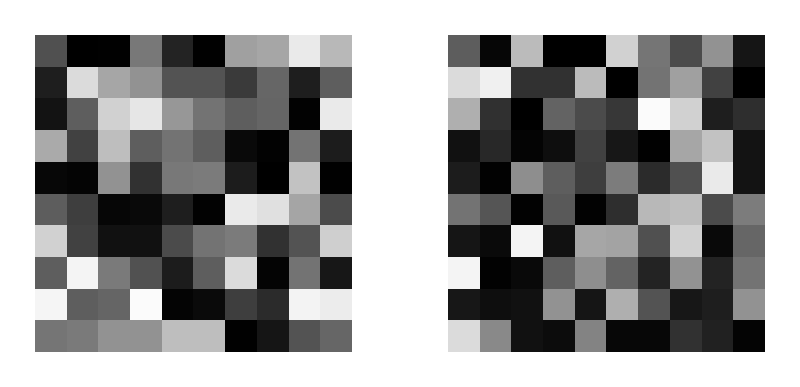

```mathematica
GraphicsGrid[{{ArrayPlot[Partition[Sin[dat[[1,1]]],10]],ArrayPlot[Partition[Sin[dat[[1,2]]],10]]}}]
```

```mathematica
plots=Table[GraphicsGrid[{{ArrayPlot[Partition[Sin[dat[[i,1]]],10]],ArrayPlot[Partition[Sin[dat[[i,2]]],10]]}}],{i,1,Length[dat]}];
```

```mathematica
Do[
Export["/Users/sachs/Documents/CPRM/output/animations/test1/"<>ToString[i]<>".png",plots[[i]]];
,{i,1,Length[dat]}
];
```

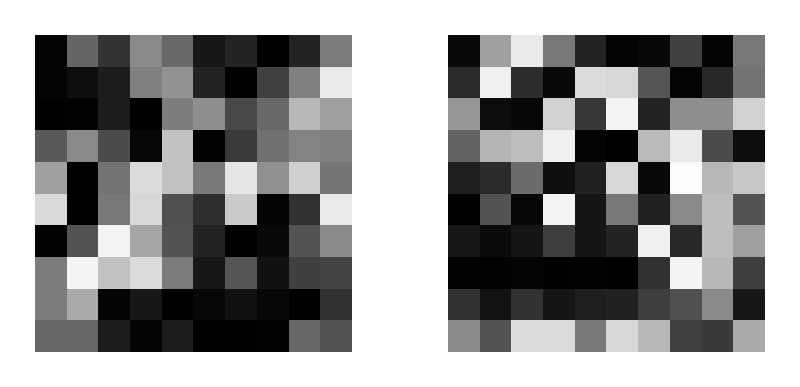

```mathematica
plots[[100]]
```